```mathematica
PermulateMultiply[Srtst_,list1_,list2_]:=Srtst/.list1/.list2;
```

```mathematica
PrmltMltplExch[llset_]:=Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}];
```

```mathematica
PrmltMltplExchPst[llset_]:={Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}],llset[[4]],llset[[5]]};
```

```mathematica
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
]
```

```mathematica
Exch[{{1,2,3,4},{2,3,1,4}}]
```

{1→2,2→3,3→1}

```mathematica
sta={1,2,3,4};
lis1={1->2,2->3,3->1};
list2={3->4,4->1,1->3};
PermulateMultiply[sta,lis1,list2]
```

{2,4,3,1}

```mathematica
PrmltMltplExch[{sta,lis1,list2}]
PrmltMltplExchPst[{sta,lis1,list2,4,5}]
```

{1→2,2→4,4→1}

{{1→2,2→4,4→1},4,5}

```mathematica
U:1;D:2;F:3;B:4;L:5;R:6; The all transformation are as follows:
S1, S2, S3, S4, S5, S6, S7, S8, S9. The symbolic here is same as the notebook I had worked before, the symbol Si represents the transformation Subscript[S, i] in my work
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
StartSet={31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29};
```

```mathematica
The symbol ISi represents the Inverse transformation of Si, it is also stand for (Subscript[S, i]^-1).
```

```mathematica
IS1=Exch[{StartSet,StartSet/.S1/.S1/.S1}];
IS2=Exch[{StartSet,StartSet/.S2/.S2/.S2}];
IS3=Exch[{StartSet,StartSet/.S3/.S3/.S3}];
IS4=Exch[{StartSet,StartSet/.S4/.S4/.S4}];
IS5=Exch[{StartSet,StartSet/.S5/.S5/.S5}];
IS6=Exch[{StartSet,StartSet/.S6/.S6/.S6}];
IS7=Exch[{StartSet,StartSet/.S7/.S7/.S7}];
IS8=Exch[{StartSet,StartSet/.S8/.S8/.S8}];
IS9=Exch[{StartSet,StartSet/.S9/.S9/.S9}];
```

```mathematica
All transformations contained in the parameter prmt
prmt={Subscript[S, 1],Subscript[S, 2],Subscript[S, 3],Subscript[S, 4],Subscript[S, 5],Subscript[S, 6],Subscript[S, 7],Subscript[S, 8],Subscript[S, 9],Subscript[S, 1]^-1,Subscript[S, 2]^-1,Subscript[S, 3]^-1,Subscript[S, 4]^-1,Subscript[S, 5]^-1,Subscript[S, 6]^-1,Subscript[S, 7]^-1,Subscript[S, 8]^-1,Subscript[S, 9]^-1}
```

```mathematica
prmt(*mypermutation*)={S1,S2,S3,S4,S5,S6,S7,S8,S9,IS1,IS2,IS3,IS4,IS5,IS6,IS7,IS8,IS9};
```

```mathematica
All transformations with the form like Subscript[S, i]^2, totally 9 transformations, ss[[1;;9]]
```

```mathematica
ss={};EndSet={};
For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[i]]/.prmt[[i]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[ss,trans,2],AppendTo[ss,{trans,i}]]]
ss//MatrixForm;
Clear[i,EndSet,trans]
```

```mathematica
Export["F:\\data\\ss.txt",ss]
```

F:\data\ss.txt

```mathematica
All transformations with the form like Subscript[S, j]^-1 Subscript[S, i]^2 Subscript[S, j], totally 63 transformations, issss[[1;;63]]
```

```mathematica
issss={};EndSet={};
For[j=1,j≤9,j++,
For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[j]]/.ss[[i,1]]/.prmt[[j+9]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[issss,trans,2],AppendTo[issss,{trans,j,i}]]
]
]
issss//MatrixForm;
Clear[i,j,EndSet,trans]
```

```mathematica
Export["F:\\data\\issss.txt",issss]
```

F:\data\issss.txt

```mathematica
All transformations with the form like Subscript[S, j] Subscript[S, i]^2 Subscript[S, j]^-1, totally 63 transformations, sssis[[1;;63]]
```

```mathematica
sssis={};EndSet={};
For[j=1,j≤9,j++,For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[j+9]]/.ss[[i,1]]/.prmt[[j]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[sssis,trans,2],AppendTo[sssis,{trans,j,i}]];]]
sssis//MatrixForm;
Clear[i,j,trans,EndSet]
```

```mathematica
Export["F:\\data\\sssis.txt",sssis]
```

F:\data\sssis.txt

```mathematica
All transformations with the form like Subscript[S, j] Subscript[S, i] Subscript[S, j]^-1, totally 63 transformations, ssis[[1;;63]]
```

```mathematica
ssis={};EndSet={};
For[j=1,j≤9,j++,For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[j+9]]/.prmt[[i]]/.prmt[[j]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[ssis,trans,2],AppendTo[ssis,{trans,j,i}]];]]
ssis//MatrixForm;
Clear[i,j,trans,EndSet]
```

```mathematica
Export["F:\\data\\ssis.txt",ssis]
```

F:\data\ssis.txt

```mathematica
All transformations with the form like Subscript[S, j]^-1 Subscript[S, i] Subscript[S, j], totally 63 transformations, isss[[1;;63]]
```

```mathematica
isss={};EndSet={};
For[j=1,j≤9,j++,For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[j]]/.prmt[[i]]/.prmt[[j+9]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[isss,trans,2],AppendTo[isss,{trans,j,i}]];]]
isss//MatrixForm;
Clear[i,j,trans,EndSet]
```

```mathematica
Export["F:\\data\\isss.txt",isss]
```

F:\data\isss.txt

```mathematica
All transformations with the form like Subscript[S, j]^-1 Subscript[S, i]^-1 Subscript[S, j], totally 63 transformations, isiss[[1;;63]]
```

```mathematica
isiss={};EndSet={};
For[j=1,j≤9,j++,For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[j]]/.prmt[[i+9]]/.prmt[[j+9]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[isiss,trans,2],AppendTo[isiss,{trans,j,i}]];]]
isiss//MatrixForm;
Clear[i,j,trans,EndSet]
```

```mathematica
Export["F:\\data\\isiss.txt",isiss]
```

F:\data\isiss.txt

```mathematica
All transformations with the form like Subscript[S, j] Subscript[S, i]^-1 Subscript[S, j]^-1, totally 63 transformations, sisis[[1;;63]]
```

```mathematica
sisis={};EndSet={};
For[j=1,j≤9,j++,For[i=1,i≤9,i++,EndSet=StartSet/.prmt[[j+9]]/.prmt[[i+9]]/.prmt[[j]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[sisis,trans,2],AppendTo[sisis,{trans,j,i}]];]]
sisis//MatrixForm;
Clear[i,j,trans,EndSet]
```

```mathematica
Export["F:\\data\\sisis.txt",sisis]
```

F:\data\sisis.txt

```mathematica
All transformations with the form like Subscript[S, j]^-1 Subscript[S, i] Subscript[S, j] Subscript[S, k] Subscript[S, l]^-1 Subscript[S, k]^-1, totally 3920 transformations, isss*sisis=issssisis[[1;;3920]]
```

```mathematica
issssisis={};EndSet={};trans={};
For[i=1,i≤63,i++,For[j=1,j≤63,j++,EndSet=StartSet/.sisis[[i,1]]/.isss[[j,1]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[issssisis,trans,2],AppendTo[issssisis,{trans,j,i}]];]]
issssisis//MatrixForm;
Clear[i,j,EndSet,trans]
```

```mathematica
Export["F:\\data\\issssisis.txt",issssisis]
```

F:\data\issssisis.txt

```mathematica
All transformations with the form like Subscript[S, m]^-1 Subscript[S, j]^-1 Subscript[S, i] Subscript[S, j] Subscript[S, k] Subscript[S, l]^-1 Subscript[S, k]^-1 Subscript[S, m], totally 33819 transformations, is*issssisis*s=isissssisiss[[1;;33819]]
```

```mathematica
isissssisiss={};EndSet={};trans={};
For[i=1,i≤3920,i++,For[j=1,j≤9,j++,EndSet=StartSet/.prmt[[j]]/.issssisis[[i,1]]/.prmt[[j+9]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[isissssisiss,trans,2],AppendTo[isissssisiss,{trans,j,i}]];]]
isissssisiss//MatrixForm;
Clear[i,EndSet,trans,j]
```

```mathematica
Export["F:\\data\\isissssisiss.txt",isissssisiss]
```

F:\data\isissssisiss.txt

```mathematica
All transformations' length less than or equal to 15 with the form like Subscript[S, m]^-1 Subscript[S, j]^-1 Subscript[S, i] Subscript[S, j] Subscript[S, k] Subscript[S, l]^-1 Subscript[S, k]^-1 Subscript[S, m], isissssisisslessfifteen[[1;;1097]]
```

```mathematica
isissssisisslessfifteen={};
For[i=2,i≤33819,i++,
If[
Length[isissssisiss[[i,1]]]≤15,
AppendTo[isissssisisslessfifteen,isissssisiss[[i]]]
]
]
```

```mathematica
Export["F:\\data\\isissssisisslessfifteen.txt",isissssisisslessfifteen]
```

F:\data\isissssisisslessfifteen.txt

```mathematica
isissssisisslessfifteen//MatrixForm
```

({12→32,14→62,16→48,18→14,22→42,32→52,42→18,48→12,52→16,62→22} | 1 | 31
{12→48,14→62,16→18,18→42,22→52,32→12,42→22,48→14,52→16,62→32} | 2 | 31
{12→68,14→62,16→18,18→42,26→52,32→12,42→26,52→16,62→32,68→14} | 3 | 31
{12→48,16→18,18→42,22→56,32→12,42→22,44→62,48→44,56→16,62→32} | 4 | 31
{12→48,14→62,16→42,22→38,28→14,38→52,42→22,48→28,52→16,62→12} | 5 | 31
{12→48,14→66,18→42,22→52,32→12,42→22,46→18,48→14,52→46,66→32} | 6 | 31
{12→48,14→62,16→54,22→52,34→12,42→22,48→14,52→16,54→42,62→34} | 7 | 31
{12→48,14→32,18→42,22→24,24→52,32→12,42→22,48→58,52→18,58→14} | 8 | 31
{14→62,16→18,18→44,32→56,44→66,46→14,52→16,56→46,62→32,66→52} | 9 | 31
{12→58,14→62,16→18,18→42,24→52,32→12,42→24,52→16,58→14,62→32} | 1 | 52
{12→16,14→58,16→52,18→42,24→32,32→12,42→62,52→24,58→18,62→14} | 2 | 52
{12→16,14→48,16→52,18→42,22→32,32→12,42→62,48→18,52→22,62→14} | 3 | 52
{12→16,16→56,18→42,32→12,34→32,42→62,44→54,54→18,56→34,62→44} | 4 | 52
{12→48,14→58,16→52,22→62,24→12,42→22,48→16,52→24,58→42,62→14} | 5 | 52
{12→46,14→58,18→42,24→32,32→12,42→66,46→52,52→24,58→18,66→14} | 6 | 52
{12→16,14→58,16→52,24→34,34→12,42→62,52→24,54→42,58→54,62→14} | 7 | 52
{12→52,14→58,18→42,24→68,26→18,32→12,42→14,52→24,58→26,68→32} | 8 | 52
{14→58,16→52,18→44,24→32,32→56,44→62,52→24,56→16,58→18,62→14} | 9 | 52
{12→64,24→42,34→56,36→54,42→36,44→24,54→44,56→58,58→12,64→34} | 1 | 85
{14→34,24→52,34→56,44→66,46→58,52→54,54→44,56→46,58→14,66→24} | 2 | 85
{14→64,22→52,34→56,36→54,44→22,48→14,52→36,54→44,56→48,64→34} | 3 | 85
{14→58,24→34,34→56,36→52,44→64,52→24,54→44,56→36,58→54,64→14} | 4 | 85
{14→64,24→52,34→56,36→54,44→24,52→36,54→44,56→58,58→14,64→34} | 5 | 85
{14→62,16→54,24→52,34→56,44→24,52→16,54→44,56→58,58→14,62→34} | 6 | 85
{14→18,18→38,24→52,28→44,32→28,38→56,44→24,52→32,56→58,58→14} | 7 | 85
{24→36,26→58,34→56,36→54,44→68,54→44,56→26,58→64,64→34,68→24} | 8 | 85
{14→64,22→58,24→52,34→22,36→54,48→24,52→36,54→48,58→14,64→34} | 9 | 85
{15→65,25→55,35→15,45→25,55→45,65→35} | 1 | 94
{15→35,25→45,35→55,45→65,55→15,65→25} | 2 | 94
{15→45,25→35,35→55,45→65,55→25,65→15} | 5 | 94
{18→68,26→56,32→26,36→18,44→66,46→64,56→46,64→32,66→36,68→44} | 1 | 100
{16→68,26→46,34→62,36→54,46→64,54→16,62→26,64→34,66→36,68→66} | 2 | 100
{16→38,28→56,36→16,38→44,44→66,46→64,56→46,62→28,64→62,66→36} | 3 | 100
{16→68,24→66,26→58,36→16,46→64,58→46,62→26,64→62,66→36,68→24} | 4 | 100
{16→68,26→56,36→16,44→66,46→64,56→46,62→26,64→62,66→36,68→44} | 5 | 100
{16→46,26→62,36→56,44→68,46→64,56→26,62→66,64→44,66→36,68→16} | 6 | 100
{16→68,18→62,26→56,32→16,44→66,46→18,56→46,62→26,66→32,68→44} | 7 | 100
{14→62,16→44,36→52,44→66,46→64,52→16,56→46,62→56,64→14,66→36} | 8 | 100
{12→36,16→68,22→42,26→22,36→16,42→64,48→12,62→26,64→62,68→48} | 9 | 100
{14→46,28→52,34→38,36→54,38→14,46→64,52→66,54→28,64→34,66→36} | 1 | 106
{18→64,28→32,32→36,34→56,36→54,38→18,44→28,54→44,56→38,64→34} | 2 | 106
{18→46,24→32,32→66,34→58,36→54,46→64,54→24,58→18,64→34,66→36} | 3 | 106
{14→38,18→46,28→32,32→66,36→52,38→18,46→64,52→28,64→14,66→36} | 4 | 106
{12→66,18→42,32→12,34→18,36→54,42→46,46→64,54→32,64→34,66→36} | 5 | 106
{16→54,18→26,26→62,28→32,32→68,34→38,38→18,54→28,62→34,68→16} | 6 | 106
{18→38,28→64,32→28,34→66,36→54,38→36,46→18,54→46,64→34,66→32} | 7 | 106
{18→46,28→32,32→66,34→38,36→54,38→18,46→64,54→28,64→34,66→36} | 8 | 106
{12→36,18→42,28→32,32→12,34→38,36→54,38→18,42→64,54→28,64→34} | 9 | 106
{15→55,25→65,35→15,45→25,55→35,65→45} | 5 | 115
{15→55,25→65,35→25,45→15,55→45,65→35} | 8 | 115
{16→48,22→34,34→56,44→66,46→62,48→54,54→44,56→46,62→22,66→16} | 1 | 121
{12→48,22→56,36→12,42→22,44→66,46→64,48→44,56→46,64→42,66→36} | 2 | 121
{12→68,26→34,34→56,42→26,44→66,46→42,54→44,56→46,66→12,68→54} | 3 | 121
{12→48,14→58,22→14,24→66,42→22,46→42,48→52,52→24,58→46,66→12} | 4 | 121
{22→38,28→54,34→56,38→34,44→66,46→22,48→28,54→44,56→46,66→48} | 5 | 121
{12→48,22→34,26→42,34→56,42→22,44→68,48→54,54→44,56→26,68→12} | 6 | 121
{12→48,22→38,28→44,38→56,42→22,44→66,46→42,48→28,56→46,66→12} | 7 | 121
{12→48,22→34,34→56,42→22,44→66,46→42,48→54,54→44,56→46,66→12} | 8 | 121
{12→56,22→42,34→22,42→44,44→66,46→54,48→12,54→48,56→46,66→34} | 9 | 121
{14→68,22→38,24→22,26→58,28→52,38→14,48→28,52→26,58→48,68→24} | 1 | 157
{18→68,22→38,24→22,26→58,28→32,32→26,38→18,48→28,58→48,68→24} | 2 | 157
{18→38,22→26,24→32,26→58,28→48,32→28,38→22,48→68,58→18,68→24} | 3 | 157
{18→68,22→38,26→54,28→32,32→26,34→22,38→18,48→28,54→48,68→34} | 4 | 157
{12→26,18→42,24→38,26→58,28→32,32→12,38→18,42→68,58→28,68→24} | 5 | 157
{18→64,22→38,24→22,28→32,32→36,36→58,38→18,48→28,58→48,64→24} | 6 | 157
{22→36,24→22,26→58,34→26,36→54,48→64,54→68,58→48,64→34,68→24} | 7 | 157
{16→68,18→16,22→38,26→48,28→32,32→62,38→18,48→28,62→26,68→22} | 8 | 157
{18→68,24→66,26→58,28→32,32→26,38→18,46→28,58→46,66→38,68→24} | 9 | 157
{18→48,22→38,24→68,26→32,28→24,32→22,38→58,48→28,58→26,68→18} | 1 | 178
{16→48,22→38,24→68,26→62,28→24,38→58,48→28,58→26,62→22,68→16} | 2 | 178
{16→68,22→38,24→22,26→58,28→62,38→16,48→28,58→48,62→26,68→24} | 3 | 178
{16→48,22→38,26→62,28→34,34→68,38→54,48→28,54→26,62→22,68→16} | 4 | 178
{16→28,18→58,24→68,26→62,28→32,32→24,38→18,58→26,62→38,68→16} | 5 | 178
{22→38,24→64,28→24,36→66,38→58,46→48,48→28,58→36,64→46,66→22} | 6 | 178
{16→48,22→36,24→68,26→62,36→58,48→64,58→26,62→22,64→24,68→16} | 7 | 178
{14→22,16→52,22→38,26→62,28→68,38→26,48→28,52→48,62→14,68→16} | 8 | 178
{16→46,24→68,26→62,28→24,38→58,46→28,58→26,62→66,66→38,68→16} | 9 | 178
{14→44,24→52,34→64,36→58,44→54,52→56,54→36,56→34,58→14,64→24} | 1 | 206
{18→66,24→32,32→46,34→24,44→54,46→56,54→58,56→34,58→18,66→44} | 2 | 206
{18→44,22→32,32→56,34→64,36→48,44→54,48→18,54→36,56→34,64→22} | 3 | 206
{14→64,18→24,24→52,32→58,34→32,36→54,52→36,54→18,58→14,64→34} | 4 | 206
{12→56,24→12,34→64,36→58,42→44,44→54,54→36,56→34,58→42,64→24} | 5 | 206
{16→58,18→44,24→32,32→56,34→62,44→54,54→16,56→34,58→18,62→24} | 6 | 206
{18→24,24→34,28→32,32→58,34→56,38→18,44→28,54→44,56→38,58→54} | 7 | 206
{18→44,26→18,32→56,34→64,36→26,44→54,54→36,56→34,64→68,68→32} | 8 | 206
{18→48,22→34,24→32,32→22,34→64,36→58,48→54,54→36,58→18,64→24} | 9 | 206
{12→18,18→28,28→12,32→38,38→42,42→32} | 1 | 255
{14→16,16→28,28→14,38→52,52→62,62→38} | 2 | 255
{14→16,16→24,24→14,52→62,58→52,62→58} | 3 | 255
{16→28,28→44,38→56,44→16,56→62,62→38} | 4 | 255
{14→16,16→32,18→52,32→14,52→62,62→18} | 5 | 255
{14→46,28→14,38→52,46→28,52→66,66→38} | 6 | 255
{14→16,16→64,36→52,52→62,62→36,64→14} | 7 | 255
{14→38,24→14,28→58,38→24,52→28,58→52} | 8 | 255
{12→48,22→38,24→42,26→58,28→26,38→68,42→22,48→28,58→12,68→24} | 1 | 264
{14→48,22→38,24→52,26→58,28→26,38→68,48→28,52→22,58→14,68→24} | 2 | 264
{14→68,22→52,24→28,26→58,28→48,38→22,48→14,52→26,58→38,68→24} | 3 | 264
{22→38,26→54,28→26,34→56,38→68,44→48,48→28,54→44,56→22,68→34} | 4 | 264
{14→28,18→68,24→52,26→58,28→32,32→26,38→18,52→38,58→14,68→24} | 5 | 264
{14→48,22→38,24→52,28→36,36→58,38→64,48→28,52→22,58→14,64→24} | 6 | 264
{14→48,22→36,24→52,26→58,36→68,48→64,52→22,58→14,64→26,68→24} | 7 | 264
{14→46,24→52,26→58,28→26,38→68,46→28,52→66,58→14,66→38,68→24} | 9 | 264
{15→45,25→35,35→65,45→55,55→15,65→25} | 1 | 270
{15→65,25→55,35→25,45→15,55→35,65→45} | 2 | 270
{12→16,14→38,16→52,18→42,28→32,32→12,38→18,42→62,52→28,62→14} | 1 | 276
{12→32,14→12,16→52,18→38,28→62,32→28,38→16,42→18,52→42,62→14} | 2 | 276
{12→32,14→12,16→52,18→58,24→62,32→24,42→18,52→42,58→16,62→14} | 3 | 276
{12→32,16→56,18→38,28→62,32→28,38→16,42→18,44→12,56→42,62→44} | 4 | 276
{12→32,14→48,16→52,18→16,22→42,32→62,42→18,48→12,52→22,62→14} | 5 | 276
{12→32,14→12,18→38,28→66,32→28,38→46,42→18,46→52,52→42,66→14} | 6 | 276
{12→34,14→12,16→52,34→64,36→16,42→54,52→42,54→36,62→14,64→62} | 7 | 276
{12→32,14→58,18→38,24→42,28→14,32→28,38→52,42→18,52→24,58→12} | 8 | 276
{14→56,16→52,18→38,28→62,32→28,38→16,44→18,52→44,56→32,62→14} | 9 | 276
{12→16,16→34,18→42,22→38,28→32,32→12,34→64,36→22,38→18,42→62,48→28,54→36,62→54,64→48} | 1 | 297
{12→56,14→12,16→52,22→38,28→62,34→48,38→16,42→44,44→54,48→28,52→42,54→22,56→34,62→14} | 2 | 297
{12→34,14→12,16→52,24→62,26→58,34→64,36→26,42→54,52→42,54→36,58→16,62→14,64→68,68→24} | 3 | 297
{12→14,14→64,16→56,22→38,28→62,36→22,38→16,42→52,44→12,48→28,52→36,56→42,62→44,64→48} | 4 | 297
{14→48,16→52,18→16,22→54,28→32,32→62,34→64,36→38,38→18,48→34,52→22,54→36,62→14,64→28} | 5 | 297
{12→34,14→12,16→22,22→38,28→66,34→62,38→46,42→54,46→52,48→28,52→42,54→16,62→48,66→14} | 6 | 297
{12→38,14→12,16→52,18→48,22→36,28→32,32→22,36→16,38→18,42→28,48→64,52→42,62→14,64→62} | 7 | 297
{12→34,14→58,22→38,24→42,28→14,34→64,36→22,38→52,42→54,48→28,52→24,54→36,58→12,64→48} | 8 | 297
{14→56,16→52,28→62,34→64,36→66,38→16,44→54,46→28,52→44,54→36,56→34,62→14,64→46,66→38} | 9 | 297
{12→48,14→38,18→42,22→66,28→32,32→12,38→18,42→22,44→14,46→56,48→46,52→28,56→52,66→44} | 1 | 312
{14→48,16→52,18→38,22→36,28→62,32→28,36→66,38→16,46→32,48→64,52→22,62→14,64→46,66→18} | 2 | 312
{14→68,16→52,18→58,24→62,26→66,32→24,44→18,46→56,52→26,56→32,58→16,62→14,66→44,68→46} | 3 | 312
{16→56,18→38,22→66,24→18,28→62,32→28,38→16,44→48,46→58,48→46,56→22,58→32,62→44,66→24} | 4 | 312
{12→32,14→28,16→52,18→16,28→46,32→62,38→66,42→18,44→42,46→56,52→38,56→12,62→14,66→44} | 5 | 312
{14→48,18→38,22→68,26→56,28→66,32→28,38→46,44→18,46→52,48→26,52→22,56→32,66→14,68→44} | 6 | 312
{14→48,16→52,22→66,34→64,36→16,44→54,46→56,48→46,52→22,54→36,56→34,62→14,64→62,66→44} | 7 | 312
{14→58,18→38,22→66,24→22,28→14,32→28,38→52,44→18,46→56,48→46,52→24,56→32,58→48,66→44} | 8 | 312
{12→48,14→46,16→52,18→38,22→32,28→62,32→28,38→16,42→22,46→42,48→18,52→66,62→14,66→12} | 9 | 312
{16→68,26→36,36→66,44→62,46→56,56→16,62→26,64→46,66→44,68→64} | 1 | 334
{12→68,26→54,34→64,36→66,42→26,46→12,54→36,64→46,66→42,68→34} | 2 | 334
{12→38,28→36,36→66,38→64,42→28,44→42,46→56,56→12,64→46,66→44} | 3 | 334
{12→68,24→42,26→36,36→66,42→26,46→58,58→12,64→46,66→24,68→64} | 4 | 334
{22→26,26→36,36→66,44→22,46→56,48→68,56→48,64→46,66→44,68→64} | 5 | 334
{12→64,16→68,26→56,36→16,42→36,44→42,56→12,62→26,64→62,68→44} | 6 | 334
{12→68,18→46,26→32,32→66,42→26,44→42,46→56,56→12,66→44,68→18} | 7 | 334
{12→16,16→64,36→66,42→62,44→42,46→56,56→12,62→36,64→46,66→44} | 8 | 334
{12→48,22→56,26→36,36→12,42→22,44→26,48→44,56→68,64→42,68→64} | 9 | 334
{14→16,16→26,26→14,52→62,62→68,68→52} | 1 | 447
{12→26,18→12,26→18,32→42,42→68,68→32} | 2 | 447
{12→28,18→12,28→18,32→42,38→32,42→38} | 3 | 447
{12→22,22→68,26→42,42→48,48→26,68→12} | 5 | 447
{12→36,18→12,32→42,36→18,42→64,64→32} | 6 | 447
{12→26,26→54,34→42,42→68,54→12,68→34} | 7 | 447
{12→62,16→32,18→12,32→42,42→16,62→18} | 8 | 447
{18→56,26→18,32→44,44→68,56→26,68→32} | 9 | 447
{14→26,15→55,16→24,24→16,25→65,26→14,35→25,45→15,52→68,55→45,58→62,62→58,65→35,68→52} | 1 | 456
{12→24,15→45,18→26,24→12,25→35,26→18,32→68,35→55,42→58,45→65,55→25,58→42,65→15,68→32} | 2 | 456
{12→22,15→55,18→28,22→12,25→65,28→18,32→38,35→25,38→32,42→48,45→15,48→42,55→45,65→35} | 3 | 456
{12→34,15→55,18→26,25→65,26→18,32→68,34→12,35→25,42→54,45→15,54→42,55→45,65→35,68→32} | 4 | 456
{12→68,15→35,22→58,24→48,25→45,26→42,35→65,42→26,45→55,48→24,55→25,58→22,65→15,68→12} | 5 | 456
{12→24,15→55,18→36,24→12,25→65,32→64,35→25,36→18,42→58,45→15,55→45,58→42,64→32,65→35} | 6 | 456
{12→24,15→55,24→12,25→65,26→54,34→68,35→25,42→58,45→15,54→26,55→45,58→42,65→35,68→34} | 7 | 456
{12→68,15→35,16→32,18→62,25→45,26→42,32→16,35→65,42→26,45→55,55→25,62→18,65→15,68→12} | 8 | 456
{15→55,18→26,24→56,25→65,26→18,32→68,35→25,44→58,45→15,55→45,56→24,58→44,65→35,68→32} | 9 | 456
{14→58,16→52,18→68,24→34,26→62,32→26,34→56,44→32,52→24,54→44,56→18,58→54,62→14,68→16} | 1 | 468
{12→32,16→68,18→58,24→56,26→42,32→24,42→18,44→66,46→16,56→46,58→44,62→26,66→62,68→12} | 2 | 468
{12→32,16→38,18→48,22→34,28→42,32→22,34→56,38→12,42→18,44→62,48→54,54→44,56→16,62→28} | 3 | 468
{12→32,14→58,16→68,18→54,24→62,26→42,32→34,34→14,42→18,52→24,54→52,58→16,62→26,68→12} | 4 | 468
{12→24,16→68,22→42,24→34,26→22,34→56,42→58,44→62,48→12,54→44,56→16,58→54,62→26,68→48} | 5 | 468
{12→32,18→58,24→34,32→24,34→56,36→42,42→18,44→66,46→64,54→44,56→46,58→54,64→12,66→36} | 6 | 468
{12→34,16→68,24→38,26→42,28→44,34→24,38→56,42→54,44→62,54→58,56→16,58→28,62→26,68→12} | 7 | 468
{12→32,14→62,16→12,18→26,26→54,32→68,34→56,42→18,44→14,52→16,54→44,56→52,62→42,68→34} | 8 | 468
{16→68,18→58,22→16,24→34,26→44,32→24,34→22,44→18,48→62,54→48,56→32,58→54,62→26,68→56} | 9 | 468
{12→66,14→12,16→52,24→68,26→62,36→58,42→46,46→64,52→42,58→26,62→14,64→24,66→36,68→16} | 1 | 480
{12→32,14→36,18→14,24→68,26→42,32→52,34→24,36→54,42→18,52→64,54→58,58→26,64→34,68→12} | 2 | 480
{12→32,14→66,18→14,22→38,28→42,32→52,36→48,38→12,42→18,46→64,48→28,52→46,64→22,66→36} | 3 | 480
{12→32,18→44,26→42,32→56,34→68,36→54,42→18,44→66,46→64,54→26,56→46,64→34,66→36,68→12} | 4 | 480
{12→52,14→66,22→42,24→68,26→22,36→58,42→14,46→64,48→12,52→46,58→26,64→24,66→36,68→48} | 5 | 480
{12→32,14→68,16→58,18→14,24→64,26→62,32→52,36→42,42→18,52→26,58→36,62→24,64→12,68→16} | 6 | 480
{12→34,14→66,18→24,24→68,26→42,32→58,34→52,42→54,46→18,52→46,54→14,58→26,66→32,68→12} | 7 | 480
{12→32,16→12,18→58,24→46,26→62,32→24,36→26,42→18,46→64,58→66,62→42,64→68,66→36,68→16} | 8 | 480
{12→36,14→12,18→14,24→68,26→44,32→52,36→58,42→64,44→18,52→42,56→32,58→26,64→24,68→56} | 9 | 480
{12→32,14→12,16→52,18→68,26→62,32→26,42→18,52→42,62→14,68→16} | 1 | 489
{12→32,14→62,16→68,18→14,26→42,32→52,42→18,52→16,62→26,68→12} | 2 | 489
{12→32,14→62,16→38,18→14,28→42,32→52,38→12,42→18,52→16,62→28} | 3 | 489
{12→32,16→68,18→44,26→42,32→56,42→18,44→62,56→16,62→26,68→12} | 4 | 489
{12→52,14→62,16→68,22→42,26→22,42→14,48→12,52→16,62→26,68→48} | 5 | 489
{12→32,14→66,18→14,32→52,36→42,42→18,46→64,52→46,64→12,66→36} | 6 | 489
{12→34,14→62,16→68,26→42,34→52,42→54,52→16,54→14,62→26,68→12} | 7 | 489
{12→32,14→62,16→12,18→58,24→52,32→24,42→18,52→16,58→14,62→42} | 8 | 489
{14→62,16→68,18→14,26→44,32→52,44→18,52→16,56→32,62→26,68→56} | 9 | 489
{12→54,24→64,34→46,36→44,42→34,44→58,46→42,54→66,56→24,58→36,64→56,66→12} | 1 | 575
{14→44,24→34,34→46,36→14,44→36,46→24,52→56,54→66,56→64,58→54,64→52,66→58} | 2 | 575
{14→54,22→64,34→46,36→44,44→48,46→52,48→36,52→34,54→66,56→22,64→56,66→14} | 3 | 575
{14→46,24→54,34→64,36→24,44→52,46→56,52→66,54→36,56→14,58→34,64→58,66→44} | 4 | 575
{14→54,24→64,34→46,36→44,44→58,46→52,52→34,54→66,56→24,58→36,64→56,66→14} | 5 | 575
{14→54,16→44,24→62,26→52,34→26,44→58,52→34,54→68,56→24,58→16,62→56,68→14} | 6 | 575
{14→28,18→56,24→18,28→66,32→44,38→46,44→58,46→52,52→38,56→24,58→32,66→14} | 7 | 575
{24→34,26→36,34→46,36→44,44→26,46→24,54→66,56→68,58→54,64→56,66→58,68→64} | 8 | 575
{12→14,14→54,22→24,24→64,34→42,36→48,42→52,48→58,52→34,54→12,58→36,64→22} | 9 | 575
{12→58,24→64,34→56,36→54,42→24,44→12,54→44,56→42,58→36,64→34} | 1 | 590
{14→58,24→34,34→56,44→66,46→52,52→24,54→44,56→46,58→54,66→14} | 2 | 590
{14→48,22→64,34→56,36→54,44→14,48→36,52→22,54→44,56→52,64→34} | 3 | 590
{14→58,24→44,34→64,36→52,44→54,52→24,54→36,56→34,58→56,64→14} | 4 | 590
{14→58,24→64,34→56,36→54,44→14,52→24,54→44,56→52,58→36,64→34} | 5 | 590
{14→58,16→54,24→62,34→56,44→14,52→24,54→44,56→52,58→16,62→34} | 6 | 590
{14→58,18→38,24→18,28→44,32→28,38→56,44→14,52→24,56→52,58→32} | 7 | 590
{24→68,26→36,34→56,36→54,44→58,54→44,56→24,58→26,64→34,68→64} | 8 | 590
{14→58,22→52,24→64,34→22,36→54,48→14,52→24,54→48,58→36,64→34} | 9 | 590
{12→26,24→64,26→56,36→42,42→68,44→58,56→24,58→36,64→12,68→44} | 1 | 620
{14→26,24→34,26→46,34→14,46→24,52→68,54→52,58→54,66→58,68→66} | 2 | 620
{14→28,22→64,28→56,36→52,38→44,44→48,48→36,52→38,56→22,64→14} | 3 | 620
{24→54,26→58,34→64,36→56,44→26,54→36,56→68,58→34,64→44,68→24} | 4 | 620
{14→26,24→64,26→56,36→52,44→58,52→68,56→24,58→36,64→14,68→44} | 5 | 620
{14→36,16→52,24→62,36→56,44→58,52→64,56→24,58→16,62→14,64→44} | 6 | 620
{14→26,18→14,24→18,26→56,32→52,44→58,52→68,56→24,58→32,68→44} | 7 | 620
{16→44,24→16,26→36,36→24,44→26,56→68,58→62,62→56,64→58,68→64} | 8 | 620
{14→26,22→24,24→64,26→22,36→52,48→58,52→68,58→36,64→14,68→48} | 9 | 620
{16→48,22→38,24→62,26→58,28→26,38→68,48→28,58→16,62→22,68→24} | 1 | 636
{12→68,22→42,24→28,26→58,28→48,38→22,42→26,48→12,58→38,68→24} | 3 | 636
{12→48,22→38,26→54,28→26,34→42,38→68,42→22,48→28,54→12,68→34} | 4 | 636
{12→48,22→38,24→42,28→36,36→58,38→64,42→22,48→28,58→12,64→24} | 6 | 636
{12→48,22→36,24→42,26→58,36→68,42→22,48→64,58→12,64→26,68→24} | 7 | 636
{12→48,16→68,22→38,26→12,28→62,38→16,42→22,48→28,62→26,68→42} | 8 | 636
{24→44,26→58,28→26,38→68,44→66,46→28,56→46,58→56,66→38,68→24} | 9 | 636
{15→25,25→15,55→65,65→55} | 1 | 639
{15→25,25→15,35→45,45→35} | 2 | 639
{35→45,45→35,55→65,65→55} | 5 | 639
{12→32,14→62,16→12,18→38,28→52,32→28,38→14,42→18,52→16,62→42} | 1 | 648
{12→14,14→62,16→38,18→42,28→32,32→12,38→18,42→52,52→16,62→28} | 2 | 648
{12→14,14→62,16→58,18→42,24→32,32→12,42→52,52→16,58→18,62→24} | 3 | 648
{12→44,16→38,18→42,28→32,32→12,38→18,42→56,44→62,56→16,62→28} | 4 | 648
{12→14,14→66,18→42,28→32,32→12,38→18,42→52,46→38,52→46,66→28} | 6 | 648
{12→14,14→62,16→36,34→12,36→54,42→52,52→16,54→42,62→64,64→34} | 7 | 648
{12→58,14→28,18→42,24→52,28→32,32→12,38→18,42→24,52→38,58→14} | 8 | 648
{14→62,16→38,18→44,28→32,32→56,38→18,44→52,52→16,56→14,62→28} | 9 | 648
{15→35,25→45,35→65,45→55,55→25,65→15} | 5 | 654
{18→56,26→66,32→44,34→68,36→32,44→36,46→34,54→26,56→64,64→18,66→54,68→46} | 1 | 703
{16→46,26→36,34→16,36→44,44→26,46→34,54→62,56→68,62→66,64→56,66→54,68→64} | 2 | 703
{16→56,28→66,34→38,36→62,38→46,44→36,46→34,54→28,56→64,62→44,64→16,66→54} | 3 | 703
{14→68,16→58,24→36,26→66,36→62,46→14,52→26,58→64,62→24,64→16,66→52,68→46} | 4 | 703
{16→56,26→66,34→68,36→62,44→36,46→34,54→26,56→64,62→44,64→16,66→54,68→46} | 5 | 703
{16→66,26→34,34→64,36→68,44→16,46→56,54→36,56→62,62→46,64→26,66→44,68→54} | 6 | 703
{16→56,18→16,26→66,28→26,32→62,38→68,44→32,46→38,56→18,62→44,66→28,68→46} | 7 | 703
{14→44,16→46,34→16,36→14,44→36,46→34,52→56,54→62,56→64,62→66,64→52,66→54} | 8 | 703
{12→54,16→22,22→64,26→12,34→68,36→62,42→34,48→36,54→26,62→48,64→16,68→42} | 9 | 703
{18→56,26→32,32→44,36→26,44→66,46→64,56→46,64→68,66→36,68→18} | 1 | 718
{16→46,26→62,34→68,36→54,46→64,54→26,62→66,64→34,66→36,68→16} | 2 | 718
{16→56,28→62,36→28,38→16,44→66,46→64,56→46,62→44,64→38,66→36} | 3 | 718
{16→58,24→66,26→62,36→26,46→64,58→46,62→24,64→68,66→36,68→16} | 4 | 718
{16→56,26→62,36→26,44→66,46→64,56→46,62→44,64→68,66→36,68→16} | 5 | 718
{16→36,26→62,36→66,44→68,46→56,56→26,62→64,64→46,66→44,68→16} | 6 | 718
{16→56,18→68,26→62,32→26,44→66,46→18,56→46,62→44,66→32,68→16} | 7 | 718
{14→44,16→52,36→62,44→66,46→64,52→56,56→46,62→14,64→16,66→36} | 8 | 718
{12→36,16→22,22→42,26→62,36→26,42→64,48→12,62→48,64→68,68→16} | 9 | 718
{12→64,18→56,26→12,32→44,36→32,42→36,44→68,56→26,64→18,68→42} | 1 | 748
{14→34,16→46,26→14,34→16,46→26,52→54,54→62,62→66,66→68,68→52} | 2 | 748
{14→64,16→56,28→14,36→62,38→52,44→38,52→36,56→28,62→44,64→16} | 3 | 748
{16→58,24→68,26→44,36→62,44→64,56→36,58→26,62→24,64→16,68→56} | 4 | 748
{14→64,16→56,26→14,36→62,44→68,52→36,56→26,62→44,64→16,68→52} | 5 | 748
{14→62,16→66,36→14,44→64,46→56,52→16,56→36,62→46,64→52,66→44} | 6 | 748
{14→18,16→56,18→16,26→14,32→62,44→68,52→32,56→26,62→44,68→52} | 7 | 748
{14→44,16→24,24→36,36→14,44→16,52→56,56→62,58→64,62→58,64→52} | 8 | 748
{14→64,16→22,22→26,26→14,36→62,48→68,52→36,62→48,64→16,68→52} | 9 | 748
{14→36,28→46,34→28,36→44,38→66,44→14,46→34,52→64,54→38,56→52,64→56,66→54} | 1 | 767
{18→54,28→64,32→34,34→46,36→44,38→36,44→38,46→32,54→66,56→28,64→56,66→18} | 2 | 767
{18→36,24→46,32→64,34→24,36→44,44→18,46→34,54→58,56→32,58→66,64→56,66→54} | 3 | 767
{14→28,18→36,24→18,28→46,32→64,36→24,38→66,46→14,52→38,58→32,64→58,66→52} | 4 | 767
{12→64,18→66,32→46,34→32,36→44,42→36,44→42,46→34,54→18,56→12,64→56,66→54} | 5 | 767
{16→44,18→16,26→34,28→26,32→62,34→28,38→68,44→18,54→38,56→32,62→56,68→54} | 6 | 767
{18→56,28→36,32→44,34→18,36→66,38→64,44→54,46→38,54→32,56→34,64→46,66→28} | 7 | 767
{18→36,28→46,32→64,34→28,36→44,38→66,44→18,46→34,54→38,56→32,64→56,66→54} | 8 | 767
{12→54,18→36,22→32,28→42,32→64,34→28,36→48,38→12,42→34,48→18,54→38,64→22} | 9 | 767
{16→36,28→46,34→16,36→28,38→66,46→34,54→62,62→64,64→38,66→54} | 1 | 788
{12→54,28→64,34→38,36→44,38→36,42→34,44→42,54→28,56→12,64→56} | 2 | 788
{12→36,24→46,34→12,36→24,42→64,46→34,54→42,58→66,64→58,66→54} | 3 | 788
{12→36,14→12,28→46,36→28,38→66,42→64,46→14,52→42,64→38,66→52} | 4 | 788
{18→66,22→64,32→46,34→48,36→32,46→34,48→36,54→22,64→18,66→54} | 5 | 788
{12→16,16→28,26→34,28→26,34→12,38→68,42→62,54→42,62→38,68→54} | 6 | 788
{12→32,18→36,28→42,32→64,36→66,38→12,42→18,46→38,64→46,66→28} | 7 | 788
{12→36,28→46,34→12,36→28,38→66,42→64,46→34,54→42,64→38,66→54} | 8 | 788
{12→54,28→42,34→56,36→28,38→12,42→34,44→64,54→44,56→36,64→38} | 9 | 788
{14→38,28→46,34→52,36→54,38→66,46→64,52→28,54→14,64→34,66→36} | 1 | 803
{18→38,28→64,32→28,34→56,36→54,38→36,44→18,54→44,56→32,64→34} | 2 | 803
{18→58,24→46,32→24,34→32,36→54,46→64,54→18,58→66,64→34,66→36} | 3 | 803
{14→32,18→38,28→46,32→28,36→52,38→66,46→64,52→18,64→14,66→36} | 4 | 803
{12→32,18→66,32→46,34→12,36→54,42→18,46→64,54→42,64→34,66→36} | 5 | 803
{16→54,18→38,26→62,28→26,32→28,34→32,38→68,54→18,62→34,68→16} | 6 | 803
{18→38,28→54,32→28,34→64,36→66,38→34,46→18,54→36,64→46,66→32} | 7 | 803
{18→38,28→46,32→28,34→32,36→54,38→66,46→64,54→18,64→34,66→36} | 8 | 803
{12→36,18→38,28→42,32→28,34→32,36→54,38→12,42→64,54→18,64→34} | 9 | 803
{16→34,22→44,34→46,36→22,44→36,46→16,48→56,54→66,56→64,62→54,64→48,66→62} | 1 | 894
{12→56,22→66,34→48,36→42,42→44,44→36,46→34,48→46,54→22,56→64,64→12,66→54} | 2 | 894
{12→34,26→44,34→46,36→26,42→54,44→36,46→12,54→66,56→64,64→68,66→42,68→56} | 3 | 894
{12→14,14→46,22→24,24→36,36→22,42→52,46→12,48→58,52→66,58→64,64→48,66→42} | 4 | 894
{22→54,28→56,34→46,36→38,38→44,44→36,46→48,48→34,54→66,56→64,64→28,66→22} | 5 | 894
{12→34,16→22,22→44,26→12,34→26,42→54,44→16,48→56,54→68,56→62,62→48,68→42} | 6 | 894
{12→38,18→48,22→44,28→66,32→22,38→46,42→28,44→32,46→12,48→56,56→18,66→42} | 7 | 894
{12→34,22→44,34→46,36→22,42→54,44→36,46→12,48→56,54→66,56→64,64→48,66→42} | 8 | 894
{12→44,22→64,34→42,36→66,42→56,44→54,46→22,48→36,54→12,56→34,64→46,66→48} | 9 | 894
{16→34,28→44,34→46,38→56,44→16,46→28,54→66,56→62,62→54,66→38} | 1 | 915
{12→56,28→66,36→38,38→46,42→44,44→36,46→42,56→64,64→28,66→12} | 2 | 915
{12→34,24→44,34→46,42→54,44→12,46→24,54→66,56→42,58→56,66→58} | 3 | 915
{12→14,14→46,24→12,28→24,38→58,42→52,46→28,52→66,58→42,66→38} | 4 | 915
{18→56,22→54,32→44,34→46,44→48,46→32,48→34,54→66,56→22,66→18} | 5 | 915
{12→34,26→28,28→44,34→26,38→56,42→54,44→12,54→68,56→42,68→38} | 6 | 915
{12→38,28→66,36→56,38→46,42→28,44→12,46→64,56→42,64→44,66→36} | 7 | 915
{12→34,28→44,34→46,38→56,42→54,44→12,46→28,54→66,56→42,66→38} | 8 | 915
{12→38,22→44,28→48,34→42,38→22,42→28,44→54,48→56,54→12,56→34} | 9 | 915
{16→34,22→62,34→56,44→66,46→48,48→16,54→44,56→46,62→54,66→22} | 1 | 930
{12→56,22→42,36→22,42→44,44→66,46→64,48→12,56→46,64→48,66→36} | 2 | 930
{12→34,26→42,34→56,42→54,44→66,46→68,54→44,56→46,66→26,68→12} | 3 | 930
{12→14,14→58,22→42,24→66,42→52,46→48,48→12,52→24,58→46,66→22} | 4 | 930
{22→54,28→48,34→56,38→22,44→66,46→28,48→34,54→44,56→46,66→38} | 5 | 930
{12→34,22→42,26→48,34→56,42→54,44→68,48→12,54→44,56→26,68→22} | 6 | 930
{12→38,22→42,28→44,38→56,42→28,44→66,46→48,48→12,56→46,66→22} | 7 | 930
{12→34,22→42,34→56,42→54,44→66,46→48,48→12,54→44,56→46,66→22} | 8 | 930
{12→66,22→42,34→22,42→46,44→54,46→56,48→12,54→48,56→34,66→44} | 9 | 930
{12→44,28→42,34→64,36→38,38→12,42→56,44→54,54→36,56→34,64→28} | 1 | 949
{14→66,28→52,34→28,38→14,44→54,46→56,52→46,54→38,56→34,66→44} | 2 | 949
{14→64,24→52,28→56,36→38,38→44,44→24,52→36,56→58,58→14,64→28} | 4 | 949
{14→44,18→14,32→52,34→64,36→18,44→54,52→56,54→36,56→34,64→32} | 5 | 949
{14→44,16→38,28→52,34→62,38→14,44→54,52→56,54→16,56→34,62→28} | 6 | 949
{14→44,18→64,28→32,32→36,36→14,38→18,44→28,52→56,56→38,64→52} | 7 | 949
{24→56,28→24,34→64,36→38,38→58,44→54,54→36,56→34,58→44,64→28} | 8 | 949
{14→48,22→34,28→52,34→64,36→38,38→14,48→54,52→22,54→36,64→28} | 9 | 949
{12→32,14→62,16→12,18→68,26→52,32→26,42→18,52→16,62→42,68→14} | 1 | 1018
{12→14,14→62,16→68,18→42,26→32,32→12,42→52,52→16,62→26,68→18} | 2 | 1018
{12→44,16→68,18→42,26→32,32→12,42→56,44→62,56→16,62→26,68→18} | 4 | 1018
{12→48,14→62,16→68,22→52,26→12,42→22,48→14,52→16,62→26,68→42} | 5 | 1018
{12→14,14→66,18→42,32→12,36→32,42→52,46→64,52→46,64→18,66→36} | 6 | 1018
{12→14,14→62,16→68,26→34,34→12,42→52,52→16,54→42,62→26,68→54} | 7 | 1018
{14→62,16→68,18→44,26→32,32→56,44→52,52→16,56→14,62→26,68→18} | 9 | 1018
{16→26,24→16,26→24,58→62,62→68,68→58} | 1 | 1021
{12→26,24→12,26→24,42→68,58→42,68→58} | 2 | 1021
{12→28,22→12,28→22,38→48,42→38,48→42} | 3 | 1021
{12→26,26→34,34→12,42→68,54→42,68→54} | 4 | 1021
{22→68,24→48,26→24,48→26,58→22,68→58} | 5 | 1021
{12→36,24→12,36→24,42→64,58→42,64→58} | 6 | 1021
{12→62,16→26,26→42,42→16,62→68,68→12} | 8 | 1021
{24→56,26→24,44→68,56→26,58→44,68→58} | 9 | 1021
{16→58,22→62,24→68,26→28,28→48,38→22,48→16,58→26,62→24,68→38} | 1 | 1030
{12→58,22→42,24→68,26→28,28→48,38→22,42→24,48→12,58→26,68→38} | 2 | 1030
{12→48,22→38,24→68,26→42,28→24,38→58,42→22,48→28,58→26,68→12} | 3 | 1030
{12→54,22→42,26→28,28→48,34→68,38→22,42→34,48→12,54→26,68→38} | 4 | 1030
{18→38,22→24,24→68,26→32,28→48,32→28,38→22,48→58,58→26,68→18} | 5 | 1030
{12→58,22→42,24→64,28→48,36→28,38→22,42→24,48→12,58→36,64→38} | 6 | 1030
{12→58,22→42,24→68,26→64,36→22,42→24,48→12,58→26,64→48,68→36} | 7 | 1030
{12→26,16→38,22→42,26→62,28→48,38→22,42→68,48→12,62→28,68→16} | 8 | 1030
{24→68,26→28,28→46,38→66,44→24,46→56,56→58,58→26,66→44,68→38} | 9 | 1030
{14→54,16→58,22→62,24→68,26→52,34→64,36→22,48→16,52→34,54→36,58→26,62→24,64→48,68→14} | 1 | 1051
{12→58,18→44,22→42,24→68,26→32,32→56,34→48,42→24,44→54,48→12,54→22,56→34,58→26,68→18} | 2 | 1051
{12→48,18→54,22→38,26→42,28→32,32→34,34→64,36→26,38→18,42→22,48→28,54→36,64→68,68→12} | 3 | 1051
{12→54,14→64,18→52,22→42,26→32,32→14,34→68,36→22,42→34,48→12,52→36,54→26,64→48,68→18} | 4 | 1051
{12→34,22→24,24→68,26→12,28→48,34→64,36→38,38→22,42→54,48→58,54→36,58→26,64→28,68→42} | 5 | 1051
{12→58,16→22,18→54,22→42,24→64,32→34,34→62,36→32,42→24,48→12,54→16,58→36,62→48,64→18} | 6 | 1051
{12→58,18→48,22→42,24→68,26→34,28→32,32→22,34→38,38→18,42→24,48→12,54→28,58→26,68→54} | 7 | 1051
{12→26,16→18,18→54,22→42,26→62,32→34,34→64,36→22,42→68,48→12,54→36,62→32,64→48,68→16} | 8 | 1051
{18→54,24→68,26→32,32→34,34→64,36→66,44→24,46→56,54→36,56→58,58→26,64→46,66→44,68→18} | 9 | 1051
{14→62,16→58,24→68,26→28,28→46,38→66,44→14,46→56,52→16,56→52,58→26,62→24,66→44,68→38} | 1 | 1066
{12→58,18→42,24→68,26→28,28→64,32→12,36→66,38→36,42→24,46→32,58→26,64→46,66→18,68→38} | 2 | 1066
{12→48,18→42,22→38,24→46,28→24,32→12,38→58,42→22,44→18,46→56,48→28,56→32,58→66,66→44} | 3 | 1066
{12→54,18→42,24→18,26→28,28→46,32→12,34→68,38→66,42→34,46→58,54→26,58→32,66→24,68→38} | 4 | 1066
{12→48,18→66,22→24,24→68,26→32,32→46,42→22,44→42,46→56,48→58,56→12,58→26,66→44,68→18} | 5 | 1066
{12→58,18→42,24→64,26→56,28→26,32→12,36→28,38→68,42→24,44→18,56→32,58→36,64→38,68→44} | 6 | 1066
{12→58,24→68,26→64,34→12,36→66,42→24,44→54,46→56,54→42,56→34,58→26,64→46,66→44,68→36} | 7 | 1066
{12→26,16→38,18→42,26→62,28→46,32→12,38→66,42→68,44→18,46→56,56→32,62→28,66→44,68→16} | 8 | 1066
{12→48,18→44,22→32,24→68,26→28,28→42,32→56,38→12,42→22,44→24,48→18,56→58,58→26,68→38} | 9 | 1066
{18→48,22→36,32→22,36→66,44→32,46→56,48→64,56→18,64→46,66→44} | 1 | 1076
{16→48,22→54,34→64,36→66,46→16,48→34,54→36,62→22,64→46,66→62} | 2 | 1076
{16→48,22→36,24→62,36→66,46→58,48→64,58→16,62→22,64→46,66→24} | 4 | 1076
{16→28,28→64,36→66,38→36,44→62,46→56,56→16,62→38,64→46,66→44} | 5 | 1076
{16→68,22→16,26→56,44→66,46→48,48→62,56→46,62→26,66→22,68→44} | 6 | 1076
{16→48,18→46,22→32,32→66,44→62,46→56,48→18,56→16,62→22,66→44} | 7 | 1076
{14→22,22→36,36→66,44→14,46→56,48→64,52→48,56→52,64→46,66→44} | 8 | 1076
{12→48,16→46,22→16,36→12,42→22,46→64,48→62,62→66,64→42,66→36} | 9 | 1076
{14→22,15→45,16→28,22→14,25→35,28→16,35→55,38→62,45→65,48→52,52→48,55→25,62→38,65→15} | 2 | 1198
{15→55,16→28,22→44,25→65,28→16,35→25,38→62,44→22,45→15,48→56,55→45,56→48,62→38,65→35} | 4 | 1198
{14→38,15→35,16→32,18→62,25→45,28→52,32→16,35→65,38→14,45→55,52→28,55→25,62→18,65→15} | 5 | 1198
{14→22,15→55,22→14,25→65,28→46,35→25,38→66,45→15,46→28,48→52,52→48,55→45,65→35,66→38} | 6 | 1198
{14→22,15→55,16→64,22→14,25→65,35→25,36→62,45→15,48→52,52→48,55→45,62→36,64→16,65→35} | 7 | 1198
{14→38,15→35,22→58,24→48,25→45,28→52,35→65,38→14,45→55,48→24,52→28,55→25,58→22,65→15} | 8 | 1198
{14→66,15→55,16→28,25→65,28→16,35→25,38→62,45→15,46→52,52→46,55→45,62→38,65→35,66→14} | 9 | 1198
{12→22,22→28,28→12,38→42,42→48,48→38} | 1 | 1212
{14→22,22→28,28→14,38→52,48→38,52→48} | 2 | 1212
{14→26,24→14,26→24,52→68,58→52,68→58} | 3 | 1212
{22→28,28→44,38→56,44→22,48→38,56→48} | 4 | 1212
{14→38,18→52,28→18,32→14,38→32,52→28} | 5 | 1212
{14→22,22→64,36→52,48→36,52→48,64→14} | 7 | 1212
{22→28,24→48,28→58,38→24,48→38,58→22} | 8 | 1212
{14→66,28→14,38→52,46→38,52→46,66→28} | 9 | 1212
{12→38,18→42,22→26,26→54,28→48,32→12,34→56,38→22,42→28,44→32,48→68,54→44,56→18,68→34} | 1 | 1221
{14→38,16→52,22→26,26→44,28→48,38→22,44→66,46→16,48→68,52→28,56→46,62→14,66→62,68→56} | 2 | 1221
{14→58,16→52,24→68,26→28,28→54,34→56,38→34,44→62,52→24,54→44,56→16,58→26,62→14,68→38} | 3 | 1221
{14→58,16→56,22→26,24→62,26→52,28→48,38→22,44→38,48→68,52→24,56→28,58→16,62→44,68→14} | 4 | 1221
{14→18,16→52,18→38,26→54,28→68,32→28,34→56,38→26,44→62,52→32,54→44,56→16,62→14,68→34} | 5 | 1221
{14→38,22→36,28→48,34→56,36→54,38→22,44→66,46→52,48→64,52→28,54→44,56→46,64→34,66→14} | 6 | 1221
{14→36,16→52,22→26,26→28,28→44,36→22,38→56,44→62,48→68,52→64,56→16,62→14,64→48,68→38} | 7 | 1221
{14→58,16→34,22→62,24→28,28→48,34→56,38→22,44→14,48→16,52→24,54→44,56→52,58→38,62→54} | 8 | 1221
{14→38,16→52,22→16,26→54,28→46,34→22,38→66,46→68,48→62,52→28,54→48,62→14,66→26,68→34} | 9 | 1221
{12→38,18→46,22→32,24→42,28→48,32→66,36→58,38→22,42→28,46→64,48→18,58→12,64→24,66→36} | 1 | 1233
{14→38,16→64,22→62,24→52,28→48,34→24,36→54,38→22,48→16,52→28,54→58,58→14,62→36,64→34} | 2 | 1233
{14→58,16→46,22→52,24→68,26→62,36→48,46→64,48→14,52→24,58→26,62→66,64→22,66→36,68→16} | 3 | 1233
{16→46,22→62,28→48,34→56,36→54,38→22,44→38,46→64,48→16,54→44,56→28,62→66,64→34,66→36} | 4 | 1233
{14→18,16→46,18→38,24→52,28→16,32→28,36→58,38→62,46→64,52→32,58→14,62→66,64→24,66→36} | 5 | 1233
{14→38,16→58,22→66,24→52,26→62,28→48,38→22,46→26,48→46,52→28,58→14,62→24,66→68,68→16} | 6 | 1233
{14→36,16→46,18→24,22→62,24→52,32→58,36→22,46→18,48→16,52→64,58→14,62→66,64→48,66→32} | 7 | 1233
{14→66,22→14,24→28,26→58,28→48,36→26,38→22,46→64,48→52,52→46,58→38,64→68,66→36,68→24} | 8 | 1233
{12→36,14→38,16→42,24→52,28→46,36→58,38→66,42→64,46→16,52→28,58→14,62→12,64→24,66→62} | 9 | 1233
{12→38,22→26,24→42,26→58,28→48,38→22,42→28,48→68,58→12,68→24} | 1 | 1242
{14→38,22→26,24→52,26→58,28→48,38→22,48→68,52→28,58→14,68→24} | 2 | 1242
{14→58,22→52,24→68,26→28,28→48,38→22,48→14,52→24,58→26,68→38} | 3 | 1242
{22→26,26→54,28→48,34→56,38→22,44→38,48→68,54→44,56→28,68→34} | 4 | 1242
{14→18,18→38,24→52,26→58,28→68,32→28,38→26,52→32,58→14,68→24} | 5 | 1242
{14→38,22→36,24→52,28→48,36→58,38→22,48→64,52→28,58→14,64→24} | 6 | 1242
{14→36,22→26,24→52,26→58,36→22,48→68,52→64,58→14,64→48,68→24} | 7 | 1242
{16→68,22→62,24→28,26→58,28→48,38→22,48→16,58→38,62→26,68→24} | 8 | 1242
{14→38,24→52,26→58,28→46,38→66,46→68,52→28,58→14,66→26,68→24} | 9 | 1242
{12→44,24→42,34→64,36→58,42→56,44→54,54→36,56→34,58→12,64→24} | 1 | 1383
{14→66,24→52,34→24,44→54,46→56,52→46,54→58,56→34,58→14,66→44} | 2 | 1383
{14→44,22→52,34→64,36→48,44→54,48→14,52→56,54→36,56→34,64→22} | 3 | 1383
{14→44,16→58,24→52,34→62,44→54,52→56,54→16,56→34,58→14,62→24} | 6 | 1383
{14→44,18→24,24→52,28→32,32→58,38→18,44→28,52→56,56→38,58→14} | 7 | 1383
{24→56,26→58,34→64,36→26,44→54,54→36,56→34,58→44,64→68,68→24} | 8 | 1383
{14→48,22→34,24→52,34→64,36→58,48→54,52→22,54→36,58→14,64→24} | 9 | 1383
{12→24,24→36,36→12,42→58,58→64,64→42} | 1 | 1404
{14→24,24→54,34→52,52→58,54→14,58→34} | 2 | 1404
{14→22,22→36,36→14,48→64,52→48,64→52} | 3 | 1404
{34→36,36→44,44→34,54→64,56→54,64→56} | 4 | 1404
{14→24,24→36,36→14,52→58,58→64,64→52} | 5 | 1404
{14→24,16→14,24→16,52→58,58→62,62→52} | 6 | 1404
{14→24,18→52,24→32,32→14,52→58,58→18} | 7 | 1404
{24→26,26→64,36→58,58→68,64→24,68→36} | 8 | 1404
{12→36,15→65,24→46,25→55,35→15,36→12,42→64,45→25,46→24,55→45,58→66,64→42,65→35,66→58} | 1 | 1422
{14→54,15→35,24→64,25→45,34→52,35→55,36→58,45→65,52→34,54→14,55→15,58→36,64→24,65→25} | 2 | 1422
{14→36,15→65,22→46,25→55,35→15,36→14,45→25,46→22,48→66,52→64,55→45,64→52,65→35,66→48} | 3 | 1422
{15→65,25→55,34→46,35→15,36→44,44→36,45→25,46→34,54→66,55→45,56→64,64→56,65→35,66→54} | 4 | 1422
{14→36,15→45,24→46,25→35,35→55,36→14,45→65,46→24,52→64,55→25,58→66,64→52,65→15,66→58} | 5 | 1422
{14→16,15→65,16→14,24→26,25→55,26→24,35→15,45→25,52→62,55→45,58→68,62→52,65→35,68→58} | 6 | 1422
{14→32,15→65,18→52,24→46,25→55,32→14,35→15,45→25,46→24,52→18,55→45,58→66,65→35,66→58} | 7 | 1422
{15→35,24→64,25→45,26→66,35→55,36→58,45→65,46→68,55→15,58→36,64→24,65→25,66→26,68→46} | 8 | 1422
{12→58,14→36,15→65,24→42,25→55,35→15,36→14,42→24,45→25,52→64,55→45,58→12,64→52,65→35} | 9 | 1422
{12→44,14→46,24→42,28→52,36→58,38→14,42→56,44→28,46→64,52→66,56→38,58→12,64→24,66→36} | 1 | 1425
{14→66,18→64,24→52,28→32,32→36,34→24,36→54,38→18,46→38,52→46,54→58,58→14,64→34,66→28} | 2 | 1425
{14→44,18→46,22→52,24→32,32→66,36→48,44→24,46→64,48→14,52→56,56→58,58→18,64→22,66→36} | 3 | 1425
{18→46,24→28,28→32,32→66,34→56,36→54,38→18,44→24,46→64,54→44,56→58,58→38,64→34,66→36} | 4 | 1425
{12→66,14→44,18→42,24→52,32→12,36→58,42→46,44→32,46→64,52→56,56→18,58→14,64→24,66→36} | 5 | 1425
{14→44,16→58,18→26,24→52,26→62,28→32,32→68,38→18,44→28,52→56,56→38,58→14,62→24,68→16} | 6 | 1425
{14→44,18→24,24→52,32→58,34→66,36→54,44→64,46→18,52→56,54→46,56→36,58→14,64→34,66→32} | 7 | 1425
{18→46,24→56,26→58,28→32,32→66,36→26,38→18,44→28,46→64,56→38,58→44,64→68,66→36,68→24} | 8 | 1425
{12→36,14→48,18→42,22→38,24→52,28→32,32→12,36→58,38→18,42→64,48→28,52→22,58→14,64→24} | 9 | 1425
{12→66,16→48,22→34,24→42,34→64,36→58,42→46,46→62,48→54,54→36,58→12,62→22,64→24,66→16} | 1 | 1440
{12→48,14→36,22→56,24→52,34→24,36→12,42→22,44→54,48→44,52→64,54→58,56→34,58→14,64→42} | 2 | 1440
{12→68,14→66,22→52,26→34,34→64,36→48,42→26,46→42,48→14,52→46,54→36,64→22,66→12,68→54} | 3 | 1440
{12→48,14→64,22→14,34→56,36→54,42→22,44→66,46→42,48→52,52→36,54→44,56→46,64→34,66→12} | 4 | 1440
{14→66,22→38,24→52,28→54,34→64,36→58,38→34,46→22,48→28,52→46,54→36,58→14,64→24,66→48} | 5 | 1440
{12→48,14→68,16→58,22→34,24→52,26→42,34→62,42→22,48→54,52→26,54→16,58→14,62→24,68→12} | 6 | 1440
{12→48,14→66,18→24,22→38,24→52,28→32,32→58,38→18,42→22,46→42,48→28,52→46,58→14,66→12} | 7 | 1440
{12→48,22→34,24→46,26→58,34→64,36→26,42→22,46→42,48→54,54→36,58→66,64→68,66→12,68→24} | 8 | 1440
{12→56,14→12,24→52,34→64,36→58,42→44,44→66,46→54,52→42,54→36,56→46,58→14,64→24,66→34} | 9 | 1440
{12→58,24→34,34→56,42→24,44→66,46→42,54→44,56→46,58→54,66→12} | 1 | 1517
{14→58,24→56,36→14,44→66,46→64,52→24,56→46,58→44,64→52,66→36} | 2 | 1517
{14→48,22→34,34→56,44→66,46→52,48→54,52→22,54→44,56→46,66→14} | 3 | 1517
{14→58,24→66,34→14,44→54,46→56,52→24,54→52,56→34,58→46,66→44} | 4 | 1517
{14→58,24→34,26→52,34→56,44→68,52→24,54→44,56→26,58→54,68→14} | 6 | 1517
{14→58,24→38,28→44,38→56,44→66,46→52,52→24,56→46,58→28,66→14} | 7 | 1517
{24→68,26→54,34→56,44→66,46→24,54→44,56→46,58→26,66→58,68→34} | 8 | 1517
{12→14,14→58,22→42,24→34,34→22,42→52,48→12,52→24,54→48,58→54} | 9 | 1517
{12→58,24→68,26→56,34→12,42→24,44→54,54→42,56→34,58→26,68→44} | 1 | 1561
{14→58,24→68,26→46,44→52,46→56,52→24,56→14,58→26,66→44,68→66} | 2 | 1561
{14→48,22→38,28→56,34→14,38→44,44→54,48→28,52→22,54→52,56→34} | 3 | 1561
{14→44,24→52,26→58,34→68,44→54,52→56,54→26,56→34,58→14,68→24} | 4 | 1561
{14→58,24→68,26→56,34→14,44→54,52→24,54→52,56→34,58→26,68→44} | 5 | 1561
{14→58,24→64,34→14,36→56,44→54,52→24,54→52,56→34,58→36,64→44} | 6 | 1561
{14→58,24→68,26→56,28→52,38→14,44→28,52→24,56→38,58→26,68→44} | 7 | 1561
{16→44,24→68,26→62,34→58,44→54,54→24,56→34,58→26,62→56,68→16} | 8 | 1561
{14→58,22→34,24→68,26→22,34→14,48→54,52→24,54→52,58→26,68→48} | 9 | 1561
{12→38,14→62,16→18,18→42,28→52,32→12,38→14,42→28,52→16,62→32} | 1 | 1573
{12→16,16→56,18→42,28→32,32→12,38→18,42→62,44→38,56→28,62→44} | 4 | 1573
{12→48,14→18,16→52,18→42,22→62,32→12,42→22,48→16,52→32,62→14} | 5 | 1573
{12→46,14→38,18→42,28→32,32→12,38→18,42→66,46→52,52→28,66→14} | 6 | 1573
{12→16,14→36,16→52,34→12,36→54,42→62,52→64,54→42,62→14,64→34} | 7 | 1573
{12→52,14→58,18→42,24→28,28→32,32→12,38→18,42→14,52→24,58→38} | 8 | 1573
{14→38,16→52,18→44,28→32,32→56,38→18,44→62,52→28,56→16,62→14} | 9 | 1573
{12→68,22→38,24→22,26→58,28→42,38→12,42→26,48→28,58→48,68→24} | 3 | 1583
{12→48,22→38,26→42,28→34,34→68,38→54,42→22,48→28,54→26,68→12} | 4 | 1583
{18→58,22→38,24→68,26→22,28→32,32→24,38→18,48→28,58→26,68→48} | 5 | 1583
{12→48,22→38,24→64,28→24,36→42,38→58,42→22,48→28,58→36,64→12} | 6 | 1583
{12→48,22→36,24→68,26→42,36→58,42→22,48→64,58→26,64→24,68→12} | 7 | 1583
{12→48,16→12,22→38,26→62,28→68,38→26,42→22,48→28,62→42,68→16} | 8 | 1583
{24→68,26→44,28→24,38→58,44→66,46→28,56→46,58→26,66→38,68→56} | 9 | 1583
{14→54,22→38,28→52,34→64,36→22,38→14,48→28,52→34,54→36,64→48} | 1 | 1612
{18→44,22→38,28→32,32→56,34→48,38→18,44→54,48→28,54→22,56→34} | 2 | 1612
{18→54,24→32,26→58,32→34,34→64,36→26,54→36,58→18,64→68,68→24} | 3 | 1612
{14→64,18→52,22→38,28→32,32→14,36→22,38→18,48→28,52→36,64→48} | 4 | 1612
{12→34,18→42,28→32,32→12,34→64,36→38,38→18,42→54,54→36,64→28} | 5 | 1612
{16→22,18→54,22→38,28→32,32→34,34→62,38→18,48→28,54→16,62→48} | 6 | 1612
{18→48,22→36,28→32,32→22,34→38,36→54,38→18,48→64,54→28,64→34} | 7 | 1612
{18→54,22→38,28→32,32→34,34→64,36→22,38→18,48→28,54→36,64→48} | 8 | 1612
{18→54,28→32,32→34,34→64,36→66,38→18,46→28,54→36,64→46,66→38} | 9 | 1612
{14→62,16→48,22→66,44→14,46→56,48→46,52→16,56→52,62→22,66→44} | 1 | 1627
{12→48,18→42,22→36,32→12,36→66,42→22,46→32,48→64,64→46,66→18} | 2 | 1627
{12→68,18→42,26→66,32→12,42→26,44→18,46→56,56→32,66→44,68→46} | 3 | 1627
{12→48,18→42,22→66,24→18,32→12,42→22,46→58,48→46,58→32,66→24} | 4 | 1627
{12→48,22→38,28→46,38→66,42→22,44→42,46→56,48→28,56→12,66→44} | 5 | 1627
{12→48,18→42,22→68,26→56,32→12,42→22,44→18,48→26,56→32,68→44} | 6 | 1627
{12→48,22→66,34→12,42→22,44→54,46→56,48→46,54→42,56→34,66→44} | 7 | 1627
{12→48,18→42,22→66,32→12,42→22,44→18,46→56,48→46,56→32,66→44} | 8 | 1627
{12→48,18→44,22→32,32→56,42→22,44→66,46→42,48→18,56→46,66→12} | 9 | 1627
{18→46,26→32,32→66,34→68,36→54,46→64,54→26,64→34,66→36,68→18} | 1 | 1640
{16→64,26→62,34→56,36→54,44→26,54→44,56→68,62→36,64→34,68→16} | 2 | 1640
{16→46,28→62,34→38,36→54,38→16,46→64,54→28,62→66,64→34,66→36} | 3 | 1640
{14→68,16→46,26→62,36→52,46→64,52→26,62→66,64→14,66→36,68→16} | 4 | 1640
{16→54,26→62,34→64,36→66,46→26,54→36,62→34,64→46,66→68,68→16} | 6 | 1640
{16→46,18→38,26→62,28→26,32→28,38→68,46→18,62→66,66→32,68→16} | 7 | 1640
{14→66,16→52,34→16,36→54,46→64,52→46,54→62,62→14,64→34,66→36} | 8 | 1640
{12→36,16→42,26→62,34→68,36→54,42→64,54→26,62→12,64→34,68→16} | 9 | 1640
{12→64,18→42,26→32,32→12,36→66,42→36,46→26,64→46,66→68,68→18} | 1 | 1684
{14→34,16→52,26→62,34→64,36→68,52→54,54→36,62→14,64→26,68→16} | 2 | 1684
{14→64,16→52,28→62,36→66,38→16,46→28,52→36,62→14,64→46,66→38} | 3 | 1684
{16→56,26→62,36→66,44→64,46→26,56→36,62→44,64→46,66→68,68→16} | 4 | 1684
{14→64,16→52,26→62,36→66,46→26,52→36,62→14,64→46,66→68,68→16} | 5 | 1684
{14→62,16→68,26→36,36→66,46→52,52→16,62→26,64→46,66→14,68→64} | 6 | 1684
{14→18,16→52,18→46,26→62,32→66,46→26,52→32,62→14,66→68,68→16} | 7 | 1684
{14→58,16→52,24→36,36→66,46→62,52→24,58→64,62→14,64→46,66→16} | 8 | 1684
{12→68,14→64,16→52,26→62,36→12,42→26,52→36,62→14,64→42,68→16} | 9 | 1684
{14→38,22→24,24→64,28→48,36→52,38→22,48→58,52→28,58→36,64→14} | 1 | 1729
{18→38,22→24,24→34,28→48,32→28,34→18,38→22,48→58,54→32,58→54} | 2 | 1729
{18→58,22→64,24→68,26→22,32→24,36→32,48→36,58→26,64→18,68→48} | 3 | 1729
{18→38,22→34,28→48,32→28,34→64,36→32,38→22,48→54,54→36,64→18} | 4 | 1729
{12→32,18→38,24→64,28→58,32→28,36→12,38→24,42→18,58→36,64→42} | 5 | 1729
{16→32,18→38,22→24,24→62,28→48,32→28,38→22,48→58,58→16,62→18} | 6 | 1729
{18→54,22→24,24→18,32→34,34→64,36→22,48→58,54→36,58→32,64→48} | 7 | 1729
{18→38,22→68,26→36,28→48,32→28,36→32,38→22,48→26,64→18,68→64} | 8 | 1729
{18→38,24→64,28→46,32→28,36→32,38→66,46→58,58→36,64→18,66→24} | 9 | 1729
{14→68,16→52,18→54,24→62,26→32,32→34,34→56,44→24,52→26,54→44,56→58,58→16,62→14,68→18} | 1 | 1761
{12→32,16→44,18→68,24→42,26→62,32→26,42→18,44→66,46→58,56→46,58→12,62→56,66→24,68→16} | 2 | 1761
{12→32,16→54,18→38,22→42,28→62,32→28,34→56,38→16,42→18,44→22,48→12,54→44,56→48,62→34} | 3 | 1761
{12→32,14→58,16→52,18→68,24→34,26→62,32→26,34→42,42→18,52→24,54→12,58→54,62→14,68→16} | 4 | 1761
{12→26,16→54,22→42,24→22,26→62,34→56,42→68,44→24,48→12,54→44,56→58,58→48,62→34,68→16} | 5 | 1761
{12→32,18→64,24→42,32→36,34→56,36→66,42→18,44→24,46→54,54→44,56→58,58→12,64→46,66→34} | 6 | 1761
{12→34,16→28,24→42,26→62,28→44,34→26,38→56,42→54,44→24,54→68,56→58,58→12,62→38,68→16} | 7 | 1761
{12→32,14→34,16→52,18→16,26→12,32→62,34→56,42→18,44→68,52→54,54→44,56→26,62→14,68→42} | 8 | 1761
{16→54,18→68,22→58,24→44,26→62,32→26,34→22,44→18,48→24,54→48,56→32,58→56,62→34,68→16} | 9 | 1761
{12→32,18→54,22→42,26→28,28→48,32→34,34→56,38→22,42→18,44→68,48→12,54→44,56→26,68→38} | 1 | 1773
{14→62,16→44,22→52,26→28,28→48,38→22,44→66,46→26,48→14,52→16,56→46,62→56,66→68,68→38} | 2 | 1773
{14→62,16→54,24→68,26→52,28→24,34→56,38→58,44→38,52→16,54→44,56→28,58→26,62→34,68→14} | 3 | 1773
{14→58,16→52,22→56,24→68,26→28,28→48,38→22,44→62,48→44,52→24,56→16,58→26,62→14,68→38} | 4 | 1773
{14→62,16→54,18→38,26→32,28→14,32→28,34→56,38→52,44→68,52→16,54→44,56→26,62→34,68→18} | 5 | 1773
{14→66,22→52,28→48,34→56,36→28,38→22,44→64,46→54,48→14,52→46,54→44,56→36,64→38,66→34} | 6 | 1773
{14→62,16→28,22→52,26→64,28→44,36→22,38→56,44→68,48→14,52→16,56→26,62→38,64→48,68→36} | 7 | 1773
{14→34,16→38,22→24,24→52,28→48,34→56,38→22,44→16,48→58,52→54,54→44,56→62,58→14,62→28} | 8 | 1773
{14→62,16→54,22→26,26→28,28→46,34→22,38→66,46→14,48→68,52→16,54→48,62→34,66→52,68→38} | 9 | 1773
{18→44,32→56,34→18,44→34,54→32,56→54} | 1 | 1782
{16→66,44→62,46→44,56→16,62→46,66→56} | 2 | 1782
{16→44,34→16,44→34,54→62,56→54,62→56} | 3 | 1782
{34→46,44→34,46→44,54→66,56→54,66→56} | 6 | 1782
{16→44,28→62,38→16,44→38,56→28,62→56} | 7 | 1782
{14→56,34→52,44→34,52→44,54→14,56→54} | 8 | 1782
{16→48,22→54,34→16,48→34,54→62,62→22} | 9 | 1782
{18→36,26→32,32→64,36→66,44→68,46→56,56→26,64→46,66→44,68→18} | 1 | 1785
{16→36,28→62,36→66,38→16,44→38,46→56,56→28,62→64,64→46,66→44} | 3 | 1785
{16→36,24→68,26→62,36→66,46→58,58→26,62→64,64→46,66→24,68→16} | 4 | 1785
{16→68,26→56,36→66,44→64,46→16,56→36,62→26,64→46,66→62,68→44} | 6 | 1785
{16→32,18→46,26→62,32→66,44→68,46→56,56→26,62→18,66→44,68→16} | 7 | 1785
{14→64,16→52,36→66,44→16,46→56,52→36,56→62,62→14,64→46,66→44} | 8 | 1785
{12→48,16→36,22→26,26→62,36→12,42→22,48→68,62→64,64→42,68→16} | 9 | 1785
{12→32,18→54,24→42,32→34,34→56,42→18,44→24,54→44,56→58,58→12} | 1 | 1802
{14→62,16→44,24→52,44→66,46→58,52→16,56→46,58→14,62→56,66→24} | 2 | 1802
{14→62,16→54,22→52,34→56,44→22,48→14,52→16,54→44,56→48,62→34} | 3 | 1802
{14→58,16→52,24→34,34→56,44→62,52→24,54→44,56→16,58→54,62→14} | 4 | 1802
{14→66,24→52,34→56,44→24,46→54,52→46,54→44,56→58,58→14,66→34} | 6 | 1802
{14→62,16→28,24→52,28→44,38→56,44→24,52→16,56→58,58→14,62→38} | 7 | 1802
{14→34,24→52,26→58,34→56,44→68,52→54,54→44,56→26,58→14,68→24} | 8 | 1802
{14→62,16→54,22→58,24→52,34→22,48→24,52→16,54→48,58→14,62→34} | 9 | 1802
{12→48,14→46,16→52,22→62,42→22,46→42,48→16,52→66,62→14,66→12} | 1 | 1852
{12→32,14→48,18→64,22→42,32→36,36→14,42→18,48→12,52→22,64→52} | 2 | 1852
{12→32,14→68,18→46,26→42,32→66,42→18,46→52,52→26,66→14,68→12} | 3 | 1852
{12→32,18→46,22→42,32→66,42→18,44→48,46→56,48→12,56→22,66→44} | 4 | 1852
{12→66,14→28,22→42,28→48,38→22,42→46,46→52,48→12,52→38,66→14} | 5 | 1852
{12→32,14→48,18→26,22→42,26→52,32→68,42→18,48→12,52→22,68→14} | 6 | 1852
{12→34,14→48,22→42,34→66,42→54,46→52,48→12,52→22,54→46,66→14} | 7 | 1852
{12→32,18→46,22→42,24→22,32→66,42→18,46→24,48→12,58→48,66→58} | 8 | 1852
{12→14,14→46,18→42,32→12,42→52,44→18,46→56,52→66,56→32,66→44} | 9 | 1852
{12→52,14→22,16→32,18→38,22→42,28→16,32→28,38→62,42→14,48→12,52→48,62→18} | 1 | 1908
{12→62,14→32,16→38,18→22,22→52,28→12,32→48,38→42,42→16,48→14,52→18,62→28} | 2 | 1908
{12→62,14→32,16→58,18→26,24→12,26→52,32→68,42→16,52→18,58→42,62→24,68→14} | 3 | 1908
{12→62,16→38,18→22,22→56,28→12,32→48,38→42,42→16,44→32,48→44,56→18,62→28} | 4 | 1908
{12→28,14→12,16→18,18→22,22→16,28→14,32→48,38→52,42→38,48→62,52→42,62→32} | 5 | 1908
{12→66,14→32,18→22,22→52,28→12,32→48,38→42,42→46,46→38,48→14,52→18,66→28} | 6 | 1908
{12→62,14→34,16→36,22→52,34→48,36→42,42→16,48→14,52→54,54→22,62→64,64→12} | 7 | 1908
{12→14,14→28,18→22,22→24,24→18,28→12,32→48,38→42,42→52,48→58,52→38,58→32} | 8 | 1908
{14→32,16→38,18→66,28→56,32→46,38→44,44→16,46→14,52→18,56→62,62→28,66→52} | 9 | 1908
{14→32,16→58,18→38,24→52,28→16,32→28,38→62,52→18,58→14,62→24} | 1 | 1929
{12→58,16→38,18→62,24→32,28→12,32→16,38→42,42→24,58→18,62→28} | 2 | 1929
{12→48,16→58,18→62,22→32,24→12,32→16,42→22,48→18,58→42,62→24} | 3 | 1929
{12→54,16→38,18→62,28→12,32→16,34→32,38→42,42→34,54→18,62→28} | 4 | 1929
{12→16,16→18,18→22,22→24,24→12,32→48,42→62,48→58,58→42,62→32} | 5 | 1929
{12→58,18→66,24→32,28→12,32→46,38→42,42→24,46→38,58→18,66→28} | 6 | 1929
{12→58,16→36,24→34,34→16,36→42,42→24,54→62,58→54,62→64,64→12} | 7 | 1929
{12→26,14→28,18→14,26→18,28→12,32→52,38→42,42→68,52→38,68→32} | 8 | 1929
{16→38,18→62,24→32,28→56,32→16,38→44,44→24,56→58,58→18,62→28} | 9 | 1929
{14→68,16→28,22→14,24→62,26→48,28→58,38→24,48→52,52→26,58→16,62→38,68→22} | 1 | 2030
{12→28,18→68,22→18,24→42,26→48,28→58,32→26,38→24,42→38,48→32,58→12,68→22} | 2 | 2030
{12→24,18→38,22→42,24→48,26→18,28→68,32→28,38→26,42→58,48→12,58→22,68→32} | 3 | 2030
{12→28,18→68,22→18,26→48,28→54,32→26,34→42,38→34,42→38,48→32,54→12,68→22} | 4 | 2030
{12→26,18→24,22→18,24→22,26→28,28→12,32→58,38→42,42→68,48→32,58→48,68→38} | 5 | 2030
{12→28,18→64,22→18,24→42,28→58,32→36,36→48,38→24,42→38,48→32,58→12,64→22} | 6 | 2030
{12→64,22→54,24→42,26→48,34→26,36→24,42→36,48→34,54→68,58→12,64→58,68→22} | 7 | 2030
{12→28,16→22,18→16,22→18,26→12,28→26,32→62,38→68,42→38,48→32,62→48,68→42} | 8 | 2030
{18→68,24→44,26→46,28→58,32→26,38→24,44→38,46→32,56→28,58→56,66→18,68→66} | 9 | 2030
{16→28,18→48,22→58,24→62,28→32,32→22,38→18,48→24,58→16,62→38} | 1 | 2051
{12→28,16→48,22→58,24→42,28→62,38→16,42→38,48→24,58→12,62→22} | 2 | 2051
{12→24,16→68,22→42,24→62,26→48,42→58,48→12,58→16,62→26,68→22} | 3 | 2051
{12→28,16→48,22→54,28→62,34→42,38→16,42→38,48→34,54→12,62→22} | 4 | 2051
{16→28,18→16,22→18,24→22,28→24,32→62,38→58,48→32,58→48,62→38} | 5 | 2051
{12→28,22→58,24→42,28→66,38→46,42→38,46→48,48→24,58→12,66→22} | 6 | 2051
{12→64,16→48,22→58,24→42,36→16,42→36,48→24,58→12,62→22,64→62} | 7 | 2051
{12→28,14→22,22→26,26→12,28→14,38→52,42→38,48→68,52→48,68→42} | 8 | 2051
{16→46,24→44,28→62,38→16,44→38,46→24,56→28,58→56,62→66,66→58} | 9 | 2051
{14→34,22→36,34→22,36→44,44→14,48→64,52→54,54→48,56→52,64→56} | 1 | 2073
{18→34,26→36,32→54,34→26,36→44,44→18,54→68,56→32,64→56,68→64} | 3 | 2073
{14→22,18→14,22→36,24→18,32→52,36→24,48→64,52→48,58→32,64→58} | 4 | 2073
{16→44,18→34,22→16,32→54,34→22,44→18,48→62,54→48,56→32,62→56} | 6 | 2073
{18→56,22→32,28→48,32→44,34→28,38→22,44→54,48→18,54→38,56→34} | 7 | 2073
{18→34,22→36,32→54,34→22,36→44,44→18,48→64,54→48,56→32,64→56} | 8 | 2073
{18→34,22→32,32→54,34→66,36→48,46→64,48→18,54→46,64→22,66→36} | 9 | 2073
{14→34,16→36,22→14,28→16,34→22,36→28,38→62,48→52,52→54,54→48,62→64,64→38} | 1 | 2094
{12→54,18→56,22→18,28→12,32→44,34→38,38→42,42→34,44→48,48→32,54→28,56→22} | 2 | 2094
{12→36,18→34,24→12,26→18,32→54,34→26,36→24,42→64,54→68,58→42,64→58,68→32} | 3 | 2094
{12→36,14→22,18→14,22→18,28→12,32→52,36→28,38→42,42→64,48→32,52→48,64→38} | 4 | 2094
{12→54,18→22,22→64,28→12,32→48,34→38,36→32,38→42,42→34,48→36,54→28,64→18} | 5 | 2094
{12→16,16→28,18→34,22→18,28→12,32→54,34→22,38→42,42→62,48→32,54→48,62→38} | 6 | 2094
{12→32,18→36,22→54,28→48,32→64,34→28,36→42,38→22,42→18,48→34,54→38,64→12} | 7 | 2094
{12→36,18→34,22→18,28→12,32→54,34→22,36→28,38→42,42→64,48→32,54→48,64→38} | 8 | 2094
{18→34,28→56,32→54,34→66,36→28,38→44,44→64,46→32,54→46,56→36,64→38,66→18} | 9 | 2094
{14→64,22→38,28→52,34→22,36→54,38→14,48→28,52→36,54→48,64→34} | 1 | 2109
{18→34,22→38,28→32,32→54,34→56,38→18,44→48,48→28,54→44,56→22} | 2 | 2109
{18→64,24→32,26→58,32→36,34→26,36→54,54→68,58→18,64→34,68→24} | 3 | 2109
{14→22,18→64,22→38,28→32,32→36,36→52,38→18,48→28,52→48,64→14} | 4 | 2109
{16→54,18→62,22→38,28→32,32→16,34→22,38→18,48→28,54→48,62→34} | 6 | 2109
{18→38,22→36,28→48,32→28,34→32,36→54,38→22,48→64,54→18,64→34} | 7 | 2109
{18→64,22→38,28→32,32→36,34→22,36→54,38→18,48→28,54→48,64→34} | 8 | 2109
{18→64,28→32,32→36,34→66,36→54,38→18,46→28,54→46,64→34,66→38} | 9 | 2109
{18→36,24→68,26→32,32→64,36→66,46→58,58→26,64→46,66→24,68→18} | 1 | 2144
{16→54,24→68,26→62,34→64,36→24,54→36,58→26,62→34,64→58,68→16} | 2 | 2144
{16→36,22→38,28→62,36→66,38→16,46→48,48→28,62→64,64→46,66→22} | 3 | 2144
{16→36,26→62,34→68,36→66,46→54,54→26,62→64,64→46,66→34,68→16} | 4 | 2144
{16→68,24→64,26→58,36→66,46→16,58→36,62→26,64→46,66→62,68→24} | 6 | 2144
{16→32,18→46,24→68,26→62,32→66,46→58,58→26,62→18,66→24,68→16} | 7 | 2144
{12→24,16→36,24→68,26→62,36→12,42→58,58→26,62→64,64→42,68→16} | 9 | 2144
{12→58,18→42,24→44,32→12,34→32,42→24,44→54,54→18,56→34,58→56} | 1 | 2159
{14→58,16→52,24→66,44→16,46→56,52→24,56→62,58→46,62→14,66→44} | 2 | 2159
{14→48,16→52,22→44,34→62,44→54,48→56,52→22,54→16,56→34,62→14} | 3 | 2159
{14→62,16→56,24→52,34→24,44→54,52→16,54→58,56→34,58→14,62→44} | 4 | 2159
{14→58,16→52,24→44,34→62,44→54,52→24,54→16,56→34,58→56,62→14} | 5 | 2159
{14→58,24→44,34→66,44→54,46→52,52→24,54→46,56→34,58→56,66→14} | 6 | 2159
{14→58,16→52,24→44,28→16,38→62,44→28,52→24,56→38,58→56,62→14} | 7 | 2159
{14→58,16→52,22→34,24→48,34→62,48→54,52→24,54→16,58→22,62→14} | 9 | 2159
{14→44,22→46,36→22,44→36,46→14,48→66,52→56,56→64,64→48,66→52} | 1 | 2198
{18→44,26→46,32→56,36→26,44→36,46→18,56→64,64→68,66→32,68→66} | 3 | 2198
{18→24,22→46,24→36,32→58,36→22,46→18,48→66,58→64,64→48,66→32} | 4 | 2198
{16→22,18→44,22→26,26→18,32→56,44→16,48→68,56→62,62→48,68→32} | 6 | 2198
{18→48,22→46,32→22,34→56,44→32,46→54,48→66,54→44,56→18,66→34} | 7 | 2198
{18→44,22→46,32→56,36→22,44→36,46→18,48→66,56→64,64→48,66→32} | 8 | 2198
{12→32,18→48,22→64,32→22,36→66,42→18,46→12,48→36,64→46,66→42} | 9 | 2198
{14→22,16→28,22→46,28→44,38→56,44→16,46→14,48→66,52→48,56→62,62→38,66→52} | 1 | 2219
{12→28,18→22,22→64,28→66,32→48,36→32,38→46,42→38,46→42,48→36,64→18,66→12} | 2 | 2219
{12→24,18→26,24→44,26→46,32→68,42→58,44→12,46→18,56→42,58→56,66→32,68→66} | 3 | 2219
{12→28,18→22,22→46,24→12,28→24,32→48,38→58,42→38,46→18,48→66,58→42,66→32} | 4 | 2219
{12→28,18→56,22→18,28→66,32→44,38→46,42→38,44→48,46→42,48→32,56→22,66→12} | 5 | 2219
{12→28,18→22,22→26,26→18,28→44,32→48,38→56,42→38,44→12,48→68,56→42,68→32} | 6 | 2219
{12→64,22→46,34→48,36→56,42→36,44→12,46→54,48→66,54→22,56→42,64→44,66→34} | 7 | 2219
{12→28,18→22,22→46,28→44,32→48,38→56,42→38,44→12,46→18,48→66,56→42,66→32} | 8 | 2219
{12→32,18→66,22→44,28→48,32→46,38→22,42→18,44→38,46→12,48→56,56→28,66→42} | 9 | 2219
{14→62,16→48,22→56,44→66,46→14,48→44,52→16,56→46,62→22,66→52} | 1 | 2234
{12→48,18→42,22→46,32→12,36→32,42→22,46→64,48→66,64→18,66→36} | 2 | 2234
{12→68,18→42,26→56,32→12,42→26,44→66,46→18,56→46,66→32,68→44} | 3 | 2234
{12→48,18→42,22→58,24→66,32→12,42→22,46→18,48→24,58→46,66→32} | 4 | 2234
{12→48,18→42,22→56,26→18,32→12,42→22,44→68,48→44,56→26,68→32} | 6 | 2234
{12→48,22→56,34→12,42→22,44→66,46→54,48→44,54→42,56→46,66→34} | 7 | 2234
{12→48,18→42,22→56,32→12,42→22,44→66,46→18,48→44,56→46,66→32} | 8 | 2234
{12→32,18→44,22→42,32→56,42→18,44→66,46→48,48→12,56→46,66→22} | 9 | 2234
{18→68,26→36,32→26,36→66,44→32,46→56,56→18,64→46,66→44,68→64} | 1 | 2311
{16→68,26→54,34→64,36→66,46→16,54→36,62→26,64→46,66→62,68→34} | 2 | 2311
{16→38,28→36,36→66,38→64,44→62,46→56,56→16,62→28,64→46,66→44} | 3 | 2311
{16→68,24→62,26→36,36→66,46→58,58→16,62→26,64→46,66→24,68→64} | 4 | 2311
{16→68,18→46,26→32,32→66,44→62,46→56,56→16,62→26,66→44,68→18} | 7 | 2311
{14→62,16→64,36→66,44→14,46→56,52→16,56→52,62→36,64→46,66→44} | 8 | 2311
{12→48,16→68,22→16,26→36,36→12,42→22,48→62,62→26,64→42,68→64} | 9 | 2311
{15→65,18→34,25→55,26→44,32→54,34→18,35→15,44→26,45→25,54→32,55→45,56→68,65→35,68→56} | 1 | 2338
{15→35,16→56,25→45,26→66,35→55,44→62,45→65,46→68,55→15,56→16,62→44,65→25,66→26,68→46} | 2 | 2338
{15→65,16→34,25→55,28→44,34→16,35→15,38→56,44→28,45→25,54→62,55→45,56→38,62→54,65→35} | 3 | 2338
{15→45,16→34,25→35,26→44,34→16,35→55,44→26,45→65,54→62,55→25,56→68,62→54,65→15,68→56} | 5 | 2338
{15→65,16→38,25→55,26→44,28→62,35→15,38→16,44→26,45→25,55→45,56→68,62→28,65→35,68→56} | 7 | 2338
{14→54,15→35,16→56,25→45,34→52,35→55,44→62,45→65,52→34,54→14,55→15,56→16,62→44,65→25} | 8 | 2338
{15→65,16→34,22→68,25→55,26→48,34→16,35→15,45→25,48→26,54→62,55→45,62→54,65→35,68→22} | 9 | 2338
{18→44,26→18,32→56,44→26,56→68,68→32} | 1 | 2347
{16→66,26→16,46→68,62→46,66→26,68→62} | 2 | 2347
{16→44,28→16,38→62,44→28,56→38,62→56} | 3 | 2347
{16→24,24→26,26→16,58→68,62→58,68→62} | 4 | 2347
{16→44,26→16,44→26,56→68,62→56,68→62} | 5 | 2347
{36→46,44→36,46→44,56→64,64→66,66→56} | 6 | 2347
{14→56,16→14,44→62,52→44,56→16,62→52} | 8 | 2347
{16→48,22→68,26→16,48→26,62→22,68→62} | 9 | 2347
{14→46,18→68,26→54,28→52,32→26,34→38,38→14,44→32,46→56,52→66,54→28,56→18,66→44,68→34} | 1 | 2352
{16→68,18→64,26→44,28→32,32→36,36→66,38→18,44→28,46→16,56→38,62→26,64→46,66→62,68→56} | 2 | 2352
{16→38,18→46,24→32,28→54,32→66,34→58,38→34,44→62,46→56,54→24,56→16,58→18,62→28,66→44} | 3 | 2352
{14→38,16→68,18→46,24→62,26→52,28→32,32→66,38→18,46→58,52→28,58→16,62→26,66→24,68→14} | 4 | 2352
{12→66,16→68,18→42,26→54,32→12,34→18,42→46,44→62,46→56,54→32,56→16,62→26,66→44,68→34} | 5 | 2352
{18→26,26→56,28→32,32→68,34→38,36→54,38→18,44→66,46→64,54→28,56→46,64→34,66→36,68→44} | 6 | 2352
{16→68,26→28,28→64,34→66,36→54,38→36,44→62,46→56,54→46,56→16,62→26,64→34,66→44,68→38} | 7 | 2352
{14→62,16→34,18→46,28→32,32→66,34→38,38→18,44→14,46→56,52→16,54→28,56→52,62→54,66→44} | 8 | 2352
{12→48,16→68,18→42,22→16,26→54,28→32,32→12,34→38,38→18,42→22,48→62,54→28,62→26,68→34} | 9 | 2352
{16→48,18→68,22→34,26→36,32→26,34→56,36→16,44→32,48→54,54→44,56→18,62→22,64→62,68→64} | 1 | 2367
{12→48,16→68,22→56,26→54,34→42,42→22,44→66,46→16,48→44,54→12,56→46,62→26,66→62,68→34} | 2 | 2367
{12→68,16→38,26→34,28→36,34→56,36→12,38→64,42→26,44→62,54→44,56→16,62→28,64→42,68→54} | 3 | 2367
{12→48,14→58,16→68,22→14,24→62,26→36,36→12,42→22,48→52,52→24,58→16,62→26,64→42,68→64} | 4 | 2367
{16→68,22→38,26→36,28→54,34→56,36→48,38→34,44→62,48→28,54→44,56→16,62→26,64→22,68→64} | 5 | 2367
{12→48,16→12,22→34,34→56,36→16,42→22,44→66,46→64,48→54,54→44,56→46,62→42,64→62,66→36} | 6 | 2367
{12→48,16→68,18→42,22→38,26→32,28→44,32→12,38→56,42→22,44→62,48→28,56→16,62→26,68→18} | 7 | 2367
{12→48,14→62,16→64,22→34,34→56,36→12,42→22,44→14,48→54,52→16,54→44,56→52,62→36,64→42} | 8 | 2367
{16→68,22→16,26→36,34→22,36→56,44→66,46→54,48→62,54→48,56→46,62→26,64→44,66→34,68→64} | 9 | 2367
{14→38,22→34,26→52,28→48,34→68,38→22,48→54,52→28,54→26,68→14} | 1 | 2458
{18→38,22→56,26→32,28→48,32→28,38→22,44→26,48→44,56→68,68→18} | 2 | 2458
{18→58,24→68,26→34,28→32,32→24,34→38,38→18,54→28,58→26,68→54} | 3 | 2458
{14→68,18→38,22→14,26→32,28→48,32→28,38→22,48→52,52→26,68→18} | 4 | 2458
{12→32,18→38,26→12,28→54,32→28,34→68,38→34,42→18,54→26,68→42} | 5 | 2458
{22→38,26→34,28→26,34→64,36→22,38→68,48→28,54→36,64→48,68→54} | 7 | 2458
{16→18,18→38,22→34,28→48,32→28,34→16,38→22,48→54,54→62,62→32} | 8 | 2458
{18→38,26→32,28→46,32→28,34→68,38→66,46→54,54→26,66→34,68→18} | 9 | 2458
{12→16,14→68,16→52,24→66,26→58,36→42,42→62,46→64,52→26,58→46,62→14,64→12,66→36,68→24} | 1 | 2505
{12→32,14→12,18→68,24→36,26→58,32→26,34→14,36→54,42→18,52→42,54→52,58→64,64→34,68→24} | 2 | 2505
{12→32,14→12,18→38,22→66,28→48,32→28,36→52,38→22,42→18,46→64,48→46,52→42,64→14,66→36} | 3 | 2505
{12→32,18→68,26→54,32→26,34→66,36→56,42→18,44→12,46→64,54→46,56→42,64→44,66→36,68→34} | 4 | 2505
{12→26,14→48,22→42,24→66,26→58,36→52,42→68,46→64,48→12,52→22,58→46,64→14,66→36,68→24} | 5 | 2505
{12→32,14→12,16→52,18→64,24→68,26→62,32→36,36→58,42→18,52→42,58→26,62→14,64→24,68→16} | 6 | 2505
{12→34,14→12,18→14,24→66,26→58,32→52,34→26,42→54,46→18,52→42,54→68,58→46,66→32,68→24} | 7 | 2505
{12→32,16→68,18→16,24→42,26→46,32→62,36→24,42→18,46→64,58→12,62→26,64→58,66→36,68→66} | 8 | 2505
{12→36,14→56,18→68,24→12,26→58,32→26,36→52,42→64,44→18,52→44,56→32,58→42,64→14,68→24} | 9 | 2505
{12→58,18→38,22→42,24→66,28→48,32→28,36→18,38→22,42→24,46→64,48→12,58→46,64→32,66→36} | 1 | 2517
{14→58,16→38,22→52,24→36,28→48,34→62,36→54,38→22,48→14,52→24,54→16,58→64,62→28,64→34} | 2 | 2517
{14→48,16→58,22→66,24→68,26→52,36→16,46→64,48→46,52→22,58→26,62→24,64→62,66→36,68→14} | 3 | 2517
{16→38,22→56,28→48,34→66,36→16,38→22,44→54,46→64,48→44,54→46,56→34,62→28,64→62,66→36} | 4 | 2517
{14→58,16→18,18→38,24→66,28→14,32→28,36→16,38→52,46→64,52→24,58→46,62→32,64→62,66→36} | 5 | 2517
{14→58,16→46,22→52,24→68,26→62,28→48,38→22,46→38,48→14,52→24,58→26,62→66,66→28,68→16} | 6 | 2517
{14→58,16→36,18→62,22→52,24→66,32→16,36→22,46→18,48→14,52→24,58→46,62→64,64→48,66→32} | 7 | 2517
{14→28,22→24,24→68,26→46,28→48,36→52,38→22,46→64,48→58,52→38,58→26,64→14,66→36,68→66} | 8 | 2517
{12→36,14→58,16→38,24→12,28→46,36→16,38→66,42→64,46→14,52→24,58→42,62→28,64→62,66→52} | 9 | 2517
{12→58,24→44,34→64,36→42,42→24,44→54,54→36,56→34,58→56,64→12} | 1 | 2528
{14→48,22→44,34→64,36→52,44→54,48→56,52→22,54→36,56→34,64→14} | 3 | 2528
{14→64,24→52,34→24,36→56,44→54,52→36,54→58,56→34,58→14,64→44} | 4 | 2528
{14→58,18→14,24→44,28→32,32→52,38→18,44→28,52→24,56→38,58→56} | 7 | 2528
{24→68,26→56,34→64,36→24,44→54,54→36,56→34,58→26,64→58,68→44} | 8 | 2528
{14→58,22→34,24→48,34→64,36→52,48→54,52→24,54→36,58→22,64→14} | 9 | 2528
{24→36,36→46,46→24,58→64,64→66,66→58} | 1 | 2537
{24→54,34→36,36→58,54→64,58→34,64→24} | 2 | 2537
{22→36,36→46,46→22,48→64,64→66,66→48} | 3 | 2537
{34→36,36→46,46→34,54→64,64→66,66→54} | 4 | 2537
{18→66,24→32,32→46,46→24,58→18,66→58} | 7 | 2537
{26→64,36→46,46→68,64→66,66→26,68→36} | 8 | 2537
{12→58,24→36,36→42,42→24,58→64,64→12} | 9 | 2537
{18→68,24→66,26→58,32→26,36→18,46→64,58→46,64→32,66→36,68→24} | 1 | 2546
{16→68,24→36,26→58,34→62,36→54,54→16,58→64,62→26,64→34,68→24} | 2 | 2546
{16→38,22→66,28→48,36→16,38→22,46→64,48→46,62→28,64→62,66→36} | 3 | 2546
{16→68,26→54,34→66,36→16,46→64,54→46,62→26,64→62,66→36,68→34} | 4 | 2546
{16→46,24→68,26→62,36→58,46→64,58→26,62→66,64→24,66→36,68→16} | 6 | 2546
{16→68,18→62,24→66,26→58,32→16,46→18,58→46,62→26,66→32,68→24} | 7 | 2546
{14→62,16→68,26→46,36→52,46→64,52→16,62→26,64→14,66→36,68→66} | 8 | 2546
{12→36,16→68,24→12,26→58,36→16,42→64,58→42,62→26,64→62,68→24} | 9 | 2546
{14→18,16→52,18→56,22→62,32→44,44→48,48→16,52→32,56→22,62→14} | 1 | 2581
{12→32,16→46,18→16,22→42,32→62,42→18,46→22,48→12,62→66,66→48} | 2 | 2581
{12→32,16→56,18→16,26→42,32→62,42→18,44→68,56→26,62→44,68→12} | 3 | 2581
{12→32,16→58,18→16,22→42,24→48,32→62,42→18,48→12,58→22,62→24} | 4 | 2581
{12→62,16→56,22→42,28→48,38→22,42→16,44→28,48→12,56→38,62→44} | 5 | 2581
{12→34,16→56,22→42,34→62,42→54,44→48,48→12,54→16,56→22,62→44} | 7 | 2581
{12→32,14→44,18→52,22→42,32→14,42→18,44→48,48→12,52→56,56→22} | 8 | 2581
{16→22,18→16,22→66,32→62,44→18,46→56,48→46,56→32,62→48,66→44} | 9 | 2581
{12→32,16→36,18→68,26→62,32→26,36→42,42→18,62→64,64→12,68→16} | 1 | 2685
{12→54,14→62,16→68,26→42,34→14,42→34,52→16,54→52,62→26,68→12} | 2 | 2685
{12→36,14→62,16→38,28→42,36→52,38→12,42→64,52→16,62→28,64→14} | 3 | 2685
{12→36,16→68,26→42,36→56,42→64,44→62,56→16,62→26,64→44,68→12} | 4 | 2685
{14→62,16→68,22→64,26→22,36→52,48→36,52→16,62→26,64→14,68→48} | 5 | 2685
{12→16,14→66,16→52,36→42,42→62,46→64,52→46,62→14,64→12,66→36} | 6 | 2685
{12→36,14→62,16→12,24→52,36→24,42→64,52→16,58→14,62→42,64→58} | 8 | 2685
{14→62,16→68,26→44,36→52,44→64,52→16,56→36,62→26,64→14,68→56} | 9 | 2685
{14→54,28→52,34→64,36→66,38→14,46→28,52→34,54→36,64→46,66→38} | 1 | 2687
{18→44,28→32,32→56,34→64,36→38,38→18,44→54,54→36,56→34,64→28} | 2 | 2687
{18→54,24→32,32→34,34→64,36→66,46→24,54→36,58→18,64→46,66→58} | 3 | 2687
{14→64,18→52,28→32,32→14,36→66,38→18,46→28,52→36,64→46,66→38} | 4 | 2687
{12→34,18→42,32→12,34→64,36→66,42→54,46→32,54→36,64→46,66→18} | 5 | 2687
{16→68,18→54,26→28,28→32,32→34,34→62,38→18,54→16,62→26,68→38} | 6 | 2687
{12→38,18→54,28→32,32→34,34→64,36→12,38→18,42→28,54→36,64→42} | 9 | 2687
{12→64,14→44,24→42,28→52,36→66,38→14,42→36,44→24,46→28,52→56,56→58,58→12,64→46,66→38} | 1 | 2708
{14→34,18→66,24→52,28→32,32→46,34→64,36→38,38→18,46→58,52→54,54→36,58→14,64→28,66→24} | 2 | 2708
{14→64,18→44,22→52,24→32,32→56,36→66,44→22,46→24,48→14,52→36,56→48,58→18,64→46,66→58} | 3 | 2708
{18→24,24→34,28→32,32→58,34→56,36→66,38→18,44→64,46→28,54→44,56→36,58→54,64→46,66→38} | 4 | 2708
{12→56,14→64,18→42,24→52,32→12,36→66,42→44,44→24,46→32,52→36,56→58,58→14,64→46,66→18} | 5 | 2708
{14→62,16→68,18→44,24→52,26→28,28→32,32→56,38→18,44→24,52→16,56→58,58→14,62→26,68→38} | 6 | 2708
{14→18,18→46,24→52,32→66,34→56,36→54,44→24,46→64,52→32,54→44,56→58,58→14,64→34,66→36} | 7 | 2708
{18→44,24→36,26→58,28→32,32→56,36→66,38→18,44→68,46→28,56→26,58→64,64→46,66→38,68→24} | 8 | 2708
{12→38,14→64,18→48,22→58,24→52,28→32,32→22,36→12,38→18,42→28,48→24,52→36,58→14,64→42} | 9 | 2708
{14→54,18→68,26→56,28→52,32→26,34→32,38→14,44→66,46→28,52→34,54→18,56→46,66→38,68→44} | 1 | 2723
{16→68,18→44,26→46,28→32,32→56,36→38,38→18,44→16,46→64,56→62,62→26,64→28,66→36,68→66} | 2 | 2723
{16→38,18→54,24→32,28→56,32→34,34→62,38→44,44→66,46→24,54→16,56→46,58→18,62→28,66→58} | 3 | 2723
{14→62,16→68,18→52,24→66,26→58,28→32,32→14,38→18,46→28,52→16,58→46,62→26,66→38,68→24} | 4 | 2723
{12→34,16→68,18→42,26→56,32→12,34→62,42→54,44→66,46→32,54→16,56→46,62→26,66→18,68→44} | 5 | 2723
{18→54,26→28,28→32,32→34,34→66,36→56,38→18,44→68,46→64,54→46,56→26,64→44,66→36,68→38} | 6 | 2723
{16→68,26→56,28→16,34→38,36→54,38→62,44→66,46→64,54→28,56→46,62→26,64→34,66→36,68→44} | 7 | 2723
{14→62,16→44,18→54,28→32,32→34,34→14,38→18,44→66,46→28,52→16,54→52,56→46,62→56,66→38} | 8 | 2723
{12→38,16→68,18→54,22→42,26→22,28→32,32→34,34→62,38→18,42→28,48→12,54→16,62→26,68→48} | 9 | 2723
{14→28,28→66,38→46,46→52,52→38,66→14} | 1 | 2729
{18→28,28→36,32→38,36→18,38→64,64→32} | 2 | 2729
{18→24,24→66,32→58,46→32,58→46,66→18} | 3 | 2729
{18→28,28→66,32→38,38→46,46→32,66→18} | 4 | 2729
{12→18,18→46,32→66,42→32,46→12,66→42} | 5 | 2729
{18→28,26→32,28→68,32→38,38→26,68→18} | 6 | 2729
{14→44,16→52,22→62,44→66,46→48,48→16,52→56,56→46,62→14,66→22} | 1 | 2741
{12→32,18→66,22→42,32→46,36→22,42→18,46→64,48→12,64→48,66→36} | 2 | 2741
{12→32,18→44,26→42,32→56,42→18,44→66,46→68,56→46,66→26,68→12} | 3 | 2741
{12→32,18→24,22→42,24→66,32→58,42→18,46→48,48→12,58→46,66→22} | 4 | 2741
{12→56,22→42,28→48,38→22,42→44,44→66,46→28,48→12,56→46,66→38} | 5 | 2741
{12→32,18→44,22→42,26→48,32→56,42→18,44→68,48→12,56→26,68→22} | 6 | 2741
{12→66,18→48,22→42,32→22,42→46,44→18,46→56,48→12,56→32,66→44} | 9 | 2741
{12→34,22→26,24→42,26→58,34→22,42→54,48→68,54→48,58→12,68→24} | 1 | 2808
{14→56,22→26,24→52,26→58,44→48,48→68,52→44,56→22,58→14,68→24} | 2 | 2808
{14→34,22→52,26→28,28→48,34→26,38→22,48→14,52→54,54→68,68→38} | 3 | 2808
{14→22,22→26,26→54,34→56,44→14,48→68,52→48,54→44,56→52,68→34} | 4 | 2808
{14→34,24→52,26→58,28→68,34→38,38→26,52→54,54→28,58→14,68→24} | 5 | 2808
{14→34,22→36,24→52,34→22,36→58,48→64,52→54,54→48,58→14,64→24} | 6 | 2808
{16→68,22→62,24→54,26→58,34→22,48→16,54→48,58→34,62→26,68→24} | 8 | 2808
{14→34,24→52,26→58,34→66,46→68,52→54,54→46,58→14,66→26,68→24} | 9 | 2808
{12→38,16→18,18→42,22→34,28→48,32→12,34→64,36→16,38→22,42→28,48→54,54→36,62→32,64→62} | 1 | 2878
{12→16,14→38,16→52,22→56,28→48,34→42,38→22,42→62,44→54,48→44,52→28,54→12,56→34,62→14} | 2 | 2878
{12→16,14→58,16→52,24→68,26→34,34→64,36→12,42→62,52→24,54→36,58→26,62→14,64→42,68→54} | 3 | 2878
{12→16,14→64,16→56,22→14,28→48,36→12,38→22,42→62,44→38,48→52,52→36,56→28,62→44,64→42} | 4 | 2878
{14→18,16→52,18→38,22→62,28→54,32→28,34→64,36→48,38→34,48→16,52→32,54→36,62→14,64→22} | 5 | 2878
{12→46,14→38,16→12,22→34,28→48,34→62,38→22,42→66,46→52,48→54,52→28,54→16,62→42,66→14} | 6 | 2878
{12→16,14→36,16→52,18→42,22→38,28→32,32→12,36→22,38→18,42→62,48→28,52→64,62→14,64→48} | 7 | 2878
{12→52,14→58,22→34,24→28,28→48,34→64,36→12,38→22,42→14,48→54,52→24,54→36,58→38,64→42} | 8 | 2878
{14→38,16→52,28→46,34→64,36→56,38→66,44→62,46→54,52→28,54→36,56→16,62→14,64→44,66→34} | 9 | 2878
{14→58,16→48,22→34,24→68,26→62,34→64,36→52,48→54,52→24,54→36,58→26,62→22,64→14,68→16} | 1 | 2890
{12→48,18→58,22→56,24→68,26→42,32→24,34→18,42→22,44→54,48→44,54→32,56→34,58→26,68→12} | 2 | 2890
{12→68,18→48,22→38,26→34,28→42,32→22,34→64,36→32,38→12,42→26,48→28,54→36,64→18,68→54} | 3 | 2890
{12→48,14→64,18→54,22→14,26→42,32→34,34→68,36→32,42→22,48→52,52→36,54→26,64→18,68→12} | 4 | 2890
{12→24,22→38,24→68,26→22,28→54,34→64,36→12,38→34,42→58,48→28,54→36,58→26,64→42,68→48} | 5 | 2890
{12→48,16→32,18→58,22→34,24→64,32→24,34→62,36→42,42→22,48→54,54→16,58→36,62→18,64→12} | 6 | 2890
{12→48,18→54,22→38,24→68,26→42,28→32,32→34,34→24,38→18,42→22,48→28,54→58,58→26,68→12} | 7 | 2890
{12→48,16→12,18→26,22→34,26→62,32→68,34→64,36→32,42→22,48→54,54→36,62→42,64→18,68→16} | 8 | 2890
{18→58,24→68,26→44,32→24,34→64,36→32,44→66,46→54,54→36,56→46,58→26,64→18,66→34,68→56} | 9 | 2890
{14→38,22→34,28→48,34→64,36→52,38→22,48→54,52→28,54→36,64→14} | 1 | 2899
{18→38,22→56,28→48,32→28,34→18,38→22,44→54,48→44,54→32,56→34} | 2 | 2899
{18→58,24→68,26→34,32→24,34→64,36→32,54→36,58→26,64→18,68→54} | 3 | 2899
{14→64,18→38,22→14,28→48,32→28,36→32,38→22,48→52,52→36,64→18} | 4 | 2899
{12→32,18→38,28→54,32→28,34→64,36→12,38→34,42→18,54→36,64→42} | 5 | 2899
{16→32,18→38,22→34,28→48,32→28,34→62,38→22,48→54,54→16,62→18} | 6 | 2899
{18→38,28→46,32→28,34→64,36→32,38→66,46→54,54→36,64→18,66→34} | 9 | 2899
{22→64,34→48,36→34,48→36,54→22,64→54} | 1 | 2920
{22→34,34→44,44→22,48→54,54→56,56→48} | 2 | 2920
{26→64,34→68,36→34,54→26,64→54,68→36} | 3 | 2920
{14→48,22→64,36→14,48→36,52→22,64→52} | 4 | 2920
{28→36,34→28,36→34,38→64,54→38,64→54} | 5 | 2920
{16→34,22→62,34→48,48→16,54→22,62→54} | 6 | 2920
{18→28,22→18,28→22,32→38,38→48,48→32} | 7 | 2920
{34→46,36→34,46→36,54→66,64→54,66→64} | 9 | 2920
{15→55,16→54,22→64,25→65,34→62,35→15,36→48,45→25,48→36,54→16,55→35,62→34,64→22,65→45} | 1 | 2932
{12→44,15→45,22→34,25→35,34→22,35→65,42→56,44→12,45→55,48→54,54→48,55→15,56→42,65→25} | 2 | 2932
{12→54,15→55,25→65,26→64,34→42,35→15,36→68,42→34,45→25,54→12,55→35,64→26,65→45,68→36} | 3 | 2932
{12→52,14→42,15→55,22→64,25→65,35→15,36→48,42→14,45→25,48→36,52→12,55→35,64→22,65→45} | 4 | 2932
{15→45,22→34,25→35,28→36,34→22,35→65,36→28,38→64,45→55,48→54,54→48,55→15,64→38,65→25} | 5 | 2932
{12→54,15→55,16→48,22→62,25→65,34→42,35→15,42→34,45→25,48→16,54→12,55→35,62→22,65→45} | 6 | 2932
{12→28,15→55,18→22,22→18,25→65,28→12,32→48,35→15,38→42,42→38,45→25,48→32,55→35,65→45} | 7 | 2932
{12→54,15→45,22→64,25→35,34→42,35→55,36→48,42→34,45→65,48→36,54→12,55→25,64→22,65→15} | 8 | 2932
{15→55,25→65,34→44,35→15,36→46,44→34,45→25,46→36,54→56,55→35,56→54,64→66,65→45,66→64} | 9 | 2932
{14→38,28→64,34→56,36→54,38→36,44→14,52→28,54→44,56→52,64→34} | 1 | 3012
{18→38,28→34,32→28,34→56,38→54,44→66,46→32,54→44,56→46,66→18} | 2 | 3012
{18→58,24→64,32→24,34→56,36→54,44→18,54→44,56→32,58→36,64→34} | 3 | 3012
{14→58,18→38,24→18,28→64,32→28,36→52,38→36,52→24,58→32,64→14} | 4 | 3012
{12→32,18→36,32→64,34→56,36→54,42→18,44→42,54→44,56→12,64→34} | 5 | 3012
{16→54,18→38,28→62,32→28,34→56,38→16,44→18,54→44,56→32,62→34} | 6 | 3012
{18→38,28→44,32→28,34→64,36→32,38→56,44→54,54→36,56→34,64→18} | 7 | 3012
{18→38,22→32,28→64,32→28,34→22,36→54,38→36,48→18,54→48,64→34} | 9 | 3012
{14→62,16→36,28→52,34→38,36→54,38→14,52→16,54→28,62→64,64→34} | 1 | 3033
{12→54,18→42,28→32,32→12,34→56,38→18,42→34,44→28,54→44,56→38} | 2 | 3033
{12→36,18→42,24→32,32→12,34→58,36→54,42→64,54→24,58→18,64→34} | 3 | 3033
{12→36,14→38,18→42,28→32,32→12,36→52,38→18,42→64,52→28,64→14} | 4 | 3033
{12→48,18→42,22→64,32→12,34→18,36→54,42→22,48→36,54→32,64→34} | 5 | 3033
{12→16,16→54,18→42,28→32,32→12,34→38,38→18,42→62,54→28,62→34} | 6 | 3033
{12→32,18→38,28→64,32→28,34→12,36→54,38→36,42→18,54→42,64→34} | 7 | 3033
{18→44,28→32,32→56,34→38,36→54,38→18,44→64,54→28,56→36,64→34} | 9 | 3033
{12→16,14→68,16→52,18→42,26→32,32→12,42→62,52→26,62→14,68→18} | 1 | 3069
{12→32,16→56,18→68,26→62,32→26,42→18,44→12,56→42,62→44,68→16} | 4 | 3069
{12→26,14→48,16→52,22→42,26→62,42→68,48→12,52→22,62→14,68→16} | 5 | 3069
{12→32,14→12,18→64,32→36,36→66,42→18,46→52,52→42,64→46,66→14} | 6 | 3069
{12→34,14→12,16→52,26→62,34→26,42→54,52→42,54→68,62→14,68→16} | 7 | 3069
{12→32,14→58,16→52,18→16,24→42,32→62,42→18,52→24,58→12,62→14} | 8 | 3069
{14→56,16→52,18→68,26→62,32→26,44→18,52→44,56→32,62→14,68→16} | 9 | 3069
{14→48,22→38,24→68,26→52,28→24,38→58,48→28,52→22,58→26,68→14} | 3 | 3080
{22→56,26→28,28→48,34→68,38→22,44→54,48→44,54→26,56→34,68→38} | 4 | 3080
{14→58,18→38,24→68,26→32,28→14,32→28,38→52,52→24,58→26,68→18} | 5 | 3080
{14→58,22→52,24→64,28→48,36→28,38→22,48→14,52→24,58→36,64→38} | 6 | 3080
{14→58,22→52,24→68,26→64,36→22,48→14,52→24,58→26,64→48,68→36} | 7 | 3080
{16→38,22→24,24→68,26→62,28→48,38→22,48→58,58→26,62→28,68→16} | 8 | 3080
{14→58,24→68,26→28,28→46,38→66,46→14,52→24,58→26,66→52,68→38} | 9 | 3080
{12→58,18→42,24→34,32→12,34→56,42→24,44→32,54→44,56→18,58→54} | 1 | 3088
{14→58,16→52,24→56,44→66,46→16,52→24,56→46,58→44,62→14,66→62} | 2 | 3088
{14→48,16→52,22→34,34→56,44→62,48→54,52→22,54→44,56→16,62→14} | 3 | 3088
{14→58,16→56,24→62,34→14,44→54,52→24,54→52,56→34,58→16,62→44} | 4 | 3088
{14→58,16→52,24→38,28→44,38→56,44→62,52→24,56→16,58→28,62→14} | 7 | 3088
{14→58,24→68,26→54,34→56,44→14,52→24,54→44,56→52,58→26,68→34} | 8 | 3088
{14→58,16→52,22→16,24→34,34→22,48→62,52→24,54→48,58→54,62→14} | 9 | 3088
{18→46,24→68,26→32,32→66,36→58,46→64,58→26,64→24,66→36,68→18} | 1 | 3098
{16→64,24→68,26→62,34→24,36→54,54→58,58→26,62→36,64→34,68→16} | 2 | 3098
{16→46,22→38,28→62,36→48,38→16,46→64,48→28,62→66,64→22,66→36} | 3 | 3098
{16→58,24→64,26→62,36→66,46→26,58→36,62→24,64→46,66→68,68→16} | 6 | 3098
{16→46,18→24,24→68,26→62,32→58,46→18,58→26,62→66,66→32,68→16} | 7 | 3098
{14→66,16→52,26→62,36→26,46→64,52→46,62→14,64→68,66→36,68→16} | 8 | 3098
{12→36,16→42,24→68,26→62,36→58,42→64,58→26,62→12,64→24,68→16} | 9 | 3098
{16→56,22→62,36→22,44→66,46→64,48→16,56→46,62→44,64→48,66→36} | 1 | 3133
{12→46,22→42,34→48,36→54,42→66,46→64,48→12,54→22,64→34,66→36} | 2 | 3133
{12→56,26→42,36→26,42→44,44→66,46→64,56→46,64→68,66→36,68→12} | 3 | 3133
{12→58,22→42,24→66,36→22,42→24,46→64,48→12,58→46,64→48,66→36} | 4 | 3133
{22→44,28→48,36→38,38→22,44→66,46→64,48→56,56→46,64→28,66→36} | 5 | 3133
{12→56,16→22,22→42,26→62,42→44,44→68,48→12,56→26,62→48,68→16} | 6 | 3133
{12→56,18→48,22→42,32→22,42→44,44→66,46→18,48→12,56→46,66→32} | 7 | 3133
{12→36,22→42,36→66,42→64,44→48,46→56,48→12,56→22,64→46,66→44} | 9 | 3133
{16→48,22→38,28→44,38→56,44→66,46→62,48→28,56→46,62→22,66→16} | 1 | 3154
{12→48,22→38,28→66,36→12,38→46,42→22,46→64,48→28,64→42,66→36} | 2 | 3154
{12→68,24→44,26→58,42→26,44→66,46→42,56→46,58→56,66→12,68→24} | 3 | 3154
{12→48,22→38,24→66,28→24,38→58,42→22,46→42,48→28,58→46,66→12} | 4 | 3154
{18→56,22→38,28→32,32→44,38→18,44→66,46→22,48→28,56→46,66→48} | 5 | 3154
{12→48,22→38,26→42,28→44,38→56,42→22,44→68,48→28,56→26,68→12} | 6 | 3154
{12→48,22→36,36→56,42→22,44→66,46→42,48→64,56→46,64→44,66→12} | 7 | 3154
{12→68,14→18,16→52,18→42,26→62,32→12,42→26,52→32,62→14,68→16} | 2 | 3181
{12→38,14→18,16→52,18→42,28→62,32→12,38→16,42→28,52→32,62→14} | 3 | 3181
{12→68,16→56,18→42,26→62,32→12,42→26,44→18,56→32,62→44,68→16} | 4 | 3181
{12→48,14→42,16→52,22→26,26→62,42→22,48→68,52→12,62→14,68→16} | 5 | 3181
{12→64,14→18,18→42,32→12,36→66,42→36,46→52,52→32,64→46,66→14} | 6 | 3181
{12→68,14→54,16→52,26→62,34→12,42→26,52→34,54→42,62→14,68→16} | 7 | 3181
{14→18,16→52,18→44,26→62,32→56,44→26,52→32,56→68,62→14,68→16} | 9 | 3181
{12→62,14→22,16→68,22→42,26→52,42→16,48→12,52→48,62→26,68→14} | 1 | 3211
{12→68,14→42,18→22,22→52,26→32,32→48,42→26,48→14,52→12,68→18} | 2 | 3211
{12→38,14→42,18→26,26→52,28→32,32→68,38→18,42→28,52→12,68→14} | 3 | 3211
{12→68,18→22,22→56,26→32,32→48,42→26,44→42,48→44,56→12,68→18} | 4 | 3211
{12→64,14→42,18→22,22→52,32→48,36→32,42→36,48→14,52→12,64→18} | 6 | 3211
{12→68,14→42,22→52,26→34,34→48,42→26,48→14,52→12,54→22,68→54} | 7 | 3211
{14→44,18→66,26→32,32→46,44→26,46→14,52→56,56→68,66→52,68→18} | 9 | 3211
{12→62,14→32,16→68,18→24,24→52,26→12,32→58,42→16,52→18,58→14,62→26,68→42} | 1 | 3232
{12→68,14→42,16→24,18→62,24→32,26→14,32→16,42→26,52→12,58→18,62→58,68→52} | 2 | 3232
{12→38,14→42,16→22,18→62,22→32,28→14,32→16,38→52,42→28,48→18,52→12,62→48} | 3 | 3232
{12→68,16→34,18→62,26→44,32→16,34→32,42→26,44→42,54→18,56→12,62→54,68→56} | 4 | 3232
{12→16,14→22,16→24,22→26,24→12,26→14,42→62,48→68,52→48,58→42,62→58,68→52} | 5 | 3232
{12→64,14→42,18→66,24→32,32→46,36→14,42→36,46→24,52→12,58→18,64→52,66→58} | 6 | 3232
{12→68,14→42,16→24,24→34,26→14,34→16,42→26,52→12,54→62,58→54,62→58,68→52} | 7 | 3232
{12→16,14→26,16→24,18→14,24→12,26→18,32→52,42→62,52→68,58→42,62→58,68→32} | 8 | 3232
{14→44,16→24,18→62,24→32,26→14,32→16,44→26,52→56,56→68,58→18,62→58,68→52} | 9 | 3232
{12→58,22→38,24→68,26→22,28→42,38→12,42→24,48→28,58→26,68→48} | 1 | 3302
{14→58,22→38,24→68,26→22,28→52,38→14,48→28,52→24,58→26,68→48} | 2 | 3302
{22→38,26→22,28→56,34→68,38→44,44→54,48→28,54→26,56→34,68→48} | 4 | 3302
{14→58,18→14,24→68,26→38,28→32,32→52,38→18,52→24,58→26,68→28} | 5 | 3302
{14→58,22→38,24→64,28→52,36→22,38→14,48→28,52→24,58→36,64→48} | 6 | 3302
{14→58,22→36,24→68,26→22,36→14,48→64,52→24,58→26,64→52,68→48} | 7 | 3302
{14→58,24→68,26→66,28→52,38→14,46→28,52→24,58→26,66→38,68→46} | 9 | 3302
{12→48,14→68,22→14,26→38,28→42,38→12,42→22,48→52,52→26,68→28} | 1 | 3332
{14→48,18→68,22→18,26→38,28→52,32→26,38→14,48→32,52→22,68→28} | 2 | 3332
{14→68,18→38,24→52,26→18,28→58,32→28,38→24,52→26,58→14,68→32} | 3 | 3332
{18→68,22→18,26→38,28→56,32→26,38→44,44→48,48→32,56→22,68→28} | 4 | 3332
{14→48,18→64,22→18,28→52,32→36,36→38,38→14,48→32,52→22,64→28} | 6 | 3332
{14→48,22→54,26→36,34→26,36→14,48→34,52→22,54→68,64→52,68→64} | 7 | 3332
{14→46,18→68,26→38,28→52,32→26,38→14,46→32,52→66,66→18,68→28} | 9 | 3332
{12→26,18→48,22→58,24→18,26→38,28→42,32→22,38→12,42→68,48→24,58→32,68→28} | 1 | 3353
{14→26,16→48,22→58,24→16,26→38,28→52,38→14,48→24,52→68,58→62,62→22,68→28} | 2 | 3353
{14→28,16→68,22→16,24→52,26→48,28→58,38→24,48→62,52→38,58→14,62→26,68→22} | 3 | 3353
{16→48,22→54,26→38,28→56,34→16,38→44,44→26,48→34,54→62,56→68,62→22,68→28} | 4 | 3353
{14→26,16→28,18→14,24→16,26→18,28→24,32→52,38→58,52→68,58→62,62→38,68→32} | 5 | 3353
{14→36,22→58,24→46,28→52,36→38,38→14,46→48,48→24,52→64,58→66,64→28,66→22} | 6 | 3353
{14→26,16→48,22→58,24→16,26→36,36→14,48→24,52→68,58→62,62→22,64→52,68→64} | 7 | 3353
{14→22,16→28,22→26,24→16,26→14,28→24,38→58,48→68,52→48,58→62,62→38,68→52} | 8 | 3353
{14→26,16→46,24→16,26→38,28→52,38→14,46→24,52→68,58→62,62→66,66→58,68→28} | 9 | 3353
{12→54,18→24,24→66,32→58,34→32,42→34,46→42,54→18,58→46,66→12} | 1 | 3372
{14→54,16→22,22→66,34→62,46→52,48→46,52→34,54→16,62→48,66→14} | 3 | 3372
{14→62,16→34,34→66,44→52,46→56,52→16,54→46,56→14,62→54,66→44} | 4 | 3372
{14→54,16→24,24→66,34→62,46→52,52→34,54→16,58→46,62→58,66→14} | 5 | 3372
{14→54,24→68,26→52,34→66,46→24,52→34,54→46,58→26,66→58,68→14} | 6 | 3372
{14→28,16→24,24→66,28→16,38→62,46→52,52→38,58→46,62→58,66→14} | 7 | 3372
{12→14,14→54,16→24,24→12,34→62,42→52,52→34,54→16,58→42,62→58} | 9 | 3372
{12→26,18→24,24→54,26→56,32→58,34→32,42→68,44→42,54→18,56→12,58→34,68→44} | 1 | 3416
{14→26,16→24,24→44,26→46,44→16,46→14,52→68,56→62,58→56,62→58,66→52,68→66} | 2 | 3416
{14→28,16→22,22→54,28→56,34→62,38→44,44→52,48→34,52→38,54→16,56→14,62→48} | 3 | 3416
{14→62,16→34,24→56,26→58,34→52,44→26,52→16,54→14,56→68,58→44,62→54,68→24} | 4 | 3416
{14→26,16→24,24→54,26→56,34→62,44→52,52→68,54→16,56→14,58→34,62→58,68→44} | 5 | 3416
{14→36,24→54,34→66,36→56,44→52,46→24,52→64,54→46,56→14,58→34,64→44,66→58} | 6 | 3416
{14→26,16→24,24→28,26→56,28→16,38→62,44→52,52→68,56→14,58→38,62→58,68→44} | 7 | 3416
{14→26,16→44,24→16,26→34,34→14,44→24,52→68,54→52,56→58,58→62,62→56,68→54} | 8 | 3416
{14→26,16→24,22→14,24→54,26→22,34→62,48→52,52→68,54→16,58→34,62→58,68→48} | 9 | 3416
{18→54,24→18,26→66,32→34,34→68,46→58,54→26,58→32,66→24,68→46} | 1 | 3494
{16→54,22→16,28→66,34→38,38→46,46→48,48→62,54→28,62→34,66→22} | 3 | 3494
{14→68,16→52,26→66,34→16,46→54,52→26,54→62,62→14,66→34,68→46} | 4 | 3494
{16→54,24→16,26→66,34→68,46→58,54→26,58→62,62→34,66→24,68→46} | 5 | 3494
{24→46,26→58,34→64,36→68,46→54,54→36,58→66,64→26,66→34,68→24} | 6 | 3494
{16→28,24→16,26→66,28→26,38→68,46→58,58→62,62→38,66→24,68→46} | 7 | 3494
{12→24,16→54,24→16,26→12,34→68,42→58,54→26,58→62,62→34,68→42} | 9 | 3494
{12→64,18→66,24→18,26→12,32→46,36→68,42→36,46→58,58→32,64→26,66→24,68→42} | 1 | 3538
{14→34,16→36,24→16,26→14,34→26,36→24,52→54,54→68,58→62,62→64,64→58,68→52} | 2 | 3538
{14→64,16→66,22→16,28→14,36→38,38→52,46→48,48→62,52→36,62→46,64→28,66→22} | 3 | 3538
{16→66,26→44,34→16,36→68,44→64,46→54,54→62,56→36,62→46,64→26,66→34,68→56} | 4 | 3538
{14→64,16→66,24→16,26→14,36→68,46→58,52→36,58→62,62→46,64→26,66→24,68→52} | 5 | 3538
{14→62,16→64,24→46,26→58,36→14,46→68,52→16,58→66,62→36,64→52,66→26,68→24} | 6 | 3538
{14→18,16→66,18→26,24→16,26→14,32→68,46→58,52→32,58→62,62→46,66→24,68→52} | 7 | 3538
{14→46,16→24,24→36,26→14,36→16,46→26,52→66,58→64,62→58,64→62,66→68,68→52} | 8 | 3538
{12→24,14→64,16→12,24→16,26→14,36→68,42→58,52→36,58→62,62→42,64→26,68→52} | 9 | 3538
{12→32,14→12,18→68,26→46,32→26,42→18,46→14,52→42,66→52,68→66} | 1 | 3592
{14→62,16→68,18→14,26→64,32→52,36→32,52→16,62→26,64→18,68→36} | 2 | 3592
{14→62,16→38,18→14,28→46,32→52,38→66,46→18,52→16,62→28,66→32} | 3 | 3592
{16→68,18→44,26→46,32→56,44→62,46→18,56→16,62→26,66→32,68→66} | 4 | 3592
{12→52,14→62,16→68,26→46,42→14,46→42,52→16,62→26,66→12,68→66} | 5 | 3592
{14→66,18→14,26→18,32→52,36→26,46→64,52→46,64→68,66→36,68→32} | 6 | 3592
{14→62,16→68,26→46,34→52,46→54,52→16,54→14,62→26,66→34,68→66} | 7 | 3592
{14→62,16→66,18→58,24→52,32→24,46→18,52→16,58→14,62→46,66→32} | 8 | 3592
{16→48,22→66,34→16,44→54,46→56,48→46,54→62,56→34,62→22,66→44} | 1 | 3609
{12→48,22→36,36→66,42→22,44→42,46→56,48→64,56→12,64→46,66→44} | 2 | 3609
{12→68,26→66,34→12,42→26,44→54,46→56,54→42,56→34,66→44,68→46} | 3 | 3609
{12→48,14→12,22→66,24→52,42→22,46→58,48→46,52→42,58→14,66→24} | 4 | 3609
{22→38,28→46,34→48,38→66,44→54,46→56,48→28,54→22,56→34,66→44} | 5 | 3609
{12→48,22→68,26→56,34→12,42→22,44→54,48→26,54→42,56→34,68→44} | 6 | 3609
{12→48,22→66,28→42,38→12,42→22,44→28,46→56,48→46,56→38,66→44} | 7 | 3609
{12→64,16→48,22→66,24→42,34→16,36→54,42→36,46→58,48→46,54→62,58→12,62→22,64→34,66→24} | 1 | 3630
{12→48,14→34,22→36,24→52,34→56,36→24,42→22,44→42,48→64,52→54,54→44,56→12,58→14,64→58} | 2 | 3630
{12→68,14→64,22→52,26→66,34→12,36→54,42→26,46→48,48→14,52→36,54→42,64→34,66→22,68→46} | 3 | 3630
{12→48,14→12,22→66,34→56,36→52,42→22,44→64,46→54,48→46,52→42,54→44,56→36,64→14,66→34} | 4 | 3630
{14→64,22→38,24→52,28→46,34→48,36→54,38→66,46→58,48→28,52→36,54→22,58→14,64→34,66→24} | 5 | 3630
{12→48,14→62,16→54,22→68,24→52,26→58,34→12,42→22,48→26,52→16,54→42,58→14,62→34,68→24} | 6 | 3630
{12→48,14→18,18→38,22→66,24→52,28→42,32→28,38→12,42→22,46→58,48→46,52→32,58→14,66→24} | 7 | 3630
{12→48,22→66,24→36,26→58,34→12,36→54,42→22,46→26,48→46,54→42,58→64,64→34,66→68,68→24} | 8 | 3630
{12→24,14→64,24→52,34→56,36→54,42→58,44→66,46→42,52→36,54→44,56→46,58→14,64→34,66→12} | 9 | 3630
{16→48,18→68,22→36,26→56,32→26,34→16,36→18,44→54,48→64,54→62,56→34,62→22,64→32,68→44} | 1 | 3645
{12→48,16→68,22→54,26→46,34→62,42→22,44→42,46→56,48→34,54→16,56→12,62→26,66→44,68→66} | 2 | 3645
{12→68,16→38,26→36,28→56,34→12,36→16,38→44,42→26,44→54,54→42,56→34,62→28,64→62,68→64} | 3 | 3645
{12→48,14→12,16→68,22→36,24→52,26→58,36→16,42→22,48→64,52→42,58→14,62→26,64→62,68→24} | 4 | 3645
{16→68,22→38,26→56,28→64,34→48,36→16,38→36,44→54,48→28,54→22,56→34,62→26,64→62,68→44} | 5 | 3645
{12→48,16→46,22→16,34→12,36→56,42→22,44→54,46→64,48→62,54→42,56→34,62→66,64→44,66→36} | 6 | 3645
{12→48,16→68,18→62,22→32,26→56,28→42,32→16,38→12,42→22,44→28,48→18,56→38,62→26,68→44} | 7 | 3645
{12→48,14→62,16→44,22→36,34→12,36→52,42→22,44→54,48→64,52→16,54→42,56→34,62→56,64→14} | 8 | 3645
{16→68,22→34,26→22,34→56,36→16,44→66,46→64,48→54,54→44,56→46,62→26,64→62,66→36,68→48} | 9 | 3645
{14→38,22→36,28→48,34→52,36→54,38→22,48→64,52→28,54→14,64→34} | 1 | 3662
{18→38,22→54,28→48,32→28,34→56,38→22,44→18,48→34,54→44,56→32} | 2 | 3662
{18→58,24→68,26→36,32→24,34→32,36→54,54→18,58→26,64→34,68→64} | 3 | 3662
{14→32,18→38,22→36,28→48,32→28,36→52,38→22,48→64,52→18,64→14} | 4 | 3662
{16→54,18→38,22→16,28→48,32→28,34→32,38→22,48→62,54→18,62→34} | 6 | 3662
{18→38,22→32,28→54,32→28,34→64,36→22,38→34,48→18,54→36,64→48} | 7 | 3662
{16→54,22→16,34→48,48→62,54→22,62→34} | 1 | 3665
{12→44,22→12,42→56,44→22,48→42,56→48} | 2 | 3665
{12→54,26→12,34→68,42→34,54→26,68→42} | 3 | 3665
{12→52,14→48,22→12,42→14,48→42,52→22} | 4 | 3665
{22→34,28→22,34→28,38→48,48→54,54→38} | 5 | 3665
{12→54,22→12,34→48,42→34,48→42,54→22} | 6 | 3665
{12→38,24→42,26→58,28→44,38→56,42→28,44→68,56→26,58→12,68→24} | 1 | 3715
{14→38,24→52,26→58,28→66,38→46,46→26,52→28,58→14,66→68,68→24} | 2 | 3715
{14→58,22→52,24→44,28→48,38→22,44→38,48→14,52→24,56→28,58→56} | 3 | 3715
{24→68,26→54,28→24,34→56,38→58,44→38,54→44,56→28,58→26,68→34} | 4 | 3715
{14→18,18→56,24→52,26→58,32→44,44→68,52→32,56→26,58→14,68→24} | 5 | 3715
{14→38,24→52,28→44,36→58,38→56,44→64,52→28,56→36,58→14,64→24} | 6 | 3715
{14→36,24→52,26→58,36→56,44→68,52→64,56→26,58→14,64→44,68→24} | 7 | 3715
{16→68,24→28,26→58,28→44,38→56,44→16,56→62,58→38,62→26,68→24} | 8 | 3715
{12→38,14→46,18→42,22→32,28→52,32→12,38→14,42→28,44→48,46→56,48→18,52→66,56→22,66→44} | 1 | 3800
{14→38,16→52,18→64,22→62,28→32,32→36,36→66,38→18,46→22,48→16,52→28,62→14,64→46,66→48} | 2 | 3800
{14→58,16→52,18→46,24→32,26→62,32→66,44→68,46→56,52→24,56→26,58→18,62→14,66→44,68→16} | 3 | 3800
{16→56,18→46,22→62,24→48,28→32,32→66,38→18,44→38,46→58,48→16,56→28,58→22,62→44,66→24} | 4 | 3800
{12→66,14→18,16→52,18→42,28→16,32→12,38→62,42→46,44→28,46→56,52→32,56→38,62→14,66→44} | 5 | 3800
{14→38,18→26,22→66,26→56,28→32,32→68,38→18,44→48,46→52,48→46,52→28,56→22,66→14,68→44} | 6 | 3800
{14→36,16→52,22→62,34→66,36→54,44→48,46→56,48→16,52→64,54→46,56→22,62→14,64→34,66→44} | 7 | 3800
{14→58,18→46,22→14,24→28,28→32,32→66,38→18,44→48,46→56,48→52,52→24,56→22,58→38,66→44} | 8 | 3800
{12→48,14→38,16→52,18→42,22→66,28→32,32→12,38→18,42→22,46→16,48→46,52→28,62→14,66→62} | 9 | 3800
{14→46,16→52,24→68,26→62,28→24,38→58,44→28,46→56,52→66,56→38,58→26,62→14,66→44,68→16} | 1 | 3812
{12→32,18→64,24→68,26→42,28→24,32→36,36→66,38→58,42→18,46→38,58→26,64→46,66→28,68→12} | 2 | 3812
{12→32,18→46,22→38,24→22,28→42,32→66,38→12,42→18,44→24,46→56,48→28,56→58,58→48,66→44} | 3 | 3812
{12→32,18→46,24→28,26→42,28→34,32→66,34→68,38→54,42→18,46→58,54→26,58→38,66→24,68→12} | 4 | 3812
{12→66,18→58,22→42,24→68,26→22,32→24,42→46,44→32,46→56,48→12,56→18,58→26,66→44,68→48} | 5 | 3812
{12→32,18→26,24→64,26→56,28→24,32→68,36→42,38→58,42→18,44→28,56→38,58→36,64→12,68→44} | 6 | 3812
{12→34,24→68,26→42,34→66,36→58,42→54,44→64,46→56,54→46,56→36,58→26,64→24,66→44,68→12} | 7 | 3812
{12→32,16→12,18→46,26→62,28→68,32→66,38→26,42→18,44→28,46→56,56→38,62→42,66→44,68→16} | 8 | 3812
{12→48,18→42,22→38,24→68,26→44,28→24,32→12,38→58,42→22,44→18,48→28,56→32,58→26,68→56} | 9 | 3812
{14→46,16→52,22→62,44→48,46→56,48→16,52→66,56→22,62→14,66→44} | 1 | 3821
{12→32,18→64,22→42,32→36,36→66,42→18,46→22,48→12,64→46,66→48} | 2 | 3821
{12→32,18→46,26→42,32→66,42→18,44→68,46→56,56→26,66→44,68→12} | 3 | 3821
{12→32,18→46,22→42,24→48,32→66,42→18,46→58,48→12,58→22,66→24} | 4 | 3821
{12→66,22→42,28→48,38→22,42→46,44→28,46→56,48→12,56→38,66→44} | 5 | 3821
{12→32,18→26,22→42,26→56,32→68,42→18,44→48,48→12,56→22,68→44} | 6 | 3821
{12→34,22→42,34→66,42→54,44→48,46→56,48→12,54→46,56→22,66→44} | 7 | 3821
{14→56,15→55,25→65,28→66,35→15,38→46,44→52,45→25,46→38,52→44,55→35,56→14,65→45,66→28} | 1 | 3839
{15→45,18→46,25→35,28→36,32→66,35→65,36→28,38→64,45→55,46→18,55→15,64→38,65→25,66→32} | 2 | 3839
{15→55,18→56,24→66,25→65,32→44,35→15,44→32,45→25,46→58,55→35,56→18,58→46,65→45,66→24} | 3 | 3839
{15→55,18→58,24→32,25→65,28→66,32→24,35→15,38→46,45→25,46→38,55→35,58→18,65→45,66→28} | 4 | 3839
{12→44,15→45,18→46,25→35,32→66,35→65,42→56,44→12,45→55,46→18,55→15,56→42,65→25,66→32} | 5 | 3839
{15→55,18→56,25→65,26→38,28→68,32→44,35→15,38→26,44→32,45→25,55→35,56→18,65→45,68→28} | 6 | 3839
{15→45,18→56,25→35,28→66,32→44,35→55,38→46,44→32,45→65,46→38,55→25,56→18,65→15,66→28} | 8 | 3839
{14→56,44→46,46→52,52→44,56→66,66→14} | 1 | 3856
{18→46,32→66,36→18,46→36,64→32,66→64} | 2 | 3856
{18→56,32→44,44→46,46→32,56→66,66→18} | 3 | 3856
{18→58,24→46,32→24,46→32,58→66,66→18} | 4 | 3856
{12→44,42→56,44→46,46→12,56→66,66→42} | 5 | 3856
{18→56,26→32,32→44,44→26,56→68,68→18} | 6 | 3856
{34→44,44→46,46→34,54→56,56→66,66→54} | 7 | 3856
{12→18,18→22,22→12,32→48,42→32,48→42} | 9 | 3856)

```mathematica
All transformations with the form like Subscript[S, k]^-1 Subscript[S, l] Subscript[S, k] Subscript[S, j] Subscript[S, i] Subscript[S, j]^-1, totally 3862 transformations, isss*ssis=isssssis[[1;;3862]]
```

```mathematica
isssssis={};EndSet={};trans={};
For[i=1,i≤63,i++,For[j=1,j≤63,j++,EndSet=StartSet/.ssis[[j,1]]/.isss[[i,1]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[isssssis,trans,2],AppendTo[isssssis,{trans,j,i}]];]]
isssssis//MatrixForm;
Clear[i,EndSet,trans,j]
```

```mathematica
Export["F:\\data\\isssssis.txt",isssssis]
```

F:\data\isssssis.txt

```mathematica
All transformations' length less than or equal to 15 with the form like Subscript[S, k]^-1 Subscript[S, l] Subscript[S, k] Subscript[S, j] Subscript[S, i] Subscript[S, j]^-1, isssssislessfifteen[[1;;64]]
```

```mathematica
isssssislessfifteen={};
For[i=1,i≤3862,i++,
If[
Length[isssssis[[i,1]]]≤15,
AppendTo[isssssislessfifteen,isssssis[[i]]]
]
]
isssssislessfifteen//MatrixForm
```

({34→46,35→45,36→44,44→36,45→35,46→34,54→66,55→65,56→64,64→56,65→55,66→54} | 2 | 2
{15→35,25→45,34→46,35→65,36→44,44→36,45→55,46→34,54→66,55→25,56→64,64→56,65→15,66→54} | 32 | 2
{15→65,25→55,34→46,35→25,36→44,44→36,45→15,46→34,54→66,55→35,56→64,64→56,65→45,66→54} | 53 | 2
{12→66,24→42,34→24,42→46,44→54,46→56,54→58,56→34,58→12,66→44} | 21 | 4
{15→25,16→22,22→28,25→15,28→16,35→45,38→62,45→35,48→38,62→48} | 5 | 5
{16→68,22→62,24→28,26→58,28→48,38→22,48→16,58→38,62→26,68→24} | 14 | 5
{15→65,25→55,35→25,45→15,55→35,65→45} | 20 | 5
{18→68,26→54,32→26,34→64,36→66,46→18,54→36,64→46,66→32,68→34} | 19 | 6
{12→24,15→25,24→26,25→15,26→12,42→58,55→65,58→68,65→55,68→42} | 8 | 8
{12→26,15→35,18→24,24→18,25→45,26→12,32→58,35→55,42→68,45→65,55→15,58→32,65→25,68→42} | 17 | 8
{12→68,22→42,24→28,26→58,28→48,38→22,42→26,48→12,58→38,68→24} | 8 | 11
{12→28,18→22,22→18,28→12,32→48,38→42,42→38,48→32} | 11 | 11
{12→32,14→62,16→12,18→38,28→52,32→28,38→14,42→18,52→16,62→42} | 20 | 11
{12→28,15→35,18→22,22→18,25→45,28→12,32→48,35→65,38→42,42→38,45→55,48→32,55→25,65→15} | 26 | 11
{12→28,15→55,18→22,22→18,25→65,28→12,32→48,35→25,38→42,42→38,45→15,48→32,55→45,65→35} | 56 | 11
{14→26,16→24,24→16,26→14,52→68,58→62,62→58,68→52} | 14 | 14
{14→26,15→35,16→24,24→16,25→45,26→14,35→65,45→55,52→68,55→25,58→62,62→58,65→15,68→52} | 35 | 14
{14→26,15→65,16→24,24→16,25→55,26→14,35→25,45→15,52→68,55→35,58→62,62→58,65→45,68→52} | 50 | 14
{14→66,22→52,34→22,44→54,46→56,48→14,52→46,54→48,56→34,66→44} | 9 | 16
{12→32,14→62,16→12,18→58,24→52,32→24,42→18,52→16,58→14,62→42} | 14 | 17
{12→24,15→25,18→12,24→18,25→15,32→42,35→45,42→58,45→35,58→32} | 17 | 17
{16→38,28→54,34→64,36→66,38→34,46→16,54→36,62→28,64→46,66→62} | 7 | 18
{14→28,15→35,16→22,22→16,25→45,28→14,35→55,38→52,45→65,48→62,52→38,55→15,62→48,65→25} | 5 | 20
{14→28,15→25,16→14,25→15,28→16,38→62,52→38,55→65,62→52,65→55} | 20 | 20
{24→46,35→45,36→24,45→35,46→36,55→65,58→66,64→58,65→55,66→64} | 23 | 23
{14→46,15→45,24→36,25→35,35→65,36→24,45→55,46→14,52→66,55→15,58→64,64→58,65→25,66→52} | 41 | 23
{12→28,15→65,18→22,22→18,25→55,28→12,32→48,35→25,38→42,42→38,45→15,48→32,55→35,65→45} | 11 | 26
{12→28,15→25,18→22,22→18,25→15,28→12,32→48,35→45,38→42,42→38,45→35,48→32} | 26 | 26
{12→28,15→35,18→22,22→18,25→45,28→12,32→48,35→55,38→42,42→38,45→65,48→32,55→15,65→25} | 56 | 26
{12→32,14→64,18→38,28→52,32→28,36→12,38→14,42→18,52→36,64→42} | 37 | 28
{15→25,16→34,25→15,26→16,34→26,54→68,55→65,62→54,65→55,68→62} | 29 | 29
{16→68,26→54,34→64,36→66,46→16,54→36,62→26,64→46,66→62,68→34} | 32 | 29
{12→66,22→42,24→28,28→48,38→22,42→46,46→58,48→12,58→38,66→24} | 39 | 30
{34→46,36→44,44→36,46→34,54→66,56→64,64→56,66→54} | 32 | 32
{15→35,25→45,34→46,35→55,36→44,44→36,45→65,46→34,54→66,55→15,56→64,64→56,65→25,66→54} | 53 | 32
{14→26,15→65,16→24,24→16,25→55,26→14,35→15,45→25,52→68,55→45,58→62,62→58,65→35,68→52} | 14 | 35
{16→68,24→64,26→58,36→66,46→16,58→36,62→26,64→46,66→62,68→24} | 23 | 35
{14→62,16→56,24→52,34→24,44→54,52→16,54→58,56→34,58→14,62→44} | 38 | 35
{14→26,15→35,16→24,24→16,25→45,26→14,35→55,45→65,52→68,55→15,58→62,62→58,65→25,68→52} | 50 | 35
{15→45,16→44,25→35,26→34,34→26,35→65,44→16,45→55,54→68,55→15,56→62,62→56,65→25,68→54} | 29 | 38
{16→34,34→44,35→45,44→16,45→35,54→56,55→65,56→62,62→54,65→55} | 38 | 38
{12→32,16→12,18→38,28→54,32→28,34→62,38→34,42→18,54→16,62→42} | 22 | 40
{14→66,24→52,34→24,44→54,46→56,52→46,54→58,56→34,58→14,66→44} | 32 | 41
{14→24,15→25,24→46,25→15,46→14,52→58,55→65,58→66,65→55,66→52} | 41 | 41
{12→68,22→42,26→56,28→48,38→22,42→26,44→28,48→12,56→38,68→44} | 24 | 42
{12→34,14→62,16→12,24→52,34→24,42→54,52→16,54→58,58→14,62→42} | 61 | 43
{28→56,35→45,38→44,44→46,45→35,46→38,55→65,56→66,65→55,66→28} | 44 | 44
{12→66,22→42,28→48,38→22,42→46,44→28,46→56,48→12,56→38,66→44} | 56 | 44
{16→68,22→62,24→64,26→58,36→22,48→16,58→36,62→26,64→48,68→24} | 63 | 45
{12→22,15→25,22→54,25→15,34→42,35→45,42→48,45→35,48→34,54→12} | 47 | 47
{12→64,15→35,22→54,25→45,34→48,35→65,36→42,42→36,45→55,48→34,54→22,55→25,64→12,65→15} | 59 | 47
{14→26,15→45,16→24,24→16,25→35,26→14,35→65,45→55,52→68,55→15,58→62,62→58,65→25,68→52} | 14 | 50
{14→26,15→25,16→24,24→16,25→15,26→14,52→68,55→65,58→62,62→58,65→55,68→52} | 50 | 50
{15→45,25→35,34→46,35→65,36→44,44→36,45→55,46→34,54→66,55→15,56→64,64→56,65→25,66→54} | 2 | 53
{15→55,25→65,34→46,35→15,36→44,44→36,45→25,46→34,54→66,55→35,56→64,64→56,65→45,66→54} | 32 | 53
{12→66,22→42,34→22,42→46,44→54,46→56,48→12,54→48,56→34,66→44} | 47 | 53
{18→38,28→54,32→28,34→64,36→66,38→34,46→18,54→36,64→46,66→32} | 62 | 53
{12→28,15→45,18→22,22→18,25→35,28→12,32→48,35→65,38→42,42→38,45→55,48→32,55→15,65→25} | 11 | 56
{14→62,16→56,18→58,24→52,32→24,44→18,52→16,56→32,58→14,62→44} | 46 | 58
{12→32,18→38,28→54,32→28,34→64,36→12,38→34,42→18,54→36,64→42} | 56 | 59
{12→64,34→42,35→45,36→34,42→36,45→35,54→12,55→65,64→54,65→55} | 59 | 59
{16→68,24→28,26→58,28→46,38→66,46→16,58→38,62→26,66→62,68→24} | 48 | 60
{15→35,18→66,25→45,28→56,32→46,35→65,38→44,44→38,45→55,46→32,55→25,56→28,65→15,66→18} | 44 | 62
{15→25,18→66,25→15,28→18,32→46,35→45,38→32,45→35,46→38,66→28} | 62 | 62)

```mathematica
Export["F:\\data\\isssssislessfifteen.txt",isssssislessfifteen]
```

F:\data\isssssislessfifteen.txt

```mathematica
isissssisisslessfifteen[[1;;1097]] and isssssislessfifteen[[1;;64]] are all transformations we get from then on, these transformations' length are less than or equal to 15, now from here we establish the more concise formula for the magic square.
```

```mathematica
first we creat the formula in isissssisisslessfifteen, namely isissssisisslessfifteen*isissssisisslessfifteen=isissssisisslessfifteenisissssisisslessfifteen.
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteen={};EndSet={};trans={};
For[i=1,i≤1097,i++,For[j=1,j≤5,j++,EndSet=StartSet/.isissssisisslessfifteen[[j,1]]/.isissssisisslessfifteen[[i,1]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[isissssisisslessfifteenisissssisisslessfifteen,trans,2],AppendTo[isissssisisslessfifteenisissssisisslessfifteen,{trans,j,i}]];]]//Timing
Clear[i,EndSet,trans,j]
```

{18.219,Null}

```mathematica
another quicker programming
```

```mathematica
(*Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenrepeat.txt",isissssisisslessfifteenisissssisisslessfifteen]*)
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteenn[[1;;100]]
isissssisisslessfifteenisissssisisslessfifteenscnd[[101;;200]]
isissssisisslessfifteenisissssisisslessfifteenthrd[[201;300]]
isissssisisslessfifteenisissssisisslessfifteenfrth[[301;;400]]
isissssisisslessfifteenisissssisisslessfifteenffth[[401;;500]]
isissssisisslessfifteenisissssisisslessfifteensxth[[501;;600]]
isissssisisslessfifteenisissssisisslessfifteensvnth[[601;;700]]
isissssisisslessfifteenisissssisisslessfifteenghth[[701;;800]]
isissssisisslessfifteenisissssisisslessfifteennnth[[801;;900]]
isissssisisslessfifteenisissssisisslessfifteentnth[[901;;1000]]
isissssisisslessfifteenisissssisisslessfifteenlvnth[[1001;;1097]]
```

```mathematica
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenn.txt",isissssisisslessfifteenisissssisisslessfifteenn];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenscnd.txt",isissssisisslessfifteenisissssisisslessfifteenscnd];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenthrd.txt",isissssisisslessfifteenisissssisisslessfifteenthrd];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenfrth.txt",isissssisisslessfifteenisissssisisslessfifteenfrth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenffth.txt",isissssisisslessfifteenisissssisisslessfifteenffth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteensxth.txt",isissssisisslessfifteenisissssisisslessfifteensxth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteensvnth.txt",isissssisisslessfifteenisissssisisslessfifteensvnth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenghth.txt",isissssisisslessfifteenisissssisisslessfifteenghth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteennnth.txt",isissssisisslessfifteenisissssisisslessfifteennnth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteentnth.txt",isissssisisslessfifteenisissssisisslessfifteentnth];
Export["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenlvnth.txt",isissssisisslessfifteenisissssisisslessfifteenlvnth];
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteenn=ToExpression[Import["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenn.txt","Data"]];
```

```mathematica
arraytd=Flatten[
Array[{StartSet,isissssisisslessfifteen[[#1,1]],isissssisisslessfifteen[[#2+1000,1]],#1,#2+1000}&,{1097,97}],1];
isissssisisslessfifteenisissssisisslessfifteenlvnth=Thread[f[arraytd]]/.{f-> PrmltMltplExchPst};
Clear[arraytd,f]
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteennlessten={};
For[i=1,i≤109700,i++,
If[
Length[isissssisisslessfifteenisissssisisslessfifteenn[[i,1]]]≤10&&!MemberQ[isissssisisslessfifteenisissssisisslessfifteenn[[i,1]],isissssisisslessfifteenisissssisisslessfifteennlessten,2],
AppendTo[isissssisisslessfifteenisissssisisslessfifteennlessten,isissssisisslessfifteenisissssisisslessfifteenn[[i]]]
]
]
isissssisisslessfifteenisissssisisslessfifteennlessten//Dimensions
```

{4469,3}

```mathematica
!MemberQ[isissssisisslessfifteenisissssisisslessfifteenn[[1,1]],isissssisisslessfifteenisissssisisslessfifteennlessten,2]
```

True

```mathematica
isissssisisslessfifteenisissssisisslessfifteennlessten//MatrixForm
```

({12→52,14→22,16→12,18→62,22→18,32→16,42→14,48→32,52→48,62→42} | 1 | 1
{14→32,16→14,18→62,32→16,52→18,62→52} | 1 | 2
{14→32,16→48,18→62,22→26,26→52,32→16,48→68,52→18,62→22,68→14} | 1 | 3
{14→32,16→44,18→14,32→52,44→62,52→18,56→16,62→56} | 1 | 4
{12→32,14→12,16→28,18→62,28→14,32→16,38→52,42→18,52→42,62→38} | 1 | 5
{14→62,16→14,18→66,32→46,46→18,52→16,62→52,66→32} | 1 | 6
{12→32,14→34,16→14,18→62,32→16,34→12,42→18,52→54,54→42,62→52} | 1 | 7
{14→62,16→58,18→32,24→52,32→18,52→16,58→14,62→24} | 1 | 8
{14→32,16→48,18→62,22→24,24→52,32→16,48→58,52→18,58→14,62→22} | 1 | 10
{16→48,18→58,22→62,24→32,32→24,48→16,58→18,62→22} | 1 | 11
{16→18,18→48,22→62,32→22,48→16,62→32} | 1 | 12
{12→32,18→58,24→12,32→24,42→18,58→42} | 1 | 14
{12→14,14→18,16→48,18→16,22→42,32→62,42→52,48→12,52→32,62→22} | 1 | 91
{14→22,16→14,22→16,48→62,52→48,62→52} | 2 | 1
{12→14,14→32,16→42,18→22,22→16,32→48,42→52,48→62,52→18,62→12} | 2 | 2
{12→48,16→42,18→62,22→24,24→32,32→16,42→22,48→58,58→18,62→12} | 2 | 11
{12→18,16→42,18→62,32→16,42→32,62→12} | 2 | 12
{12→16,16→18,18→22,22→24,24→12,32→48,42→62,48→58,58→42,62→32} | 2 | 14
{12→48,14→18,16→52,18→42,22→62,32→12,42→22,48→16,52→32,62→14} | 2 | 91
{12→68,14→22,16→14,22→42,26→16,42→26,48→12,52→48,62→52,68→62} | 3 | 1
{12→14,14→32,16→42,18→26,26→16,32→68,42→52,52→18,62→12,68→62} | 3 | 3
{12→68,16→42,18→62,24→32,26→24,32→16,42→26,58→18,62→12,68→58} | 3 | 11
{12→68,16→42,18→62,22→32,26→22,32→16,42→26,48→18,62→12,68→48} | 3 | 12
{12→68,14→18,16→52,18→42,26→62,32→12,42→26,52→32,62→14,68→16} | 3 | 91
{14→62,16→14,22→56,44→22,48→44,52→16,56→48,62→52} | 4 | 1
{12→44,16→42,18→22,22→16,32→48,42→56,44→32,48→62,56→18,62→12} | 4 | 4
{12→48,16→42,18→62,22→34,32→16,34→32,42→22,48→54,54→18,62→12} | 4 | 13
{14→22,16→18,18→14,22→38,28→62,32→52,38→16,48→28,52→48,62→32} | 5 | 1
{12→28,14→12,16→22,22→52,28→62,38→16,42→38,48→14,52→42,62→48} | 5 | 5
{12→18,16→62,18→42,22→38,28→48,32→12,38→22,42→32,48→28,62→16} | 5 | 12
{12→16,16→22,22→38,24→12,28→58,38→24,42→62,48→28,58→42,62→48} | 5 | 14
{12→28,16→42,22→26,26→62,28→22,38→48,42→38,48→68,62→12,68→16} | 5 | 76
{12→48,14→38,16→42,22→52,28→16,38→62,42→22,48→14,52→28,62→12} | 5 | 88
{14→66,16→48,22→16,46→14,48→62,52→46,62→22,66→52} | 6 | 1
{12→14,14→32,18→22,22→46,32→48,42→52,46→42,48→66,52→18,66→12} | 6 | 6
{12→18,14→66,16→52,18→62,32→16,42→32,46→42,52→46,62→14,66→12} | 6 | 12
{12→48,18→66,22→24,24→32,32→46,42→22,46→42,48→58,58→18,66→12} | 6 | 15
{14→22,16→54,18→14,22→16,32→52,34→32,48→62,52→48,54→18,62→34} | 7 | 1
{12→14,14→34,16→42,22→16,34→48,42→52,48→62,52→54,54→22,62→12} | 7 | 7
{12→18,16→54,18→42,32→12,34→16,42→32,54→62,62→34} | 7 | 12
{12→16,16→54,22→24,24→12,34→48,42→62,48→58,54→22,58→42,62→34} | 7 | 14
{12→48,16→42,22→24,24→34,34→16,42→22,48→58,54→62,58→54,62→12} | 7 | 16
{14→52,16→48,22→24,24→16,48→58,52→14,58→62,62→22} | 8 | 1
{12→58,14→12,18→22,22→52,24→18,32→48,42→24,48→14,52→42,58→32} | 8 | 8
{12→48,14→12,16→52,18→62,22→32,32→16,42→22,48→18,52→42,62→14} | 8 | 11
{12→16,14→32,16→52,18→22,22→12,32→48,42→62,48→42,52→18,62→14} | 8 | 14
{12→48,14→12,18→66,22→32,32→46,42→22,46→52,48→18,52→42,66→14} | 8 | 15
{12→48,14→12,18→14,22→68,26→18,32→52,42→22,48→26,52→42,68→32} | 8 | 17
{12→52,14→32,18→22,22→66,32→48,42→14,46→42,48→46,52→18,66→12} | 8 | 54
{12→48,16→32,18→42,22→24,24→62,32→12,42→22,48→58,58→16,62→18} | 8 | 91
{14→32,16→44,18→66,32→46,44→52,46→62,52→18,56→14,62→56,66→16} | 9 | 9
{16→44,18→62,24→32,32→16,44→66,46→58,56→46,58→18,62→56,66→24} | 9 | 18
{14→18,16→52,18→44,32→56,44→66,46→16,52→32,56→46,62→14,66→62} | 9 | 91
{14→62,16→18,18→44,28→14,32→56,38→52,44→38,52→16,56→28,62→32} | 9 | 92
{12→58,14→22,16→14,22→42,24→16,42→24,48→12,52→48,58→62,62→52} | 10 | 1
{12→14,14→32,16→42,18→24,24→16,32→58,42→52,52→18,58→62,62→12} | 10 | 10
{12→18,16→42,18→62,32→16,42→32,62→12} | 10 | 11
{12→58,16→42,18→62,22→32,24→22,32→16,42→24,48→18,58→48,62→12} | 10 | 12
{12→42,16→18,18→22,22→62,32→48,42→12,48→16,62→32} | 10 | 14
{12→18,14→62,16→42,18→66,32→46,42→32,46→52,52→16,62→12,66→14} | 10 | 15
{12→54,16→18,18→62,32→16,34→12,42→34,54→42,62→32} | 10 | 16
{12→26,14→62,16→42,18→14,26→18,32→52,42→68,52→16,62→12,68→32} | 10 | 17
{12→18,16→44,18→42,32→12,42→32,44→62,56→16,62→56} | 10 | 18
{12→52,14→58,16→18,18→42,24→62,32→12,42→14,52→24,58→16,62→32} | 10 | 89
{12→58,14→18,16→52,18→42,24→62,32→12,42→24,52→32,58→16,62→14} | 10 | 91
{12→48,14→58,22→42,24→52,42→22,48→12,52→24,58→14} | 11 | 1
{12→18,14→58,18→22,22→52,24→12,32→48,42→32,48→14,52→24,58→42} | 11 | 2
{12→18,14→58,18→26,24→12,26→52,32→68,42→32,52→24,58→42,68→14} | 11 | 3
{12→16,16→18,18→22,22→24,24→12,32→48,42→62,48→58,58→42,62→32} | 11 | 8
{12→18,18→24,24→12,32→58,42→32,58→42} | 11 | 10
{12→52,14→18,16→24,18→62,24→12,32→16,42→14,52→32,58→42,62→58} | 11 | 11
{12→54,18→42,24→32,32→12,34→56,42→34,44→24,54→44,56→58,58→18} | 11 | 24
{12→24,14→52,16→62,18→42,24→32,32→12,42→58,52→14,58→18,62→16} | 11 | 89
{12→32,14→58,16→62,18→42,24→14,32→12,42→18,52→24,58→52,62→16} | 11 | 91
{12→48,14→12,22→52,42→22,48→14,52→42} | 12 | 1
{12→18,18→22,22→12,32→48,42→32,48→42} | 12 | 2
{12→18,14→48,18→26,22→12,26→52,32→68,42→32,48→42,52→22,68→14} | 12 | 3
{12→42,14→28,18→22,22→32,28→14,32→48,38→52,42→12,48→18,52→38} | 12 | 5
{12→16,16→46,18→22,22→12,32→48,42→62,46→18,48→42,62→66,66→32} | 12 | 6
{12→54,18→22,22→32,32→48,34→12,42→34,48→18,54→42} | 12 | 7
{12→18,14→48,18→24,22→12,24→52,32→58,42→32,48→42,52→22,58→14} | 12 | 10
{12→52,14→18,16→22,18→62,22→12,32→16,42→14,48→42,52→32,62→48} | 12 | 12
{12→32,14→48,16→62,18→42,22→14,32→12,42→18,48→52,52→22,62→16} | 12 | 91
{12→18,18→22,22→56,32→48,34→12,42→32,44→54,48→44,54→42,56→34} | 13 | 4
{12→56,16→34,18→62,32→16,34→12,42→44,44→18,54→42,56→32,62→54} | 13 | 13
{14→58,18→14,24→32,32→52,52→24,58→18} | 14 | 1
{12→14,14→58,18→42,22→32,24→48,32→12,42→52,48→18,52→24,58→22} | 14 | 2
{12→28,14→58,22→12,24→48,28→14,38→52,42→38,48→42,52→24,58→22} | 14 | 5
{12→14,14→58,22→34,24→48,34→12,42→52,48→54,52→24,54→42,58→22} | 14 | 7
{12→58,16→18,18→42,22→62,24→48,32→12,42→24,48→16,58→22,62→32} | 14 | 8
{12→48,18→42,22→32,24→58,32→12,42→22,48→18,58→24} | 14 | 10
{12→16,14→42,16→24,22→14,24→48,42→62,48→52,52→12,58→22,62→58} | 14 | 14
{12→48,22→34,24→12,34→56,42→22,44→24,48→54,54→44,56→58,58→42} | 14 | 24
{12→48,14→52,16→62,22→58,24→12,42→22,48→24,52→14,58→42,62→16} | 14 | 89
{12→18,14→58,18→22,22→52,24→12,32→48,42→32,48→14,52→24,58→42} | 15 | 6
{12→46,18→22,22→24,24→12,32→48,42→66,46→18,48→58,58→42,66→32} | 15 | 8
{12→46,16→18,18→24,24→12,32→58,42→66,46→16,58→42,62→32,66→62} | 15 | 10
{12→52,14→18,18→66,24→12,32→46,42→14,46→24,52→32,58→42,66→58} | 15 | 15
{12→54,14→58,22→52,24→12,34→48,42→34,48→14,52→24,54→22,58→42} | 16 | 7
{12→18,18→42,24→34,32→12,34→58,42→32,54→24,58→54} | 16 | 10
{12→52,14→54,16→24,24→12,34→16,42→14,52→34,54→62,58→42,62→58} | 16 | 16
{12→54,24→56,34→12,42→34,44→24,54→42,56→58,58→44} | 16 | 24
{12→24,14→52,16→62,24→34,34→12,42→58,52→14,54→42,58→54,62→16} | 16 | 89
{12→18,18→22,22→24,24→68,26→42,32→48,42→32,48→58,58→26,68→12} | 17 | 8
{12→16,16→18,18→24,24→68,26→42,32→58,42→62,58→26,62→32,68→12} | 17 | 10
{12→24,14→26,18→14,24→32,26→42,32→52,42→58,52→68,58→18,68→12} | 17 | 17
{12→52,14→28,18→68,26→42,28→32,32→26,38→18,42→14,52→38,68→12} | 17 | 64
{12→22,18→42,22→38,26→18,28→26,32→12,38→68,42→48,48→28,68→32} | 17 | 96
{12→38,18→42,26→68,28→32,32→12,38→18,42→28,68→26} | 17 | 99
{14→58,18→66,24→56,32→46,44→32,46→14,52→24,56→18,58→44,66→52} | 18 | 9
{12→58,18→44,24→12,32→56,42→24,44→32,56→18,58→42} | 18 | 10
{14→18,16→24,18→62,24→56,32→16,44→14,52→32,56→52,58→44,62→58} | 18 | 18
{18→24,24→32,32→58,34→56,44→34,54→44,56→54,58→18} | 18 | 24
{16→32,18→24,24→28,28→44,32→58,38→56,44→62,56→16,58→38,62→18} | 18 | 25
{14→52,16→62,18→44,24→32,32→56,44→58,52→14,56→24,58→18,62→16} | 18 | 89
{14→58,16→62,18→44,24→14,32→56,44→18,52→24,56→32,58→52,62→16} | 18 | 91
{12→34,24→36,34→58,36→44,42→54,44→42,54→24,56→12,58→64,64→56} | 19 | 19
{12→24,14→44,24→42,42→58,44→52,52→56,56→14,58→12} | 19 | 78
{12→22,18→44,22→32,24→42,32→56,42→48,44→24,48→18,56→58,58→12} | 19 | 80
{12→24,24→44,42→58,44→12,56→42,58→56} | 19 | 82
{12→68,18→44,24→42,26→18,32→56,42→26,44→24,56→58,58→12,68→32} | 19 | 85
{14→56,24→54,34→46,44→24,46→14,52→44,54→66,56→58,58→34,66→52} | 20 | 20
{14→56,34→36,36→52,44→66,46→54,52→44,54→64,56→46,64→14,66→34} | 20 | 22
{12→48,14→34,22→14,34→56,42→22,44→12,48→52,52→54,54→44,56→42} | 20 | 54
{14→64,24→56,36→58,44→66,46→14,52→36,56→46,58→44,64→24,66→52} | 20 | 78
{14→24,18→66,24→52,32→46,46→18,52→58,58→14,66→32} | 20 | 79
{14→34,22→36,34→48,36→44,44→52,48→64,52→54,54→22,56→14,64→56} | 21 | 21
{22→24,24→34,34→36,36→44,44→22,48→58,54→64,56→48,58→54,64→56} | 21 | 22
{14→24,22→56,24→52,44→22,48→44,52→58,56→48,58→14} | 21 | 78
{14→22,18→44,22→52,32→56,44→32,48→14,52→48,56→18} | 21 | 80
{12→56,14→24,22→52,24→12,42→44,44→22,48→14,52→58,56→48,58→42} | 21 | 82
{14→68,18→44,22→52,26→18,32→56,44→22,48→14,52→26,56→48,68→32} | 21 | 85
{16→64,22→62,34→56,36→54,44→22,48→16,54→44,56→48,62→36,64→34} | 21 | 93
{24→56,34→46,36→54,44→64,46→58,54→66,56→36,58→44,64→34,66→24} | 22 | 20
{14→58,22→52,24→56,34→48,44→34,48→14,52→24,54→22,56→54,58→44} | 22 | 21
{14→54,24→56,34→36,36→24,44→14,52→34,54→64,56→52,58→44,64→58} | 22 | 22
{24→56,34→58,44→34,54→24,56→54,58→44} | 22 | 23
{16→54,24→56,34→58,36→16,44→64,54→24,56→36,58→44,62→34,64→62} | 22 | 24
{22→58,24→22,34→56,44→34,48→24,54→44,56→54,58→48} | 22 | 27
{24→64,36→56,44→24,56→58,58→36,64→44} | 22 | 78
{14→18,18→66,32→46,36→52,44→64,46→56,52→32,56→36,64→14,66→44} | 22 | 79
{18→24,24→32,32→58,34→56,44→34,54→44,56→54,58→18} | 22 | 81
{12→56,14→42,24→64,36→52,42→44,44→24,52→12,56→58,58→36,64→14} | 22 | 82
{34→36,36→44,44→34,54→64,56→54,64→56} | 23 | 22
{14→34,24→36,34→58,36→44,44→52,52→54,54→24,56→14,58→64,64→56} | 23 | 23
{14→24,24→56,44→52,52→58,56→14,58→44} | 23 | 78
{14→22,18→44,22→32,24→52,32→56,44→24,48→18,52→48,56→58,58→14} | 23 | 80
{12→56,14→24,24→52,42→44,44→12,52→58,56→42,58→14} | 23 | 82
{14→68,18→44,24→52,26→18,32→56,44→24,52→26,56→58,58→14,68→32} | 23 | 85
{16→64,24→62,34→56,36→54,44→24,54→44,56→58,58→16,62→36,64→34} | 23 | 93
{12→16,16→54,18→42,32→12,34→56,42→62,44→32,54→44,56→18,62→34} | 24 | 11
{12→48,16→54,22→62,34→56,42→22,44→12,48→16,54→44,56→42,62→34} | 24 | 14
{12→16,16→42,34→56,42→62,44→34,54→44,56→54,62→12} | 24 | 16
{16→54,18→44,32→56,34→16,44→32,54→62,56→18,62→34} | 24 | 18
{14→62,16→44,34→36,36→52,44→34,52→16,54→64,56→54,62→56,64→14} | 24 | 22
{14→34,16→44,24→16,34→58,44→52,52→54,54→24,56→14,58→62,62→56} | 24 | 24
{14→62,16→36,24→56,36→58,44→52,52→16,56→14,58→44,62→64,64→24} | 24 | 78
{14→24,18→44,24→52,32→56,44→32,52→58,56→18,58→14} | 24 | 83
{14→58,16→54,24→62,34→56,44→14,52→24,54→44,56→52,58→16,62→34} | 24 | 89
{14→44,16→52,18→38,28→62,32→28,38→16,44→32,52→56,56→18,62→14} | 25 | 18
{14→38,18→56,24→32,28→24,32→44,38→58,44→52,52→28,56→14,58→18} | 25 | 25
{14→64,24→52,34→56,36→54,44→24,52→36,54→44,56→58,58→14,64→34} | 25 | 41
{14→24,24→52,34→56,44→34,52→58,54→44,56→54,58→14} | 25 | 84
{14→18,18→24,24→28,28→44,32→58,38→56,44→14,52→32,56→52,58→38} | 25 | 94
{14→68,24→38,26→58,28→44,38→56,44→52,52→26,56→14,58→28,68→24} | 25 | 99
{24→54,26→64,34→26,36→44,44→24,54→68,56→58,58→34,64→56,68→36} | 26 | 26
{14→44,24→58,26→14,44→68,52→56,56→26,58→24,68→52} | 26 | 78
{18→44,22→32,24→48,26→58,32→56,44→68,48→18,56→26,58→22,68→24} | 26 | 80
{12→56,24→58,26→42,42→44,44→68,56→26,58→24,68→12} | 26 | 82
{18→44,24→26,26→58,32→56,44→32,56→18,58→68,68→24} | 26 | 85
{22→54,34→22,36→44,44→64,48→34,54→48,56→36,64→56} | 27 | 22
{14→34,22→14,24→36,34→58,36→48,48→52,52→54,54→24,58→64,64→22} | 27 | 27
{14→24,22→14,24→56,34→22,44→54,48→52,52→58,54→48,56→34,58→44} | 27 | 78
{14→24,18→48,22→18,24→52,32→22,48→32,52→58,58→14} | 27 | 86
{16→64,22→58,24→62,34→22,36→54,48→24,54→48,58→16,62→36,64→34} | 27 | 93
{15→35,25→45,35→65,45→55,55→25,65→15} | 28 | 28
{15→25,25→15,55→65,65→55} | 28 | 29
{35→45,45→35,55→65,65→55} | 28 | 30
{15→45,25→35,35→55,45→65,55→25,65→15} | 28 | 49
{15→35,25→45,35→55,45→65,55→15,65→25} | 28 | 50
{35→45,45→35,55→65,65→55} | 29 | 28
{15→55,25→65,35→15,45→25,55→35,65→45} | 29 | 29
{15→55,25→65,35→25,45→15,55→45,65→35} | 29 | 30
{} | 29 | 49
{15→25,25→15,35→45,45→35} | 29 | 50
{15→25,25→15,35→45,45→35} | 30 | 28
{15→65,25→55,35→15,45→25,55→45,65→35} | 30 | 29
{15→65,25→55,35→25,45→15,55→35,65→45} | 30 | 30
{15→25,25→15,55→65,65→55} | 30 | 49
{35→45,45→35,55→65,65→55} | 30 | 50
{18→44,26→46,32→56,36→68,44→36,46→32,56→64,64→26,66→18,68→66} | 31 | 31
{16→46,18→16,32→62,36→18,44→36,46→44,56→64,62→66,64→32,66→56} | 31 | 36
{16→66,26→64,34→26,36→16,46→34,54→68,62→46,64→62,66→54,68→36} | 32 | 32
{26→64,34→66,36→54,44→68,46→44,54→46,56→26,64→34,66→56,68→36} | 32 | 36
{18→26,26→46,28→32,32→68,36→28,38→18,46→64,64→38,66→36,68→66} | 32 | 45
{16→44,28→46,36→38,38→66,44→36,46→62,56→64,62→56,64→28,66→16} | 33 | 33
{16→56,28→62,36→28,38→16,44→66,46→64,56→46,62→44,64→38,66→36} | 33 | 90
{16→24,24→36,26→46,36→68,46→62,58→64,62→58,64→26,66→16,68→66} | 34 | 34
{24→36,26→58,36→46,44→68,46→44,56→26,58→64,64→66,66→56,68→24} | 34 | 36
{22→38,24→66,28→24,36→48,38→58,46→64,48→28,58→46,64→22,66→36} | 34 | 70
{18→58,24→66,28→32,32→24,36→28,38→18,46→64,58→46,64→38,66→36} | 34 | 73
{22→36,24→66,36→48,46→24,48→64,58→46,64→22,66→58} | 34 | 75
{24→38,28→24,36→46,38→58,46→64,58→28,64→66,66→36} | 34 | 77
{16→44,26→46,36→68,44→36,46→62,56→64,62→56,64→26,66→16,68→66} | 35 | 35
{36→46,44→36,46→44,56→64,64→66,66→56} | 35 | 36
{16→64,18→68,26→62,32→26,36→46,46→32,62→36,64→66,66→18,68→16} | 36 | 31
{16→64,34→62,36→56,44→66,46→34,54→16,56→46,62→36,64→44,66→54} | 36 | 32
{16→64,24→66,36→56,44→24,46→62,56→58,58→46,62→36,64→44,66→16} | 36 | 34
{16→64,36→46,46→62,62→36,64→66,66→16} | 36 | 35
{16→64,26→66,36→26,44→16,46→44,56→62,62→36,64→68,66→56,68→46} | 36 | 36
{16→18,18→62,32→16,36→46,46→64,62→32,64→66,66→36} | 36 | 37
{18→66,32→46,36→56,44→36,46→18,56→64,64→44,66→32} | 37 | 36
{16→44,18→26,26→46,32→68,44→32,46→62,56→18,62→56,66→16,68→66} | 37 | 37
{14→16,16→68,26→56,44→66,46→52,52→62,56→46,62→26,66→14,68→44} | 37 | 91
{14→56,16→66,36→16,44→36,46→14,52→44,56→64,62→46,64→62,66→52} | 38 | 38
{14→38,28→44,36→52,38→56,44→66,46→64,52→28,56→46,64→14,66→36} | 38 | 90
{14→36,16→44,36→62,44→66,46→14,52→64,56→46,62→56,64→16,66→52} | 38 | 93
{12→16,16→48,22→64,26→42,36→68,42→62,48→36,62→22,64→26,68→12} | 39 | 39
{16→68,26→56,36→16,44→66,46→64,56→46,62→26,64→62,66→36,68→44} | 39 | 52
{12→58,22→42,24→68,26→36,36→48,42→24,48→12,58→26,64→22,68→64} | 39 | 75
{14→64,28→66,34→14,36→28,38→46,46→34,52→36,54→52,64→38,66→54} | 40 | 40
{14→64,18→46,32→66,34→18,36→54,46→14,52→36,54→32,64→34,66→52} | 40 | 43
{14→28,28→66,34→52,36→54,38→46,46→64,52→38,54→14,64→34,66→36} | 40 | 92
{14→46,24→14,34→24,36→54,46→64,52→66,54→58,58→52,64→34,66→36} | 40 | 94
{14→18,18→64,24→52,32→36,34→58,36→54,52→32,54→24,58→14,64→34} | 41 | 25
{18→34,28→36,32→54,34→38,36→44,38→64,44→32,54→28,56→18,64→56} | 41 | 41
{18→34,32→54,34→56,36→46,44→64,46→18,54→44,56→36,64→66,66→32} | 41 | 46
{14→44,18→24,24→52,28→32,32→58,38→18,44→28,52→56,56→38,58→14} | 41 | 78
{18→22,22→32,28→56,32→48,38→44,44→28,48→18,56→38} | 41 | 80
{12→56,18→24,24→12,28→32,32→58,38→18,42→44,44→28,56→38,58→42} | 41 | 82
{18→68,26→18,28→56,32→26,38→44,44→28,56→38,68→32} | 41 | 85
{16→28,18→64,28→32,32→36,34→62,36→54,38→18,54→16,62→38,64→34} | 41 | 90
{18→64,24→66,32→36,34→18,36→24,46→34,54→32,58→46,64→58,66→54} | 42 | 42
{24→28,28→64,34→58,36→46,38→36,46→34,54→24,58→38,64→66,66→54} | 42 | 46
{18→46,22→34,24→22,32→66,34→18,46→24,48→54,54→32,58→48,66→58} | 42 | 86
{18→64,28→32,32→36,34→38,36→66,38→18,46→34,54→28,64→46,66→54} | 43 | 40
{14→18,18→64,28→66,32→36,36→28,38→46,46→14,52→32,64→38,66→52} | 43 | 43
{14→36,34→66,36→52,46→34,52→64,54→46,64→14,66→54} | 43 | 46
{14→52,18→28,28→32,32→38,36→66,38→18,46→64,52→14,64→46,66→36} | 43 | 92
{12→36,18→46,32→66,34→42,36→32,42→64,46→34,54→12,64→18,66→54} | 44 | 44
{18→46,28→32,32→66,34→38,36→54,38→18,46→64,54→28,64→34,66→36} | 45 | 32
{16→28,18→62,26→34,28→68,32→16,34→18,38→26,54→32,62→38,68→54} | 45 | 45
{16→54,18→48,22→38,28→62,32→22,34→18,38→16,48→28,54→32,62→34} | 45 | 67
{28→34,34→66,36→44,38→54,44→28,46→64,54→46,56→38,64→56,66→36} | 46 | 41
{18→38,24→32,28→34,32→28,34→36,36→24,38→54,54→64,58→18,64→58} | 46 | 42
{14→38,28→14,34→36,36→54,38→52,52→28,54→64,64→34} | 46 | 43
{18→36,28→34,32→64,34→32,36→46,38→54,46→38,54→18,64→66,66→28} | 46 | 46
{28→34,34→36,36→28,38→54,54→64,64→38} | 46 | 47
{12→36,28→34,34→66,36→28,38→54,42→64,46→42,54→46,64→38,66→12} | 46 | 48
{34→36,36→46,46→34,54→64,64→66,66→54} | 47 | 46
{18→64,28→66,32→36,34→18,36→28,38→46,46→34,54→32,64→38,66→54} | 47 | 47
{12→54,18→42,32→12,34→36,36→46,42→34,46→18,54→64,64→66,66→32} | 48 | 46
{12→54,18→64,28→12,32→36,34→18,36→28,38→42,42→34,54→32,64→38} | 48 | 48
{12→36,18→32,28→38,32→18,34→42,36→54,38→28,42→64,54→12,64→34} | 48 | 87
{15→45,25→35,35→65,45→55,55→15,65→25} | 49 | 28
{} | 49 | 29
{15→25,25→15,35→45,45→35} | 49 | 30
{15→35,25→45,35→55,45→65,55→15,65→25} | 49 | 49
{15→45,25→35,35→55,45→65,55→25,65→15} | 49 | 50
{15→45,25→35,35→55,45→65,55→25,65→15} | 50 | 28
{35→45,45→35,55→65,65→55} | 50 | 29
{15→25,25→15,55→65,65→55} | 50 | 30
{15→35,25→45,35→65,45→55,55→25,65→15} | 50 | 49
{15→45,25→35,35→65,45→55,55→15,65→25} | 50 | 50
{16→54,22→56,34→46,44→16,46→22,48→44,54→66,56→62,62→34,66→48} | 51 | 51
{12→56,16→12,34→46,42→44,44→34,46→62,54→66,56→54,62→42,66→16} | 51 | 59
{16→48,18→66,22→24,24→32,32→46,46→62,48→58,58→18,62→22,66→16} | 51 | 79
{16→68,22→56,26→22,44→66,46→62,48→44,56→46,62→26,66→16,68→48} | 52 | 39
{12→44,22→46,36→48,42→56,44→36,46→42,48→66,56→64,64→22,66→12} | 52 | 52
{22→46,34→22,36→56,44→34,46→64,48→66,54→48,56→54,64→44,66→36} | 52 | 59
{12→54,26→56,34→46,42→34,44→12,46→26,54→66,56→42,66→68,68→44} | 53 | 53
{22→34,26→56,34→26,44→66,46→22,48→54,54→68,56→46,66→48,68→44} | 53 | 56
{12→68,18→66,24→32,26→24,32→46,42→26,46→42,58→18,66→12,68→58} | 53 | 79
{12→58,18→42,22→32,24→66,32→12,42→24,46→22,48→18,58→46,66→48} | 54 | 8
{12→48,22→34,34→56,42→22,44→66,46→42,48→54,54→44,56→46,66→12} | 54 | 20
{12→52,14→46,22→58,24→12,42→14,46→22,48→24,52→66,58→42,66→48} | 54 | 54
{22→34,28→44,34→46,38→56,44→48,46→38,48→54,54→66,56→22,66→28} | 55 | 55
{18→66,22→38,24→32,28→58,32→46,38→24,46→22,48→28,58→18,66→48} | 55 | 79
{12→48,22→56,34→46,42→22,44→54,46→42,48→44,54→66,56→34,66→12} | 56 | 53
{12→54,22→56,26→22,34→26,42→34,44→12,48→44,54→68,56→42,68→48} | 56 | 56
{26→44,34→46,44→68,46→54,54→66,56→26,66→34,68→56} | 56 | 59
{12→28,22→56,28→66,38→46,42→38,44→12,46→22,48→44,56→42,66→48} | 57 | 57
{22→38,28→66,34→22,38→46,44→34,46→44,48→28,54→48,56→54,66→56} | 57 | 59
{12→54,22→56,34→46,42→34,44→12,46→22,48→44,54→66,56→42,66→48} | 58 | 58
{34→46,44→34,46→44,54→66,56→54,66→56} | 58 | 59
{12→48,18→66,22→24,24→32,32→46,42→22,46→42,48→58,58→18,66→12} | 58 | 79
{12→46,16→48,22→42,42→66,44→16,46→44,48→12,56→62,62→22,66→56} | 59 | 51
{12→46,34→56,36→12,42→66,44→36,46→54,54→44,56→64,64→42,66→34} | 59 | 52
{12→26,26→42,42→68,44→66,46→44,56→46,66→56,68→12} | 59 | 56
{12→46,28→44,34→38,38→56,42→66,44→12,46→54,54→28,56→42,66→34} | 59 | 57
{12→46,42→66,44→12,46→44,56→42,66→56} | 59 | 58
{12→46,22→44,34→42,42→66,44→34,46→48,48→56,54→12,56→54,66→22} | 59 | 59
{14→24,22→14,24→38,26→48,28→26,38→68,48→52,52→58,58→28,68→22} | 60 | 60
{14→24,18→38,24→26,26→18,28→52,32→28,38→14,52→58,58→68,68→32} | 60 | 62
{14→18,18→48,22→58,24→38,28→52,32→22,38→14,48→24,52→32,58→28} | 60 | 69
{14→16,16→48,22→58,24→38,28→52,38→14,48→24,52→62,58→28,62→22} | 60 | 70
{14→68,22→24,24→22,26→52,48→58,52→26,58→48,68→14} | 60 | 94
{14→24,22→68,24→38,26→14,28→22,38→48,48→26,52→58,58→28,68→52} | 60 | 96
{14→24,24→52,26→38,28→26,38→68,52→58,58→14,68→28} | 60 | 97
{18→24,22→18,24→38,26→48,28→26,32→58,38→68,48→32,58→28,68→22} | 61 | 61
{18→24,24→26,26→18,32→58,58→68,68→32} | 61 | 62
{22→58,24→38,28→22,38→48,48→24,58→28} | 61 | 69
{16→48,18→16,22→58,24→38,28→32,32→62,38→18,48→24,58→28,62→22} | 61 | 70
{16→28,18→16,22→18,24→22,28→24,32→62,38→58,48→32,58→48,62→38} | 61 | 73
{14→68,18→24,24→52,26→38,28→32,32→58,38→18,52→26,58→14,68→28} | 61 | 97
{14→68,18→14,22→58,24→32,26→48,32→52,48→24,52→26,58→18,68→22} | 62 | 60
{22→58,24→26,26→48,48→24,58→68,68→22} | 62 | 61
{18→22,22→58,24→28,26→18,28→68,32→48,38→26,48→24,58→38,68→32} | 62 | 62
{22→54,24→26,26→58,34→22,48→34,54→48,58→68,68→24} | 62 | 63
{12→26,22→58,24→12,26→28,28→48,38→22,42→68,48→24,58→42,68→38} | 62 | 64
{22→26,24→36,26→48,36→58,48→68,58→64,64→24,68→22} | 62 | 65
{16→68,22→48,24→62,26→58,48→22,58→16,62→26,68→24} | 62 | 67
{22→58,24→26,26→46,28→48,38→22,46→28,48→24,58→68,66→38,68→66} | 62 | 68
{18→58,22→32,24→22,32→24,48→18,58→48} | 62 | 69
{16→48,18→58,22→62,24→32,32→24,48→16,58→18,62→22} | 62 | 70
{16→68,18→16,22→58,24→32,26→48,32→62,48→24,58→18,62→26,68→22} | 62 | 71
{16→28,22→62,28→48,38→22,48→16,62→38} | 62 | 73
{12→48,18→68,22→58,24→32,26→12,32→26,42→22,48→24,58→18,68→42} | 62 | 95
{14→48,18→68,22→58,24→32,26→14,32→26,48→24,52→22,58→18,68→52} | 62 | 96
{14→28,22→58,24→26,26→14,28→48,38→22,48→24,52→38,58→68,68→52} | 62 | 99
{18→24,24→32,26→54,32→58,34→26,54→68,58→18,68→34} | 63 | 62
{18→34,22→18,26→48,28→26,32→54,34→38,38→68,48→32,54→28,68→22} | 63 | 63
{22→58,24→68,26→54,28→22,34→38,38→48,48→24,54→28,58→26,68→34} | 63 | 69
{16→48,18→16,22→54,28→32,32→62,34→38,38→18,48→34,54→28,62→22} | 63 | 72
{12→18,14→58,18→14,24→38,28→12,32→52,38→42,42→32,52→24,58→28} | 64 | 17
{12→58,18→42,22→26,24→22,26→18,32→12,42→24,48→68,58→48,68→32} | 64 | 62
{12→58,18→68,24→18,26→28,28→12,32→26,38→42,42→24,58→32,68→38} | 64 | 64
{12→32,18→42,22→38,24→58,28→22,32→12,38→48,42→18,48→28,58→24} | 64 | 69
{12→62,16→28,18→42,24→18,28→24,32→12,38→58,42→16,58→32,62→38} | 64 | 73
{12→26,18→32,24→42,26→58,28→38,32→18,38→28,42→68,58→12,68→24} | 64 | 87
{12→26,14→38,18→42,26→52,28→32,32→12,38→18,42→68,52→28,68→14} | 64 | 94
{18→64,24→26,26→58,32→36,36→18,58→68,64→32,68→24} | 65 | 62
{18→24,22→18,24→38,28→36,32→58,36→48,38→64,48→32,58→28,64→22} | 65 | 65
{18→46,22→58,24→38,28→32,32→66,38→18,46→48,48→24,58→28,66→22} | 65 | 74
{22→54,24→36,26→48,34→58,36→68,48→34,54→24,58→64,64→26,68→22} | 66 | 66
{16→48,22→58,24→36,34→62,36→54,48→24,54→16,58→64,62→22,64→34} | 66 | 75
{18→48,22→58,24→34,26→18,32→22,34→26,48→24,54→68,58→54,68→32} | 66 | 86
{18→54,22→18,26→48,28→68,32→34,34→38,38→26,48→32,54→28,68→22} | 67 | 45
{16→24,18→16,24→32,26→68,32→62,58→18,62→58,68→26} | 67 | 62
{16→22,18→68,22→18,26→28,28→62,32→26,38→16,48→32,62→48,68→38} | 67 | 67
{18→48,22→58,24→68,26→28,28→32,32→22,38→18,48→24,58→26,68→38} | 67 | 70
{18→48,22→54,26→28,28→32,32→22,34→68,38→18,48→34,54→26,68→38} | 67 | 72
{18→28,22→18,24→68,26→48,28→24,32→38,38→58,48→32,58→26,68→22} | 67 | 73
{14→22,18→52,22→26,26→28,28→32,32→14,38→18,48→68,52→48,68→38} | 67 | 76
{18→24,22→26,24→66,26→18,32→58,46→48,48→68,58→46,66→22,68→32} | 68 | 62
{18→24,24→38,26→46,28→26,32→58,38→68,46→32,58→28,66→18,68→66} | 68 | 68
{22→38,24→66,28→22,38→48,46→24,48→28,58→46,66→58} | 68 | 69
{16→28,18→16,24→66,28→24,32→62,38→58,46→32,58→46,62→38,66→18} | 68 | 73
{16→46,18→16,24→38,28→32,32→62,38→18,46→24,58→28,62→66,66→58} | 68 | 77
{14→68,18→28,22→14,26→32,28→22,32→38,38→48,48→52,52→26,68→18} | 69 | 60
{18→28,22→18,28→22,32→38,38→48,48→32} | 69 | 61
{18→68,26→28,28→32,32→26,38→18,68→38} | 69 | 62
{18→28,22→18,24→34,28→24,32→38,34→22,38→58,48→32,54→48,58→54} | 69 | 63
{12→26,18→48,22→18,26→12,28→38,32→22,38→28,42→68,48→32,68→42} | 69 | 64
{18→48,22→18,28→66,32→22,38→46,46→28,48→32,66→38} | 69 | 68
{18→28,22→58,24→18,26→22,28→68,32→38,38→26,48→24,58→32,68→48} | 69 | 69
{16→68,18→28,22→16,26→32,28→22,32→38,38→48,48→62,62→26,68→18} | 69 | 71
{12→48,18→28,22→68,26→32,28→42,32→38,38→12,42→22,48→26,68→18} | 69 | 95
{14→48,18→28,22→68,26→32,28→52,32→38,38→14,48→26,52→22,68→18} | 69 | 96
{14→68,18→14,26→32,32→52,52→26,68→18} | 69 | 97
{14→28,18→48,22→18,28→52,32→22,38→14,48→32,52→38} | 69 | 99
{16→48,22→38,28→66,36→16,38→46,46→64,48→28,62→22,64→62,66→36} | 70 | 34
{14→68,16→28,22→14,26→62,28→22,38→48,48→52,52→26,62→38,68→16} | 70 | 60
{16→28,18→68,22→18,26→62,28→22,32→26,38→48,48→32,62→38,68→16} | 70 | 61
{16→68,18→38,26→62,28→32,32→28,38→18,62→26,68→16} | 70 | 62
{16→28,18→16,22→18,24→22,28→24,32→62,38→58,48→32,58→48,62→38} | 70 | 67
{16→28,22→58,24→16,26→22,28→68,38→26,48→24,58→62,62→38,68→48} | 70 | 70
{16→28,22→16,28→22,38→48,48→62,62→38} | 70 | 71
{12→48,16→28,22→68,26→62,28→42,38→12,42→22,48→26,62→38,68→16} | 70 | 95
{14→48,16→28,22→68,26→62,28→52,38→14,48→26,52→22,62→38,68→16} | 70 | 96
{14→68,16→14,26→62,52→26,62→52,68→16} | 70 | 97
{16→24,18→38,24→26,26→18,28→62,32→28,38→16,58→68,62→58,68→32} | 71 | 62
{16→18,18→48,22→58,24→38,28→62,32→22,38→16,48→24,58→28,62→32} | 71 | 69
{22→58,24→38,28→22,38→48,48→24,58→28} | 71 | 70
{16→24,22→16,24→38,26→48,28→26,38→68,48→62,58→28,62→58,68→22} | 71 | 71
{22→54,24→38,26→58,28→22,34→68,38→48,48→34,54→26,58→28,68→24} | 71 | 72
{18→58,22→18,24→22,28→38,32→24,38→28,48→32,58→48} | 71 | 73
{22→38,24→36,28→22,36→58,38→48,48→28,58→64,64→24} | 71 | 75
{14→22,22→26,24→38,26→58,28→14,38→52,48→68,52→48,58→28,68→24} | 71 | 76
{22→58,24→22,28→66,38→46,46→28,48→24,58→48,66→38} | 71 | 77
{14→68,16→24,24→52,26→38,28→62,38→16,52→26,58→14,62→58,68→28} | 71 | 97
{16→28,18→68,22→18,26→62,28→22,32→26,38→48,48→32,62→38,68→16} | 72 | 63
{16→28,18→16,22→18,28→34,32→62,34→22,38→54,48→32,54→48,62→38} | 72 | 67
{16→28,22→16,24→22,28→34,34→24,38→54,48→62,54→58,58→48,62→38} | 72 | 71
{16→28,22→54,26→22,28→68,34→16,38→26,48→34,54→62,62→38,68→48} | 72 | 72
{16→28,22→68,26→62,28→56,38→44,44→48,48→26,56→22,62→38,68→16} | 72 | 98
{16→28,18→46,28→32,32→66,36→16,38→18,46→64,62→38,64→62,66→36} | 73 | 34
{16→32,18→48,22→38,26→62,28→26,32→22,38→68,48→28,62→18,68→16} | 73 | 61
{16→48,22→26,26→62,48→68,62→22,68→16} | 73 | 62
{12→26,16→32,18→28,26→62,28→12,32→38,38→42,42→68,62→18,68→16} | 73 | 64
{16→32,18→58,22→38,24→22,28→62,32→24,38→16,48→28,58→48,62→18} | 73 | 67
{16→32,18→46,26→62,28→26,32→66,38→68,46→28,62→18,66→38,68→16} | 73 | 68
{16→62,18→48,22→38,28→32,32→22,38→18,48→28,62→16} | 73 | 71
{16→32,18→26,24→16,26→38,28→24,32→68,38→58,58→62,62→18,68→28} | 73 | 73
{14→28,16→32,18→14,26→62,28→26,32→52,38→68,52→38,62→18,68→16} | 73 | 99
{18→64,22→18,28→22,32→36,36→66,38→48,46→28,48→32,64→46,66→38} | 74 | 65
{22→58,24→46,28→64,36→22,38→36,46→28,48→24,58→66,64→48,66→38} | 74 | 74
{14→68,24→64,26→58,36→66,46→14,52→26,58→36,64→46,66→52,68→24} | 74 | 97
{14→48,22→64,28→52,36→66,38→14,46→28,48→36,52→22,64→46,66→38} | 74 | 100
{16→48,22→16,36→46,46→64,48→62,62→22,64→66,66→36} | 75 | 34
{12→36,16→12,22→16,24→48,36→58,42→64,48→62,58→22,62→42,64→24} | 75 | 39
{16→64,22→54,26→62,34→26,36→48,48→34,54→68,62→36,64→22,68→16} | 75 | 66
{16→28,22→36,28→62,36→48,38→16,48→64,62→38,64→22} | 75 | 71
{16→64,22→58,24→16,26→22,36→26,48→24,58→62,62→36,64→68,68→48} | 75 | 75
{12→48,14→38,22→52,26→12,28→68,38→26,42→22,48→14,52→28,68→42} | 76 | 5
{14→38,16→52,18→16,22→18,28→22,32→62,38→48,48→32,52→28,62→14} | 76 | 67
{14→38,16→52,22→16,24→22,28→24,38→58,48→62,52→28,58→48,62→14} | 76 | 71
{14→38,16→48,22→26,26→14,28→16,38→62,48→68,52→28,62→22,68→52} | 76 | 76
{14→22,16→62,22→52,26→38,28→68,38→26,48→14,52→48,62→16,68→28} | 76 | 88
{14→52,16→26,24→28,26→62,28→24,38→58,52→14,58→38,62→68,68→16} | 76 | 97
{16→64,28→66,36→16,38→46,46→28,62→36,64→62,66→38} | 77 | 34
{16→28,18→68,26→62,28→66,32→26,38→46,46→32,62→38,66→18,68→16} | 77 | 68
{16→46,22→38,28→22,38→48,46→62,48→28,62→66,66→16} | 77 | 71
{16→28,24→16,26→66,28→68,38→26,46→24,58→62,62→38,66→58,68→46} | 77 | 77
{14→68,16→46,22→52,26→62,46→48,48→14,52→26,62→66,66→22,68→16} | 77 | 97
{12→64,14→24,24→52,36→12,42→36,52→58,58→14,64→42} | 78 | 19
{14→66,24→54,34→64,36→14,46→58,52→46,54→36,58→34,64→52,66→24} | 78 | 20
{14→22,22→52,24→36,36→58,48→14,52→48,58→64,64→24} | 78 | 21
{14→64,34→14,36→54,52→36,54→52,64→34} | 78 | 22
{14→24,24→36,36→14,52→58,58→64,64→52} | 78 | 23
{14→24,16→54,24→16,34→64,36→14,52→58,54→36,58→62,62→34,64→52} | 78 | 24
{14→68,24→52,26→58,36→64,52→26,58→14,64→36,68→24} | 78 | 26
{14→44,22→58,24→36,36→14,44→48,48→24,52→56,56→22,58→64,64→52} | 78 | 27
{14→28,18→64,24→52,28→32,32→36,36→58,38→18,52→38,58→14,64→24} | 78 | 41
{14→54,24→56,34→24,36→14,44→36,52→34,54→58,56→64,58→44,64→52} | 78 | 78
{14→44,18→24,24→36,32→58,36→14,44→18,52→56,56→32,58→64,64→52} | 78 | 81
{14→34,18→24,24→32,32→58,34→52,52→54,54→14,58→18} | 79 | 20
{14→58,18→66,24→32,32→46,36→52,46→36,52→24,58→18,64→14,66→64} | 79 | 22
{16→48,18→16,22→34,24→32,32→62,34→24,48→54,54→58,58→18,62→22} | 79 | 51
{12→68,18→12,24→32,26→34,32→42,34→24,42→26,54→58,58→18,68→54} | 79 | 53
{18→48,22→38,24→32,28→54,32→22,34→24,38→34,48→28,54→58,58→18} | 79 | 55
{12→48,18→12,22→34,24→32,32→42,34→24,42→22,48→54,54→58,58→18} | 79 | 58
{18→44,24→46,32→56,34→32,44→58,46→34,54→18,56→24,58→66,66→54} | 79 | 79
{18→66,24→58,28→32,32→46,38→18,46→38,58→24,66→28} | 79 | 84
{12→64,18→24,22→32,24→42,32→58,36→48,42→36,48→18,58→12,64→22} | 80 | 19
{14→64,18→22,22→32,32→48,36→14,48→18,52→36,64→52} | 80 | 21
{14→64,18→24,22→32,24→52,32→58,36→48,48→18,52→36,58→14,64→22} | 80 | 23
{18→68,22→32,24→36,26→58,32→26,36→48,48→18,58→64,64→22,68→24} | 80 | 26
{18→28,22→36,28→32,32→38,36→48,38→18,48→64,64→22} | 80 | 41
{18→54,22→56,32→34,34→22,36→18,44→36,48→44,54→48,56→64,64→32} | 80 | 80
{18→44,24→32,32→56,34→24,36→54,44→36,54→58,56→64,58→18,64→34} | 80 | 86
{18→34,32→54,34→32,36→44,44→64,54→18,56→36,64→56} | 81 | 22
{14→24,18→52,24→56,32→14,34→32,44→54,52→58,54→18,56→34,58→44} | 81 | 78
{14→34,18→52,24→36,32→14,34→58,36→18,52→54,54→24,58→64,64→32} | 81 | 81
{14→24,18→32,22→34,24→52,32→18,34→22,48→54,52→58,54→48,58→14} | 81 | 86
{16→64,18→24,24→62,32→58,34→32,36→54,54→18,58→16,62→36,64→34} | 81 | 93
{12→58,24→64,36→12,42→24,58→36,64→42} | 82 | 19
{12→48,14→64,22→52,24→12,36→58,42→22,48→14,52→36,58→42,64→24} | 82 | 21
{12→36,14→58,24→12,34→14,36→54,42→64,52→24,54→52,58→42,64→34} | 82 | 22
{12→58,14→64,24→12,36→14,42→24,52→36,58→42,64→52} | 82 | 23
{12→26,24→12,26→58,36→64,42→68,58→42,64→36,68→24} | 82 | 26
{12→38,18→64,24→12,28→32,32→36,36→58,38→18,42→28,58→42,64→24} | 82 | 41
{12→34,24→56,34→24,36→42,42→54,44→36,54→58,56→64,58→44,64→12} | 82 | 82
{14→62,16→14,18→24,24→32,32→58,52→16,58→18,62→52} | 83 | 24
{16→18,18→54,24→56,32→34,34→24,44→16,54→58,56→62,58→44,62→32} | 83 | 83
{16→54,18→28,24→58,28→32,32→38,34→62,38→18,54→16,58→24,62→34} | 83 | 84
{14→18,18→52,24→34,32→14,34→58,52→32,54→24,58→54} | 84 | 25
{18→32,28→46,32→18,38→66,44→28,46→56,56→38,66→44} | 84 | 79
{16→58,18→32,24→62,28→56,32→18,38→44,44→28,56→38,58→16,62→24} | 84 | 83
{18→34,24→56,28→58,32→54,34→38,38→24,44→32,54→28,56→18,58→44} | 84 | 84
{16→28,18→24,24→34,28→32,32→58,34→62,38→18,54→16,58→54,62→38} | 84 | 90
{12→64,18→24,24→42,26→18,32→58,36→26,42→36,58→12,64→68,68→32} | 85 | 19
{14→64,18→22,22→52,26→18,32→48,36→26,48→14,52→36,64→68,68→32} | 85 | 21
{14→64,18→24,24→52,26→18,32→58,36→26,52→36,58→14,64→68,68→32} | 85 | 23
{18→68,24→36,26→18,32→26,36→58,58→64,64→24,68→32} | 85 | 26
{18→28,26→64,28→32,32→38,36→26,38→18,64→68,68→36} | 85 | 41
{18→54,26→44,32→34,34→68,36→18,44→36,54→26,56→64,64→32,68→56} | 85 | 85
{14→64,18→24,24→32,32→58,36→14,52→36,58→18,64→52} | 86 | 27
{18→48,22→58,24→66,32→22,36→18,46→64,48→24,58→46,64→32,66→36} | 86 | 42
{18→64,22→26,24→32,26→58,32→36,36→48,48→68,58→18,64→22,68→24} | 86 | 66
{22→64,24→56,34→22,36→58,44→54,48→36,54→48,56→34,58→44,64→24} | 86 | 80
{14→64,18→48,22→32,24→58,32→22,36→14,48→18,52→36,58→24,64→52} | 86 | 81
{18→54,22→64,24→22,32→34,34→24,36→18,48→36,54→58,58→48,64→32} | 86 | 86
{12→42,18→32,28→36,32→18,34→38,36→54,38→64,42→12,54→28,64→34} | 87 | 48
{12→42,18→32,24→38,26→58,28→26,32→18,38→68,42→12,58→28,68→24} | 87 | 64
{12→28,18→12,28→18,32→42,38→32,42→38} | 87 | 87
{12→18,14→16,16→28,18→14,28→12,32→52,38→42,42→32,52→62,62→38} | 87 | 88
{12→18,16→28,18→44,28→12,32→56,38→42,42→32,44→16,56→62,62→38} | 87 | 90
{12→52,14→16,16→32,18→28,28→12,32→38,38→42,42→14,52→62,62→18} | 87 | 91
{12→18,14→46,18→14,28→12,32→52,38→42,42→32,46→28,52→66,66→38} | 87 | 92
{12→18,14→38,18→58,24→14,28→12,32→24,38→42,42→32,52→28,58→52} | 87 | 94
{12→48,14→42,16→14,22→38,28→62,38→16,42→22,48→28,52→12,62→52} | 88 | 5
{14→52,16→68,22→38,26→62,28→22,38→48,48→28,52→14,62→26,68→16} | 88 | 76
{12→18,14→16,16→12,18→28,28→14,32→38,38→52,42→32,52→62,62→42} | 88 | 87
{14→28,16→14,28→16,38→62,52→38,62→52} | 88 | 88
{14→24,16→28,24→14,28→16,38→62,52→58,58→52,62→38} | 88 | 89
{14→28,16→44,28→14,38→52,44→16,52→38,56→62,62→56} | 88 | 90
{14→32,16→28,18→52,28→16,32→14,38→62,52→18,62→38} | 88 | 91
{14→16,16→14,28→46,38→66,46→28,52→62,62→52,66→38} | 88 | 92
{14→64,16→28,28→16,36→52,38→62,52→36,62→38,64→14} | 88 | 93
{14→16,16→58,24→14,28→38,38→28,52→62,58→52,62→24} | 88 | 94
{14→16,16→32,18→68,24→52,26→58,32→26,52→62,58→14,62→18,68→24} | 88 | 99
{12→58,14→18,16→52,18→42,24→62,32→12,42→24,52→32,58→16,62→14} | 89 | 10
{12→16,14→52,16→32,18→42,24→58,32→12,42→62,52→14,58→24,62→18} | 89 | 11
{12→48,14→52,16→12,22→62,24→58,42→22,48→16,52→14,58→24,62→42} | 89 | 14
{12→16,14→52,16→34,24→58,34→12,42→62,52→14,54→42,58→24,62→54} | 89 | 16
{14→52,16→32,18→44,24→58,32→56,44→62,52→14,56→16,58→24,62→18} | 89 | 18
{14→54,16→52,24→62,34→56,44→24,52→34,54→44,56→58,58→16,62→14} | 89 | 24
{14→28,16→24,24→16,28→14,38→52,52→38,58→62,62→58} | 89 | 88
{14→24,16→14,24→16,52→58,58→62,62→52} | 89 | 89
{14→28,16→24,24→14,28→44,38→56,44→16,52→38,56→62,58→52,62→58} | 89 | 90
{14→32,16→24,18→52,24→16,32→14,52→18,58→62,62→58} | 89 | 91
{14→16,16→24,24→46,28→14,38→52,46→28,52→62,58→66,62→58,66→38} | 89 | 92
{14→64,16→24,24→16,36→52,52→36,58→62,62→58,64→14} | 89 | 93
{14→16,16→14,24→38,28→58,38→24,52→62,58→28,62→52} | 89 | 94
{16→56,28→66,36→16,38→46,44→38,46→64,56→28,62→44,64→62,66→36} | 90 | 33
{14→62,16→28,28→66,36→52,38→46,46→64,52→16,62→38,64→14,66→36} | 90 | 38
{16→32,18→64,32→36,34→56,36→54,44→16,54→44,56→62,62→18,64→34} | 90 | 41
{16→32,18→24,24→34,32→58,34→56,44→16,54→44,56→62,58→54,62→18} | 90 | 84
{12→18,16→12,18→28,28→44,32→38,38→56,42→32,44→16,56→62,62→42} | 90 | 87
{14→16,16→14,28→44,38→56,44→28,52→62,56→38,62→52} | 90 | 88
{14→16,16→28,24→14,28→44,38→56,44→24,52→62,56→58,58→52,62→38} | 90 | 89
{16→44,28→16,38→62,44→28,56→38,62→56} | 90 | 90
{14→16,16→28,18→52,28→44,32→14,38→56,44→32,52→62,56→18,62→38} | 90 | 91
{14→46,16→14,28→44,38→56,44→16,46→28,52→66,56→62,62→52,66→38} | 90 | 92
{14→16,16→28,28→44,36→52,38→56,44→64,52→62,56→36,62→38,64→14} | 90 | 93
{14→38,16→58,24→14,28→44,38→56,44→16,52→28,56→62,58→52,62→24} | 90 | 94
{12→32,14→48,16→52,18→16,22→42,32→62,42→18,48→12,52→22,62→14} | 91 | 1
{12→48,14→18,16→12,18→16,22→52,32→62,42→22,48→14,52→32,62→42} | 91 | 2
{12→68,14→18,16→12,18→16,26→52,32→62,42→26,52→32,62→42,68→14} | 91 | 3
{12→48,14→16,16→12,22→24,24→52,42→22,48→58,52→62,58→14,62→42} | 91 | 8
{14→18,16→56,18→16,32→62,44→66,46→14,52→32,56→46,62→44,66→52} | 91 | 9
{12→58,14→18,16→12,18→16,24→52,32→62,42→24,52→32,58→14,62→42} | 91 | 10
{12→16,14→52,16→12,18→24,24→32,32→58,42→62,52→14,58→18,62→42} | 91 | 11
{12→16,14→52,16→12,18→22,22→32,32→48,42→62,48→18,52→14,62→42} | 91 | 12
{14→52,16→56,18→24,24→32,32→58,44→62,52→14,56→16,58→18,62→44} | 91 | 18
{14→68,18→52,26→56,32→14,44→66,46→18,52→26,56→46,66→32,68→44} | 91 | 37
{12→18,14→16,16→38,18→52,28→12,32→14,38→42,42→32,52→62,62→28} | 91 | 87
{14→28,16→32,18→62,28→14,32→16,38→52,52→38,62→18} | 91 | 88
{14→24,16→32,18→62,24→14,32→16,52→58,58→52,62→18} | 91 | 89
{14→28,16→32,18→52,28→44,32→14,38→56,44→16,52→38,56→62,62→18} | 91 | 90
{14→32,16→14,18→62,32→16,52→18,62→52} | 91 | 91
{14→16,16→32,18→66,28→14,32→46,38→52,46→28,52→62,62→18,66→38} | 91 | 92
{14→64,16→32,18→62,32→16,36→52,52→36,62→18,64→14} | 91 | 93
{14→16,16→32,18→28,24→14,28→58,32→38,38→24,52→62,58→52,62→18} | 91 | 94
{16→18,18→44,28→62,32→56,38→16,44→66,46→28,56→46,62→32,66→38} | 92 | 9
{14→64,28→46,34→38,36→54,38→66,46→52,52→36,54→28,64→34,66→14} | 92 | 40
{14→64,18→46,28→38,32→66,36→52,38→28,46→32,52→36,64→14,66→18} | 92 | 43
{12→18,14→46,18→28,28→14,32→38,38→52,42→32,46→12,52→66,66→42} | 92 | 87
{14→46,16→28,28→16,38→62,46→14,52→66,62→38,66→52} | 92 | 88
{14→46,16→24,24→14,28→16,38→62,46→28,52→66,58→52,62→58,66→38} | 92 | 89
{14→46,16→28,28→14,38→52,44→16,46→44,52→66,56→62,62→38,66→56} | 92 | 90
{14→46,16→32,18→52,28→16,32→14,38→62,46→28,52→66,62→18,66→38} | 92 | 91
{14→28,28→46,38→66,46→14,52→38,66→52} | 92 | 92
{14→46,16→64,28→16,36→52,38→62,46→28,52→66,62→36,64→14,66→38} | 92 | 93
{14→46,24→14,28→38,38→28,46→58,52→66,58→52,66→24} | 92 | 94
{14→46,18→68,24→52,26→58,32→26,46→32,52→66,58→14,66→18,68→24} | 92 | 99
{14→16,16→34,22→52,34→56,44→22,48→14,52→62,54→44,56→48,62→54} | 93 | 21
{14→16,16→34,24→52,34→56,44→24,52→62,54→44,56→58,58→14,62→54} | 93 | 23
{14→16,16→34,22→58,24→52,34→22,48→24,52→62,54→48,58→14,62→54} | 93 | 27
{14→44,16→14,36→16,44→66,46→64,52→56,56→46,62→52,64→62,66→36} | 93 | 38
{14→16,16→34,18→24,24→52,32→58,34→32,52→62,54→18,58→14,62→54} | 93 | 81
{14→28,16→64,28→14,36→62,38→52,52→38,62→36,64→16} | 93 | 88
{14→24,16→64,24→14,36→62,52→58,58→52,62→36,64→16} | 93 | 89
{14→28,16→64,28→44,36→52,38→56,44→16,52→38,56→62,62→36,64→14} | 93 | 90
{14→32,16→64,18→52,32→14,36→62,52→18,62→36,64→16} | 93 | 91
{14→16,16→64,28→14,36→66,38→52,46→28,52→62,62→36,64→46,66→38} | 93 | 92
{14→64,16→14,36→62,52→36,62→52,64→16} | 93 | 93
{14→16,16→64,24→14,28→58,36→28,38→24,52→62,58→52,62→36,64→38} | 93 | 94
{14→56,18→38,24→18,28→14,32→28,38→52,44→24,52→44,56→58,58→32} | 94 | 25
{24→46,28→58,34→38,36→54,38→24,46→64,54→28,58→66,64→34,66→36} | 94 | 40
{22→38,24→68,26→58,28→48,38→22,48→28,58→26,68→24} | 94 | 60
{12→26,14→18,18→42,24→14,26→58,32→12,42→68,52→32,58→52,68→24} | 94 | 64
{12→18,14→42,18→28,24→14,28→58,32→38,38→24,42→32,52→12,58→52} | 94 | 87
{14→52,16→28,24→16,28→58,38→24,52→14,58→62,62→38} | 94 | 88
{14→38,16→24,24→16,28→52,38→14,52→28,58→62,62→58} | 94 | 89
{14→56,16→28,24→14,28→58,38→24,44→16,52→44,56→62,58→52,62→38} | 94 | 90
{14→38,16→32,18→52,24→16,28→58,32→14,38→24,52→28,58→62,62→18} | 94 | 91
{14→52,24→46,28→58,38→24,46→28,52→14,58→66,66→38} | 94 | 92
{14→38,16→64,24→16,28→58,36→52,38→24,52→28,58→62,62→36,64→14} | 94 | 93
{14→24,24→38,28→52,38→14,52→58,58→28} | 94 | 94
{14→68,22→38,24→48,26→58,28→14,38→52,48→28,52→26,58→22,68→24} | 94 | 96
{14→22,22→52,24→68,26→58,28→38,38→28,48→14,52→48,58→26,68→24} | 94 | 97
{14→18,18→68,24→28,26→58,28→14,32→26,38→52,52→32,58→38,68→24} | 94 | 99
{14→64,22→38,24→48,28→14,36→58,38→52,48→28,52→36,58→22,64→24} | 94 | 100
{12→68,18→38,24→42,26→18,28→58,32→28,38→24,42→26,58→12,68→32} | 95 | 62
{12→28,18→48,22→58,24→42,28→32,32→22,38→18,42→38,48→24,58→12} | 95 | 69
{12→28,16→48,22→58,24→42,28→62,38→16,42→38,48→24,58→12,62→22} | 95 | 70
{12→28,22→68,24→22,26→12,28→58,38→24,42→38,48→26,58→48,68→42} | 95 | 95
{12→14,14→68,24→42,26→38,28→58,38→24,42→52,52→26,58→12,68→28} | 95 | 97
{12→52,14→48,18→42,22→38,28→18,32→12,38→32,42→14,48→28,52→22} | 96 | 17
{14→28,22→14,24→26,26→48,28→58,38→24,48→52,52→38,58→68,68→22} | 96 | 60
{14→68,18→38,24→52,26→18,28→58,32→28,38→24,52→26,58→14,68→32} | 96 | 62
{14→28,18→48,22→58,24→52,28→32,32→22,38→18,48→24,52→38,58→14} | 96 | 69
{14→28,16→48,22→58,24→52,28→62,38→16,48→24,52→38,58→14,62→22} | 96 | 70
{14→48,22→24,24→28,26→52,28→26,38→68,48→58,52→22,58→38,68→14} | 96 | 94
{14→28,22→68,24→22,26→14,28→58,38→24,48→26,52→38,58→48,68→52} | 96 | 96
{24→26,26→38,28→58,38→24,58→68,68→28} | 96 | 97
{14→24,22→26,24→52,26→48,48→68,52→58,58→14,68→22} | 97 | 60
{14→24,18→68,22→52,24→32,26→48,32→26,48→14,52→58,58→18,68→22} | 97 | 61
{14→18,18→48,22→52,32→22,48→14,52→32} | 97 | 69
{14→16,16→48,22→52,48→14,52→62,62→22} | 97 | 70
{14→24,16→68,22→52,24→62,26→48,48→14,52→58,58→16,62→26,68→22} | 97 | 71
{14→68,22→52,26→36,36→66,46→48,48→14,52→26,64→46,66→22,68→64} | 97 | 74
{14→16,16→52,22→48,24→68,26→58,48→22,52→62,58→26,62→14,68→24} | 97 | 76
{14→16,16→46,22→52,28→48,38→22,46→28,48→14,52→62,62→66,66→38} | 97 | 77
{14→68,22→28,24→58,26→52,28→48,38→22,48→38,52→26,58→24,68→14} | 97 | 94
{12→48,14→24,22→52,24→26,26→12,42→22,48→14,52→58,58→68,68→42} | 97 | 95
{14→24,24→26,26→14,52→58,58→68,68→52} | 97 | 96
{14→24,22→26,24→48,26→38,28→14,38→52,48→68,52→58,58→22,68→28} | 97 | 97
{14→68,24→36,26→14,36→58,52→26,58→64,64→24,68→52} | 97 | 100
{16→48,22→54,28→62,34→56,38→16,44→28,48→34,54→44,56→38,62→22} | 98 | 72
{22→68,26→44,28→54,34→22,38→34,44→28,48→26,54→48,56→38,68→56} | 98 | 98
{12→52,14→28,18→32,28→12,32→18,38→42,42→14,52→38} | 99 | 17
{14→44,18→68,24→32,26→14,32→26,44→24,52→56,56→58,58→18,68→52} | 99 | 25
{14→48,18→24,22→26,24→52,26→18,32→58,48→68,52→22,58→14,68→32} | 99 | 62
{14→24,22→38,24→52,28→22,38→48,48→28,52→58,58→14} | 99 | 69
{14→32,16→28,18→16,24→52,28→24,32→62,38→58,52→18,58→14,62→38} | 99 | 73
{16→28,18→68,24→62,26→58,28→32,32→26,38→18,58→16,62→38,68→24} | 99 | 88
{18→68,24→66,26→58,28→32,32→26,38→18,46→28,58→46,66→38,68→24} | 99 | 92
{14→58,18→68,24→28,26→52,28→32,32→26,38→18,52→24,58→38,68→14} | 99 | 94
{14→32,18→24,24→38,26→14,28→26,32→58,38→68,52→18,58→28,68→52} | 99 | 99
{14→28,22→58,24→52,28→66,38→46,46→48,48→24,52→38,58→14,66→22} | 100 | 74
{14→48,22→24,24→28,28→36,36→52,38→64,48→58,52→22,58→38,64→14} | 100 | 94
{24→26,26→58,28→36,36→38,38→64,58→68,64→28,68→24} | 100 | 97
{14→28,22→64,24→22,28→58,36→14,38→24,48→36,52→38,58→48,64→52} | 100 | 100
{12→52,14→48,18→42,22→36,32→12,36→32,42→14,48→64,52→22,64→18} | 101 | 17
{14→64,16→48,22→58,24→52,36→16,48→24,52→36,58→14,62→22,64→62} | 101 | 75
{22→36,24→26,26→38,28→48,36→24,38→22,48→64,58→68,64→58,68→28} | 101 | 97
{12→52,14→46,18→42,28→18,32→12,38→32,42→14,46→28,52→66,66→38} | 102 | 17
{14→28,16→46,24→52,28→62,38→16,46→24,52→38,58→14,62→66,66→58} | 102 | 77
{14→28,24→66,26→58,28→26,38→68,46→14,52→38,58→46,66→52,68→24} | 102 | 92
{14→46,24→28,26→52,28→26,38→68,46→58,52→66,58→38,66→24,68→14} | 102 | 94
{15→25,25→15,55→65,65→55} | 103 | 28
{15→65,25→55,35→25,45→15,55→35,65→45} | 103 | 29
{15→65,25→55,35→15,45→25,55→45,65→35} | 103 | 30
{15→25,25→15,35→45,45→35} | 103 | 49
{} | 103 | 50
{15→35,25→45,35→55,45→65,55→15,65→25} | 104 | 28
{15→25,25→15,35→45,45→35} | 104 | 29
{} | 104 | 30
{15→45,25→35,35→65,45→55,55→15,65→25} | 104 | 49
{15→35,25→45,35→65,45→55,55→25,65→15} | 104 | 50
{12→48,14→38,22→42,28→52,38→14,42→22,48→12,52→28} | 105 | 1
{12→18,14→38,18→22,22→52,28→12,32→48,38→42,42→32,48→14,52→28} | 105 | 2
{12→18,14→38,18→26,26→52,28→12,32→68,38→42,42→32,52→28,68→14} | 105 | 3
{12→42,14→52,18→22,22→38,28→32,32→48,38→18,42→12,48→28,52→14} | 105 | 5
{12→18,14→38,18→24,24→52,28→12,32→58,38→42,42→32,52→28,58→14} | 105 | 10
{12→16,14→42,16→52,18→32,28→38,32→18,38→28,42→62,52→12,62→14} | 105 | 87
{12→28,14→52,16→62,18→42,28→32,32→12,38→18,42→38,52→14,62→16} | 105 | 88
{12→32,14→38,16→62,18→42,28→14,32→12,38→52,42→18,52→28,62→16} | 105 | 91
{12→52,14→32,18→38,22→42,28→22,32→28,38→48,42→14,48→12,52→18} | 106 | 1
{14→48,18→38,22→52,28→32,32→28,38→18,48→14,52→22} | 106 | 2
{14→68,18→38,26→52,28→32,32→28,38→18,52→26,68→14} | 106 | 3
{12→32,14→48,18→52,22→38,28→12,32→14,38→42,42→18,48→28,52→22} | 106 | 5
{14→58,18→38,24→52,28→32,32→28,38→18,52→24,58→14} | 106 | 10
{14→16,16→24,18→38,24→32,28→14,32→28,38→52,52→62,58→18,62→58} | 106 | 11
{14→16,16→22,18→38,22→32,28→14,32→28,38→52,48→18,52→62,62→48} | 106 | 12
{14→36,16→52,28→62,34→38,36→54,38→16,52→64,54→28,62→14,64→34} | 106 | 48
{14→26,16→52,24→38,26→58,28→62,38→16,52→68,58→28,62→14,68→24} | 106 | 64
{12→38,14→18,16→52,18→42,28→62,32→12,38→16,42→28,52→32,62→14} | 106 | 87
{12→32,14→12,16→62,18→52,28→38,32→14,38→28,42→18,52→42,62→16} | 106 | 88
{12→14,14→12,16→62,18→38,28→18,32→28,38→32,42→52,52→42,62→16} | 106 | 91
{12→52,14→32,18→58,22→42,24→22,32→24,42→14,48→12,52→18,58→48} | 107 | 1
{14→48,18→58,22→52,24→32,32→24,48→14,52→22,58→18} | 107 | 2
{14→68,18→58,24→32,26→52,32→24,52→26,58→18,68→14} | 107 | 3
{14→48,16→18,18→14,22→24,24→62,32→52,48→58,52→22,58→16,62→32} | 107 | 8
{14→58,18→14,24→32,32→52,52→24,58→18} | 107 | 10
{14→16,16→24,24→14,52→62,58→52,62→58} | 107 | 11
{14→16,16→22,18→58,22→32,24→14,32→24,48→18,52→62,58→52,62→48} | 107 | 12
{14→46,16→24,24→62,46→52,52→66,58→16,62→58,66→14} | 107 | 15
{14→52,16→24,18→26,24→62,26→18,32→68,52→14,58→16,62→58,68→32} | 107 | 17
{12→56,14→12,16→24,24→14,42→44,44→62,52→42,56→16,58→52,62→58} | 107 | 18
{12→56,14→12,16→52,34→62,42→44,44→54,52→42,54→16,56→34,62→14} | 107 | 83
{12→32,14→12,16→62,18→52,24→58,32→14,42→18,52→42,58→24,62→16} | 107 | 89
{12→14,14→12,16→62,18→58,24→18,32→24,42→52,52→42,58→32,62→16} | 107 | 91
{18→38,22→56,28→32,32→28,38→18,44→48,48→44,56→22} | 108 | 4
{16→34,18→38,28→44,32→28,34→32,38→56,44→16,54→18,56→62,62→54} | 108 | 13
{16→56,28→62,34→38,36→54,38→16,44→36,54→28,56→64,62→44,64→34} | 108 | 48
{16→56,24→38,26→58,28→62,38→16,44→26,56→68,58→28,62→44,68→24} | 108 | 64
{12→38,16→56,18→42,28→62,32→12,38→16,42→28,44→18,56→32,62→44} | 108 | 87
{12→32,16→62,18→56,28→38,32→44,38→28,42→18,44→12,56→42,62→16} | 108 | 90
{12→52,14→12,18→48,22→18,32→22,42→14,48→32,52→42} | 109 | 1
{} | 109 | 2
{14→48,22→26,26→52,48→68,52→22,68→14} | 109 | 3
{14→44,16→52,44→62,52→56,56→16,62→14} | 109 | 4
{12→32,14→28,18→42,28→14,32→12,38→52,42→18,52→38} | 109 | 5
{16→46,18→16,32→62,46→18,62→66,66→32} | 109 | 6
{12→32,18→54,32→34,34→12,42→18,54→42} | 109 | 7
{14→58,16→18,18→16,24→52,32→62,52→24,58→14,62→32} | 109 | 8
{12→56,14→48,22→42,42→44,44→66,46→14,48→12,52→22,56→46,66→52} | 109 | 9
{14→48,22→24,24→52,48→58,52→22,58→14} | 109 | 10
{14→48,16→24,18→52,22→62,24→32,32→14,48→16,52→22,58→18,62→58} | 109 | 11
{14→18,16→22,18→52,22→62,32→14,48→16,52→32,62→48} | 109 | 12
{12→32,14→16,16→24,18→52,24→12,32→14,42→18,52→62,58→42,62→58} | 109 | 14
{12→14,14→48,16→62,18→32,22→42,32→18,42→52,48→12,52→22,62→16} | 109 | 91
{14→48,18→38,22→52,28→32,32→28,38→18,48→14,52→22} | 110 | 6
{14→46,18→38,24→32,28→14,32→28,38→52,46→24,52→66,58→18,66→58} | 110 | 15
{12→66,14→12,28→36,36→52,38→64,42→46,46→28,52→42,64→14,66→38} | 110 | 43
{14→36,28→66,34→38,36→54,38→46,46→52,52→64,54→28,64→34,66→14} | 110 | 48
{14→26,24→38,26→58,28→66,38→46,46→52,52→68,58→28,66→14,68→24} | 110 | 64
{12→38,14→18,18→42,28→66,32→12,38→46,42→28,46→52,52→32,66→14} | 110 | 87
{12→32,14→12,18→52,28→38,32→14,38→28,42→18,46→66,52→42,66→46} | 110 | 92
{14→48,22→52,34→64,36→54,48→14,52→22,54→36,64→34} | 111 | 7
{14→16,16→24,24→34,34→64,36→52,52→62,54→36,58→54,62→58,64→14} | 111 | 16
{12→34,14→12,16→62,34→14,36→64,42→54,52→42,54→52,62→16,64→36} | 111 | 93
{18→38,22→24,24→22,28→32,32→28,38→18,48→58,58→48} | 112 | 8
{16→18,18→38,28→62,32→28,38→16,62→32} | 112 | 10
{14→18,16→52,18→38,24→62,28→58,32→28,38→24,52→32,58→16,62→14} | 112 | 11
{14→18,18→38,24→66,28→58,32→28,38→24,46→52,52→32,58→46,66→14} | 112 | 15
{14→26,18→38,24→14,26→18,28→58,32→28,38→24,52→68,58→52,68→32} | 112 | 17
{12→28,18→56,24→42,28→18,32→44,38→32,42→38,44→24,56→58,58→12} | 112 | 25
{14→58,24→64,28→14,34→38,36→54,38→52,52→24,54→28,58→36,64→34} | 112 | 48
{14→28,24→68,26→58,28→14,38→52,52→38,58→26,68→24} | 112 | 64
{12→38,14→58,18→42,24→32,28→14,32→12,38→52,42→28,52→24,58→18} | 112 | 87
{12→32,14→52,18→24,24→42,28→38,32→58,38→28,42→18,52→14,58→12} | 112 | 94
{12→26,24→42,26→58,42→68,58→12,68→24} | 112 | 99
{14→46,18→38,28→32,32→28,38→18,46→14,52→66,66→52} | 113 | 9
{14→16,16→24,18→38,24→32,28→14,32→28,38→52,52→62,58→18,62→58} | 113 | 18
{14→56,16→62,18→52,28→38,32→14,38→28,44→18,52→44,56→32,62→16} | 113 | 88
{14→62,16→52,18→56,28→38,32→44,38→28,44→18,52→16,56→32,62→14} | 113 | 90
{14→56,16→62,18→38,28→18,32→28,38→32,44→52,52→44,56→14,62→16} | 113 | 91
{12→48,22→54,28→12,34→64,36→38,38→42,42→22,48→34,54→36,64→28} | 118 | 2
{14→48,16→52,18→16,22→46,32→62,46→18,48→66,52→22,62→14,66→32} | 118 | 46
{14→48,16→52,22→38,28→66,38→46,46→16,48→28,52→22,62→14,66→62} | 119 | 7
{12→22,22→38,24→42,28→64,36→58,38→36,42→48,48→28,58→12,64→24} | 121 | 27
{14→46,16→52,34→62,44→54,46→56,52→66,54→16,56→34,62→14,66→44} | 122 | 33
{14→46,28→56,34→14,38→44,44→54,46→28,52→66,54→52,56→34,66→38} | 122 | 38
{14→56,16→66,28→62,38→16,44→28,46→52,52→44,56→38,62→46,66→14} | 122 | 40
{14→48,16→28,22→52,28→62,38→16,46→66,48→14,52→22,62→38,66→46} | 124 | 43
{14→68,18→58,24→32,26→52,32→24,52→26,58→18,68→14} | 125 | 9
{14→68,16→24,24→14,26→66,46→16,52→26,58→52,62→58,66→62,68→46} | 125 | 18
{14→68,16→52,26→66,34→62,46→34,52→26,54→16,62→14,66→54,68→46} | 125 | 83
{14→28,22→52,28→46,38→66,44→22,46→56,48→14,52→38,56→48,66→44} | 127 | 2
{14→28,26→52,28→46,38→66,44→26,46→56,52→38,56→68,66→44,68→14} | 127 | 3
{12→56,14→28,28→14,38→52,42→44,44→42,52→38,56→12} | 127 | 9
{14→28,24→52,28→46,38→66,44→24,46→56,52→38,56→58,58→14,66→44} | 127 | 10
{12→32,16→66,18→16,32→62,42→18,44→42,46→56,56→12,62→46,66→44} | 127 | 92
{16→36,22→66,36→16,46→48,48→46,62→64,64→62,66→22} | 129 | 21
{14→48,22→36,34→14,36→44,44→54,48→64,52→22,54→52,56→34,64→56} | 129 | 38
{14→54,16→52,22→16,34→64,36→48,48→62,52→34,54→36,62→14,64→22} | 129 | 51
{22→66,24→22,26→58,44→68,46→56,48→46,56→26,58→48,66→44,68→24} | 130 | 99
{14→46,18→38,22→52,28→22,32→28,38→48,46→18,48→14,52→66,66→32} | 131 | 1
{16→44,18→68,26→18,32→26,44→62,56→16,62→56,68→32} | 132 | 31
{16→66,26→54,34→62,44→26,46→56,54→16,56→68,62→46,66→44,68→34} | 132 | 32
{16→68,26→16,28→56,38→44,44→28,56→38,62→26,68→62} | 132 | 33
{16→24,24→66,26→16,44→26,46→56,56→68,58→46,62→58,66→44,68→62} | 132 | 34
{16→44,26→16,44→26,56→68,62→56,68→62} | 132 | 35
{26→56,44→66,46→26,56→46,66→68,68→44} | 132 | 36
{16→44,18→62,26→36,32→16,36→32,44→26,56→68,62→56,64→18,68→64} | 132 | 37
{14→62,16→68,26→52,44→56,52→16,56→44,62→26,68→14} | 132 | 38
{12→48,16→68,22→56,26→12,42→22,44→62,48→44,56→16,62→26,68→42} | 132 | 52
{12→66,16→68,26→16,42→46,46→12,62→26,66→42,68→62} | 133 | 32
{12→68,14→46,26→28,28→52,38→14,42→26,46→12,52→66,66→42,68→38} | 133 | 40
{12→68,18→46,24→32,26→24,32→66,42→26,46→12,58→18,66→42,68→58} | 133 | 42
{12→68,18→42,26→32,32→12,42→26,46→66,66→46,68→18} | 133 | 44
{12→68,18→46,26→28,28→32,32→66,38→18,42→26,46→12,66→42,68→38} | 133 | 47
{12→38,18→68,26→56,28→18,32→26,38→32,42→28,44→42,56→12,68→44} | 134 | 31
{12→44,16→38,28→16,38→62,42→56,44→42,56→12,62→28} | 134 | 33
{12→38,16→68,26→56,28→16,38→62,42→28,44→42,56→12,62→26,68→44} | 134 | 35
{12→38,14→62,16→44,28→52,38→14,42→28,44→42,52→16,56→12,62→56} | 134 | 38
{12→38,22→56,28→12,38→42,42→28,44→22,48→44,56→48} | 134 | 52
{12→56,22→38,28→36,36→12,38→64,42→44,44→22,48→28,56→48,64→42} | 134 | 57
{12→38,22→42,28→36,34→22,36→34,38→64,42→28,48→12,54→48,64→54} | 134 | 59
{12→24,16→68,24→42,26→16,42→58,58→12,62→26,68→62} | 135 | 34
{18→68,22→56,26→18,32→26,44→22,48→44,56→48,68→32} | 136 | 31
{16→38,22→26,26→16,28→56,38→44,44→22,48→68,56→48,62→28,68→62} | 136 | 33
{16→68,22→56,26→16,44→22,48→44,56→48,62→26,68→62} | 136 | 35
{16→46,22→62,26→56,44→22,46→26,48→16,56→48,62→66,66→68,68→44} | 136 | 36
{14→62,16→44,22→26,26→52,44→22,48→68,52→16,56→48,62→56,68→14} | 136 | 38
{12→48,22→26,26→12,42→22,44→56,48→68,56→44,68→42} | 136 | 52
{12→44,36→46,42→56,44→42,46→64,56→12,64→66,66→36} | 137 | 36
{12→44,18→64,32→36,36→18,42→56,44→42,56→12,64→32} | 138 | 31
{12→44,16→68,26→16,42→56,44→42,56→12,62→26,68→62} | 138 | 37
{12→54,18→42,26→32,32→12,34→56,42→34,44→26,54→44,56→68,68→18} | 138 | 53
{12→68,18→54,22→42,26→32,32→34,34→22,42→26,48→12,54→48,68→18} | 138 | 59
{12→16,16→32,18→68,26→56,32→26,42→62,44→42,56→12,62→18,68→44} | 139 | 31
{12→38,16→62,28→56,38→44,42→28,44→42,56→12,62→16} | 139 | 33
{12→68,16→62,26→56,42→26,44→42,56→12,62→16,68→44} | 139 | 35
{12→46,16→44,26→62,42→66,44→42,46→26,56→12,62→56,66→68,68→16} | 139 | 36
{12→44,14→62,16→14,42→56,44→42,52→16,56→12,62→52} | 139 | 38
{12→16,16→42,22→56,42→62,44→22,48→44,56→48,62→12} | 139 | 52
{12→16,16→64,22→42,34→22,36→34,42→62,48→12,54→48,62→36,64→54} | 139 | 59
{16→68,22→56,26→16,44→22,48→44,56→48,62→26,68→62} | 140 | 39
{12→68,14→18,16→52,18→42,26→62,32→12,42→26,52→32,62→14,68→16} | 141 | 3
{14→52,16→62,22→38,26→22,28→68,38→26,48→28,52→14,62→16,68→48} | 141 | 76
{14→28,16→26,26→16,28→14,38→52,52→38,62→68,68→62} | 141 | 88
{14→24,16→26,24→14,26→16,52→58,58→52,62→68,68→62} | 141 | 89
{14→28,16→26,26→14,28→44,38→56,44→16,52→38,56→62,62→68,68→52} | 141 | 90
{14→32,16→26,18→52,26→16,32→14,52→18,62→68,68→62} | 141 | 91
{14→16,16→26,26→46,28→14,38→52,46→28,52→62,62→68,66→38,68→66} | 141 | 92
{14→64,16→26,26→16,36→52,52→36,62→68,64→14,68→62} | 141 | 93
{14→16,16→26,24→14,26→38,28→58,38→24,52→62,58→52,62→68,68→28} | 141 | 94
{12→52,14→62,16→18,18→68,26→42,32→26,42→14,52→16,62→32,68→12} | 142 | 3
{12→18,14→58,18→52,24→68,26→42,32→14,42→32,52→24,58→26,68→12} | 142 | 17
{12→62,16→54,18→12,28→32,32→42,34→38,38→18,42→16,54→28,62→34} | 142 | 45
{12→58,18→26,24→38,26→42,28→32,32→68,38→18,42→24,58→28,68→12} | 142 | 64
{12→26,26→28,28→12,38→42,42→68,68→38} | 142 | 87
{12→26,14→16,16→32,18→12,26→52,32→42,42→68,52→62,62→18,68→14} | 142 | 91
{12→32,18→36,28→42,32→64,34→38,36→54,38→12,42→18,54→28,64→34} | 143 | 48
{12→32,18→26,24→38,26→58,28→42,32→68,38→12,42→18,58→28,68→24} | 143 | 64
{} | 143 | 87
{12→14,14→16,16→28,18→12,28→18,32→42,38→32,42→52,52→62,62→38} | 143 | 88
{12→44,16→28,18→12,28→18,32→42,38→32,42→56,44→16,56→62,62→38} | 143 | 90
{12→28,14→16,16→32,18→12,28→52,32→42,38→14,42→38,52→62,62→18} | 143 | 91
{12→14,14→46,18→12,28→18,32→42,38→32,42→52,46→28,52→66,66→38} | 143 | 92
{12→58,14→38,18→12,24→14,28→18,32→42,38→32,42→24,52→28,58→52} | 143 | 94
{12→22,14→62,16→18,18→42,22→14,32→12,42→48,48→52,52→16,62→32} | 144 | 3
{12→42,16→68,22→48,26→64,36→16,42→12,48→22,62→26,64→62,68→36} | 144 | 39
{12→22,22→54,34→56,42→48,44→66,46→42,48→34,54→44,56→46,66→12} | 144 | 53
{12→34,22→12,26→22,34→56,42→54,44→68,48→42,54→44,56→26,68→48} | 144 | 56
{12→38,16→68,18→16,26→42,28→32,32→62,38→18,42→28,62→26,68→12} | 144 | 67
{12→22,18→28,22→68,26→32,28→12,32→38,38→42,42→48,48→26,68→18} | 144 | 87
{12→38,22→24,24→42,26→22,28→26,38→68,42→28,48→58,58→12,68→48} | 144 | 95
{12→54,18→66,32→46,34→18,36→42,42→34,46→64,54→32,64→12,66→36} | 145 | 44
{12→54,18→36,28→32,32→64,34→38,36→42,38→18,42→34,54→28,64→12} | 145 | 48
{18→48,22→56,32→22,36→18,44→66,46→64,48→44,56→46,64→32,66→36} | 145 | 52
{12→36,28→12,36→28,38→42,42→64,64→38} | 145 | 87
{12→36,14→16,16→32,18→12,32→42,36→52,42→64,52→62,62→18,64→14} | 145 | 91
{12→52,14→16,16→64,18→12,32→42,36→18,42→14,52→62,62→36,64→32} | 145 | 93
{12→34,26→44,34→26,42→54,44→66,46→42,54→68,56→46,66→12,68→56} | 146 | 53
{12→42,22→34,26→44,34→22,42→12,44→68,48→54,54→48,56→26,68→56} | 146 | 56
{12→62,16→48,22→38,28→34,34→42,38→54,42→16,48→28,54→12,62→22} | 146 | 72
{12→26,18→28,26→54,28→12,32→38,34→32,38→42,42→68,54→18,68→34} | 146 | 87
{12→22,14→62,16→52,18→32,22→42,32→18,42→48,48→12,52→16,62→14} | 147 | 1
{12→32,14→62,16→12,18→48,22→52,32→22,42→18,48→14,52→16,62→42} | 147 | 2
{12→32,14→62,16→12,18→68,26→52,32→26,42→18,52→16,62→42,68→14} | 147 | 3
{12→32,16→12,18→48,22→56,32→22,42→18,44→62,48→44,56→16,62→42} | 147 | 4
{14→62,16→32,18→48,22→38,28→14,32→22,38→52,48→28,52→16,62→18} | 147 | 5
{12→32,14→62,16→12,18→58,24→52,32→24,42→18,52→16,58→14,62→42} | 147 | 10
{12→14,14→58,16→12,18→16,24→32,32→62,42→52,52→24,58→18,62→42} | 147 | 11
{12→14,14→48,16→12,18→16,22→32,32→62,42→52,48→18,52→22,62→42} | 147 | 12
{12→44,16→12,18→16,32→62,34→32,42→56,44→54,54→18,56→34,62→42} | 147 | 13
{12→26,18→12,26→56,32→42,42→68,44→66,46→18,56→46,66→32,68→44} | 147 | 37
{12→62,16→38,28→12,38→42,42→16,62→28} | 147 | 87
{12→38,14→16,16→32,18→12,28→14,32→42,38→52,42→28,52→62,62→18} | 147 | 88
{12→58,14→16,16→32,18→12,24→14,32→42,42→24,52→62,58→52,62→18} | 147 | 89
{12→38,16→32,18→12,28→44,32→42,38→56,42→28,44→16,56→62,62→18} | 147 | 90
{12→18,14→16,16→14,18→12,32→42,42→32,52→62,62→52} | 147 | 91
{12→36,14→16,16→32,18→12,32→42,36→52,42→64,52→62,62→18,64→14} | 147 | 93
{18→46,26→68,32→66,36→18,46→64,64→32,66→36,68→26} | 148 | 31
{16→68,18→46,26→18,32→66,36→16,46→64,62→26,64→62,66→36,68→32} | 148 | 35
{16→68,18→46,26→62,32→66,46→18,62→26,66→32,68→16} | 148 | 37
{16→54,18→56,28→32,32→44,34→38,38→18,44→16,54→28,56→62,62→34} | 148 | 45
{18→34,26→44,32→54,34→64,36→26,44→32,54→36,56→18,64→68,68→56} | 148 | 85
{12→18,18→56,26→28,28→12,32→44,38→42,42→32,44→68,56→26,68→38} | 148 | 87
{16→28,18→62,26→18,28→44,32→16,38→56,44→68,56→26,62→38,68→32} | 148 | 90
{14→16,16→32,18→56,26→52,32→44,44→68,52→62,56→26,62→18,68→14} | 148 | 91
{12→68,22→58,24→48,26→42,42→26,48→24,58→22,68→12} | 153 | 28
{12→68,16→32,18→62,26→42,32→16,42→26,62→18,68→12} | 156 | 28
{18→68,24→56,26→34,32→26,34→58,44→32,54→24,56→18,58→44,68→54} | 158 | 24
{16→38,18→48,22→32,28→62,32→22,38→16,48→18,62→28} | 160 | 13
{14→58,16→14,18→54,24→32,32→34,34→62,52→24,54→16,58→18,62→52} | 161 | 3
{16→68,18→54,24→32,26→24,32→34,34→62,54→16,58→18,62→26,68→58} | 161 | 10
{12→46,36→42,42→66,46→64,64→12,66→36} | 163 | 79
{18→26,24→32,26→54,32→68,34→56,44→58,54→44,56→24,58→18,68→34} | 165 | 11
{18→26,22→32,26→54,32→68,34→56,44→48,48→18,54→44,56→22,68→34} | 165 | 12
{14→44,18→26,26→18,32→68,44→14,52→56,56→52,68→32} | 165 | 13
{16→68,22→58,24→62,26→54,34→22,48→24,54→48,58→16,62→26,68→34} | 166 | 83
{12→36,14→12,16→52,36→46,42→64,46→62,52→42,62→14,64→66,66→16} | 167 | 34
{16→58,18→62,24→64,26→32,32→16,36→26,58→36,62→24,64→68,68→18} | 172 | 3
{14→58,24→46,26→14,36→26,46→64,52→24,58→66,64→68,66→36,68→52} | 174 | 11
{12→52,14→32,18→68,22→42,26→22,32→26,42→14,48→12,52→18,68→48} | 176 | 1
{14→48,18→68,22→52,26→32,32→26,48→14,52→22,68→18} | 176 | 2
{14→68,18→14,26→32,32→52,52→26,68→18} | 176 | 3
{14→58,18→68,24→52,26→32,32→26,52→24,58→14,68→18} | 176 | 10
{14→16,16→24,18→68,24→32,26→14,32→26,52→62,58→18,62→58,68→52} | 176 | 11
{14→16,16→22,18→68,22→32,26→14,32→26,48→18,52→62,62→48,68→52} | 176 | 12
{14→52,16→24,18→32,24→68,26→62,32→18,52→14,58→26,62→58,68→16} | 176 | 17
{12→14,14→12,16→62,18→68,26→18,32→26,42→52,52→42,62→16,68→32} | 176 | 91
{14→32,16→68,18→62,22→52,26→22,32→16,48→14,52→18,62→26,68→48} | 177 | 2
{14→32,16→14,18→62,32→16,52→18,62→52} | 177 | 3
{14→32,16→68,18→62,24→52,26→24,32→16,52→18,58→14,62→26,68→58} | 177 | 10
{16→68,18→58,24→32,26→62,32→24,58→18,62→26,68→16} | 177 | 11
{16→68,18→48,22→32,26→62,32→22,48→18,62→26,68→16} | 177 | 12
{14→62,16→32,18→58,24→68,26→14,32→24,52→16,58→26,62→18,68→52} | 177 | 17
{12→32,18→22,22→38,26→42,28→68,32→48,38→26,42→18,48→28,68→12} | 177 | 76
{12→14,14→18,16→68,18→16,26→42,32→62,42→52,52→32,62→26,68→12} | 177 | 91
{14→32,16→38,18→62,22→52,28→22,32→16,38→48,48→14,52→18,62→28} | 178 | 2
{14→32,16→38,18→62,26→52,28→26,32→16,38→68,52→18,62→28,68→14} | 178 | 3
{14→32,16→38,18→62,24→52,28→24,32→16,38→58,52→18,58→14,62→28} | 178 | 10
{16→38,18→58,24→32,28→62,32→24,38→16,58→18,62→28} | 178 | 11
{16→38,18→48,22→32,28→62,32→22,38→16,48→18,62→28} | 178 | 12
{12→38,14→62,16→42,18→14,28→32,32→52,38→18,42→28,52→16,62→12} | 178 | 87
{12→32,14→38,16→52,18→16,28→42,32→62,38→12,42→18,52→28,62→14} | 178 | 88
{12→14,14→18,16→38,18→16,28→42,32→62,38→12,42→52,52→32,62→28} | 178 | 91
{14→62,16→14,18→44,32→56,44→32,52→16,56→18,62→52} | 179 | 3
{16→68,18→62,22→56,26→22,32→16,44→32,48→44,56→18,62→26,68→48} | 179 | 4
{16→68,18→54,26→62,32→34,34→32,54→18,62→26,68→16} | 179 | 13
{12→16,14→32,16→68,18→42,26→52,32→12,42→62,52→18,62→26,68→14} | 180 | 2
{12→16,14→12,16→68,26→38,28→14,38→52,42→62,52→42,62→26,68→28} | 180 | 5
{12→16,14→34,16→68,26→52,34→12,42→62,52→54,54→42,62→26,68→14} | 180 | 7
{12→22,16→68,18→42,22→62,26→32,32→12,42→48,48→16,62→26,68→18} | 180 | 12
{12→24,16→68,24→12,26→62,42→58,58→42,62→26,68→16} | 180 | 14
{12→48,22→42,26→38,28→68,38→26,42→22,48→12,68→28} | 180 | 76
{14→32,18→66,22→52,32→46,36→22,46→64,48→14,52→18,64→48,66→36} | 181 | 6
{18→58,24→32,32→24,36→66,46→64,58→18,64→46,66→36} | 181 | 15
{14→36,18→14,32→52,34→18,36→46,46→34,52→64,54→32,64→66,66→54} | 181 | 44
{12→34,14→32,16→14,18→42,32→12,34→16,42→54,52→18,54→62,62→52} | 182 | 3
{14→34,16→68,22→52,26→22,34→16,48→14,52→54,54→62,62→26,68→48} | 182 | 7
{16→68,24→34,26→62,34→24,54→58,58→54,62→26,68→16} | 182 | 16
{12→34,22→38,26→42,28→68,34→48,38→26,42→54,48→28,54→22,68→12} | 182 | 76
{14→32,16→48,18→58,22→52,24→16,32→24,48→14,52→18,58→62,62→22} | 183 | 2
{14→32,16→68,18→58,24→16,26→52,32→24,52→18,58→62,62→26,68→14} | 183 | 3
{14→62,16→48,18→14,22→24,24→18,32→52,48→58,52→16,58→32,62→22} | 183 | 8
{14→32,16→58,18→14,24→16,32→52,52→18,58→62,62→24} | 183 | 10
{} | 183 | 11
{18→58,22→32,24→22,32→24,48→18,58→48} | 183 | 12
{14→44,18→58,24→52,32→24,34→32,44→54,52→56,54→18,56→34,58→14} | 183 | 13
{12→32,16→48,18→42,22→62,32→12,42→18,48→16,62→22} | 183 | 14
{14→62,16→46,46→52,52→16,62→66,66→14} | 183 | 15
{12→32,18→54,32→34,34→12,42→18,54→42} | 183 | 16
{14→62,16→52,18→26,26→18,32→68,52→16,62→14,68→32} | 183 | 17
{12→56,16→12,42→44,44→62,56→16,62→42} | 183 | 18
{12→32,14→58,16→12,18→52,24→62,32→14,42→18,52→24,58→16,62→42} | 183 | 89
{12→14,14→18,16→12,18→58,24→62,32→24,42→52,52→32,58→16,62→42} | 183 | 91
{14→32,16→68,18→62,26→66,32→16,46→14,52→18,62→26,66→52,68→46} | 184 | 9
{16→68,18→58,24→32,26→62,32→24,58→18,62→26,68→16} | 184 | 18
{18→22,22→38,26→44,28→68,32→48,38→26,44→18,48→28,56→32,68→56} | 184 | 76
{14→18,16→68,18→16,26→44,32→62,44→52,52→32,56→14,62→26,68→56} | 184 | 91
{12→36,34→46,36→54,42→64,44→42,46→44,54→66,56→12,64→34,66→56} | 185 | 82
{14→58,24→44,34→64,36→52,44→54,52→24,54→36,56→34,58→56,64→14} | 188 | 20
{14→46,24→44,36→52,44→36,46→58,52→66,56→64,58→56,64→14,66→24} | 188 | 23
{14→46,24→44,26→58,44→52,46→26,52→66,56→14,58→56,66→68,68→24} | 188 | 26
{14→64,18→46,32→66,36→32,44→52,46→56,52→36,56→14,64→18,66→44} | 188 | 42
{14→36,34→46,36→54,44→14,46→56,52→64,54→66,56→52,64→34,66→44} | 189 | 78
{18→56,24→18,28→38,32→44,38→28,44→58,46→66,56→24,58→32,66→46} | 191 | 92
{24→34,34→58,36→44,44→64,54→24,56→36,58→54,64→56} | 194 | 19
{12→14,14→44,42→52,44→12,52→56,56→42} | 194 | 78
{12→58,18→44,22→32,24→22,32→56,42→24,44→12,48→18,56→42,58→48} | 194 | 80
{12→42,42→12,44→56,56→44} | 194 | 82
{12→58,18→44,24→68,26→18,32→56,42→24,44→12,56→42,58→26,68→32} | 194 | 85
{12→18,18→48,22→34,32→22,34→56,42→32,44→12,48→54,54→44,56→42} | 194 | 86
{24→56,34→46,44→24,46→54,54→66,56→58,58→44,66→34} | 195 | 20
{24→56,34→58,36→54,44→66,46→36,54→24,56→46,58→44,64→34,66→64} | 195 | 23
{16→54,24→56,34→58,44→66,46→16,54→24,56→46,58→44,62→34,66→62} | 195 | 24
{24→64,36→58,44→66,46→56,56→46,58→36,64→24,66→44} | 195 | 78
{14→18,18→66,32→46,46→52,52→32,66→14} | 195 | 79
{22→34,34→48,36→44,44→64,48→54,54→22,56→36,64→56} | 196 | 21
{14→48,22→24,24→52,48→58,52→22,58→14} | 196 | 78
{14→18,18→44,32→56,44→14,52→32,56→52} | 196 | 80
{12→56,14→48,22→24,24→12,42→44,44→14,48→58,52→22,56→52,58→42} | 196 | 82
{14→48,18→44,22→68,26→18,32→56,44→14,48→26,52→22,56→52,68→32} | 196 | 85
{12→64,14→12,36→52,42→36,52→42,64→14} | 197 | 19
{24→66,34→64,36→54,46→58,54→36,58→46,64→34,66→24} | 197 | 20
{14→58,22→52,24→22,48→14,52→24,58→48} | 197 | 21
{14→54,24→64,34→14,36→24,52→34,54→52,58→36,64→58} | 197 | 22
{} | 197 | 23
{16→54,34→64,36→16,54→36,62→34,64→62} | 197 | 24
{18→38,28→44,32→28,34→64,36→32,38→56,44→54,54→36,56→34,64→18} | 197 | 25
{14→64,24→68,26→58,36→52,52→36,58→26,64→14,68→24} | 197 | 26
{22→58,24→44,44→48,48→24,56→22,58→56} | 197 | 27
{14→58,18→64,24→28,28→32,32→36,36→52,38→18,52→24,58→38,64→14} | 197 | 41
{24→54,34→24,36→56,44→36,54→58,56→64,58→34,64→44} | 197 | 78
{18→24,24→44,32→58,44→18,56→32,58→56} | 197 | 81
{24→64,34→46,36→44,44→34,46→58,54→66,56→54,58→36,64→56,66→24} | 198 | 20
{14→54,24→14,34→36,36→44,44→58,52→34,54→64,56→24,58→52,64→56} | 198 | 22
{24→34,34→58,36→44,44→64,54→24,56→36,58→54,64→56} | 198 | 23
{16→54,24→64,34→58,36→44,44→62,54→24,56→16,58→36,62→34,64→56} | 198 | 24
{22→58,24→34,34→56,36→48,44→64,48→24,54→44,56→36,58→54,64→22} | 198 | 27
{} | 198 | 78
{14→58,18→44,22→32,24→22,32→56,44→14,48→18,52→24,56→52,58→48} | 198 | 80
{18→24,24→34,32→58,34→56,36→18,44→64,54→44,56→36,58→54,64→32} | 198 | 81
{12→56,14→42,42→44,44→14,52→12,56→52} | 198 | 82
{14→58,18→44,24→68,26→18,32→56,44→14,52→24,56→52,58→26,68→32} | 198 | 85
{14→18,18→48,22→34,32→22,34→56,44→14,48→54,52→32,54→44,56→52} | 198 | 86
{22→38,28→36,34→56,36→54,38→64,44→48,48→28,54→44,56→22,64→34} | 198 | 100
{16→44,24→62,34→46,44→34,46→58,54→66,56→54,58→16,62→56,66→24} | 199 | 20
{16→44,24→62,34→58,36→54,44→64,54→24,56→36,58→16,62→56,64→34} | 199 | 23
{16→44,24→34,34→58,44→62,54→24,56→16,58→54,62→56} | 199 | 24
{16→36,24→62,36→58,58→16,62→64,64→24} | 199 | 78
{14→18,18→44,32→56,44→14,52→32,56→52} | 199 | 83
{14→52,16→54,24→58,34→56,44→16,52→14,54→44,56→62,58→24,62→34} | 199 | 89
{18→56,24→38,28→24,32→44,38→58,44→18,56→32,58→28} | 200 | 25
{14→58,24→64,34→56,36→54,44→14,52→24,54→44,56→52,58→36,64→34} | 200 | 41
{18→38,24→18,28→54,32→28,34→64,36→58,38→34,54→36,58→32,64→24} | 200 | 78
{18→38,28→44,32→28,34→32,36→54,38→56,44→64,54→18,56→36,64→34} | 200 | 81
{14→54,34→56,44→14,52→34,54→44,56→52} | 200 | 84
{14→52,18→24,24→18,28→44,32→58,38→56,44→38,52→14,56→28,58→32} | 200 | 94
{24→68,26→58,28→44,38→56,44→28,56→38,58→26,68→24} | 200 | 99
{26→54,34→26,36→44,44→64,54→68,56→36,64→56,68→34} | 201 | 26
{22→36,26→54,34→56,36→68,44→48,48→64,54→44,56→22,64→26,68→34} | 201 | 66
{14→44,24→68,26→58,44→14,52→56,56→52,58→26,68→24} | 201 | 78
{18→44,22→32,24→68,26→48,32→56,44→58,48→18,56→24,58→26,68→22} | 201 | 80
{12→56,24→68,26→58,42→44,44→42,56→12,58→26,68→24} | 201 | 82
{18→44,24→32,32→56,44→58,56→24,58→18} | 201 | 85
{22→36,24→34,34→22,36→44,44→24,48→64,54→48,56→58,58→54,64→56} | 202 | 23
{22→36,24→34,34→58,36→48,48→64,54→24,58→54,64→22} | 202 | 27
{22→56,34→22,44→54,48→44,54→48,56→34} | 202 | 78
{18→24,22→36,24→34,32→58,34→22,36→18,48→64,54→48,58→54,64→32} | 202 | 81
{12→56,14→42,22→52,34→22,42→44,44→54,48→14,52→12,54→48,56→34} | 202 | 82
{14→18,18→48,22→52,32→22,48→14,52→32} | 202 | 86
{24→64,26→58,28→26,34→38,36→54,38→68,54→28,58→36,64→34,68→24} | 202 | 96
{28→36,34→38,36→54,38→64,54→28,64→34} | 202 | 100
{12→26,24→34,26→58,34→56,42→68,44→12,54→44,56→42,58→54,68→24} | 203 | 19
{12→58,24→34,34→56,36→42,42→24,44→64,54→44,56→36,58→54,64→12} | 203 | 26
{12→26,26→34,34→64,36→44,42→68,44→42,54→36,56→12,64→56,68→54} | 203 | 82
{14→26,24→56,26→58,44→66,46→52,52→68,56→46,58→44,66→14,68→24} | 204 | 20
{14→28,22→34,28→48,34→56,38→22,44→14,48→54,52→38,54→44,56→52} | 205 | 21
{16→28,22→64,28→56,36→62,38→44,44→48,48→36,56→22,62→38,64→16} | 205 | 88
{22→64,28→56,36→66,38→44,44→48,46→28,48→36,56→22,64→46,66→38} | 205 | 92
{12→64,24→44,26→12,36→58,42→36,44→26,56→68,58→56,64→24,68→42} | 206 | 19
{14→58,24→44,26→54,34→14,44→26,52→24,54→52,56→68,58→56,68→34} | 206 | 22
{14→64,24→44,26→14,36→58,44→26,52→36,56→68,58→56,64→24,68→52} | 206 | 23
{24→44,26→64,36→26,44→58,56→24,58→56,64→68,68→36} | 206 | 26
{18→46,26→18,32→66,36→56,44→26,46→64,56→68,64→44,66→36,68→32} | 206 | 42
{22→36,24→68,26→48,36→56,44→58,48→64,56→24,58→26,64→44,68→22} | 206 | 66
{14→26,24→34,26→58,34→56,44→14,52→68,54→44,56→52,58→54,68→24} | 207 | 23
{14→58,24→34,34→56,36→52,44→64,52→24,54→44,56→36,58→54,64→14} | 207 | 26
{14→26,26→34,34→64,36→56,44→14,52→68,54→36,56→52,64→44,68→54} | 207 | 78
{14→52,16→24,24→62,34→56,44→54,52→14,54→44,56→34,58→16,62→58} | 208 | 22
{14→36,24→34,34→56,36→58,44→14,52→64,54→44,56→52,58→54,64→24} | 208 | 24
{14→52,24→56,36→46,44→58,46→64,52→14,56→24,58→44,64→66,66→36} | 208 | 38
{14→36,16→62,24→58,36→56,44→52,52→64,56→14,58→24,62→16,64→44} | 208 | 89
{14→52,16→62,24→36,36→56,44→58,52→14,56→24,58→64,62→16,64→44} | 208 | 93
{14→26,24→38,26→58,28→44,38→56,44→14,52→68,56→52,58→28,68→24} | 209 | 25
{16→68,24→16,26→54,34→56,44→58,54→44,56→24,58→62,62→26,68→34} | 210 | 26
{14→16,16→44,26→36,36→14,44→26,52→62,56→68,62→56,64→52,68→64} | 210 | 89
{24→28,26→36,28→44,36→24,38→56,44→26,56→68,58→38,64→58,68→64} | 210 | 90
{14→26,22→52,24→34,26→58,34→22,48→14,52→68,54→48,58→54,68→24} | 211 | 27
{14→58,24→64,26→38,28→52,36→26,38→14,52→24,58→36,64→68,68→28} | 211 | 60
{14→26,18→64,26→38,28→32,32→36,36→52,38→18,52→68,64→14,68→28} | 211 | 65
{14→58,24→34,26→36,34→26,36→52,52→24,54→68,58→54,64→14,68→64} | 211 | 66
{14→62,16→48,22→68,26→36,36→52,48→26,52→16,62→22,64→14,68→64} | 211 | 75
{14→26,22→52,26→38,28→36,36→22,38→64,48→14,52→68,64→48,68→28} | 211 | 100
{16→68,18→38,24→62,26→18,28→58,32→28,38→24,58→16,62→26,68→32} | 212 | 62
{16→28,18→48,22→58,24→62,28→32,32→22,38→18,48→24,58→16,62→38} | 212 | 69
{16→28,22→58,24→22,28→62,38→16,48→24,58→48,62→38} | 212 | 70
{16→28,22→16,24→26,26→48,28→58,38→24,48→62,58→68,62→38,68→22} | 212 | 71
{16→48,18→58,22→18,24→38,28→62,32→24,38→16,48→32,58→28,62→22} | 212 | 73
{16→64,22→38,24→22,28→62,36→58,38→16,48→28,58→48,62→36,64→24} | 212 | 75
{16→48,22→58,24→66,28→62,38→16,46→28,48→24,58→46,62→22,66→38} | 212 | 77
{14→68,16→14,24→62,26→38,28→58,38→24,52→26,58→16,62→52,68→28} | 212 | 97
{12→68,14→62,16→42,24→14,26→58,42→26,52→16,58→52,62→12,68→24} | 213 | 5
{24→28,26→58,28→54,34→56,38→34,44→68,54→44,56→26,58→38,68→24} | 213 | 56
{12→68,24→44,26→58,42→26,44→66,46→42,56→46,58→56,66→12,68→24} | 213 | 57
{12→24,14→68,22→42,24→52,26→48,42→58,48→12,52→26,58→14,68→22} | 213 | 60
{12→24,18→68,22→42,24→32,26→48,32→26,42→58,48→12,58→18,68→22} | 213 | 61
{12→18,18→48,22→42,32→22,42→32,48→12} | 213 | 69
{12→16,16→48,22→42,42→62,48→12,62→22} | 213 | 70
{12→24,16→68,22→42,24→62,26→48,42→58,48→12,58→16,62→26,68→22} | 213 | 71
{12→68,22→42,26→36,36→66,42→26,46→48,48→12,64→46,66→22,68→64} | 213 | 74
{12→16,16→46,22→42,28→48,38→22,42→62,46→28,48→12,62→66,66→38} | 213 | 77
{12→24,24→26,26→12,42→58,58→68,68→42} | 213 | 95
{12→24,14→48,22→42,24→26,26→14,42→58,48→12,52→22,58→68,68→52} | 213 | 96
{12→28,16→48,22→54,28→62,34→42,38→16,42→38,48→34,54→12,62→22} | 214 | 72
{12→28,22→58,24→42,28→66,38→46,42→38,46→48,48→24,58→12,66→22} | 215 | 74
{16→68,22→16,24→64,26→58,36→48,48→62,58→36,62→26,64→22,68→24} | 216 | 39
{12→64,16→48,22→58,24→42,36→16,42→36,48→24,58→12,62→22,64→62} | 216 | 75
{16→48,22→38,26→36,28→26,36→16,38→68,48→28,62→22,64→62,68→64} | 217 | 39
{12→28,22→58,24→68,26→12,28→22,38→48,42→38,48→24,58→26,68→42} | 217 | 70
{12→28,22→54,26→12,28→22,34→68,38→48,42→38,48→34,54→26,68→42} | 217 | 72
{12→28,14→22,22→26,26→12,28→14,38→52,42→38,48→68,52→48,68→42} | 217 | 76
{16→46,24→44,28→62,38→16,44→38,46→24,56→28,58→56,62→66,66→58} | 218 | 77
{15→55,25→65,35→15,45→25,55→35,65→45} | 219 | 28
{15→45,25→35,35→55,45→65,55→25,65→15} | 219 | 29
{15→35,25→45,35→55,45→65,55→15,65→25} | 219 | 30
{15→65,25→55,35→15,45→25,55→45,65→35} | 219 | 49
{15→65,25→55,35→25,45→15,55→35,65→45} | 219 | 50
{12→18,15→25,18→28,25→15,28→12,32→38,38→42,42→32,55→65,65→55} | 219 | 87
{14→16,15→25,16→28,25→15,28→14,38→52,52→62,55→65,62→38,65→55} | 219 | 88
{14→16,15→25,16→24,24→14,25→15,52→62,55→65,58→52,62→58,65→55} | 219 | 89
{15→25,16→28,25→15,28→44,38→56,44→16,55→65,56→62,62→38,65→55} | 219 | 90
{14→16,15→25,16→32,18→52,25→15,32→14,52→62,55→65,62→18,65→55} | 219 | 91
{14→46,15→25,25→15,28→14,38→52,46→28,52→66,55→65,65→55,66→38} | 219 | 92
{14→16,15→25,16→64,25→15,36→52,52→62,55→65,62→36,64→14,65→55} | 219 | 93
{14→38,15→25,24→14,25→15,28→58,38→24,52→28,55→65,58→52,65→55} | 219 | 94
{15→55,25→65,35→25,45→15,55→45,65→35} | 220 | 28
{15→45,25→35,35→65,45→55,55→15,65→25} | 220 | 29
{15→35,25→45,35→65,45→55,55→25,65→15} | 220 | 30
{15→65,25→55,35→25,45→15,55→35,65→45} | 220 | 49
{15→65,25→55,35→15,45→25,55→45,65→35} | 220 | 50
{12→18,15→25,18→28,25→15,28→12,32→38,35→45,38→42,42→32,45→35} | 220 | 87
{14→16,15→25,16→28,25→15,28→14,35→45,38→52,45→35,52→62,62→38} | 220 | 88
{14→16,15→25,16→24,24→14,25→15,35→45,45→35,52→62,58→52,62→58} | 220 | 89
{15→25,16→28,25→15,28→44,35→45,38→56,44→16,45→35,56→62,62→38} | 220 | 90
{14→16,15→25,16→32,18→52,25→15,32→14,35→45,45→35,52→62,62→18} | 220 | 91
{14→46,15→25,25→15,28→14,35→45,38→52,45→35,46→28,52→66,66→38} | 220 | 92
{14→16,15→25,16→64,25→15,35→45,36→52,45→35,52→62,62→36,64→14} | 220 | 93
{14→38,15→25,24→14,25→15,28→58,35→45,38→24,45→35,52→28,58→52} | 220 | 94
{15→65,25→55,35→25,45→15,55→35,65→45} | 221 | 28
{15→35,25→45,35→65,45→55,55→25,65→15} | 221 | 29
{15→45,25→35,35→65,45→55,55→15,65→25} | 221 | 30
{15→55,25→65,35→25,45→15,55→45,65→35} | 221 | 49
{15→55,25→65,35→15,45→25,55→35,65→45} | 221 | 50
{12→18,18→28,28→12,32→38,35→45,38→42,42→32,45→35,55→65,65→55} | 221 | 87
{14→16,16→28,28→14,35→45,38→52,45→35,52→62,55→65,62→38,65→55} | 221 | 88
{14→16,16→24,24→14,35→45,45→35,52→62,55→65,58→52,62→58,65→55} | 221 | 89
{16→28,28→44,35→45,38→56,44→16,45→35,55→65,56→62,62→38,65→55} | 221 | 90
{14→16,16→32,18→52,32→14,35→45,45→35,52→62,55→65,62→18,65→55} | 221 | 91
{14→46,28→14,35→45,38→52,45→35,46→28,52→66,55→65,65→55,66→38} | 221 | 92
{14→16,16→64,35→45,36→52,45→35,52→62,55→65,62→36,64→14,65→55} | 221 | 93
{14→38,24→14,28→58,35→45,38→24,45→35,52→28,55→65,58→52,65→55} | 221 | 94
{14→32,16→48,18→38,22→52,28→16,32→28,38→62,48→14,52→18,62→22} | 222 | 2
{14→32,16→68,18→38,26→52,28→16,32→28,38→62,52→18,62→26,68→14} | 222 | 3
{14→32,16→58,18→38,24→52,28→16,32→28,38→62,52→18,58→14,62→24} | 222 | 10
{18→38,24→32,28→24,32→28,38→58,58→18} | 222 | 11
{18→38,22→32,28→22,32→28,38→48,48→18} | 222 | 12
{14→44,18→38,28→52,32→28,34→32,38→14,44→54,52→56,54→18,56→34} | 222 | 13
{12→32,18→38,24→34,28→24,32→28,34→12,38→58,42→18,54→42,58→54} | 222 | 16
{12→66,14→62,16→12,36→52,42→46,46→64,52→16,62→42,64→14,66→36} | 222 | 43
{14→62,16→36,28→52,34→38,36→54,38→14,52→16,54→28,62→64,64→34} | 222 | 48
{14→62,16→26,24→38,26→58,28→52,38→14,52→16,58→28,62→68,68→24} | 222 | 64
{12→38,14→62,16→18,18→42,28→52,32→12,38→14,42→28,52→16,62→32} | 222 | 87
{12→32,14→38,16→12,18→52,28→62,32→14,38→16,42→18,52→28,62→42} | 222 | 88
{12→14,14→18,16→12,18→38,28→62,32→28,38→16,42→52,52→32,62→42} | 222 | 91
{12→32,14→62,16→12,18→24,24→14,32→58,42→18,52→16,58→52,62→42} | 222 | 94
{12→62,14→22,16→38,22→42,28→52,38→14,42→16,48→12,52→48,62→28} | 223 | 1
{12→58,16→38,18→62,24→32,28→12,32→16,38→42,42→24,58→18,62→28} | 223 | 11
{12→48,16→38,18→62,22→32,28→12,32→16,38→42,42→22,48→18,62→28} | 223 | 12
{12→14,14→62,16→42,18→32,28→38,32→18,38→28,42→52,52→16,62→12} | 223 | 87
{12→16,14→38,16→52,18→42,28→32,32→12,38→18,42→62,52→28,62→14} | 223 | 88
{12→16,14→18,16→38,18→42,28→14,32→12,38→52,42→62,52→32,62→28} | 223 | 91
{12→62,14→22,16→58,22→42,24→52,42→16,48→12,52→48,58→14,62→24} | 224 | 1
{12→62,14→32,16→14,18→24,24→12,32→58,42→16,52→18,58→42,62→52} | 224 | 10
{12→58,16→18,18→62,24→12,32→16,42→24,58→42,62→32} | 224 | 11
{12→48,16→58,18→62,22→32,24→12,32→16,42→22,48→18,58→42,62→24} | 224 | 12
{12→58,16→42,18→22,22→62,24→32,32→48,42→24,48→16,58→18,62→12} | 224 | 14
{12→58,16→54,18→62,24→32,32→16,34→12,42→24,54→42,58→18,62→34} | 224 | 16
{12→58,16→18,18→42,24→56,32→12,42→24,44→62,56→16,58→44,62→32} | 224 | 18
{12→16,14→58,16→52,18→42,24→32,32→12,42→62,52→24,58→18,62→14} | 224 | 89
{12→16,14→18,16→58,18→42,24→14,32→12,42→62,52→32,58→52,62→24} | 224 | 91
{12→54,16→38,18→62,28→12,32→16,34→32,38→42,42→34,54→18,62→28} | 225 | 13
{12→44,16→42,18→32,28→38,32→18,38→28,42→56,44→62,56→16,62→12} | 225 | 87
{12→16,16→56,18→42,28→32,32→12,38→18,42→62,44→38,56→28,62→44} | 225 | 90
{12→58,18→66,24→32,28→12,32→46,38→42,42→24,46→38,58→18,66→28} | 226 | 15
{12→14,14→66,18→32,28→38,32→18,38→28,42→52,46→42,52→46,66→12} | 226 | 87
{12→46,14→38,18→42,28→32,32→12,38→18,42→66,46→52,52→28,66→14} | 226 | 92
{12→58,16→36,24→34,34→16,36→42,42→24,54→62,58→54,62→64,64→12} | 227 | 16
{12→16,14→36,16→52,34→12,36→54,42→62,52→64,54→42,62→14,64→34} | 227 | 93
{12→18,14→28,16→52,18→62,28→12,32→16,38→42,42→32,52→38,62→14} | 228 | 11
{12→18,14→28,18→66,28→12,32→46,38→42,42→32,46→52,52→38,66→14} | 228 | 15
{12→26,14→28,18→14,26→18,28→12,32→52,38→42,42→68,52→38,68→32} | 228 | 17
{12→14,14→44,18→42,24→32,32→12,42→52,44→24,52→56,56→58,58→18} | 228 | 25
{12→58,14→12,18→32,24→52,28→38,32→18,38→28,42→24,52→42,58→14} | 228 | 87
{12→58,16→28,18→42,24→62,28→32,32→12,38→18,42→24,58→16,62→38} | 228 | 88
{12→58,18→42,24→66,28→32,32→12,38→18,42→24,46→28,58→46,66→38} | 228 | 92
{12→52,14→58,18→42,24→28,28→32,32→12,38→18,42→14,52→24,58→38} | 228 | 94
{16→38,18→62,24→32,28→56,32→16,38→44,44→24,56→58,58→18,62→28} | 229 | 18
{14→62,16→56,18→24,24→52,32→58,44→32,52→16,56→18,58→14,62→44} | 229 | 25
{14→38,16→52,18→44,28→32,32→56,38→18,44→62,52→28,56→16,62→14} | 229 | 88
{14→38,16→56,18→16,28→32,32→62,38→18,44→52,52→28,56→14,62→44} | 229 | 90
{14→18,16→38,18→44,28→14,32→56,38→52,44→62,52→32,56→16,62→28} | 229 | 91
{} | 230 | 28
{15→55,25→65,35→25,45→15,55→45,65→35} | 230 | 29
{15→55,25→65,35→15,45→25,55→35,65→45} | 230 | 30
{35→45,45→35,55→65,65→55} | 230 | 49
{15→25,25→15,55→65,65→55} | 230 | 50
{14→68,16→58,24→52,26→66,46→16,52→26,58→14,62→24,66→62,68→46} | 234 | 93
{16→36,26→62,36→66,44→68,46→56,56→26,62→64,64→46,66→44,68→16} | 236 | 32
{16→36,26→34,34→62,36→44,44→68,54→16,56→26,62→64,64→56,68→54} | 236 | 35
{14→62,16→36,26→34,34→14,36→68,52→16,54→52,62→64,64→26,68→54} | 236 | 38
{22→34,26→56,34→64,36→68,44→48,48→54,54→36,56→22,64→26,68→44} | 236 | 51
{18→46,32→66,36→56,44→36,46→32,56→64,64→44,66→18} | 240 | 31
{16→64,34→66,36→16,46→34,54→46,62→36,64→62,66→54} | 241 | 32
{16→64,24→66,34→24,36→54,46→62,54→58,58→46,62→36,64→34,66→16} | 241 | 34
{16→64,34→44,36→54,44→66,46→62,54→56,56→46,62→36,64→34,66→16} | 241 | 35
{16→46,36→56,44→36,46→62,56→64,62→66,64→44,66→16} | 242 | 33
{16→62,28→38,36→44,38→28,44→66,46→64,56→46,62→16,64→56,66→36} | 242 | 90
{16→58,24→36,34→62,36→46,46→34,54→16,58→64,62→24,64→66,66→54} | 243 | 32
{16→46,24→36,36→58,46→62,58→64,62→66,64→24,66→16} | 243 | 34
{16→58,24→36,36→56,44→66,46→62,56→46,58→64,62→24,64→44,66→16} | 243 | 35
{16→56,34→62,36→46,44→36,46→34,54→16,56→64,62→44,64→66,66→54} | 244 | 32
{16→56,24→66,36→58,44→36,46→62,56→64,58→46,62→44,64→24,66→16} | 244 | 34
{16→46,36→56,44→36,46→62,56→64,62→66,64→44,66→16} | 244 | 35
{16→26,26→66,36→62,44→36,46→44,56→64,62→68,64→16,66→56,68→46} | 244 | 36
{16→46,18→62,32→16,36→56,44→32,46→64,56→18,62→66,64→44,66→36} | 244 | 37
{16→18,18→68,26→62,32→26,62→32,68→16} | 245 | 31
{16→54,34→62,44→66,46→56,54→16,56→46,62→34,66→44} | 245 | 32
{26→28,28→56,38→44,44→68,56→26,68→38} | 245 | 33
{24→66,44→24,46→56,56→58,58→46,66→44} | 245 | 34
{} | 245 | 35
{16→56,26→66,44→16,46→26,56→62,62→44,66→68,68→46} | 245 | 36
{16→36,18→62,32→16,36→32,62→64,64→18} | 245 | 37
{14→62,16→52,26→56,44→68,52→16,56→26,62→14,68→44} | 245 | 38
{12→36,22→42,36→66,42→64,44→48,46→56,48→12,56→22,64→46,66→44} | 245 | 39
{12→48,16→12,22→56,26→62,42→22,44→68,48→44,56→26,62→42,68→16} | 245 | 52
{16→46,18→44,32→56,36→16,44→36,46→18,56→64,62→66,64→62,66→32} | 246 | 35
{16→46,18→44,32→56,44→32,46→62,56→18,62→66,66→16} | 246 | 37
{14→66,18→44,32→56,36→32,44→52,46→64,52→46,56→14,64→18,66→36} | 247 | 9
{14→66,36→56,44→36,46→14,52→46,56→64,64→44,66→52} | 247 | 38
{14→44,16→62,44→66,46→14,52→56,56→46,62→16,66→52} | 247 | 93
{12→16,16→42,22→64,36→22,42→62,48→36,62→12,64→48} | 248 | 39
{16→56,26→62,36→26,44→66,46→64,56→46,62→44,64→68,66→36,68→16} | 248 | 52
{12→32,18→46,26→12,32→66,36→26,42→18,46→64,64→68,66→36,68→42} | 249 | 31
{14→62,16→64,26→14,34→68,36→54,52→16,54→26,62→36,64→34,68→52} | 250 | 32
{14→62,16→46,28→14,36→28,38→52,46→64,52→16,62→66,64→38,66→36} | 251 | 33
{16→46,28→62,36→56,38→16,44→38,46→64,56→28,62→66,64→44,66→36} | 251 | 38
{14→64,16→56,28→16,36→38,38→62,44→52,52→36,56→14,62→44,64→28} | 251 | 88
{14→64,16→62,28→14,36→38,38→52,44→56,52→36,56→44,62→16,64→28} | 251 | 90
{16→56,28→16,38→62,44→38,56→28,62→44} | 251 | 93
{16→64,26→68,34→56,36→62,44→34,54→44,56→54,62→36,64→16,68→26} | 252 | 26
{16→46,26→44,36→26,44→62,46→64,56→16,62→66,64→68,66→36,68→56} | 252 | 34
{16→58,24→16,26→68,36→66,46→64,58→62,62→24,64→46,66→36,68→26} | 252 | 36
{14→16,16→58,24→68,26→44,44→14,52→62,56→52,58→26,62→24,68→56} | 252 | 93
{14→62,16→46,26→14,36→26,46→64,52→16,62→66,64→68,66→36,68→52} | 253 | 35
{16→46,26→62,36→56,44→68,46→64,56→26,62→66,64→44,66→36,68→16} | 253 | 38
{16→56,26→16,44→68,56→26,62→44,68→62} | 253 | 93
{14→32,16→52,18→44,32→56,36→62,44→64,52→18,56→36,62→14,64→16} | 254 | 9
{14→28,16→36,28→56,36→14,38→44,44→62,52→38,56→16,62→64,64→52} | 254 | 33
{14→26,16→36,26→56,36→14,44→62,52→68,56→16,62→64,64→52,68→44} | 254 | 35
{14→66,16→36,26→62,36→14,46→26,52→46,62→64,64→52,66→68,68→16} | 254 | 36
{14→56,16→36,36→62,44→14,52→44,56→52,62→64,64→16} | 254 | 38
{14→22,22→34,34→56,36→14,44→64,48→54,52→48,54→44,56→36,64→52} | 254 | 51
{14→36,16→66,36→16,44→14,46→56,52→64,56→52,62→46,64→62,66→44} | 254 | 93
{12→68,14→42,16→56,26→62,42→26,44→14,52→12,56→52,62→44,68→16} | 255 | 3
{12→48,14→42,22→56,26→14,42→22,44→68,48→44,52→12,56→26,68→52} | 255 | 4
{14→44,16→46,26→62,44→68,46→14,52→56,56→26,62→66,66→52,68→16} | 255 | 9
{14→44,18→52,24→32,26→58,32→14,44→68,52→56,56→26,58→18,68→24} | 255 | 18
{14→62,16→46,18→68,26→14,32→26,46→18,52→16,62→66,66→32,68→52} | 255 | 37
{14→52,16→56,18→32,26→16,32→18,44→68,52→14,56→26,62→44,68→62} | 255 | 91
{14→66,16→24,24→52,36→62,46→64,52→46,58→14,62→58,64→16,66→36} | 256 | 38
{14→44,16→14,24→36,36→16,44→24,52→56,56→58,58→64,62→52,64→62} | 256 | 89
{14→44,16→24,24→52,36→16,44→64,52→56,56→36,58→14,62→58,64→62} | 256 | 93
{12→36,14→62,16→42,26→14,36→26,42→64,52→16,62→12,64→68,68→52} | 257 | 39
{16→22,22→26,26→16,48→68,62→48,68→62} | 257 | 93
{14→36,34→14,36→44,44→46,46→34,52→64,54→52,56→66,64→56,66→54} | 258 | 92
{18→36,24→18,32→64,36→24,58→32,64→58} | 261 | 92
{18→28,26→34,28→26,32→38,34→44,38→68,44→18,54→56,56→32,68→54} | 263 | 90
{18→38,28→54,32→28,34→64,36→66,38→34,46→18,54→36,64→46,66→32} | 264 | 41
{18→56,28→54,32→44,34→46,38→34,44→28,46→18,54→66,56→38,66→32} | 264 | 47
{28→64,34→38,36→56,38→36,44→66,46→34,54→28,56→46,64→44,66→54} | 267 | 33
{14→46,16→36,34→16,36→14,46→34,52→66,54→62,62→64,64→52,66→54} | 267 | 92
{12→36,24→12,28→24,34→38,36→54,38→58,42→64,54→28,58→42,64→34} | 268 | 82
{12→54,14→12,28→64,34→38,36→52,38→36,42→34,52→42,54→28,64→14} | 270 | 40
{12→36,14→12,36→14,42→64,52→42,64→52} | 270 | 92
{18→66,32→46,34→18,36→56,44→54,46→64,54→32,56→34,64→44,66→36} | 271 | 80
{12→26,26→56,28→42,38→12,42→68,44→66,46→38,56→46,66→28,68→44} | 273 | 31
{12→66,14→38,18→52,28→42,32→14,38→12,42→46,46→18,52→28,66→32} | 273 | 43
{18→54,28→46,32→34,34→18,38→66,46→38,54→32,66→28} | 273 | 44
{12→66,18→54,28→42,32→34,34→38,38→12,42→46,46→18,54→28,66→32} | 273 | 47
{18→54,28→64,32→34,34→38,36→66,38→36,46→18,54→28,64→46,66→32} | 273 | 48
{12→38,18→36,28→32,32→64,36→66,38→18,42→28,46→42,64→46,66→12} | 273 | 87
{12→36,14→46,34→12,36→14,42→64,46→34,52→66,54→42,64→52,66→54} | 274 | 92
{12→36,24→12,28→44,36→28,38→56,42→64,44→24,56→58,58→42,64→38} | 275 | 82
{28→64,34→66,36→28,38→36,46→34,54→46,64→38,66→54} | 276 | 40
{14→52,34→66,36→54,46→64,52→14,54→46,64→34,66→36} | 276 | 92
{28→34,34→38,36→44,38→54,44→64,54→28,56→36,64→56} | 277 | 41
{28→34,34→56,36→28,38→54,44→46,46→64,54→44,56→66,64→38,66→36} | 277 | 47
{12→36,28→34,34→56,36→28,38→54,42→64,44→42,54→44,56→12,64→38} | 277 | 48
{14→44,18→38,24→52,28→24,32→28,38→58,44→18,52→56,56→32,58→14} | 277 | 78
{18→38,22→32,28→22,32→28,38→48,48→18} | 277 | 80
{12→56,18→38,24→12,28→24,32→28,38→58,42→44,44→18,56→32,58→42} | 277 | 82
{16→58,18→38,24→32,28→64,32→28,36→16,38→36,58→18,62→24,64→62} | 277 | 83
{24→34,28→64,34→38,36→44,38→36,44→24,54→28,56→58,58→54,64→56} | 277 | 84
{18→38,26→18,28→68,32→28,38→26,68→32} | 277 | 85
{24→64,34→66,36→24,46→34,54→46,58→36,64→58,66→54} | 278 | 42
{24→56,34→46,36→58,44→54,46→64,54→66,56→34,58→44,64→24,66→36} | 278 | 79
{22→34,24→46,34→22,46→24,48→54,54→48,58→66,66→58} | 278 | 86
{14→66,28→64,36→28,38→36,46→14,52→46,64→38,66→52} | 279 | 43
{14→66,28→64,34→38,36→52,38→36,46→34,52→46,54→28,64→14,66→54} | 279 | 47
{14→26,24→66,26→58,36→52,46→64,52→68,58→46,64→14,66→36,68→24} | 279 | 68
{16→32,18→38,28→46,32→28,36→62,38→66,46→64,62→18,64→16,66→36} | 279 | 91
{14→32,18→52,32→14,36→66,46→64,52→18,64→46,66→36} | 279 | 92
{18→36,32→64,34→66,36→32,46→34,54→46,64→18,66→54} | 280 | 44
{18→66,28→32,32→46,34→36,36→28,38→18,46→34,54→64,64→38,66→54} | 280 | 48
{18→38,28→46,32→28,34→32,36→54,38→66,46→64,54→18,64→34,66→36} | 281 | 32
{16→28,26→34,28→62,34→68,38→16,54→26,62→38,68→54} | 281 | 45
{16→48,22→38,26→62,28→54,34→26,38→34,48→28,54→68,62→22,68→16} | 281 | 63
{16→54,22→38,28→48,34→62,38→22,48→28,54→16,62→34} | 281 | 67
{16→54,24→68,26→38,28→62,34→24,38→16,54→58,58→26,62→34,68→28} | 281 | 73
{16→68,18→38,26→46,28→16,32→28,38→62,46→18,62→26,66→32,68→66} | 282 | 32
{14→46,18→14,32→52,46→18,52→66,66→32} | 282 | 40
{28→44,36→66,38→56,44→28,46→64,56→38,64→46,66→36} | 282 | 41
{18→38,24→32,28→24,32→28,38→58,58→18} | 282 | 42
{14→38,28→54,34→14,38→34,52→28,54→52} | 282 | 43
{12→66,18→38,28→32,32→28,38→18,42→46,46→42,66→12} | 282 | 44
{16→54,26→62,34→64,36→66,46→26,54→36,62→34,64→46,66→68,68→16} | 282 | 45
{18→36,28→46,32→64,36→32,38→66,46→38,64→18,66→28} | 282 | 46
{} | 282 | 47
{12→36,36→66,42→64,46→42,64→46,66→12} | 282 | 48
{28→46,34→36,36→44,38→66,44→28,46→34,54→64,56→38,64→56,66→54} | 283 | 41
{14→38,28→64,34→66,36→54,38→36,46→14,52→28,54→46,64→34,66→52} | 283 | 43
{18→36,28→18,32→64,34→28,36→46,38→32,46→34,54→38,64→66,66→54} | 283 | 46
{28→64,34→66,36→28,38→36,46→34,54→46,64→38,66→54} | 283 | 47
{12→36,28→46,34→12,36→28,38→66,42→64,46→34,54→42,64→38,66→54} | 283 | 48
{24→66,26→58,34→26,36→54,46→64,54→68,58→46,64→34,66→36,68→24} | 283 | 68
{14→46,18→52,32→14,34→32,36→54,46→64,52→66,54→18,64→34,66→36} | 283 | 92
{12→54,28→42,34→36,36→44,38→12,42→34,44→28,54→64,56→38,64→56} | 284 | 41
{12→54,28→42,34→66,36→28,38→12,42→34,46→64,54→46,64→38,66→36} | 284 | 47
{12→54,28→64,34→12,36→28,38→36,42→34,54→42,64→38} | 284 | 48
{12→36,18→42,28→32,32→12,34→38,36→54,38→18,42→64,54→28,64→34} | 284 | 87
{12→66,22→42,34→22,42→46,44→54,46→56,48→12,54→48,56→34,66→44} | 293 | 52
{12→66,22→64,34→22,36→12,42→46,46→34,48→36,54→48,64→42,66→54} | 293 | 58
{16→34,28→16,34→46,38→62,44→28,46→44,54→66,56→38,62→54,66→56} | 294 | 90
{12→56,34→46,36→54,42→44,44→64,46→42,54→66,56→36,64→34,66→12} | 296 | 19
{12→46,14→28,24→12,28→24,38→58,42→66,46→14,52→38,58→42,66→52} | 297 | 92
{12→38,14→46,24→12,28→14,38→52,42→28,46→58,52→66,58→42,66→24} | 297 | 94
{18→34,22→58,24→32,32→54,34→56,44→48,48→24,54→44,56→22,58→18} | 298 | 79
{12→56,26→28,28→66,38→46,42→44,44→68,46→42,56→26,66→12,68→38} | 299 | 53
{12→56,22→38,28→48,34→54,38→22,42→44,44→12,48→28,54→34,56→42} | 299 | 98
{12→38,14→64,28→14,34→42,36→54,38→52,42→28,52→36,54→12,64→34} | 302 | 21
{12→34,22→66,34→42,42→54,46→22,48→46,54→12,66→48} | 302 | 55
{12→38,22→68,26→42,28→54,34→22,38→34,42→28,48→26,54→48,68→12} | 302 | 56
{12→56,22→66,34→22,42→44,44→54,46→42,48→46,54→48,56→34,66→12} | 302 | 57
{12→38,22→66,28→54,34→22,38→34,42→28,46→42,48→46,54→48,66→12} | 302 | 58
{12→68,22→48,26→54,34→42,42→26,48→22,54→12,68→34} | 302 | 98
{16→56,34→46,44→16,46→54,54→66,56→62,62→44,66→34} | 303 | 51
{16→24,18→66,22→62,24→32,32→46,46→48,48→16,58→18,62→58,66→22} | 303 | 79
{12→46,36→56,42→66,44→36,46→42,56→64,64→44,66→12} | 304 | 52
{12→46,28→44,36→38,38→56,42→66,44→12,46→64,56→42,64→28,66→36} | 304 | 57
{12→46,34→56,36→34,42→66,44→12,46→64,54→44,56→42,64→54,66→36} | 304 | 58
{12→56,34→46,42→44,44→12,46→54,54→66,56→42,66→34} | 305 | 53
{12→24,18→66,24→32,26→42,32→46,42→58,46→68,58→18,66→26,68→12} | 305 | 79
{12→66,14→58,18→42,24→32,32→12,42→46,46→14,52→24,58→18,66→52} | 306 | 6
{12→32,18→42,24→66,32→12,42→18,46→58,58→46,66→24} | 306 | 8
{12→58,14→42,16→52,24→66,42→24,46→16,52→12,58→46,62→14,66→62} | 306 | 14
{12→34,22→42,34→56,42→54,44→66,46→48,48→12,54→44,56→46,66→22} | 306 | 20
{12→58,14→46,24→12,42→24,46→52,52→66,58→42,66→14} | 306 | 54
{22→44,34→46,44→48,46→54,48→56,54→66,56→22,66→34} | 307 | 55
{12→48,22→54,34→46,42→22,44→12,46→44,48→34,54→66,56→42,66→56} | 307 | 57
{18→66,22→58,24→32,28→48,32→46,38→22,46→28,48→24,58→18,66→38} | 307 | 79
{22→44,26→54,34→22,44→66,46→26,48→56,54→48,56→46,66→68,68→34} | 307 | 98
{14→62,16→54,26→14,34→56,44→68,52→16,54→44,56→26,62→34,68→52} | 308 | 7
{12→56,26→54,34→26,42→44,44→12,54→68,56→42,68→34} | 308 | 56
{12→56,26→54,34→46,42→44,44→68,46→42,54→66,56→26,66→12,68→34} | 308 | 58
{12→38,28→66,36→12,38→46,42→28,44→36,46→44,56→64,64→42,66→56} | 309 | 52
{12→56,28→66,38→46,42→44,44→12,46→28,56→42,66→38} | 309 | 57
{12→38,28→66,34→56,38→46,42→28,44→12,46→54,54→44,56→42,66→34} | 309 | 58
{14→62,16→54,34→56,44→66,46→14,52→16,54→44,56→46,62→34,66→52} | 310 | 7
{12→34,34→46,36→12,42→54,44→36,46→44,54→66,56→64,64→42,66→56} | 310 | 52
{12→56,26→42,34→26,42→44,44→66,46→54,54→68,56→46,66→34,68→12} | 310 | 56
{12→34,28→44,34→46,38→56,42→54,44→12,46→28,54→66,56→42,66→38} | 310 | 57
{12→56,34→46,42→44,44→12,46→54,54→66,56→42,66→34} | 310 | 58
{12→22,22→44,34→46,42→48,44→34,46→12,48→56,54→66,56→54,66→42} | 310 | 59
{12→24,18→66,22→42,24→32,32→46,42→58,46→48,48→12,58→18,66→22} | 310 | 79
{12→24,14→34,22→42,24→52,34→22,42→58,48→12,52→54,54→48,58→14} | 311 | 20
{12→16,16→48,22→42,42→62,48→12,62→22} | 311 | 51
{12→36,34→56,36→12,42→64,44→54,54→44,56→34,64→42} | 311 | 52
{22→26,26→34,34→22,48→68,54→48,68→54} | 311 | 53
{14→58,24→66,34→14,44→54,46→56,52→24,54→52,56→34,58→46,66→44} | 311 | 54
{12→48,22→42,28→54,34→38,38→34,42→22,48→12,54→28} | 311 | 55
{12→66,26→42,42→46,46→26,66→68,68→12} | 311 | 56
{28→44,34→38,38→56,44→54,54→28,56→34} | 311 | 57
{} | 311 | 58
{12→34,22→44,34→42,42→54,44→48,48→56,54→12,56→22} | 311 | 59
{12→24,24→42,28→36,36→38,38→64,42→58,58→12,64→28} | 312 | 19
{12→22,14→64,22→52,28→42,36→38,38→12,42→48,48→14,52→36,64→28} | 312 | 21
{12→24,14→64,24→52,28→42,36→38,38→12,42→58,52→36,58→14,64→28} | 312 | 23
{12→68,24→36,26→58,28→42,36→38,38→12,42→26,58→64,64→28,68→24} | 312 | 26
{12→28,18→64,28→42,32→36,36→18,38→12,42→38,64→32} | 312 | 41
{12→44,18→38,28→42,32→28,38→12,42→56,44→46,46→18,56→66,66→32} | 312 | 46
{12→44,18→42,28→64,32→12,36→18,38→36,42→56,44→28,56→38,64→32} | 312 | 48
{14→24,24→52,28→54,34→28,38→34,52→58,54→38,58→14} | 313 | 20
{14→16,16→48,22→34,28→52,34→28,38→14,48→54,52→62,54→38,62→22} | 313 | 51
{12→68,14→12,26→34,28→52,34→28,38→14,42→26,52→42,54→38,68→54} | 313 | 53
{14→48,22→38,28→52,34→54,38→14,48→28,52→22,54→34} | 313 | 55
{12→48,14→12,22→34,28→52,34→28,38→14,42→22,48→54,52→42,54→38} | 313 | 58
{14→38,28→66,34→14,38→46,44→54,46→56,52→28,54→52,56→34,66→44} | 313 | 92
{14→66,24→14,34→58,44→54,46→56,52→46,54→24,56→34,58→52,66→44} | 313 | 94
{28→36,34→56,36→38,38→64,44→34,54→44,56→54,64→28} | 314 | 22
{16→64,24→62,28→56,36→38,38→44,44→24,56→58,58→16,62→36,64→28} | 314 | 93
{14→64,24→28,28→56,36→24,38→44,44→14,52→36,56→52,58→38,64→58} | 314 | 94
{12→64,14→24,18→14,24→42,32→52,36→18,42→36,52→58,58→12,64→32} | 315 | 19
{14→22,18→64,22→52,32→36,36→18,48→14,52→48,64→32} | 315 | 21
{14→64,18→58,24→34,32→24,34→14,36→18,52→36,54→52,58→54,64→32} | 315 | 22
{14→24,18→64,24→52,32→36,36→18,52→58,58→14,64→32} | 315 | 23
{14→68,18→14,24→36,26→58,32→52,36→18,52→26,58→64,64→32,68→24} | 315 | 26
{14→28,18→14,28→32,32→52,36→64,38→18,52→38,64→36} | 315 | 41
{14→44,18→64,24→52,32→36,36→24,44→18,52→56,56→32,58→14,64→58} | 315 | 81
{14→24,16→38,24→52,28→16,38→62,52→58,58→14,62→28} | 316 | 24
{14→44,16→52,28→62,34→38,38→16,44→54,52→56,54→28,56→34,62→14} | 316 | 88
{14→16,16→56,28→52,34→38,38→14,44→54,52→62,54→28,56→34,62→44} | 316 | 90
{14→44,16→24,24→14,34→62,44→54,52→56,54→16,56→34,58→52,62→58} | 316 | 94
{14→24,18→64,24→52,32→36,36→18,52→58,58→14,64→32} | 317 | 25
{14→16,16→28,18→64,28→32,32→36,36→14,38→18,52→62,62→38,64→52} | 317 | 90
{12→64,24→58,28→42,36→38,38→12,42→36,58→24,64→28} | 318 | 19
{14→64,22→52,24→48,28→24,36→38,38→58,48→14,52→36,58→22,64→28} | 318 | 21
{14→58,24→36,28→34,34→14,36→38,38→54,52→24,54→52,58→64,64→28} | 318 | 22
{14→64,24→58,28→52,36→38,38→14,52→36,58→24,64→28} | 318 | 23
{24→26,26→58,28→36,36→38,38→64,58→68,64→28,68→24} | 318 | 26
{18→64,24→38,28→24,32→36,36→18,38→58,58→28,64→32} | 318 | 41
{18→38,24→56,28→24,32→28,38→58,44→46,46→18,56→66,58→44,66→32} | 318 | 46
{18→24,24→38,28→34,32→58,34→64,36→18,38→54,54→36,58→28,64→32} | 318 | 84
{22→56,28→36,36→38,38→64,44→22,48→44,56→48,64→28} | 319 | 21
{14→24,24→52,28→36,36→38,38→64,52→58,58→14,64→28} | 319 | 27
{14→48,22→38,28→66,36→14,38→46,46→64,48→28,52→22,64→52,66→36} | 319 | 40
{14→48,18→38,22→66,28→52,32→28,38→14,46→18,48→46,52→22,66→32} | 319 | 46
{14→48,22→34,24→14,34→64,36→24,48→54,52→22,54→36,58→52,64→58} | 319 | 94
{14→32,16→48,18→68,22→52,26→16,32→26,48→14,52→18,62→22,68→62} | 320 | 2
{14→32,16→68,18→14,26→16,32→52,52→18,62→26,68→62} | 320 | 3
{14→32,16→58,18→68,24→52,26→16,32→26,52→18,58→14,62→24,68→62} | 320 | 10
{18→68,24→32,26→24,32→26,58→18,68→58} | 320 | 11
{18→68,22→32,26→22,32→26,48→18,68→48} | 320 | 12
{14→44,18→68,26→52,32→26,34→32,44→54,52→56,54→18,56→34,68→14} | 320 | 13
{12→32,18→68,24→34,26→24,32→26,34→12,42→18,54→42,58→54,68→58} | 320 | 16
{14→62,16→52,18→32,24→68,26→24,32→18,52→16,58→26,62→14,68→58} | 320 | 17
{12→14,14→18,16→12,18→68,26→62,32→26,42→52,52→32,62→42,68→16} | 320 | 91
{12→62,14→22,16→68,22→42,26→52,42→16,48→12,52→48,62→26,68→14} | 321 | 1
{12→62,14→32,16→14,18→26,26→12,32→68,42→16,52→18,62→52,68→42} | 321 | 3
{12→58,16→68,18→62,24→32,26→12,32→16,42→24,58→18,62→26,68→42} | 321 | 11
{12→48,16→68,18→62,22→32,26→12,32→16,42→22,48→18,62→26,68→42} | 321 | 12
{12→22,18→42,22→38,26→32,28→68,32→12,38→26,42→48,48→28,68→18} | 321 | 76
{12→16,14→18,16→68,18→42,26→14,32→12,42→62,52→32,62→26,68→52} | 321 | 91
{12→54,16→68,18→62,26→12,32→16,34→32,42→34,54→18,62→26,68→42} | 322 | 13
{14→22,16→68,18→14,22→16,26→32,32→52,48→62,52→48,62→26,68→18} | 323 | 1
{12→18,16→68,18→42,26→16,32→12,42→32,62→26,68→62} | 323 | 12
{12→16,16→68,22→24,24→12,26→48,42→62,48→58,58→42,62→26,68→22} | 323 | 14
{14→26,16→48,22→52,26→36,36→16,48→14,52→68,62→22,64→62,68→64} | 323 | 39
{12→28,22→48,26→12,28→68,38→26,42→38,48→22,68→42} | 323 | 76
{12→58,18→66,24→32,32→46,36→12,42→24,46→64,58→18,64→42,66→36} | 324 | 15
{12→58,16→68,24→34,26→12,34→16,42→24,54→62,58→54,62→26,68→42} | 325 | 16
{12→22,22→38,26→34,28→68,34→12,38→26,42→48,48→28,54→42,68→54} | 325 | 76
{16→68,18→62,24→32,26→56,32→16,44→24,56→58,58→18,62→26,68→44} | 326 | 18
{18→44,22→38,26→32,28→68,32→56,38→26,44→48,48→28,56→22,68→18} | 326 | 76
{14→18,16→68,18→44,26→14,32→56,44→62,52→32,56→16,62→26,68→52} | 326 | 91
{16→58,24→68,26→66,36→16,46→64,58→26,62→24,64→62,66→36,68→46} | 327 | 34
{16→62,22→38,24→48,26→68,28→24,38→58,48→28,58→22,62→16,68→26} | 327 | 70
{16→58,22→38,24→68,26→22,28→62,38→16,48→28,58→26,62→24,68→48} | 327 | 71
{16→62,18→58,24→28,26→68,28→32,32→24,38→18,58→38,62→16,68→26} | 327 | 73
{16→62,22→36,24→48,26→68,36→58,48→64,58→22,62→16,64→24,68→26} | 327 | 75
{16→62,24→46,26→68,28→24,38→58,46→28,58→66,62→16,66→38,68→26} | 327 | 77
{14→16,16→26,24→28,26→24,28→14,38→52,52→62,58→38,62→68,68→58} | 327 | 88
{14→16,16→26,26→14,52→62,62→68,68→52} | 327 | 89
{16→26,24→28,26→24,28→44,38→56,44→16,56→62,58→38,62→68,68→58} | 327 | 90
{14→16,16→26,18→52,24→32,26→24,32→14,52→62,58→18,62→68,68→58} | 327 | 91
{14→16,16→26,24→64,26→24,36→52,52→62,58→36,62→68,64→14,68→58} | 327 | 93
{14→38,16→26,24→16,26→14,28→58,38→24,52→28,58→62,62→68,68→52} | 327 | 94
{12→18,14→58,18→42,24→52,26→68,32→12,42→32,52→24,58→14,68→26} | 328 | 17
{12→58,18→42,24→26,26→38,28→32,32→12,38→18,42→24,58→68,68→28} | 328 | 64
{12→26,18→28,24→18,26→24,28→12,32→38,38→42,42→68,58→32,68→58} | 328 | 87
{12→26,14→16,16→24,24→12,26→14,42→68,52→62,58→42,62→58,68→52} | 328 | 89
{12→26,14→38,24→12,26→14,28→58,38→24,42→68,52→28,58→42,68→52} | 328 | 94
{12→58,22→38,24→48,26→42,28→26,38→68,42→24,48→28,58→22,68→12} | 328 | 95
{12→14,14→62,16→42,22→48,28→38,38→28,42→52,48→22,52→16,62→12} | 329 | 5
{12→44,22→48,28→38,38→28,42→56,44→66,46→42,48→22,56→46,66→12} | 329 | 57
{18→28,22→18,28→22,32→38,38→48,48→32} | 329 | 87
{12→14,14→16,16→28,22→12,28→22,38→48,42→52,48→42,52→62,62→38} | 329 | 88
{12→44,16→28,22→12,28→22,38→48,42→56,44→16,48→42,56→62,62→38} | 329 | 90
{12→14,14→46,22→12,28→22,38→48,42→52,46→28,48→42,52→66,66→38} | 329 | 92
{12→58,14→38,22→12,24→14,28→22,38→48,42→24,48→42,52→28,58→52} | 329 | 94
{12→26,22→48,24→42,26→58,28→38,38→28,42→68,48→22,58→12,68→24} | 329 | 95
{12→34,26→56,34→68,42→54,44→66,46→42,54→26,56→46,66→12,68→44} | 330 | 53
{12→42,22→34,26→56,34→48,42→12,44→68,48→54,54→22,56→26,68→44} | 330 | 56
{12→58,22→36,24→22,34→12,36→54,42→24,48→64,54→42,58→48,64→34} | 330 | 66
{12→26,18→28,26→34,28→12,32→38,34→18,38→42,42→68,54→32,68→54} | 330 | 87
{14→64,22→68,26→52,34→22,36→54,48→26,52→36,54→48,64→34,68→14} | 331 | 27
{14→68,22→24,24→28,26→22,28→52,38→14,48→58,52→26,58→38,68→48} | 331 | 60
{18→68,22→24,24→28,26→22,28→32,32→26,38→18,48→58,58→38,68→48} | 331 | 61
{18→38,22→24,24→68,26→32,28→48,32→28,38→22,48→58,58→26,68→18} | 331 | 62
{22→24,24→64,26→22,34→26,36→54,48→58,54→68,58→36,64→34,68→48} | 331 | 66
{16→68,18→16,24→28,26→24,28→32,32→62,38→18,58→38,62→26,68→58} | 331 | 67
{18→48,22→18,24→28,26→68,28→24,32→22,38→58,48→32,58→38,68→26} | 331 | 69
{16→48,22→16,24→28,26→68,28→24,38→58,48→62,58→38,62→22,68→26} | 331 | 70
{16→68,22→24,24→28,26→22,28→62,38→16,48→58,58→38,62→26,68→48} | 331 | 71
{16→48,22→16,24→64,26→68,36→58,48→62,58→36,62→22,64→24,68→26} | 331 | 75
{14→16,16→24,22→68,24→48,26→14,48→26,52→62,58→22,62→58,68→52} | 331 | 89
{14→38,22→68,24→48,26→14,28→58,38→24,48→26,52→28,58→22,68→52} | 331 | 94
{12→48,22→24,24→28,26→42,28→26,38→68,42→22,48→58,58→38,68→12} | 331 | 95
{14→48,22→24,24→28,26→52,28→26,38→68,48→58,52→22,58→38,68→14} | 331 | 96
{14→68,22→24,24→14,26→28,28→48,38→22,48→58,52→26,58→52,68→38} | 331 | 97
{12→54,24→64,34→56,36→42,42→34,44→24,54→44,56→58,58→36,64→12} | 332 | 19
{12→54,24→12,26→58,34→56,42→34,44→68,54→44,56→26,58→42,68→24} | 332 | 26
{22→56,24→48,36→24,44→66,46→64,48→44,56→46,58→22,64→58,66→36} | 332 | 52
{12→58,24→56,34→64,36→12,42→24,44→54,54→36,56→34,58→44,64→42} | 332 | 82
{12→36,18→28,24→18,28→12,32→38,36→24,38→42,42→64,58→32,64→58} | 332 | 87
{12→36,14→16,16→24,24→12,36→14,42→64,52→62,58→42,62→58,64→52} | 332 | 89
{12→52,14→16,16→64,24→12,36→24,42→14,52→62,58→42,62→36,64→58} | 332 | 93
{12→36,14→38,24→12,28→58,36→14,38→24,42→64,52→28,58→42,64→52} | 332 | 94
{12→32,14→62,16→52,18→42,32→12,42→18,52→16,62→14} | 333 | 3
{14→62,16→26,22→38,26→22,28→14,38→52,48→28,52→16,62→68,68→48} | 333 | 5
{12→26,16→22,22→42,26→64,36→16,42→68,48→12,62→48,64→62,68→36} | 333 | 39
{12→62,16→34,34→56,42→16,44→66,46→42,54→44,56→46,62→54,66→12} | 333 | 53
{12→62,16→26,18→28,26→32,28→12,32→38,38→42,42→16,62→68,68→18} | 333 | 87
{12→38,14→16,16→26,26→42,28→14,38→52,42→28,52→62,62→68,68→12} | 333 | 88
{12→58,14→16,16→26,24→14,26→42,42→24,52→62,58→52,62→68,68→12} | 333 | 89
{12→38,16→26,26→42,28→44,38→56,42→28,44→16,56→62,62→68,68→12} | 333 | 90
{12→18,14→16,16→26,18→52,26→42,32→14,42→32,52→62,62→68,68→12} | 333 | 91
{12→36,14→16,16→26,26→42,36→52,42→64,52→62,62→68,64→14,68→12} | 333 | 93
{24→26,26→36,34→56,36→54,44→24,54→44,56→58,58→68,64→34,68→64} | 334 | 26
{18→68,24→46,26→24,32→26,36→18,46→64,58→66,64→32,66→36,68→58} | 334 | 31
{16→68,24→46,26→24,36→16,46→64,58→66,62→26,64→62,66→36,68→58} | 334 | 35
{16→68,18→62,24→46,26→24,32→16,46→18,58→66,62→26,66→32,68→58} | 334 | 37
{14→16,16→24,24→56,26→14,44→68,52→62,56→26,58→44,62→58,68→52} | 334 | 89
{16→28,24→62,26→24,28→44,38→56,44→68,56→26,58→16,62→38,68→58} | 334 | 90
{14→38,24→56,26→14,28→58,38→24,44→68,52→28,56→26,58→44,68→52} | 334 | 94
{14→68,16→48,22→62,26→52,48→16,52→26,62→22,68→14} | 335 | 60
{16→48,18→68,22→62,26→32,32→26,48→16,62→22,68→18} | 335 | 61
{16→18,18→38,22→62,26→48,28→68,32→28,38→26,48→16,62→32,68→22} | 335 | 62
{16→58,18→16,22→26,24→22,26→32,32→62,48→68,58→48,62→24,68→18} | 335 | 67
{16→26,18→48,22→62,24→18,26→24,32→22,48→16,58→32,62→68,68→58} | 335 | 69
{16→26,24→16,26→24,58→62,62→68,68→58} | 335 | 70
{16→48,22→26,26→62,48→68,62→22,68→16} | 335 | 71
{16→58,24→16,26→34,34→68,54→26,58→62,62→24,68→54} | 335 | 72
{16→26,24→16,26→28,28→64,36→58,38→36,58→62,62→68,64→24,68→38} | 335 | 75
{14→22,16→58,22→14,24→16,26→68,48→52,52→48,58→62,62→24,68→26} | 335 | 76
{12→48,16→12,22→62,42→22,48→16,62→42} | 335 | 95
{14→48,16→14,22→62,48→16,52→22,62→52} | 335 | 96
{14→68,16→38,22→62,26→48,28→14,38→52,48→16,52→26,62→28,68→22} | 335 | 97
{16→58,22→62,24→34,34→56,44→48,48→16,54→44,56→22,58→54,62→24} | 335 | 98
{12→58,14→62,16→42,24→68,26→14,42→24,52→16,58→26,62→12,68→52} | 336 | 5
{12→58,24→68,26→44,42→24,44→66,46→42,56→46,58→26,66→12,68→56} | 336 | 57
{12→48,14→68,22→42,26→52,42→22,48→12,52→26,68→14} | 336 | 60
{12→48,18→68,22→42,26→32,32→26,42→22,48→12,68→18} | 336 | 61
{12→18,18→38,22→42,26→48,28→68,32→28,38→26,42→32,48→12,68→22} | 336 | 62
{12→28,18→42,22→68,26→32,28→48,32→12,38→22,42→38,48→26,68→18} | 336 | 64
{12→26,18→48,22→42,24→18,26→24,32→22,42→68,48→12,58→32,68→58} | 336 | 69
{12→26,16→48,22→42,24→16,26→24,42→68,48→12,58→62,62→22,68→58} | 336 | 70
{12→48,16→68,22→42,26→62,42→22,48→12,62→26,68→16} | 336 | 71
{} | 336 | 95
{12→14,14→48,22→42,42→52,48→12,52→22} | 336 | 96
{12→38,14→68,22→42,26→48,28→14,38→52,42→28,48→12,52→26,68→22} | 336 | 97
{12→58,22→42,24→34,34→56,42→24,44→48,48→12,54→44,56→22,58→54} | 336 | 98
{12→28,14→68,22→14,26→42,28→22,38→48,42→38,48→52,52→26,68→12} | 337 | 60
{12→28,18→68,22→18,26→42,28→22,32→26,38→48,42→38,48→32,68→12} | 337 | 61
{12→68,18→38,26→42,28→32,32→28,38→18,42→26,68→12} | 337 | 62
{12→48,18→42,22→18,26→68,28→38,32→12,38→28,42→22,48→32,68→26} | 337 | 64
{12→28,16→68,22→16,26→42,28→22,38→48,42→38,48→62,62→26,68→12} | 337 | 71
{12→28,22→68,26→22,28→42,38→12,42→38,48→26,68→48} | 337 | 95
{12→28,14→48,22→68,26→42,28→52,38→14,42→38,48→26,52→22,68→12} | 337 | 96
{12→14,14→68,26→42,42→52,52→26,68→12} | 337 | 97
{12→54,14→62,16→42,26→14,34→68,42→34,52→16,54→26,62→12,68→52} | 338 | 5
{12→44,26→28,28→54,34→12,38→34,42→56,44→68,54→42,56→26,68→38} | 338 | 56
{12→54,26→44,34→68,42→34,44→66,46→42,54→26,56→46,66→12,68→56} | 338 | 57
{12→48,18→68,22→42,26→32,32→26,42→22,48→12,68→18} | 338 | 63
{12→26,16→48,22→42,26→34,34→16,42→68,48→12,54→62,62→22,68→54} | 338 | 72
{12→54,24→42,34→24,42→34,54→58,58→12} | 338 | 95
{12→54,14→48,22→42,24→52,34→24,42→34,48→12,52→22,54→58,58→14} | 338 | 96
{12→44,22→42,42→56,44→48,48→12,56→22} | 338 | 98
{14→68,18→14,26→32,32→52,52→26,68→18} | 339 | 60
{} | 339 | 61
{18→22,22→32,26→28,28→68,32→48,38→26,48→18,68→38} | 339 | 62
{22→24,24→34,34→22,48→58,54→48,58→54} | 339 | 63
{12→26,22→38,26→12,28→48,38→22,42→68,48→28,68→42} | 339 | 64
{24→68,26→36,36→58,58→26,64→24,68→64} | 339 | 65
{18→38,26→32,28→64,32→28,34→26,36→54,38→36,54→68,64→34,68→18} | 339 | 66
{16→68,22→24,24→22,26→62,48→58,58→48,62→26,68→16} | 339 | 67
{22→66,28→48,38→22,46→28,48→46,66→38} | 339 | 68
{18→58,22→68,24→18,26→22,32→24,48→26,58→32,68→48} | 339 | 69
{16→48,18→58,22→68,24→16,26→32,32→24,48→26,58→62,62→22,68→18} | 339 | 70
{16→68,18→16,26→32,32→62,62→26,68→18} | 339 | 71
{16→28,22→68,24→16,26→24,28→48,38→22,48→26,58→62,62→38,68→58} | 339 | 73
{12→48,18→68,22→42,26→32,32→26,42→22,48→12,68→18} | 339 | 95
{14→48,18→68,22→52,26→32,32→26,48→14,52→22,68→18} | 339 | 96
{14→68,18→22,22→28,26→32,28→14,32→48,38→52,48→38,52→26,68→18} | 339 | 97
{14→28,22→52,28→48,38→22,48→14,52→38} | 339 | 99
{12→58,14→62,16→42,24→64,36→14,42→24,52→16,58→36,62→12,64→52} | 340 | 5
{12→58,24→64,36→44,42→24,44→66,46→42,56→46,58→36,64→56,66→12} | 340 | 57
{12→48,18→64,22→42,32→36,36→32,42→22,48→12,64→18} | 340 | 65
{12→36,22→42,24→46,36→24,42→64,46→48,48→12,58→66,64→58,66→22} | 340 | 74
{24→64,26→58,36→26,58→36,64→68,68→24} | 340 | 95
{12→14,14→48,22→42,42→52,48→12,52→22} | 340 | 100
{12→48,22→42,26→34,34→26,42→22,48→12,54→68,68→54} | 341 | 66
{12→26,16→48,22→42,24→16,26→24,42→68,48→12,58→62,62→22,68→58} | 341 | 75
{26→64,28→26,36→38,38→68,64→28,68→36} | 341 | 95
{12→26,14→62,16→52,26→12,42→68,52→16,62→14,68→42} | 342 | 5
{12→22,16→38,22→64,28→12,36→16,38→42,42→48,48→36,62→28,64→62} | 342 | 39
{12→26,16→56,26→62,42→68,44→66,46→42,56→46,62→44,66→12,68→16} | 342 | 57
{12→48,16→18,18→16,22→42,32→62,42→22,48→12,62→32} | 342 | 67
{12→62,16→58,22→42,24→68,26→22,42→16,48→12,58→26,62→24,68→48} | 342 | 70
{12→58,22→42,24→22,42→24,48→12,58→48} | 342 | 71
{12→62,16→54,22→42,26→22,34→68,42→16,48→12,54→26,62→34,68→48} | 342 | 72
{12→62,14→22,16→26,22→42,26→14,42→16,48→12,52→48,62→68,68→52} | 342 | 76
{12→58,16→68,24→42,26→62,42→24,58→12,62→26,68→16} | 342 | 95
{18→68,26→32,32→26,44→66,46→56,56→46,66→44,68→18} | 343 | 68
{16→46,24→16,26→24,44→68,46→56,56→26,58→62,62→66,66→44,68→58} | 343 | 77
{14→46,24→68,26→14,44→24,46→56,52→66,56→58,58→26,66→44,68→52} | 343 | 92
{12→48,22→38,28→46,38→66,42→22,44→42,46→56,48→28,56→12,66→44} | 343 | 95
{14→48,22→38,28→46,38→66,44→52,46→56,48→28,52→22,56→14,66→44} | 343 | 96
{14→68,16→48,22→62,26→52,48→16,52→26,62→22,68→14} | 344 | 66
{14→54,16→26,24→16,26→52,34→24,52→34,54→58,58→62,62→68,68→14} | 344 | 75
{12→58,18→68,24→12,26→32,32→26,34→54,42→24,54→34,58→42,68→18} | 345 | 56
{18→44,26→32,28→26,32→56,34→28,38→68,44→54,54→38,56→34,68→18} | 345 | 95
{12→34,14→68,26→12,34→64,36→14,42→54,52→26,54→36,64→52,68→42} | 348 | 60
{12→34,18→68,26→12,32→26,34→64,36→18,42→54,54→36,64→32,68→42} | 348 | 61
{12→26,26→12,28→64,36→38,38→36,42→68,64→28,68→42} | 348 | 66
{12→34,16→68,26→12,34→64,36→16,42→54,54→36,62→26,64→62,68→42} | 348 | 71
{12→34,22→42,26→48,34→64,36→68,42→54,48→12,54→36,64→26,68→22} | 348 | 95
{12→18,18→68,22→42,26→34,32→26,34→22,42→32,48→12,54→48,68→54} | 350 | 62
{18→28,26→34,28→32,32→38,34→68,38→18,54→26,68→54} | 350 | 95
{18→44,26→32,32→56,36→66,44→36,46→26,56→64,64→46,66→68,68→18} | 352 | 26
{18→54,24→44,32→34,34→32,44→24,54→18,56→58,58→56} | 352 | 31
{18→24,24→68,26→66,32→58,44→32,46→56,56→18,58→26,66→44,68→46} | 352 | 42
{18→22,22→38,28→64,32→48,36→66,38→36,46→32,48→28,64→46,66→18} | 354 | 95
{12→54,18→42,24→68,26→32,32→12,34→24,42→34,54→58,58→26,68→18} | 356 | 68
{18→34,22→24,24→68,26→32,32→54,34→22,48→58,54→48,58→26,68→18} | 357 | 59
{12→28,18→66,28→32,32→46,38→18,42→38,44→42,46→56,56→12,66→44} | 357 | 61
{24→68,26→34,34→64,36→66,46→58,54→36,58→26,64→46,66→24,68→54} | 359 | 19
{12→64,26→34,34→12,36→66,42→36,46→26,54→42,64→46,66→68,68→54} | 359 | 26
{12→58,24→54,26→64,34→68,36→12,42→24,54→26,58→34,64→42,68→36} | 359 | 53
{12→56,16→38,18→42,28→18,32→12,38→32,42→44,44→62,56→16,62→28} | 360 | 37
{12→28,18→44,22→32,28→22,32→56,38→48,42→38,44→42,48→18,56→12} | 361 | 95
{18→48,22→18,26→56,32→22,44→26,48→32,56→68,68→44} | 362 | 31
{16→38,18→48,22→16,28→56,32→22,38→44,44→32,48→62,56→18,62→28} | 362 | 33
{16→68,18→48,22→16,26→56,32→22,44→32,48→62,56→18,62→26,68→44} | 362 | 35
{14→62,16→44,18→48,22→52,32→22,44→32,48→14,52→16,56→18,62→56} | 362 | 38
{12→48,18→44,22→12,32→56,42→22,44→32,48→42,56→18} | 362 | 52
{22→48,34→64,36→66,44→56,46→34,48→22,54→36,56→44,64→46,66→54} | 362 | 80
{16→48,22→16,26→46,46→68,48→62,62→22,66→26,68→66} | 363 | 32
{16→48,22→54,26→62,34→44,44→68,48→34,54→56,56→26,62→22,68→16} | 363 | 36
{14→46,16→48,22→28,28→52,38→14,46→16,48→38,52→66,62→22,66→62} | 363 | 40
{16→48,18→46,22→24,24→32,32→66,46→16,48→58,58→18,62→22,66→62} | 363 | 42
{12→66,16→48,18→42,22→32,32→12,42→46,46→16,48→18,62→22,66→62} | 363 | 44
{16→48,18→46,22→28,28→32,32→66,38→18,46→16,48→38,62→22,66→62} | 363 | 47
{16→48,22→16,24→26,26→58,48→62,58→68,62→22,68→24} | 364 | 34
{16→28,18→68,26→56,28→32,32→26,38→18,44→62,56→16,62→38,68→44} | 365 | 31
{16→56,28→62,38→16,44→28,56→38,62→44} | 365 | 33
{16→28,26→56,28→62,38→16,44→26,56→68,62→38,68→44} | 365 | 35
{16→28,26→62,28→44,38→56,44→66,46→26,56→46,62→38,66→68,68→16} | 365 | 36
{14→62,16→28,28→14,38→52,44→56,52→16,56→44,62→38} | 365 | 38
{12→48,16→28,22→56,28→42,38→12,42→22,44→62,48→44,56→16,62→38} | 365 | 52
{16→44,28→64,36→66,38→36,44→38,46→62,56→28,62→56,64→46,66→16} | 365 | 90
{22→46,36→56,44→36,46→48,48→66,56→64,64→44,66→22} | 366 | 36
{14→62,16→48,18→14,22→56,32→52,44→32,48→44,52→16,56→18,62→22} | 367 | 9
{16→48,22→16,26→56,44→26,48→62,56→68,62→22,68→44} | 367 | 37
{16→54,18→62,22→32,32→16,34→56,44→22,48→18,54→44,56→48,62→34} | 367 | 51
{14→22,18→68,22→18,26→56,32→26,44→14,48→32,52→48,56→52,68→44} | 368 | 31
{14→22,16→38,22→16,28→56,38→44,44→14,48→62,52→48,56→52,62→28} | 368 | 33
{14→22,16→68,22→16,26→56,44→14,48→62,52→48,56→52,62→26,68→44} | 368 | 35
{14→22,16→44,22→52,44→62,48→14,52→48,56→16,62→56} | 368 | 38
{12→48,14→56,22→12,42→22,44→14,48→42,52→44,56→52} | 368 | 52
{16→46,22→68,26→22,46→62,48→26,62→66,66→16,68→48} | 369 | 39
{14→38,16→32,18→62,28→52,32→16,38→14,52→28,62→18} | 372 | 28
{14→38,22→58,24→48,28→52,38→14,48→24,52→28,58→22} | 375 | 28
{12→38,14→62,16→42,22→14,28→48,38→22,42→28,48→52,52→16,62→12} | 377 | 5
{12→38,22→44,28→48,38→22,42→28,44→66,46→42,48→56,56→46,66→12} | 377 | 57
{12→22,18→28,22→12,28→18,32→38,38→32,42→48,48→42} | 377 | 87
{12→22,14→16,16→28,22→14,28→12,38→42,42→48,48→52,52→62,62→38} | 377 | 88
{12→22,16→28,22→44,28→12,38→42,42→48,44→16,48→56,56→62,62→38} | 377 | 90
{12→22,14→46,22→14,28→12,38→42,42→48,46→28,48→52,52→66,66→38} | 377 | 92
{12→22,14→38,22→58,24→14,28→12,38→42,42→48,48→24,52→28,58→52} | 377 | 94
{12→38,22→26,24→42,26→58,28→48,38→22,42→28,48→68,58→12,68→24} | 377 | 95
{12→48,14→38,16→42,22→14,28→62,38→16,42→22,48→52,52→28,62→12} | 378 | 5
{12→48,22→28,24→66,28→58,38→24,42→22,46→42,48→38,58→46,66→12} | 378 | 54
{14→38,22→52,24→22,26→58,28→68,38→26,48→14,52→28,58→48,68→24} | 378 | 60
{14→38,16→52,22→68,26→62,28→22,38→48,48→26,52→28,62→14,68→16} | 378 | 76
{12→18,14→22,18→28,22→12,28→14,32→38,38→52,42→32,48→42,52→48} | 378 | 87
{14→22,16→28,22→14,28→16,38→62,48→52,52→48,62→38} | 378 | 88
{14→22,16→24,22→28,24→14,28→16,38→62,48→38,52→48,58→52,62→58} | 378 | 89
{14→22,16→28,22→44,28→14,38→52,44→16,48→56,52→48,56→62,62→38} | 378 | 90
{14→22,16→32,18→52,22→28,28→16,32→14,38→62,48→38,52→48,62→18} | 378 | 91
{14→22,22→14,28→46,38→66,46→28,48→52,52→48,66→38} | 378 | 92
{14→22,16→64,22→28,28→16,36→52,38→62,48→38,52→48,62→36,64→14} | 378 | 93
{14→22,22→58,24→14,28→38,38→28,48→24,52→48,58→52} | 378 | 94
{14→38,22→26,24→52,26→58,28→48,38→22,48→68,52→28,58→14,68→24} | 378 | 96
{14→52,22→48,24→28,26→58,28→68,38→26,48→22,52→14,58→38,68→24} | 378 | 97
{14→22,18→68,22→32,24→52,26→58,32→26,48→18,52→48,58→14,68→24} | 378 | 99
{14→38,22→36,24→52,28→48,36→58,38→22,48→64,52→28,58→14,64→24} | 378 | 100
{12→52,14→18,18→42,24→58,26→68,32→12,42→14,52→32,58→24,68→26} | 379 | 17
{14→58,22→38,24→68,26→22,28→52,38→14,48→28,52→24,58→26,68→48} | 379 | 60
{14→26,16→28,24→16,26→24,28→14,38→52,52→68,58→62,62→38,68→58} | 379 | 88
{14→26,16→24,24→16,26→14,52→68,58→62,62→58,68→52} | 379 | 89
{14→26,16→32,18→52,24→16,26→24,32→14,52→68,58→62,62→18,68→58} | 379 | 91
{14→26,24→46,26→24,28→14,38→52,46→28,52→68,58→66,66→38,68→58} | 379 | 92
{14→26,16→64,24→16,26→24,36→52,52→68,58→62,62→36,64→14,68→58} | 379 | 93
{14→26,24→38,26→14,28→58,38→24,52→68,58→28,68→52} | 379 | 94
{14→58,22→38,24→48,26→52,28→26,38→68,48→28,52→24,58→22,68→14} | 379 | 96
{14→58,22→52,24→68,26→28,28→48,38→22,48→14,52→24,58→26,68→38} | 379 | 97
{14→58,18→68,24→28,26→52,28→32,32→26,38→18,52→24,58→38,68→14} | 379 | 99
{18→64,22→32,32→36,34→56,36→54,44→22,48→18,54→44,56→48,64→34} | 380 | 41
{22→54,28→66,34→56,38→46,44→38,46→22,48→34,54→44,56→28,66→48} | 380 | 55
{12→48,22→44,28→66,38→46,42→22,44→38,46→42,48→56,56→28,66→12} | 380 | 57
{18→24,22→32,24→34,32→58,34→56,44→22,48→18,54→44,56→48,58→54} | 380 | 84
{12→18,18→28,22→12,28→44,32→38,38→56,42→32,44→22,48→42,56→48} | 380 | 87
{14→16,16→28,22→14,28→44,38→56,44→22,48→52,52→62,56→48,62→38} | 380 | 88
{16→28,22→44,28→16,38→62,44→22,48→56,56→48,62→38} | 380 | 90
{14→46,22→14,28→44,38→56,44→22,46→28,48→52,52→66,56→48,66→38} | 380 | 92
{14→38,22→58,24→14,28→44,38→56,44→22,48→24,52→28,56→48,58→52} | 380 | 94
{22→26,26→54,28→48,34→56,38→22,44→38,48→68,54→44,56→28,68→34} | 380 | 98
{12→48,14→38,22→24,24→52,28→42,38→12,42→22,48→58,52→28,58→14} | 381 | 8
{14→56,18→32,24→52,28→38,32→18,38→28,44→24,52→44,56→58,58→14} | 381 | 25
{18→66,28→18,32→46,34→38,36→54,38→32,46→64,54→28,64→34,66→36} | 381 | 40
{14→18,18→28,28→46,32→38,36→52,38→66,46→64,52→32,64→14,66→36} | 381 | 43
{18→26,22→38,24→22,26→58,28→18,32→68,38→32,48→28,58→48,68→24} | 381 | 60
{12→18,14→42,18→52,32→14,42→32,52→12} | 381 | 87
{14→52,16→28,18→62,28→18,32→16,38→32,52→14,62→38} | 381 | 88
{14→38,16→24,18→62,24→14,28→18,32→16,38→32,52→28,58→52,62→58} | 381 | 89
{14→56,16→28,18→52,28→18,32→14,38→32,44→16,52→44,56→62,62→38} | 381 | 90
{14→38,16→32,18→62,28→52,32→16,38→14,52→28,62→18} | 381 | 91
{14→52,18→66,28→18,32→46,38→32,46→28,52→14,66→38} | 381 | 92
{14→38,16→64,18→62,28→18,32→16,36→52,38→32,52→28,62→36,64→14} | 381 | 93
{14→24,18→28,24→14,28→18,32→38,38→32,52→58,58→52} | 381 | 94
{14→18,18→38,24→52,26→58,28→68,32→28,38→26,52→32,58→14,68→24} | 381 | 99
{14→52,22→34,34→56,44→22,48→54,52→14,54→44,56→48} | 382 | 21
{14→22,22→34,24→52,34→56,44→24,48→54,52→48,54→44,56→58,58→14} | 382 | 23
{14→58,22→34,24→52,34→22,48→54,52→24,54→48,58→14} | 382 | 27
{12→48,22→64,24→66,36→24,42→22,46→42,48→36,58→46,64→58,66→12} | 382 | 54
{14→32,18→44,32→56,34→64,36→52,44→54,52→18,54→36,56→34,64→14} | 382 | 80
{14→22,18→24,22→34,24→52,32→58,34→32,48→54,52→48,54→18,58→14} | 382 | 81
{14→22,16→28,22→64,28→14,36→62,38→52,48→36,52→48,62→38,64→16} | 382 | 88
{14→22,16→24,22→64,24→14,36→62,48→36,52→48,58→52,62→58,64→16} | 382 | 89
{14→22,16→32,18→52,22→64,32→14,36→62,48→36,52→48,62→18,64→16} | 382 | 91
{14→22,22→64,28→14,36→66,38→52,46→28,48→36,52→48,64→46,66→38} | 382 | 92
{14→22,16→64,22→14,36→62,48→52,52→48,62→36,64→16} | 382 | 93
{14→22,22→64,24→14,28→58,36→28,38→24,48→36,52→48,58→52,64→38} | 382 | 94
{14→38,22→24,24→52,28→36,36→22,38→64,48→58,52→28,58→14,64→48} | 382 | 100
{14→64,22→28,28→14,34→22,36→54,38→52,48→38,52→36,54→48,64→34} | 383 | 27
{14→68,22→52,24→28,26→58,28→48,38→22,48→14,52→26,58→38,68→24} | 383 | 60
{18→68,22→32,24→28,26→58,28→48,32→26,38→22,48→18,58→38,68→24} | 383 | 61
{18→38,22→48,24→68,26→58,28→18,32→28,38→32,48→22,58→26,68→24} | 383 | 62
{12→26,18→42,22→32,24→48,26→58,32→12,42→68,48→18,58→22,68→24} | 383 | 64
{18→64,22→32,24→28,28→48,32→36,36→58,38→22,48→18,58→38,64→24} | 383 | 65
{18→48,22→24,24→28,26→32,28→26,32→22,38→68,48→58,58→38,68→18} | 383 | 69
{16→48,22→24,24→28,26→62,28→26,38→68,48→58,58→38,62→22,68→16} | 383 | 70
{16→68,22→62,24→28,26→58,28→48,38→22,48→16,58→38,62→26,68→24} | 383 | 71
{22→24,24→28,28→36,36→66,38→64,46→48,48→58,58→38,64→46,66→22} | 383 | 74
{12→18,18→28,22→12,24→48,28→58,32→38,38→24,42→32,48→42,58→22} | 383 | 87
{14→16,16→28,22→14,24→48,28→58,38→24,48→52,52→62,58→22,62→38} | 383 | 88
{14→16,16→24,22→28,24→48,28→52,38→14,48→38,52→62,58→22,62→58} | 383 | 89
{16→28,22→44,24→48,28→58,38→24,44→16,48→56,56→62,58→22,62→38} | 383 | 90
{14→46,22→14,24→48,28→58,38→24,46→28,48→52,52→66,58→22,66→38} | 383 | 92
{14→38,22→58,24→48,28→52,38→14,48→24,52→28,58→22} | 383 | 94
{12→48,22→26,24→28,26→58,28→12,38→42,42→22,48→68,58→38,68→24} | 383 | 95
{14→48,22→26,24→28,26→58,28→14,38→52,48→68,52→22,58→38,68→24} | 383 | 96
{14→68,22→48,24→14,26→58,28→38,38→28,48→22,52→26,58→52,68→24} | 383 | 97
{14→48,22→36,24→28,28→14,36→58,38→52,48→64,52→22,58→38,64→24} | 383 | 100
{12→46,18→42,24→32,28→58,32→12,38→24,42→66,46→38,58→18,66→28} | 384 | 15
{14→36,28→46,34→38,36→54,38→66,46→14,52→64,54→28,64→34,66→52} | 384 | 40
{14→36,18→46,28→38,32→66,36→52,38→28,46→18,52→64,64→14,66→32} | 384 | 43
{12→18,14→66,18→28,28→14,32→38,38→52,42→32,46→42,52→46,66→12} | 384 | 87
{14→66,16→28,28→16,38→62,46→52,52→46,62→38,66→14} | 384 | 88
{14→66,16→24,24→14,28→16,38→62,46→38,52→46,58→52,62→58,66→28} | 384 | 89
{14→66,16→28,28→14,38→52,44→16,46→56,52→46,56→62,62→38,66→44} | 384 | 90
{14→66,16→32,18→52,28→16,32→14,38→62,46→38,52→46,62→18,66→28} | 384 | 91
{14→38,28→46,38→66,46→52,52→28,66→14} | 384 | 92
{14→66,16→64,28→16,36→52,38→62,46→38,52→46,62→36,64→14,66→28} | 384 | 93
{14→66,24→14,28→38,38→28,46→24,52→46,58→52,66→58} | 384 | 94
{14→66,18→68,24→52,26→58,32→26,46→18,52→46,58→14,66→32,68→24} | 384 | 99
{24→68,26→28,28→44,34→58,38→56,44→34,54→24,56→54,58→26,68→38} | 387 | 24
{16→22,22→38,28→54,34→56,38→34,44→62,48→28,54→44,56→16,62→48} | 387 | 96
{14→48,16→56,22→58,24→62,44→14,48→24,52→22,56→52,58→16,62→44} | 388 | 60
{16→56,22→58,24→62,26→22,44→68,48→24,56→26,58→16,62→44,68→48} | 388 | 96
{14→26,16→34,26→62,34→56,44→14,52→68,54→44,56→52,62→54,68→16} | 392 | 70
{16→64,22→62,24→28,28→48,36→58,38→22,48→16,58→38,62→36,64→24} | 392 | 78
{12→58,18→48,22→32,24→42,32→22,42→24,48→18,58→12} | 394 | 74
{14→46,16→64,22→52,36→48,46→62,48→14,52→66,62→36,64→22,66→16} | 396 | 34
{16→46,26→62,28→26,36→28,38→68,46→64,62→66,64→38,66→36,68→16} | 396 | 96
{16→48,22→66,24→26,26→62,46→58,48→46,58→68,62→22,66→24,68→16} | 399 | 60
{14→16,16→48,22→66,24→52,46→58,48→46,52→62,58→14,62→22,66→24} | 399 | 71
{14→66,18→48,22→14,32→22,36→32,46→64,48→52,52→46,64→18,66→36} | 401 | 69
{14→66,16→48,22→14,36→62,46→64,48→52,52→46,62→22,64→16,66→36} | 401 | 70
{14→22,22→14,26→36,36→26,48→52,52→48,64→68,68→64} | 401 | 74
{12→14,14→68,22→58,24→42,26→48,42→52,48→24,52→26,58→12,68→22} | 403 | 60
{12→18,18→68,22→58,24→42,26→48,32→26,42→32,48→24,58→12,68→22} | 403 | 61
{12→58,18→48,22→32,24→42,32→22,42→24,48→18,58→12} | 403 | 69
{12→58,16→48,22→62,24→42,42→24,48→16,58→12,62→22} | 403 | 70
{12→16,16→68,22→58,24→42,26→48,42→62,48→24,58→12,62→26,68→22} | 403 | 71
{12→68,22→58,24→22,26→12,42→26,48→24,58→48,68→42} | 403 | 95
{12→68,14→48,22→58,24→42,26→14,42→26,48→24,52→22,58→12,68→52} | 403 | 96
{12→52,14→38,18→42,22→18,28→48,32→12,38→22,42→14,48→32,52→28} | 404 | 17
{22→58,24→26,26→48,48→24,58→68,68→22} | 404 | 60
{14→18,18→68,22→58,24→52,26→48,32→26,48→24,52→32,58→14,68→22} | 404 | 61
{14→58,18→48,22→32,24→52,32→22,48→18,52→24,58→14} | 404 | 69
{14→58,16→48,22→62,24→52,48→16,52→24,58→14,62→22} | 404 | 70
{14→16,16→68,22→58,24→52,26→48,48→24,52→62,58→14,62→26,68→22} | 404 | 71
{14→26,16→52,22→62,24→48,26→58,48→16,52→68,58→22,62→14,68→24} | 404 | 76
{14→24,22→26,24→28,26→52,28→48,38→22,48→68,52→58,58→38,68→14} | 404 | 94
{12→48,14→68,22→58,24→52,26→12,42→22,48→24,52→26,58→14,68→42} | 404 | 95
{14→68,22→58,24→22,26→14,48→24,52→26,58→48,68→52} | 404 | 96
{14→22,22→58,24→26,26→38,28→14,38→52,48→24,52→48,58→68,68→28} | 404 | 97
{14→64,22→26,24→22,26→14,36→58,48→68,52→36,58→48,64→24,68→52} | 404 | 100
{14→48,22→26,26→52,48→68,52→22,68→14} | 405 | 60
{14→48,18→68,22→52,26→32,32→26,48→14,52→22,68→18} | 405 | 61
{14→18,18→38,22→52,26→48,28→68,32→28,38→26,48→14,52→32,68→22} | 405 | 62
{14→26,18→48,22→52,24→18,26→24,32→22,48→14,52→68,58→32,68→58} | 405 | 69
{14→26,16→48,22→52,24→16,26→24,48→14,52→68,58→62,62→22,68→58} | 405 | 70
{14→48,16→68,22→52,26→62,48→14,52→22,62→26,68→16} | 405 | 71
{14→58,16→52,22→48,24→16,26→68,48→22,52→24,58→62,62→14,68→26} | 405 | 76
{14→52,22→28,24→68,26→58,28→48,38→22,48→38,52→14,58→26,68→24} | 405 | 94
{12→48,14→12,22→52,42→22,48→14,52→42} | 405 | 95
{} | 405 | 96
{14→38,22→26,26→48,28→14,38→52,48→68,52→28,68→22} | 405 | 97
{14→58,22→52,24→34,34→56,44→48,48→14,52→24,54→44,56→22,58→54} | 405 | 98
{18→68,22→38,26→32,28→48,32→26,38→22,48→28,68→18} | 405 | 99
{24→68,26→36,36→58,58→26,64→24,68→64} | 405 | 100
{22→26,26→44,34→46,44→34,46→22,48→68,54→66,56→54,66→48,68→56} | 406 | 55
{18→68,22→54,26→48,32→26,34→56,44→18,48→34,54→44,56→32,68→22} | 406 | 63
{16→48,22→62,34→56,44→54,48→16,54→44,56→34,62→22} | 406 | 72
{22→54,26→44,34→22,44→68,48→34,54→48,56→26,68→56} | 406 | 98
{12→52,14→42,18→38,28→32,32→28,38→18,42→14,52→12} | 407 | 17
{14→68,22→38,24→52,26→48,28→24,38→58,48→28,52→26,58→14,68→22} | 407 | 61
{12→26,14→42,24→52,26→28,28→24,38→58,42→68,52→12,58→14,68→38} | 407 | 64
{14→68,24→52,26→46,28→24,38→58,46→28,52→26,58→14,66→38,68→66} | 407 | 68
{14→48,18→58,22→38,24→52,28→18,32→24,38→32,48→28,52→22,58→14} | 407 | 69
{14→58,16→28,24→52,28→16,38→62,52→24,58→14,62→38} | 407 | 73
{14→18,18→24,24→28,26→52,28→68,32→58,38→26,52→32,58→38,68→14} | 407 | 94
{14→68,24→38,26→14,28→24,38→58,52→26,58→28,68→52} | 407 | 99
{22→36,24→26,26→58,36→48,48→64,58→68,64→22,68→24} | 408 | 60
{14→18,18→64,22→58,24→52,32→36,36→48,48→24,52→32,58→14,64→22} | 408 | 65
{14→58,22→66,24→52,46→48,48→46,52→24,58→14,66→22} | 408 | 74
{14→24,22→36,24→28,28→48,36→52,38→22,48→64,52→58,58→38,64→14} | 408 | 94
{14→68,22→36,24→22,26→58,36→14,48→64,52→26,58→48,64→52,68→24} | 408 | 96
{14→64,22→58,24→22,36→14,48→24,52→36,58→48,64→52} | 408 | 100
{12→52,14→36,18→42,22→18,32→12,36→22,42→14,48→32,52→64,64→48} | 409 | 17
{14→54,22→58,24→52,26→48,34→26,48→24,52→34,54→68,58→14,68→22} | 409 | 66
{14→58,16→48,22→62,24→52,48→16,52→24,58→14,62→22} | 409 | 75
{14→68,16→24,22→62,24→52,26→48,48→16,52→26,58→14,62→58,68→22} | 410 | 60
{16→24,18→68,22→62,24→32,26→48,32→26,48→16,58→18,62→58,68→22} | 410 | 61
{16→22,18→16,22→26,24→32,26→58,32→62,48→68,58→18,62→48,68→24} | 410 | 67
{16→18,18→48,22→62,32→22,48→16,62→32} | 410 | 69
{} | 410 | 70
{16→24,22→26,24→62,26→48,48→68,58→16,62→58,68→22} | 410 | 71
{24→34,26→58,34→68,54→26,58→54,68→24} | 410 | 72
{18→58,22→38,24→32,28→48,32→24,38→22,48→28,58→18} | 410 | 73
{16→68,22→62,26→36,36→66,46→48,48→16,62→26,64→46,66→22,68→64} | 410 | 74
{24→28,28→64,36→58,38→36,58→38,64→24} | 410 | 75
{14→22,22→14,24→68,26→58,48→52,52→48,58→26,68→24} | 410 | 76
{22→66,28→48,38→22,46→28,48→46,66→38} | 410 | 77
{12→48,16→24,22→62,24→26,26→12,42→22,48→16,58→68,62→58,68→42} | 410 | 95
{14→48,16→24,22→62,24→26,26→14,48→16,52→22,58→68,62→58,68→52} | 410 | 96
{12→52,14→38,18→42,28→46,32→12,38→66,42→14,46→32,52→28,66→18} | 411 | 17
{22→38,24→26,26→48,28→46,38→66,46→24,48→28,58→68,66→58,68→22} | 411 | 60
{14→18,18→68,24→52,26→46,32→26,46→24,52→32,58→14,66→58,68→66} | 411 | 68
{14→58,16→46,24→52,46→16,52→24,58→14,62→66,66→62} | 411 | 77
{14→52,24→66,26→58,46→68,52→14,58→46,66→26,68→24} | 411 | 92
{14→24,24→28,26→52,28→46,38→66,46→68,52→58,58→38,66→26,68→14} | 411 | 94
{12→24,24→36,36→12,42→58,58→64,64→42} | 412 | 19
{12→22,14→64,22→52,24→42,36→58,42→48,48→14,52→36,58→12,64→24} | 412 | 21
{12→64,14→58,24→42,34→14,36→54,42→36,52→24,54→52,58→12,64→34} | 412 | 22
{12→24,14→64,24→42,36→14,42→58,52→36,58→12,64→52} | 412 | 23
{12→68,24→42,26→58,36→64,42→26,58→12,64→36,68→24} | 412 | 26
{12→28,18→64,24→42,28→32,32→36,36→58,38→18,42→38,58→12,64→24} | 412 | 41
{12→54,24→44,34→24,36→42,42→34,44→36,54→58,56→64,58→56,64→12} | 412 | 82
{12→46,18→42,32→12,34→32,42→66,44→54,46→56,54→18,56→34,66→44} | 413 | 15
{12→16,14→66,16→52,42→62,44→42,46→56,52→46,56→12,62→14,66→44} | 413 | 16
{14→24,24→54,34→52,52→58,54→14,58→34} | 413 | 20
{14→66,36→52,46→36,52→46,64→14,66→64} | 413 | 22
{14→66,24→36,34→52,36→54,46→58,52→46,54→14,58→64,64→34,66→24} | 413 | 23
{14→66,16→54,24→16,34→52,46→58,52→46,54→14,58→62,62→34,66→24} | 413 | 24
{14→16,16→48,22→34,24→52,34→24,48→54,52→62,54→58,58→14,62→22} | 413 | 51
{12→68,14→12,24→52,26→34,34→24,42→26,52→42,54→58,58→14,68→54} | 413 | 53
{14→48,22→38,24→52,28→54,34→24,38→34,48→28,52→22,54→58,58→14} | 413 | 55
{12→48,14→12,22→34,24→52,34→24,42→22,48→54,52→42,54→58,58→14} | 413 | 58
{14→66,18→24,24→52,28→32,32→58,38→18,46→38,52→46,58→14,66→28} | 413 | 84
{12→64,14→24,22→52,24→42,36→48,42→36,48→14,52→58,58→12,64→22} | 414 | 19
{14→22,22→36,36→14,48→64,52→48,64→52} | 414 | 21
{14→64,22→24,24→34,34→14,36→48,48→58,52→36,54→52,58→54,64→22} | 414 | 22
{14→24,22→36,24→52,36→48,48→64,52→58,58→14,64→22} | 414 | 23
{14→68,22→52,24→36,26→58,36→48,48→14,52→26,58→64,64→22,68→24} | 414 | 26
{14→44,22→36,24→52,36→24,44→48,48→64,52→56,56→22,58→14,64→58} | 414 | 27
{14→28,18→64,22→52,28→32,32→36,36→48,38→18,48→14,52→38,64→22} | 414 | 41
{12→16,14→44,16→54,34→14,42→62,44→42,52→56,54→52,56→12,62→34} | 415 | 16
{14→62,16→18,18→44,32→56,34→14,44→54,52→16,54→52,56→34,62→32} | 415 | 18
{14→66,16→14,24→54,34→62,46→58,52→46,54→16,58→34,62→52,66→24} | 415 | 20
{14→64,16→54,34→62,36→52,52→36,54→16,62→34,64→14} | 415 | 22
{14→24,16→14,24→36,34→62,36→54,52→58,54→16,58→64,62→52,64→34} | 415 | 23
{14→24,16→14,24→16,52→58,58→62,62→52} | 415 | 24
{14→44,16→52,24→62,34→58,44→54,52→56,54→24,56→34,58→16,62→14} | 415 | 89
{14→62,16→52,18→32,28→56,32→18,38→44,44→28,52→16,56→38,62→14} | 416 | 18
{14→24,18→52,24→32,32→14,52→58,58→18} | 416 | 25
{14→16,16→28,18→24,24→52,28→32,32→58,38→18,52→62,58→14,62→38} | 416 | 90
{14→44,18→14,24→28,28→32,32→52,38→18,44→58,52→56,56→24,58→38} | 416 | 94
{12→64,24→58,26→12,36→26,42→36,58→24,64→68,68→42} | 417 | 19
{14→64,22→52,24→48,26→58,36→26,48→14,52→36,58→22,64→68,68→24} | 417 | 21
{14→58,24→36,26→54,34→14,36→26,52→24,54→52,58→64,64→68,68→34} | 417 | 22
{14→64,24→58,26→14,36→26,52→36,58→24,64→68,68→52} | 417 | 23
{24→26,26→64,36→58,58→68,64→24,68→36} | 417 | 26
{18→64,24→38,26→58,28→32,32→36,36→26,38→18,58→28,64→68,68→24} | 417 | 41
{22→36,24→56,26→48,36→58,44→68,48→64,56→26,58→44,64→24,68→22} | 417 | 66
{22→56,24→36,36→58,44→22,48→44,56→48,58→64,64→24} | 418 | 21
{14→48,22→56,34→14,36→54,44→64,48→44,52→22,54→52,56→36,64→34} | 418 | 22
{14→48,22→56,24→36,36→14,44→24,48→44,52→22,56→58,58→64,64→52} | 418 | 23
{14→24,24→36,36→14,52→58,58→64,64→52} | 418 | 27
{14→64,22→26,24→52,26→58,36→48,48→68,52→36,58→14,64→22,68→24} | 418 | 66
{14→48,18→24,22→32,24→36,32→58,36→14,48→18,52→22,58→64,64→52} | 418 | 81
{14→58,16→52,22→62,24→36,36→48,48→16,52→24,58→64,62→14,64→22} | 419 | 14
{12→42,24→54,34→56,36→64,42→12,44→24,54→44,56→58,58→34,64→36} | 419 | 19
{12→24,16→68,22→42,24→16,26→22,42→58,48→12,58→62,62→26,68→48} | 419 | 39
{12→24,18→42,24→54,28→32,32→12,34→38,38→18,42→58,54→28,58→34} | 419 | 48
{24→58,34→64,36→56,44→54,54→36,56→34,58→24,64→44} | 419 | 82
{12→24,18→28,24→36,28→12,32→38,36→18,38→42,42→58,58→64,64→32} | 419 | 87
{12→14,14→16,16→24,24→36,36→12,42→52,52→62,58→64,62→58,64→42} | 419 | 89
{12→24,14→16,16→64,24→52,36→12,42→58,52→62,58→14,62→36,64→42} | 419 | 93
{12→14,14→38,24→36,28→58,36→12,38→24,42→52,52→28,58→64,64→42} | 419 | 94
{12→16,14→34,16→52,24→42,34→24,42→62,52→54,54→58,58→12,62→14} | 420 | 16
{14→52,24→44,34→54,44→66,46→58,52→14,54→34,56→46,58→56,66→24} | 420 | 20
{14→34,24→44,34→24,36→52,44→64,52→54,54→58,56→36,58→56,64→14} | 420 | 22
{14→52,24→44,34→36,36→54,44→24,52→14,54→64,56→58,58→56,64→34} | 420 | 23
{14→52,16→54,24→44,34→16,44→24,52→14,54→62,56→58,58→56,62→34} | 420 | 24
{14→52,22→58,24→48,34→36,36→54,48→24,52→14,54→64,58→22,64→34} | 420 | 27
{14→32,18→46,32→66,34→52,36→54,46→64,52→18,54→14,64→34,66→36} | 420 | 42
{14→52,24→36,34→56,36→58,44→54,52→14,54→44,56→34,58→64,64→24} | 420 | 78
{14→52,18→24,24→18,32→58,34→36,36→54,52→14,54→64,58→32,64→34} | 420 | 81
{14→24,16→28,24→54,28→14,34→62,38→52,52→58,54→16,58→34,62→38} | 420 | 88
{16→24,24→54,34→62,54→16,58→34,62→58} | 420 | 89
{14→24,16→32,18→52,24→54,32→14,34→62,52→58,54→16,58→34,62→18} | 420 | 91
{14→24,24→54,28→14,34→66,38→52,46→28,52→58,54→46,58→34,66→38} | 420 | 92
{14→24,16→64,24→54,34→62,36→52,52→58,54→16,58→34,62→36,64→14} | 420 | 93
{24→54,28→58,34→28,38→24,54→38,58→34} | 420 | 94
{14→52,22→54,34→56,36→64,44→22,48→34,52→14,54→44,56→48,64→36} | 421 | 21
{14→58,22→54,24→52,34→22,36→64,48→34,52→24,54→48,58→14,64→36} | 421 | 27
{12→48,22→36,24→66,36→58,42→22,46→42,48→64,58→46,64→24,66→12} | 421 | 54
{14→22,16→28,22→36,28→14,36→16,38→52,48→64,52→48,62→38,64→62} | 421 | 88
{14→22,16→24,22→36,24→14,36→16,48→64,52→48,58→52,62→58,64→62} | 421 | 89
{14→22,16→32,18→52,22→36,32→14,36→16,48→64,52→48,62→18,64→62} | 421 | 91
{14→22,22→36,28→14,36→46,38→52,46→28,48→64,52→48,64→66,66→38} | 421 | 92
{14→22,16→64,22→52,36→16,48→14,52→48,62→36,64→62} | 421 | 93
{14→22,22→36,24→14,28→58,36→38,38→24,48→64,52→48,58→52,64→28} | 421 | 94
{14→38,22→58,24→52,28→36,36→48,38→64,48→24,52→28,58→14,64→22} | 421 | 100
{12→64,24→42,34→54,36→24,42→36,44→56,54→34,56→44,58→12,64→58} | 422 | 19
{14→64,22→52,34→54,36→22,44→56,48→14,52→36,54→34,56→44,64→48} | 422 | 21
{14→58,24→34,34→52,36→64,44→56,52→24,54→14,56→44,58→54,64→36} | 422 | 22
{14→64,24→52,34→54,36→24,44→56,52→36,54→34,56→44,58→14,64→58} | 422 | 23
{24→36,26→58,34→54,36→68,44→56,54→34,56→44,58→64,64→26,68→24} | 422 | 26
{18→64,28→32,32→36,34→54,36→28,38→18,44→56,54→34,56→44,64→38} | 422 | 41
{14→44,24→52,34→58,36→54,44→64,52→56,54→24,56→36,58→14,64→34} | 422 | 78
{18→44,22→32,32→56,34→48,36→54,44→64,48→18,54→22,56→36,64→34} | 422 | 80
{12→56,24→12,34→58,36→54,42→44,44→64,54→24,56→36,58→42,64→34} | 422 | 82
{18→44,26→18,32→56,34→26,36→54,44→64,54→68,56→36,64→34,68→32} | 422 | 85
{16→28,28→44,34→36,36→16,38→56,44→34,54→64,56→54,62→38,64→62} | 422 | 90
{14→16,16→64,34→52,36→44,44→34,52→62,54→14,56→54,62→36,64→56} | 422 | 93
{14→34,24→52,34→56,36→58,44→64,52→54,54→44,56→36,58→14,64→24} | 423 | 22
{14→52,24→54,34→56,36→64,44→24,52→14,54→44,56→58,58→34,64→36} | 423 | 23
{14→52,22→58,24→54,34→22,36→64,48→24,52→14,54→48,58→34,64→36} | 423 | 27
{14→52,24→58,34→64,36→44,44→54,52→14,54→36,56→34,58→24,64→56} | 423 | 78
{14→52,18→24,24→54,32→58,34→32,36→64,52→14,54→18,58→34,64→36} | 423 | 81
{14→24,16→28,24→36,28→14,36→16,38→52,52→58,58→64,62→38,64→62} | 423 | 88
{16→24,24→36,36→16,58→64,62→58,64→62} | 423 | 89
{14→24,16→32,18→52,24→36,32→14,36→16,52→58,58→64,62→18,64→62} | 423 | 91
{14→24,24→36,28→14,36→46,38→52,46→28,52→58,58→64,64→66,66→38} | 423 | 92
{14→24,16→64,24→52,36→16,52→58,58→14,62→36,64→62} | 423 | 93
{24→36,28→58,36→38,38→24,58→64,64→28} | 423 | 94
{14→52,22→38,24→58,28→36,36→48,38→64,48→28,52→14,58→24,64→22} | 423 | 100
{12→58,14→52,16→62,18→42,24→18,32→12,42→24,52→14,58→32,62→16} | 424 | 10
{12→16,14→32,16→58,18→42,24→52,32→12,42→62,52→18,58→14,62→24} | 424 | 11
{12→48,14→12,16→58,22→62,24→52,42→22,48→16,52→42,58→14,62→24} | 424 | 14
{12→16,14→34,16→58,24→52,34→12,42→62,52→54,54→42,58→14,62→24} | 424 | 16
{14→32,16→58,18→44,24→52,32→56,44→62,52→18,56→16,58→14,62→24} | 424 | 18
{14→52,16→62,24→54,34→56,44→24,52→14,54→44,56→58,58→34,62→16} | 424 | 24
{14→24,24→28,28→14,38→52,52→58,58→38} | 424 | 88
{} | 424 | 89
{14→24,16→14,24→28,28→44,38→56,44→16,52→58,56→62,58→38,62→52} | 424 | 90
{14→24,18→52,24→32,32→14,52→58,58→18} | 424 | 91
{14→24,16→46,24→16,28→14,38→52,46→28,52→58,58→62,62→66,66→38} | 424 | 92
{14→24,24→64,36→52,52→58,58→36,64→14} | 424 | 93
{16→38,24→16,28→58,38→24,58→62,62→28} | 424 | 94
{12→48,14→52,22→24,24→12,42→22,48→58,52→14,58→42} | 425 | 8
{12→58,14→52,16→18,18→16,24→12,32→62,42→24,52→14,58→42,62→32} | 425 | 10
{12→16,14→32,16→52,18→24,24→12,32→58,42→62,52→18,58→42,62→14} | 425 | 11
{12→46,14→32,18→24,24→12,32→58,42→66,46→52,52→18,58→42,66→14} | 425 | 15
{12→52,14→68,18→24,24→12,26→18,32→58,42→14,52→26,58→42,68→32} | 425 | 17
{14→32,16→52,18→24,24→56,32→58,44→62,52→18,56→16,58→44,62→14} | 425 | 18
{14→52,18→32,24→28,28→44,32→18,38→56,44→24,52→14,56→58,58→38} | 425 | 25
{14→68,16→28,18→52,26→62,28→32,32→14,38→18,52→26,62→38,68→16} | 425 | 73
{14→52,18→36,24→58,32→64,34→32,36→54,52→14,54→18,58→24,64→34} | 425 | 81
{12→18,14→24,18→52,24→38,28→12,32→14,38→42,42→32,52→58,58→28} | 425 | 87
{14→24,16→28,18→62,24→32,28→14,32→16,38→52,52→58,58→18,62→38} | 425 | 88
{16→24,18→62,24→32,32→16,58→18,62→58} | 425 | 89
{14→24,16→32,18→62,24→14,32→16,52→58,58→52,62→18} | 425 | 91
{14→24,18→66,24→32,28→14,32→46,38→52,46→28,52→58,58→18,66→38} | 425 | 92
{14→24,16→64,18→62,24→32,32→16,36→52,52→58,58→18,62→36,64→14} | 425 | 93
{18→28,24→32,28→58,32→38,38→24,58→18} | 425 | 94
{14→52,18→38,24→26,26→58,28→32,32→28,38→18,52→14,58→68,68→24} | 425 | 99
{24→58,26→34,34→56,36→64,44→68,54→44,56→26,58→24,64→36,68→54} | 426 | 26
{16→68,24→58,26→62,36→46,46→64,58→24,62→26,64→66,66→36,68→16} | 426 | 34
{22→36,24→58,26→34,34→26,36→48,48→64,54→68,58→24,64→22,68→54} | 426 | 66
{22→38,24→26,26→46,28→24,38→58,46→48,48→28,58→68,66→22,68→66} | 426 | 74
{16→48,22→36,24→62,26→24,36→26,48→64,58→16,62→22,64→68,68→58} | 426 | 75
{14→16,16→24,24→26,26→64,36→52,52→62,58→68,62→58,64→14,68→36} | 426 | 89
{14→16,16→64,24→26,26→14,36→58,52→62,58→68,62→36,64→24,68→52} | 426 | 93
{14→38,24→26,26→64,28→58,36→52,38→24,52→28,58→68,64→14,68→36} | 426 | 94
{14→54,24→64,34→52,36→58,52→34,54→14,58→36,64→24} | 428 | 49
{24→64,26→66,36→58,46→68,58→36,64→24,66→26,68→46} | 434 | 49
{24→64,34→56,36→46,44→24,46→34,54→44,56→58,58→36,64→66,66→54} | 439 | 46
{14→24,16→14,18→26,24→32,26→62,32→68,52→58,58→18,62→52,68→16} | 441 | 25
{12→48,14→52,22→36,36→12,42→22,48→64,52→14,64→42} | 446 | 22
{14→36,22→14,24→66,36→58,46→22,48→52,52→64,58→46,64→24,66→48} | 449 | 40
{12→48,18→32,22→38,28→12,32→18,38→42,42→22,46→66,48→28,66→46} | 451 | 15
{24→56,34→58,36→54,44→66,46→36,54→24,56→46,58→44,64→34,66→64} | 454 | 19
{12→18,18→66,32→46,42→32,46→42,66→12} | 454 | 79
{12→42,24→64,36→58,42→12,44→66,46→44,56→46,58→36,64→24,66→56} | 454 | 82
{24→46,34→56,36→34,44→24,46→64,54→44,56→58,58→66,64→54,66→36} | 455 | 20
{24→58,34→56,36→64,44→66,46→34,54→44,56→46,58→24,64→36,66→54} | 455 | 23
{24→34,34→64,36→44,44→66,46→24,54→36,56→46,58→54,64→56,66→58} | 455 | 78
{12→48,18→42,22→34,32→12,34→56,42→22,44→32,48→54,54→44,56→18} | 456 | 6
{22→56,34→48,36→54,44→66,46→36,48→44,54→22,56→46,64→34,66→64} | 456 | 21
{12→56,14→12,34→46,42→44,44→34,46→52,52→42,54→66,56→54,66→14} | 456 | 59
{14→48,18→66,22→24,24→32,32→46,46→52,48→58,52→22,58→18,66→14} | 456 | 79
{} | 457 | 20
{14→54,24→66,34→58,36→52,46→36,52→34,54→24,58→46,64→14,66→64} | 457 | 22
{24→66,34→64,36→54,46→58,54→36,58→46,64→34,66→24} | 457 | 23
{16→54,24→66,34→62,46→58,54→16,58→46,62→34,66→24} | 457 | 24
{14→58,16→48,22→34,24→16,34→14,48→54,52→24,54→52,58→62,62→22} | 457 | 51
{12→68,14→58,24→12,26→34,34→14,42→26,52→24,54→52,58→42,68→54} | 457 | 53
{14→58,22→38,24→48,28→54,34→14,38→34,48→28,52→24,54→52,58→22} | 457 | 55
{12→48,14→58,22→34,24→12,34→14,42→22,48→54,52→24,54→52,58→42} | 457 | 58
{24→66,34→44,36→58,44→36,46→34,54→56,56→64,58→46,64→24,66→54} | 457 | 78
{24→56,26→54,34→46,44→68,46→58,54→66,56→26,58→44,66→24,68→34} | 458 | 20
{24→56,26→36,34→58,36→54,44→68,54→24,56→26,58→44,64→34,68→64} | 458 | 23
{16→54,24→56,26→16,34→58,44→68,54→24,56→26,58→44,62→34,68→62} | 458 | 24
{24→64,26→56,36→58,44→68,56→26,58→36,64→24,68→44} | 458 | 78
{14→18,18→66,26→52,32→46,44→68,46→56,52→32,56→26,66→44,68→14} | 458 | 79
{24→38,28→66,34→56,38→46,44→24,46→54,54→44,56→58,58→28,66→34} | 459 | 20
{18→38,24→56,28→24,32→28,38→58,44→66,46→32,56→46,58→44,66→18} | 459 | 25
{14→58,24→52,28→44,38→56,44→38,46→66,52→24,56→28,58→14,66→46} | 459 | 92
{14→52,28→44,38→56,44→66,46→28,52→14,56→46,66→38} | 459 | 94
{26→44,34→26,36→54,44→66,46→36,54→68,56→46,64→34,66→64,68→56} | 460 | 26
{18→66,24→68,26→58,32→46,46→32,58→26,66→18,68→24} | 460 | 79
{12→62,14→58,16→54,24→12,34→52,42→16,52→24,54→14,58→42,62→34} | 461 | 7
{12→32,18→42,24→34,32→12,34→24,42→18,54→58,58→54} | 461 | 8
{12→58,14→42,16→52,24→34,34→62,42→24,52→12,54→16,58→54,62→14} | 461 | 14
{12→64,22→42,24→22,34→58,36→54,42→36,48→12,54→24,58→48,64→34} | 461 | 27
{12→58,14→46,24→34,34→14,42→24,46→42,52→66,54→52,58→54,66→12} | 461 | 54
{12→14,14→58,24→56,26→42,42→52,44→68,52→24,56→26,58→44,68→12} | 461 | 56
{12→14,14→58,24→56,42→52,44→66,46→42,52→24,56→46,58→44,66→12} | 461 | 58
{24→68,26→58,34→64,36→54,54→36,58→26,64→34,68→24} | 462 | 19
{12→64,34→12,36→54,42→36,54→42,64→34} | 462 | 26
{12→58,24→54,26→46,34→68,42→24,46→42,54→26,58→34,66→12,68→66} | 462 | 53
{12→58,22→34,24→12,34→48,42→24,48→54,54→22,58→42} | 462 | 56
{22→38,26→56,28→26,34→48,38→68,44→54,48→28,54→22,56→34,68→44} | 462 | 95
{24→68,26→58,34→56,44→54,54→44,56→34,58→26,68→24} | 463 | 20
{22→38,26→46,28→26,38→68,44→22,46→56,48→28,56→48,66→44,68→66} | 463 | 96
{18→68,26→46,28→32,32→26,38→18,44→38,46→56,56→28,66→44,68→66} | 463 | 99
{14→48,22→38,24→52,28→46,38→66,46→58,48→28,52→22,58→14,66→24} | 464 | 20
{22→38,28→48,34→64,36→54,38→22,48→28,54→36,64→34} | 464 | 21
{14→28,22→34,28→46,34→14,38→66,46→22,48→54,52→38,54→52,66→48} | 464 | 55
{24→28,26→58,28→56,34→68,38→44,44→54,54→26,56→34,58→38,68→24} | 464 | 97
{14→28,22→68,26→54,28→22,34→14,38→48,48→26,52→38,54→52,68→34} | 464 | 98
{12→52,14→44,18→42,32→12,34→32,42→14,44→54,52→56,54→18,56→34} | 465 | 17
{14→66,24→54,26→14,34→68,46→58,52→46,54→26,58→34,66→24,68→52} | 465 | 20
{14→64,26→54,34→68,36→52,52→36,54→26,64→14,68→34} | 465 | 22
{14→24,24→36,26→14,34→68,36→54,52→58,54→26,58→64,64→34,68→52} | 465 | 23
{14→24,16→54,24→16,26→14,34→68,52→58,54→26,58→62,62→34,68→52} | 465 | 24
{14→68,24→52,26→64,34→24,36→54,52→26,54→58,58→14,64→34,68→36} | 465 | 26
{14→48,22→38,24→52,26→58,28→26,38→68,48→28,52→22,58→14,68→24} | 465 | 98
{24→68,26→46,46→58,58→26,66→24,68→66} | 466 | 20
{14→54,24→68,26→36,34→58,36→52,52→34,54→24,58→26,64→14,68→64} | 466 | 22
{24→68,26→58,34→64,36→54,54→36,58→26,64→34,68→24} | 466 | 23
{16→54,24→68,26→58,34→62,54→16,58→26,62→34,68→24} | 466 | 24
{14→64,34→14,36→54,52→36,54→52,64→34} | 466 | 26
{12→48,14→58,22→34,24→12,34→14,42→22,48→54,52→24,54→52,58→42} | 466 | 56
{24→68,26→34,34→44,36→58,44→36,54→56,56→64,58→26,64→24,68→54} | 466 | 78
{22→38,26→56,28→26,34→48,38→68,44→54,48→28,54→22,56→34,68→44} | 466 | 96
{18→68,26→56,28→32,32→26,34→28,38→18,44→54,54→38,56→34,68→44} | 466 | 99
{12→64,14→12,24→34,34→14,36→58,42→36,52→42,54→52,58→54,64→24} | 467 | 19
{24→64,36→46,46→58,58→36,64→66,66→24} | 467 | 20
{14→58,22→52,24→34,34→64,36→48,48→14,52→24,54→36,58→54,64→22} | 467 | 21
{14→54,24→14,34→58,52→34,54→24,58→52} | 467 | 22
{24→34,34→64,36→58,54→36,58→54,64→24} | 467 | 23
{16→54,24→64,34→62,36→58,54→16,58→36,62→34,64→24} | 467 | 24
{14→64,24→34,26→58,34→14,36→26,52→36,54→52,58→54,64→68,68→24} | 467 | 26
{22→58,24→34,34→64,36→56,44→48,48→24,54→36,56→22,58→54,64→44} | 467 | 27
{34→44,36→34,44→36,54→56,56→64,64→54} | 467 | 78
{18→24,24→34,32→58,34→64,36→56,44→18,54→36,56→32,58→54,64→44} | 467 | 81
{12→56,14→42,34→14,36→34,42→44,44→36,52→12,54→52,56→64,64→54} | 467 | 82
{22→38,28→36,34→48,36→56,38→64,44→54,48→28,54→22,56→34,64→44} | 467 | 100
{18→38,24→68,26→58,28→32,32→28,38→18,58→26,68→24} | 468 | 25
{14→64,28→52,34→56,36→54,38→14,44→28,52→36,54→44,56→38,64→34} | 468 | 26
{14→48,22→38,26→56,28→26,38→68,44→52,48→28,52→22,56→14,68→44} | 468 | 60
{14→58,16→28,24→68,26→62,28→52,38→14,52→24,58→26,62→38,68→16} | 468 | 90
{14→52,24→68,26→56,44→58,52→14,56→24,58→26,68→44} | 468 | 94
{22→38,26→56,28→22,38→48,44→26,48→28,56→68,68→44} | 468 | 96
{14→38,22→52,26→56,28→26,38→68,44→48,48→14,52→28,56→22,68→44} | 468 | 97
{18→68,26→56,28→38,32→26,38→28,44→32,56→18,68→44} | 468 | 99
{14→62,16→24,24→68,26→34,34→14,52→16,54→52,58→26,62→58,68→54} | 469 | 24
{16→68,26→62,34→64,36→54,54→36,62→26,64→34,68→16} | 469 | 26
{16→44,34→46,36→16,44→54,46→64,54→66,56→34,62→56,64→62,66→36} | 469 | 34
{16→44,22→38,28→62,34→48,38→16,44→54,48→28,54→22,56→34,62→56} | 469 | 71
{24→68,26→38,28→44,34→58,38→56,44→54,54→24,56→34,58→26,68→28} | 469 | 90
{22→56,24→68,26→22,44→66,46→58,48→44,56→46,58→26,66→24,68→48} | 470 | 20
{24→68,26→58,34→64,36→54,54→36,58→26,64→34,68→24} | 470 | 27
{14→48,22→34,26→38,28→52,34→68,38→14,48→54,52→22,54→26,68→28} | 470 | 60
{14→18,18→38,22→34,28→48,32→28,34→14,38→22,48→54,52→32,54→52} | 470 | 62
{14→48,22→26,26→36,34→14,36→54,48→68,52→22,54→52,64→34,68→64} | 470 | 66
{22→34,26→38,28→26,34→48,38→68,48→54,54→22,68→28} | 470 | 96
{14→38,22→34,26→52,28→48,34→68,38→22,48→54,52→28,54→26,68→14} | 470 | 97
{18→68,22→34,26→22,28→32,32→26,34→28,38→18,48→54,54→38,68→48} | 470 | 99
{12→38,14→22,16→14,22→42,28→16,38→62,42→28,48→12,52→48,62→52} | 471 | 1
{12→38,16→42,18→62,24→32,28→24,32→16,38→58,42→28,58→18,62→12} | 471 | 11
{12→38,16→42,18→62,22→32,28→22,32→16,38→48,42→28,48→18,62→12} | 471 | 12
{12→42,14→62,16→28,18→32,28→52,32→18,38→14,42→12,52→16,62→38} | 471 | 87
{12→52,14→38,16→18,18→42,28→62,32→12,38→16,42→14,52→28,62→32} | 471 | 88
{12→38,14→18,16→52,18→42,28→62,32→12,38→16,42→28,52→32,62→14} | 471 | 91
{12→24,14→62,16→18,18→42,24→14,32→12,42→58,52→16,58→52,62→32} | 471 | 94
{12→18,18→22,22→56,28→12,32→48,38→42,42→32,44→38,48→44,56→28} | 472 | 4
{12→16,16→56,18→32,28→38,32→18,38→28,42→62,44→42,56→12,62→44} | 472 | 87
{12→28,16→62,18→42,28→32,32→12,38→18,42→38,44→56,56→44,62→16} | 472 | 90
{} | 473 | 1
{12→14,14→42,18→22,22→32,32→48,42→52,48→18,52→12} | 473 | 2
{12→48,14→42,18→26,22→32,26→52,32→68,42→22,48→18,52→12,68→14} | 473 | 3
{12→28,14→18,18→22,22→12,28→14,32→48,38→52,42→38,48→42,52→32} | 473 | 5
{12→14,14→18,18→22,22→34,32→48,34→12,42→52,48→54,52→32,54→42} | 473 | 7
{12→48,14→42,18→24,22→32,24→52,32→58,42→22,48→18,52→12,58→14} | 473 | 10
{12→18,14→42,16→22,18→62,22→14,32→16,42→32,48→52,52→12,62→48} | 473 | 12
{12→48,14→52,16→62,18→42,22→18,32→12,42→22,48→32,52→14,62→16} | 473 | 91
{12→18,14→38,18→22,22→52,28→12,32→48,38→42,42→32,48→14,52→28} | 474 | 6
{12→46,14→42,18→32,28→38,32→18,38→28,42→66,46→52,52→12,66→14} | 474 | 87
{12→28,14→52,18→42,28→32,32→12,38→18,42→38,46→66,52→14,66→46} | 474 | 92
{12→54,14→36,22→52,34→48,36→42,42→34,48→14,52→64,54→22,64→12} | 475 | 7
{12→64,14→52,16→62,34→12,36→54,42→36,52→14,54→42,62→16,64→34} | 475 | 93
{12→18,18→22,22→24,24→28,28→12,32→48,38→42,42→32,48→58,58→38} | 476 | 8
{12→16,16→18,18→24,24→28,28→12,32→58,38→42,42→62,58→38,62→32} | 476 | 10
{12→32,18→42,24→44,32→12,42→18,44→24,56→58,58→56} | 476 | 25
{12→52,14→58,18→32,24→12,28→38,32→18,38→28,42→14,52→24,58→42} | 476 | 87
{12→28,14→52,18→42,24→58,28→32,32→12,38→18,42→38,52→14,58→24} | 476 | 94
{12→38,18→42,24→32,26→58,28→26,32→12,38→68,42→28,58→18,68→24} | 476 | 99
{14→38,18→66,28→56,32→46,38→44,44→32,46→14,52→28,56→18,66→52} | 477 | 9
{14→56,16→32,18→24,24→52,32→58,44→62,52→44,56→16,58→14,62→18} | 477 | 25
{14→52,16→62,18→44,28→32,32→56,38→18,44→38,52→14,56→28,62→16} | 477 | 88
{14→56,16→52,18→16,28→32,32→62,38→18,44→38,52→44,56→28,62→14} | 477 | 90
{14→38,16→62,18→44,28→14,32→56,38→52,44→18,52→28,56→32,62→16} | 477 | 91
{12→24,18→38,24→26,26→18,28→42,32→28,38→12,42→58,58→68,68→32} | 478 | 62
{12→18,18→48,22→58,24→38,28→42,32→22,38→12,42→32,48→24,58→28} | 478 | 69
{12→16,16→48,22→58,24→38,28→42,38→12,42→62,48→24,58→28,62→22} | 478 | 70
{12→24,22→68,24→38,26→12,28→22,38→48,42→58,48→26,58→28,68→42} | 478 | 95
{12→24,14→68,24→52,26→38,28→42,38→12,42→58,52→26,58→14,68→28} | 478 | 97
{12→28,18→68,22→18,26→42,28→22,32→26,38→48,42→38,48→32,68→12} | 479 | 63
{12→28,22→68,26→42,28→56,38→44,42→38,44→48,48→26,56→22,68→12} | 479 | 98
{14→68,18→48,22→14,26→38,28→32,32→22,38→18,48→52,52→26,68→28} | 480 | 60
{18→48,22→18,26→38,28→26,32→22,38→68,48→32,68→28} | 480 | 61
{} | 480 | 62
{12→26,18→28,22→18,26→22,28→12,32→38,38→42,42→68,48→32,68→48} | 480 | 64
{18→46,22→18,26→22,28→26,32→66,38→68,46→28,48→32,66→38,68→48} | 480 | 68
{18→26,22→58,24→18,26→38,28→22,32→68,38→48,48→24,58→32,68→28} | 480 | 69
{16→68,18→48,22→16,26→38,28→32,32→22,38→18,48→62,62→26,68→28} | 480 | 71
{12→48,18→12,22→68,26→38,28→32,32→42,38→18,42→22,48→26,68→28} | 480 | 95
{14→48,18→14,22→68,26→38,28→32,32→52,38→18,48→26,52→22,68→28} | 480 | 96
{14→68,18→38,26→52,28→32,32→28,38→18,52→26,68→14} | 480 | 97
{14→28,18→14,22→18,26→22,28→26,32→52,38→68,48→32,52→38,68→48} | 480 | 99
{12→28,18→64,22→18,28→22,32→36,36→42,38→48,42→38,48→32,64→12} | 481 | 65
{12→14,14→68,24→64,26→58,36→42,42→52,52→26,58→36,64→12,68→24} | 481 | 97
{12→28,14→48,22→64,28→52,36→42,38→14,42→38,48→36,52→22,64→12} | 481 | 100
{16→68,22→16,24→48,26→64,36→58,48→62,58→22,62→26,64→24,68→36} | 482 | 39
{12→64,22→54,26→42,34→26,36→48,42→36,48→34,54→68,64→22,68→12} | 482 | 66
{12→28,22→36,26→22,28→26,36→12,38→68,42→38,48→64,64→42,68→48} | 482 | 95
{16→36,22→38,28→48,36→16,38→22,48→28,62→64,64→62} | 483 | 39
{12→28,16→12,18→16,22→18,28→22,32→62,38→48,42→38,48→32,62→42} | 483 | 67
{12→28,16→12,22→16,24→22,28→24,38→58,42→38,48→62,58→48,62→42} | 483 | 71
{18→68,26→44,28→66,32→26,38→46,44→38,46→32,56→28,66→18,68→56} | 484 | 68
{14→68,22→52,26→44,44→66,46→48,48→14,52→26,56→46,66→22,68→56} | 484 | 97
{14→44,22→38,28→36,36→52,38→64,44→22,48→28,52→56,56→48,64→14} | 485 | 21
{14→48,22→38,24→52,28→36,36→58,38→64,48→28,52→22,58→14,64→24} | 485 | 27
{14→28,22→14,28→66,36→22,38→46,46→64,48→52,52→38,64→48,66→36} | 485 | 40
{14→68,22→38,24→22,26→58,28→52,38→14,48→28,52→26,58→48,68→24} | 485 | 66
{14→54,22→24,24→14,34→64,36→22,48→58,52→34,54→36,58→52,64→48} | 485 | 94
{18→28,22→18,28→36,32→38,34→48,36→54,38→64,48→32,54→22,64→34} | 486 | 41
{18→66,22→34,28→32,32→46,34→28,38→18,46→22,48→54,54→38,66→48} | 486 | 55
{18→44,24→32,26→58,32→56,34→68,44→54,54→26,56→34,58→18,68→24} | 486 | 62
{18→28,22→18,24→34,28→58,32→38,34→48,38→24,48→32,54→22,58→54} | 486 | 84
{18→48,22→68,26→54,28→32,32→22,34→28,38→18,48→26,54→38,68→34} | 486 | 98
{18→44,24→32,26→64,32→56,36→58,44→68,56→26,58→18,64→24,68→36} | 487 | 26
{18→24,24→66,26→18,32→58,36→26,46→64,58→46,64→68,66→36,68→32} | 487 | 42
{18→68,22→36,24→32,26→48,32→26,36→58,48→64,58→18,64→24,68→22} | 487 | 66
{16→28,18→54,28→32,32→34,34→64,36→62,38→18,54→36,62→38,64→16} | 487 | 73
{14→64,24→58,26→14,36→26,52→36,58→24,64→68,68→52} | 487 | 81
{18→28,22→18,28→66,32→38,36→22,38→46,46→64,48→32,64→48,66→36} | 488 | 43
{14→64,18→52,24→32,26→58,32→14,36→26,52→36,58→18,64→68,68→24} | 488 | 62
{16→64,18→62,22→38,28→32,32→16,36→22,38→18,48→28,62→36,64→48} | 488 | 93
{12→56,18→42,28→36,32→12,36→18,38→64,42→44,44→28,56→38,64→32} | 489 | 41
{12→18,18→46,28→12,32→66,36→38,38→42,42→32,46→64,64→28,66→36} | 489 | 44
{12→66,18→42,32→12,42→46,46→18,66→32} | 489 | 46
{12→38,18→42,28→66,32→12,36→18,38→46,42→28,46→64,64→32,66→36} | 489 | 47
{12→38,18→64,28→12,32→36,36→18,38→42,42→28,64→32} | 489 | 48
{12→34,18→32,28→38,32→18,34→64,36→42,38→28,42→54,54→36,64→12} | 489 | 87
{16→22,18→28,22→18,26→62,28→68,32→38,38→26,48→32,62→48,68→16} | 490 | 45
{16→26,18→54,24→32,26→58,32→34,34→62,54→16,58→18,62→68,68→24} | 490 | 62
{18→48,22→54,32→22,34→36,36→46,46→18,48→34,54→64,64→66,66→32} | 491 | 46
{22→48,28→56,34→38,38→44,44→54,48→22,54→28,56→34} | 491 | 80
{18→54,22→58,24→32,28→22,32→34,34→38,38→48,48→24,54→28,58→18} | 491 | 86
{18→44,22→18,28→36,32→56,36→22,38→64,44→28,48→32,56→38,64→48} | 492 | 41
{18→46,22→36,32→66,36→22,46→18,48→64,64→48,66→32} | 492 | 46
{18→28,22→18,28→66,32→38,36→22,38→46,46→64,48→32,64→48,66→36} | 492 | 47
{12→36,18→28,22→18,28→12,32→38,36→22,38→42,42→64,48→32,64→48} | 492 | 48
{18→54,24→32,26→58,32→34,34→64,36→26,54→36,58→18,64→68,68→24} | 492 | 62
{18→68,22→38,24→22,26→58,28→32,32→26,38→18,48→28,58→48,68→24} | 492 | 66
{14→64,22→38,24→52,28→58,36→22,38→24,48→28,52→36,58→14,64→48} | 492 | 81
{16→68,18→16,26→46,28→32,32→62,38→18,46→28,62→26,66→38,68→66} | 493 | 32
{14→46,18→28,28→32,32→38,38→18,46→52,52→66,66→14} | 493 | 40
{18→44,28→36,32→56,36→66,38→64,44→28,46→32,56→38,64→46,66→18} | 493 | 41
{18→24,24→32,28→66,32→58,38→46,46→28,58→18,66→38} | 493 | 42
{14→38,18→54,28→66,32→34,34→14,38→46,46→32,52→28,54→52,66→18} | 493 | 43
{12→66,18→32,28→12,32→18,38→42,42→46,46→28,66→38} | 493 | 44
{18→46,32→66,36→32,46→64,64→18,66→36} | 493 | 46
{18→28,28→66,32→38,38→46,46→32,66→18} | 493 | 47
{12→36,18→28,28→12,32→38,36→66,38→42,42→64,46→32,64→46,66→18} | 493 | 48
{14→64,24→52,28→58,36→66,38→24,46→28,52→36,58→14,64→46,66→38} | 493 | 81
{14→32,16→48,18→44,22→52,32→56,44→62,48→14,52→18,56→16,62→22} | 494 | 9
{12→48,22→66,24→12,42→22,44→58,46→56,48→46,56→24,58→42,66→44} | 494 | 14
{14→56,16→48,22→36,36→52,44→62,48→64,52→44,56→16,62→22,64→14} | 494 | 38
{14→22,16→54,22→16,34→56,44→14,48→62,52→48,54→44,56→52,62→34} | 494 | 51
{14→62,16→48,22→36,36→66,46→52,48→64,52→16,62→22,64→46,66→14} | 495 | 1
{12→48,18→46,22→54,32→66,34→18,42→22,46→12,48→34,54→32,66→42} | 495 | 44
{12→44,18→22,22→12,32→48,42→56,44→66,46→32,48→42,56→46,66→18} | 495 | 52
{12→68,14→62,16→18,18→42,26→52,32→12,42→26,52→16,62→32,68→14} | 496 | 9
{12→44,18→42,26→36,32→12,36→18,42→56,44→68,56→26,64→32,68→64} | 496 | 31
{12→44,16→68,18→42,26→32,32→12,42→56,44→62,56→16,62→26,68→18} | 496 | 37
{12→54,18→26,26→12,32→68,34→56,42→34,44→18,54→44,56→32,68→42} | 496 | 53
{14→62,16→48,22→66,24→14,46→58,48→46,52→16,58→52,62→22,66→24} | 497 | 1
{12→52,14→58,18→22,22→12,24→18,32→48,42→14,48→42,52→24,58→32} | 497 | 54
{12→44,22→38,28→64,36→12,38→36,42→56,44→22,48→28,56→48,64→42} | 498 | 52
{12→28,22→34,28→22,34→56,38→48,42→38,44→42,48→54,54→44,56→12} | 498 | 55
{12→28,22→56,28→42,38→12,42→38,44→22,48→44,56→48} | 498 | 57
{12→54,22→38,28→42,34→56,38→12,42→34,44→22,48→28,54→44,56→48} | 498 | 58
{22→38,28→54,34→22,38→34,48→28,54→48} | 498 | 59
{12→48,14→46,22→52,42→22,44→42,46→56,48→14,52→66,56→12,66→44} | 498 | 92
{14→62,16→48,22→68,26→56,44→14,48→26,52→16,56→52,62→22,68→44} | 499 | 1
{12→54,18→22,22→12,32→48,34→56,42→34,44→18,48→42,54→44,56→32} | 499 | 56
{12→48,14→34,22→24,24→52,34→12,42→22,48→58,52→54,54→42,58→14} | 500 | 20
{12→54,16→48,22→16,34→12,42→34,48→62,54→42,62→22} | 500 | 51
{12→44,22→36,34→48,36→12,42→56,44→54,48→64,54→22,56→34,64→42} | 500 | 52
{12→48,22→12,26→34,34→68,42→22,48→42,54→26,68→54} | 500 | 53
{12→28,22→48,28→54,34→12,38→34,42→38,48→22,54→42} | 500 | 55
{12→54,22→66,26→42,34→48,42→34,46→26,48→46,54→22,66→68,68→12} | 500 | 56
{12→28,22→12,28→44,34→48,38→56,42→38,44→54,48→42,54→22,56→34} | 500 | 57
{12→54,22→12,34→48,42→34,48→42,54→22} | 500 | 58
{22→34,34→56,44→48,48→54,54→44,56→22} | 500 | 59
{14→62,16→48,22→66,44→14,46→56,48→46,52→16,56→52,62→22,66→44} | 501 | 1
{12→48,14→62,16→18,18→42,22→52,32→12,42→22,48→14,52→16,62→32} | 501 | 9
{12→44,18→22,22→36,32→48,36→12,42→56,44→18,48→64,56→32,64→42} | 501 | 52
{12→28,18→22,22→12,28→44,32→48,38→56,42→38,44→18,48→42,56→32} | 501 | 57
{12→54,18→22,22→12,32→48,34→56,42→34,44→18,48→42,54→44,56→32} | 501 | 58
{18→44,22→34,32→56,34→22,44→18,48→54,54→48,56→32} | 501 | 59
{18→66,22→32,32→46,34→22,44→34,46→44,48→18,54→48,56→54,66→56} | 502 | 59
{18→64,32→36,34→44,36→54,44→66,46→32,54→56,56→46,64→34,66→18} | 503 | 31
{26→28,28→64,34→68,36→46,38→36,46→34,54→26,64→66,66→54,68→38} | 503 | 46
{18→46,22→38,28→32,32→66,36→48,38→18,46→64,48→28,64→22,66→36} | 503 | 63
{18→46,26→56,32→66,34→32,44→54,46→68,54→18,56→34,66→26,68→44} | 503 | 85
{16→34,34→56,36→16,44→46,46→64,54→44,56→66,62→54,64→62,66→36} | 504 | 32
{16→62,34→46,36→54,44→56,46→64,54→66,56→44,62→16,64→34,66→36} | 504 | 35
{14→44,16→24,24→52,26→62,44→26,52→56,56→68,58→14,62→58,68→16} | 504 | 78
{16→22,18→44,22→32,26→62,32→56,44→26,48→18,56→68,62→48,68→16} | 504 | 80
{12→56,16→24,24→12,26→62,42→44,44→26,56→68,58→42,62→58,68→16} | 504 | 82
{16→68,18→44,26→62,32→56,44→18,56→32,62→26,68→16} | 504 | 85
{16→64,34→44,36→54,44→66,46→62,54→56,56→46,62→36,64→34,66→16} | 505 | 33
{14→66,16→64,34→62,36→52,46→34,52→46,54→16,62→36,64→14,66→54} | 506 | 32
{14→24,16→64,24→66,36→52,46→62,52→58,58→46,62→36,64→14,66→16} | 506 | 34
{14→44,16→64,36→52,44→66,46→62,52→56,56→46,62→36,64→14,66→16} | 506 | 35
{14→68,16→46,26→36,36→62,46→14,52→26,62→66,64→16,66→52,68→64} | 506 | 93
{} | 507 | 32
{16→54,24→66,34→62,46→58,54→16,58→46,62→34,66→24} | 507 | 34
{16→54,34→62,44→66,46→56,54→16,56→46,62→34,66→44} | 507 | 35
{16→54,26→66,34→44,44→68,46→62,54→56,56→26,62→34,66→16,68→46} | 507 | 36
{14→46,16→28,26→62,28→52,38→14,46→26,52→66,62→38,66→68,68→16} | 507 | 40
{16→24,18→46,24→32,26→62,32→66,46→26,58→18,62→58,66→68,68→16} | 507 | 42
{12→66,16→32,18→42,26→62,32→12,42→46,46→26,62→18,66→68,68→16} | 507 | 44
{16→28,18→46,26→62,28→32,32→66,38→18,46→26,62→38,66→68,68→16} | 507 | 47
{16→18,18→38,28→56,32→28,38→44,44→66,46→62,56→46,62→32,66→16} | 508 | 37
{14→38,16→64,26→62,28→26,36→52,38→68,52→28,62→36,64→14,68→16} | 508 | 43
{16→46,26→34,28→62,34→38,38→16,46→26,54→28,62→66,66→68,68→54} | 508 | 45
{16→64,26→62,28→26,34→38,36→54,38→68,54→28,62→36,64→34,68→16} | 508 | 47
{16→46,22→38,28→48,38→22,46→16,48→28,62→66,66→62} | 508 | 67
{16→28,24→66,26→62,28→58,38→24,46→68,58→46,62→38,66→26,68→16} | 508 | 68
{16→46,24→68,26→38,28→62,38→16,46→58,58→26,62→66,66→24,68→28} | 508 | 73
{14→36,34→44,36→54,44→66,46→14,52→64,54→56,56→46,64→34,66→52} | 509 | 38
{14→66,16→62,34→64,36→54,46→14,52→46,54→36,62→16,64→34,66→52} | 509 | 93
{12→54,16→42,34→66,36→16,42→34,46→64,54→46,62→12,64→62,66→36} | 510 | 32
{12→16,16→64,22→42,34→48,36→54,42→62,48→12,54→22,62→36,64→34} | 510 | 39
{12→32,18→42,32→12,42→18,44→66,46→56,56→46,66→44} | 511 | 31
{12→34,16→68,18→42,26→32,32→12,34→62,42→54,54→16,62→26,68→18} | 511 | 32
{12→34,18→46,26→12,32→66,34→18,42→54,46→26,54→32,66→68,68→42} | 511 | 44
{14→62,16→52,36→66,46→64,52→16,62→14,64→46,66→36} | 512 | 32
{14→34,16→62,26→36,34→14,36→68,52→54,54→52,62→16,64→26,68→64} | 512 | 93
{14→62,16→52,44→66,46→56,52→16,56→46,62→14,66→44} | 513 | 33
{28→56,38→44,44→66,46→28,56→46,66→38} | 513 | 38
{14→34,16→66,28→62,34→38,38→16,46→52,52→54,54→28,62→46,66→14} | 513 | 40
{16→28,18→46,28→62,32→66,38→16,46→32,62→38,66→18} | 513 | 43
{14→64,16→62,28→38,36→66,38→28,46→14,52→36,62→16,64→46,66→52} | 513 | 88
{14→64,16→66,28→62,36→38,38→16,46→14,52→36,62→46,64→28,66→52} | 513 | 92
{16→62,28→36,36→66,38→64,46→28,62→16,64→46,66→38} | 513 | 93
{16→46,18→68,26→62,32→26,44→32,46→56,56→18,62→66,66→44,68→16} | 514 | 31
{16→56,34→62,44→34,54→16,56→54,62→44} | 514 | 32
{16→46,26→28,28→56,38→44,44→62,46→26,56→16,62→66,66→68,68→38} | 514 | 33
{16→56,24→66,44→62,46→58,56→16,58→46,62→44,66→24} | 514 | 34
{16→46,44→62,46→56,56→16,62→66,66→44} | 514 | 35
{16→26,26→66,46→62,62→68,66→16,68→46} | 514 | 36
{16→46,18→62,32→16,36→32,44→64,46→56,56→36,62→66,64→18,66→44} | 514 | 37
{14→62,16→46,26→56,44→14,46→26,52→16,56→52,62→66,66→68,68→44} | 514 | 38
{14→34,16→52,34→62,52→54,54→16,62→14} | 515 | 32
{14→62,16→52,24→66,46→58,52→16,58→46,62→14,66→24} | 515 | 34
{14→62,16→52,44→66,46→56,52→16,56→46,62→14,66→44} | 515 | 35
{14→44,16→52,26→66,44→68,46→62,52→56,56→26,62→14,66→16,68→46} | 515 | 36
{26→56,44→66,46→26,56→46,66→68,68→44} | 515 | 38
{16→28,18→46,26→62,28→32,32→66,38→18,46→26,62→38,66→68,68→16} | 515 | 43
{16→62,26→36,36→66,46→26,62→16,64→46,66→68,68→64} | 515 | 93
{14→26,16→66,26→54,34→62,46→52,52→68,54→16,62→46,66→14,68→34} | 516 | 32
{14→26,16→24,24→66,26→16,46→52,52→68,58→46,62→58,66→14,68→62} | 516 | 34
{14→26,16→44,26→16,44→66,46→52,52→68,56→46,62→56,66→14,68→62} | 516 | 35
{14→66,26→56,44→68,46→52,52→46,56→26,66→14,68→44} | 516 | 36
{14→56,16→68,26→52,44→66,46→16,52→44,56→46,62→26,66→62,68→14} | 516 | 38
{22→38,26→36,28→68,36→66,38→26,46→48,48→28,64→46,66→22,68→64} | 516 | 76
{14→36,16→68,26→52,36→66,46→62,52→64,62→26,64→46,66→16,68→14} | 516 | 93
{12→32,18→46,22→42,26→22,32→66,42→18,46→26,48→12,66→68,68→48} | 517 | 1
{12→68,14→42,18→46,26→32,32→66,42→26,46→52,52→12,66→14,68→18} | 517 | 3
{14→44,18→14,26→32,32→52,44→66,46→26,52→56,56→46,66→68,68→18} | 517 | 9
{14→18,16→52,18→64,32→36,34→62,36→54,52→32,54→16,62→14,64→34} | 517 | 32
{14→62,16→52,44→66,46→56,52→16,56→46,62→14,66→44} | 517 | 37
{14→52,16→62,18→46,26→18,32→66,46→26,52→14,62→16,66→68,68→32} | 517 | 91
{12→58,18→42,24→36,32→12,36→66,42→24,46→32,58→64,64→46,66→18} | 518 | 10
{24→36,34→56,36→66,44→24,46→34,54→44,56→58,58→64,64→46,66→54} | 518 | 24
{14→46,16→52,24→16,26→58,46→26,52→66,58→62,62→14,66→68,68→24} | 518 | 34
{14→58,24→52,44→66,46→56,52→24,56→46,58→14,66→44} | 518 | 38
{14→52,16→62,24→36,36→66,46→58,52→14,58→64,62→16,64→46,66→24} | 518 | 89
{14→58,16→62,24→52,36→66,46→36,52→24,58→14,62→16,64→46,66→64} | 518 | 93
{12→14,14→64,18→42,26→32,32→12,36→68,42→52,52→36,64→26,68→18} | 519 | 3
{12→68,26→56,36→12,42→26,44→66,46→64,56→46,64→42,66→36,68→44} | 519 | 38
{12→48,14→62,16→52,22→42,42→22,48→12,52→16,62→14} | 519 | 39
{12→68,16→62,26→36,36→12,42→26,62→16,64→42,68→64} | 519 | 93
{14→38,22→52,24→34,28→24,34→22,38→58,48→14,52→28,54→48,58→54} | 520 | 27
{24→64,26→58,36→26,58→36,64→68,68→24} | 520 | 60
{14→18,18→68,24→64,26→58,32→26,36→52,52→32,58→36,64→14,68→24} | 520 | 61
{14→18,18→64,32→36,36→52,52→32,64→14} | 520 | 65
{14→16,16→68,24→64,26→58,36→52,52→62,58→36,62→26,64→14,68→24} | 520 | 71
{14→58,22→64,24→46,36→52,46→48,48→36,52→24,58→66,64→14,66→22} | 520 | 74
{14→24,22→14,24→64,28→48,36→28,38→22,48→52,52→58,58→36,64→38} | 520 | 94
{14→68,22→52,24→64,26→58,36→22,48→14,52→26,58→36,64→48,68→24} | 520 | 96
{14→64,22→52,36→22,48→14,52→36,64→48} | 520 | 100
{14→68,18→14,24→34,26→58,32→52,34→18,52→26,54→32,58→54,68→24} | 521 | 60
{24→34,26→58,34→68,54→26,58→54,68→24} | 521 | 61
{22→24,24→22,26→54,34→68,48→58,54→26,58→48,68→34} | 521 | 63
{24→34,34→64,36→58,54→36,58→54,64→24} | 521 | 65
{16→68,22→24,24→34,26→48,34→16,48→58,54→62,58→54,62→26,68→22} | 521 | 67
{18→58,22→68,24→34,26→32,32→24,34→48,48→26,54→22,58→54,68→18} | 521 | 69
{16→68,18→16,24→34,26→58,32→62,34→18,54→32,58→54,62→26,68→24} | 521 | 71
{22→34,24→56,28→48,34→24,38→22,44→28,48→54,54→58,56→38,58→44} | 521 | 84
{18→48,22→64,26→38,28→32,32→22,36→26,38→18,48→36,64→68,68→28} | 522 | 61
{22→64,28→48,36→28,38→22,48→36,64→38} | 522 | 62
{18→48,22→24,24→68,26→38,28→32,32→22,38→18,48→58,58→26,68→28} | 522 | 65
{18→48,22→34,26→36,32→22,34→26,36→32,48→54,54→68,64→18,68→64} | 522 | 66
{22→24,24→68,26→34,34→64,36→22,48→58,54→36,58→26,64→48,68→54} | 522 | 86
{14→64,18→38,24→52,28→24,32→28,36→32,38→58,52→36,58→14,64→18} | 523 | 27
{22→56,28→48,38→22,44→28,48→44,56→38} | 523 | 41
{18→36,22→66,28→48,32→64,36→28,38→22,46→18,48→46,64→38,66→32} | 523 | 46
{22→38,28→48,36→66,38→22,46→64,48→28,64→46,66→36} | 523 | 47
{12→36,22→38,28→48,36→12,38→22,42→64,48→28,64→42} | 523 | 48
{22→34,24→22,26→58,34→64,36→26,48→54,54→36,58→48,64→68,68→24} | 523 | 61
{26→54,34→64,36→26,54→36,64→68,68→34} | 523 | 63
{22→34,24→22,34→24,48→54,54→58,58→48} | 523 | 65
{16→68,22→34,26→48,34→64,36→62,48→54,54→36,62→26,64→16,68→22} | 523 | 67
{24→34,28→58,34→38,38→24,54→28,58→54} | 524 | 48
{24→64,26→58,36→26,58→36,64→68,68→24} | 524 | 64
{12→36,22→38,28→48,36→12,38→22,42→64,48→28,64→42} | 524 | 65
{12→38,18→42,24→64,28→58,32→12,36→18,38→24,42→28,58→36,64→32} | 524 | 87
{14→68,16→32,18→14,24→62,26→58,32→52,52→26,58→16,62→18,68→24} | 525 | 60
{16→26,24→62,26→58,58→16,62→68,68→24} | 525 | 61
{16→26,22→24,24→62,26→54,34→22,48→58,54→48,58→16,62→68,68→34} | 525 | 63
{16→36,24→62,36→58,58→16,62→64,64→24} | 525 | 65
{16→62,22→24,24→26,26→48,48→58,58→68,62→16,68→22} | 525 | 67
{16→22,18→58,22→68,24→62,26→32,32→24,48→26,58→16,62→48,68→18} | 525 | 69
{16→32,18→58,22→68,24→22,26→62,32→24,48→26,58→48,62→18,68→16} | 525 | 70
{16→32,18→16,24→26,26→58,32→62,58→68,62→18,68→24} | 525 | 71
{16→24,22→68,24→38,26→62,28→48,38→22,48→26,58→28,62→58,68→16} | 525 | 73
{14→64,18→48,22→52,24→18,32→22,36→58,48→14,52→36,58→32,64→24} | 526 | 27
{18→24,22→32,24→46,32→58,36→22,46→64,48→18,58→66,64→48,66→36} | 526 | 42
{18→54,24→64,28→32,32→34,34→24,36→38,38→18,54→58,58→36,64→28} | 526 | 65
{18→68,24→18,26→58,32→26,58→32,68→24} | 526 | 66
{14→64,22→52,36→22,48→14,52→36,64→48} | 526 | 81
{18→36,22→32,24→48,32→64,34→24,36→34,48→18,54→58,58→22,64→54} | 526 | 86
{22→68,26→54,28→48,34→56,38→22,44→28,48→26,54→44,56→38,68→34} | 527 | 41
{22→24,24→22,26→36,36→26,48→58,58→48,64→68,68→64} | 527 | 61
{22→34,26→36,34→22,36→26,48→54,54→48,64→68,68→64} | 527 | 63
{22→68,24→22,26→58,48→26,58→48,68→24} | 527 | 65
{16→68,26→36,36→62,62→26,64→16,68→64} | 527 | 67
{18→58,22→18,24→68,26→36,32→24,36→22,48→32,58→26,64→48,68→64} | 527 | 69
{24→34,28→46,34→56,38→66,44→28,46→58,54→44,56→38,58→54,66→24} | 528 | 41
{14→38,24→14,28→64,36→66,38→36,46→58,52→28,58→52,64→46,66→24} | 528 | 43
{24→34,28→64,34→38,36→66,38→36,46→58,54→28,58→54,64→46,66→24} | 528 | 47
{22→38,28→46,38→66,46→48,48→28,66→22} | 528 | 65
{24→64,26→58,36→26,58→36,64→68,68→24} | 528 | 68
{14→46,18→52,24→64,32→14,36→32,46→58,52→66,58→36,64→18,66→24} | 528 | 92
{14→68,16→52,18→16,26→56,32→62,44→32,52→26,56→18,62→14,68→44} | 529 | 83
{16→54,18→38,28→32,32→28,34→16,38→18,44→56,54→62,56→44,62→34} | 531 | 4
{16→18,18→38,22→62,28→44,32→28,38→56,44→22,48→16,56→48,62→32} | 531 | 13
{14→58,18→14,24→34,26→32,32→52,34→26,52→24,54→68,58→54,68→18} | 532 | 3
{18→68,24→34,26→32,32→26,34→24,54→58,58→54,68→18} | 532 | 10
{18→34,24→46,32→54,34→56,44→24,46→32,54→44,56→58,58→66,66→18} | 534 | 44
{14→34,22→52,26→48,34→56,44→68,48→14,52→54,54→44,56→26,68→22} | 536 | 2
{14→34,26→68,34→56,44→14,52→54,54→44,56→52,68→26} | 536 | 3
{14→34,24→52,26→58,34→56,44→68,52→54,54→44,56→26,58→14,68→24} | 536 | 10
{14→32,16→52,18→56,26→16,32→44,44→68,52→18,56→26,62→14,68→62} | 536 | 13
{18→68,22→18,24→54,26→24,32→26,34→22,48→32,54→48,58→34,68→58} | 537 | 83
{16→56,22→62,26→28,28→48,38→22,44→68,48→16,56→26,62→44,68→38} | 538 | 13
{12→32,18→54,24→42,32→34,34→56,42→18,44→24,54→44,56→58,58→12} | 538 | 95
{12→32,18→44,22→42,32→56,34→22,42→18,44→34,48→12,54→48,56→54} | 538 | 98
{16→44,22→48,26→68,44→66,46→62,48→22,56→46,62→56,66→16,68→26} | 539 | 76
{14→62,16→44,24→52,44→66,46→58,52→16,56→46,58→14,62→56,66→24} | 539 | 96
{14→62,16→54,22→52,34→56,44→22,48→14,52→16,54→44,56→48,62→34} | 540 | 97
{14→48,16→26,22→56,26→52,44→62,48→44,52→22,56→16,62→68,68→14} | 541 | 60
{14→48,16→52,22→56,26→62,44→26,48→44,52→22,56→68,62→14,68→16} | 541 | 71
{12→48,14→12,16→52,22→56,42→22,44→62,48→44,52→42,56→16,62→14} | 541 | 95
{16→22,22→56,44→62,48→44,56→16,62→48} | 541 | 96
{14→58,16→52,24→34,34→56,44→62,52→24,54→44,56→16,58→54,62→14} | 541 | 98
{14→62,16→54,24→52,34→56,44→24,52→16,54→44,56→58,58→14,62→34} | 542 | 99
{14→66,24→52,34→56,44→24,46→54,52→46,54→44,56→58,58→14,66→34} | 543 | 100
{14→34,24→52,26→58,34→56,44→68,52→54,54→44,56→26,58→14,68→24} | 545 | 71
{14→62,16→54,22→26,26→14,34→22,48→68,52→16,54→48,62→34,68→52} | 546 | 92
{12→16,16→56,18→54,32→34,34→42,42→62,44→32,54→12,56→18,62→44} | 547 | 13
{18→28,28→32,32→38,34→64,36→54,38→18,44→56,54→36,56→44,64→34} | 547 | 41
{18→54,24→32,32→34,34→66,44→24,46→56,54→46,56→58,58→18,66→44} | 547 | 79
{18→54,22→32,32→34,34→44,36→48,44→64,48→18,54→56,56→36,64→22} | 547 | 80
{16→58,18→54,24→32,32→34,34→44,44→62,54→56,56→16,58→18,62→24} | 547 | 83
{18→28,24→34,28→32,32→38,34→24,38→18,44→56,54→58,56→44,58→54} | 547 | 84
{18→54,26→18,32→34,34→44,36→26,44→64,54→56,56→36,64→68,68→32} | 547 | 85
{12→18,18→44,28→12,32→56,34→28,38→42,42→32,44→34,54→38,56→54} | 547 | 87
{16→28,18→16,28→44,32→62,34→18,38→56,44→34,54→32,56→54,62→38} | 547 | 90
{14→16,16→32,18→44,32→56,34→52,44→34,52→62,54→14,56→54,62→18} | 547 | 91
{14→62,16→52,18→44,32→56,44→32,46→66,52→16,56→18,62→14,66→46} | 548 | 9
{12→16,16→66,18→42,32→12,34→32,42→62,46→54,54→18,62→46,66→34} | 548 | 13
{16→36,28→56,36→16,38→44,44→28,46→66,56→38,62→64,64→62,66→46} | 548 | 33
{16→36,26→56,36→16,44→26,46→66,56→68,62→64,64→62,66→46,68→44} | 548 | 35
{16→36,26→62,36→56,44→66,46→68,56→46,62→64,64→44,66→26,68→16} | 548 | 36
{16→32,18→62,26→56,32→16,44→26,46→66,56→68,62→18,66→46,68→44} | 548 | 37
{14→62,16→36,36→52,44→56,46→66,52→16,56→44,62→64,64→14,66→46} | 548 | 38
{22→34,34→56,44→22,46→66,48→54,54→44,56→48,66→46} | 548 | 51
{14→16,16→66,28→14,38→52,44→38,46→44,52→62,56→28,62→46,66→56} | 548 | 88
{14→16,16→66,24→14,44→58,46→44,52→62,56→24,58→52,62→46,66→56} | 548 | 89
{16→66,28→44,38→56,44→38,46→16,56→28,62→46,66→62} | 548 | 90
{14→16,16→66,18→52,32→14,44→18,46→44,52→62,56→32,62→46,66→56} | 548 | 91
{14→46,16→38,28→14,38→52,44→62,46→44,52→66,56→16,62→28,66→56} | 548 | 92
{14→16,16→66,36→52,44→36,46→44,52→62,56→64,62→46,64→14,66→56} | 548 | 93
{12→16,16→54,18→42,32→12,34→56,42→62,44→32,54→44,56→18,62→34} | 549 | 13
{14→62,16→24,24→52,34→54,44→56,52→16,54→34,56→44,58→14,62→58} | 549 | 24
{16→66,22→34,34→48,44→56,46→62,48→54,54→22,56→44,62→46,66→16} | 549 | 51
{16→54,18→44,24→32,32→56,34→58,44→62,54→24,56→16,58→18,62→34} | 549 | 83
{14→16,16→44,28→14,34→28,38→52,44→34,52→62,54→38,56→54,62→56} | 549 | 88
{14→16,16→44,24→14,34→24,44→34,52→62,54→58,56→54,58→52,62→56} | 549 | 89
{28→44,34→28,38→56,44→34,54→38,56→54} | 549 | 90
{14→16,16→44,18→52,32→14,34→32,44→34,52→62,54→18,56→54,62→56} | 549 | 91
{14→16,16→44,34→64,36→52,44→34,52→62,54→36,56→54,62→56,64→14} | 549 | 93
{14→34,24→52,34→58,44→56,46→66,52→54,54→24,56→44,58→14,66→46} | 550 | 20
{16→48,22→34,34→62,44→56,46→66,48→54,54→16,56→44,62→22,66→46} | 550 | 51
{12→68,26→34,34→42,42→26,44→56,46→66,54→12,56→44,66→46,68→54} | 550 | 53
{22→38,28→54,34→22,38→34,44→56,46→66,48→28,54→48,56→44,66→46} | 550 | 55
{12→48,22→34,34→42,42→22,44→56,46→66,48→54,54→12,56→44,66→46} | 550 | 58
{12→56,22→42,34→54,42→44,44→22,46→66,48→12,54→34,56→48,66→46} | 550 | 59
{18→66,24→32,32→46,34→56,44→24,46→54,54→44,56→58,58→18,66→34} | 550 | 79
{16→28,28→44,34→46,38→56,44→34,46→16,54→66,56→54,62→38,66→62} | 550 | 90
{14→46,28→14,34→28,38→52,44→34,46→44,52→66,54→38,56→54,66→56} | 550 | 92
{16→66,36→16,46→64,62→46,64→62,66→36} | 551 | 33
{12→18,16→44,18→28,28→62,32→38,38→16,42→32,44→42,56→12,62→56} | 551 | 87
{14→16,16→44,28→38,38→28,44→52,52→62,56→14,62→56} | 551 | 88
{14→16,16→44,24→14,28→58,38→24,44→38,52→62,56→28,58→52,62→56} | 551 | 89
{28→38,38→28,44→56,56→44} | 551 | 90
{14→16,16→44,18→52,28→18,32→14,38→32,44→38,52→62,56→28,62→56} | 551 | 91
{14→46,16→44,28→62,38→16,44→52,46→28,52→66,56→14,62→56,66→38} | 551 | 92
{14→16,16→44,28→36,36→52,38→64,44→38,52→62,56→28,62→56,64→14} | 551 | 93
{14→38,16→44,24→14,28→62,38→16,44→24,52→28,56→58,58→52,62→56} | 551 | 94
{14→46,24→52,34→54,44→56,46→58,52→66,54→34,56→44,58→14,66→24} | 552 | 20
{14→48,22→52,34→36,36→54,44→56,48→14,52→22,54→64,56→44,64→34} | 552 | 21
{14→36,24→34,34→24,36→52,44→56,52→64,54→58,56→44,58→54,64→14} | 552 | 22
{14→58,24→52,34→36,36→54,44→56,52→24,54→64,56→44,58→14,64→34} | 552 | 23
{14→58,16→54,24→52,34→16,44→56,52→24,54→62,56→44,58→14,62→34} | 552 | 24
{14→34,24→52,34→56,36→58,44→64,52→54,54→44,56→36,58→14,64→24} | 552 | 78
{14→56,16→28,28→14,34→62,38→52,44→34,52→44,54→16,56→54,62→38} | 552 | 88
{14→56,16→24,24→14,34→62,44→34,52→44,54→16,56→54,58→52,62→58} | 552 | 89
{14→62,16→28,28→44,34→52,38→56,44→34,52→16,54→14,56→54,62→38} | 552 | 90
{14→56,16→32,18→52,32→14,34→62,44→34,52→44,54→16,56→54,62→18} | 552 | 91
{14→56,28→14,34→66,38→52,44→34,46→28,52→44,54→46,56→54,66→38} | 552 | 92
{14→56,16→64,34→62,36→52,44→34,52→44,54→16,56→54,62→36,64→14} | 552 | 93
{14→56,24→14,28→58,34→28,38→24,44→34,52→44,54→38,56→54,58→52} | 552 | 94
{12→48,14→62,16→14,22→42,34→54,42→22,48→12,52→16,54→34,62→52} | 553 | 7
{12→48,14→58,22→54,24→12,34→52,42→22,48→34,52→24,54→14,58→42} | 553 | 14
{16→54,22→44,34→48,44→66,46→62,48→56,54→22,56→46,62→34,66→16} | 553 | 51
{16→28,22→26,26→62,28→34,34→48,38→54,48→68,54→22,62→38,68→16} | 553 | 72
{14→16,16→48,22→54,28→14,34→28,38→52,48→34,52→62,54→38,62→22} | 553 | 88
{14→16,16→48,22→54,24→14,34→24,48→34,52→62,54→58,58→52,62→22} | 553 | 89
{16→48,22→54,28→44,34→28,38→56,44→16,48→34,54→38,56→62,62→22} | 553 | 90
{14→16,16→48,18→52,22→54,32→14,34→32,48→34,52→62,54→18,62→22} | 553 | 91
{14→16,16→48,22→54,34→64,36→52,48→34,52→62,54→36,62→22,64→14} | 553 | 93
{} | 554 | 31
{16→38,18→16,26→32,28→56,32→62,38→44,44→68,56→26,62→28,68→18} | 554 | 33
{16→68,18→16,26→32,32→62,62→26,68→18} | 554 | 35
{16→46,18→56,26→32,32→44,44→16,46→26,56→62,62→66,66→68,68→18} | 554 | 36
{16→68,18→36,26→16,32→64,36→32,62→26,64→18,68→62} | 554 | 37
{14→62,16→44,18→52,26→32,32→14,44→68,52→16,56→26,62→56,68→18} | 554 | 38
{12→48,18→12,22→56,26→32,32→42,42→22,44→68,48→44,56→26,68→18} | 554 | 52
{16→18,18→68,26→56,28→62,32→26,38→16,44→38,56→28,62→32,68→44} | 555 | 31
{} | 555 | 33
{24→66,26→58,28→26,38→68,44→38,46→56,56→28,58→46,66→44,68→24} | 555 | 34
{26→56,28→26,38→68,44→38,56→28,68→44} | 555 | 35
{16→56,26→62,28→66,38→46,44→38,46→26,56→28,62→44,66→68,68→16} | 555 | 36
{14→62,16→52,28→56,38→44,44→38,52→16,56→28,62→14} | 555 | 38
{12→48,16→12,22→56,28→62,38→16,42→22,44→38,48→44,56→28,62→42} | 555 | 52
{16→36,28→38,36→66,38→28,44→56,46→62,56→44,62→64,64→46,66→16} | 555 | 90
{16→54,24→66,34→62,46→58,54→16,58→46,62→34,66→24} | 556 | 32
{24→68,26→28,28→56,38→44,44→66,46→58,56→46,58→26,66→24,68→38} | 556 | 33
{} | 556 | 34
{24→44,44→66,46→58,56→46,58→56,66→24} | 556 | 35
{16→56,24→16,26→66,44→68,46→58,56→26,58→62,62→44,66→24,68→46} | 556 | 36
{12→36,22→42,24→48,36→66,42→64,46→58,48→12,58→22,64→46,66→24} | 556 | 39
{16→36,18→68,26→62,28→32,32→26,36→38,38→18,62→64,64→28,68→16} | 556 | 68
{16→36,22→38,28→62,36→66,38→16,46→48,48→28,62→64,64→46,66→22} | 556 | 71
{16→44,18→68,26→46,32→26,44→32,46→16,56→18,62→56,66→62,68→66} | 557 | 31
{16→66,26→56,34→62,44→34,46→68,54→16,56→54,62→46,66→26,68→44} | 557 | 32
{16→68,26→46,28→56,38→44,44→62,46→38,56→16,62→26,66→28,68→66} | 557 | 33
{16→24,24→66,26→56,44→62,46→68,56→16,58→46,62→58,66→26,68→44} | 557 | 34
{16→44,26→46,44→62,46→68,56→16,62→56,66→26,68→66} | 557 | 35
{} | 557 | 36
{14→62,16→68,26→46,44→14,46→44,52→16,56→52,62→26,66→56,68→66} | 557 | 38
{24→68,26→56,28→24,36→38,38→58,44→64,56→36,58→26,64→28,68→44} | 557 | 77
{14→62,16→56,18→14,26→32,32→52,44→68,52→16,56→26,62→44,68→18} | 558 | 9
{16→26,18→64,26→62,32→36,36→18,62→68,64→32,68→16} | 558 | 31
{16→32,18→64,32→36,36→16,62→18,64→62} | 558 | 35
{} | 558 | 37
{14→64,18→44,32→56,36→52,44→18,52→36,56→32,64→14} | 559 | 9
{14→32,16→52,18→68,26→56,32→26,44→16,52→18,56→62,62→14,68→44} | 559 | 31
{14→62,16→52,28→56,38→44,44→38,52→16,56→28,62→14} | 559 | 33
{14→62,16→52,26→56,44→68,52→16,56→26,62→14,68→44} | 559 | 35
{14→44,16→52,26→62,44→46,46→26,52→56,56→66,62→14,66→68,68→16} | 559 | 36
{} | 559 | 38
{16→28,18→46,28→32,32→66,38→18,44→16,46→56,56→62,62→38,66→44} | 559 | 43
{12→48,14→42,16→52,22→56,42→22,44→16,48→44,52→12,56→62,62→14} | 559 | 52
{16→62,36→66,44→64,46→56,56→36,62→16,64→46,66→44} | 559 | 93
{12→48,22→58,24→66,36→12,42→22,46→64,48→24,58→46,64→42,66→36} | 560 | 34
{12→48,22→56,36→12,42→22,44→66,46→64,48→44,56→46,64→42,66→36} | 560 | 35
{} | 560 | 39
{14→62,16→18,18→54,32→34,34→56,44→52,52→16,54→44,56→14,62→32} | 561 | 10
{16→56,24→62,44→24,56→58,58→16,62→44} | 561 | 13
{12→46,18→58,24→42,32→24,42→66,44→32,46→56,56→18,58→12,66→44} | 561 | 79
{12→32,18→36,24→44,32→64,36→58,42→18,44→12,56→42,58→56,64→24} | 561 | 82
{12→56,16→58,18→16,24→42,32→62,42→44,44→32,56→18,58→12,62→24} | 561 | 83
{12→16,16→44,18→42,32→12,42→62,44→66,46→18,56→46,62→56,66→32} | 562 | 11
{12→48,16→44,22→62,42→22,44→66,46→42,48→16,56→46,62→56,66→12} | 562 | 14
{12→16,16→44,34→12,42→62,44→66,46→54,54→42,56→46,62→56,66→34} | 562 | 16
{16→62,18→44,32→56,44→66,46→18,56→46,62→16,66→32} | 562 | 18
{12→48,14→62,16→44,22→14,42→22,44→12,48→52,52→16,56→42,62→56} | 562 | 54
{14→58,16→44,24→62,44→66,46→52,52→24,56→46,58→16,62→56,66→14} | 562 | 89
{14→38,24→52,28→44,38→56,44→66,46→58,52→28,56→46,58→14,66→24} | 562 | 90
{12→16,16→54,18→42,32→12,34→56,42→62,44→32,54→44,56→18,62→34} | 563 | 12
{14→24,18→44,22→52,24→32,32→56,44→22,48→14,52→58,56→48,58→18} | 563 | 83
{12→58,18→42,24→34,32→12,34→56,42→24,44→32,54→44,56→18,58→54} | 564 | 10
{12→16,14→58,16→52,18→42,24→32,32→12,42→62,52→24,58→18,62→14} | 564 | 13
{16→54,24→56,34→46,44→62,46→58,54→66,56→16,58→44,62→34,66→24} | 564 | 20
{16→36,24→56,34→58,36→54,44→62,54→24,56→16,58→44,62→64,64→34} | 564 | 23
{24→56,34→58,44→34,54→24,56→54,58→44} | 564 | 24
{16→56,24→64,36→58,44→62,56→16,58→36,62→44,64→24} | 564 | 78
{14→18,16→52,18→66,32→46,44→62,46→56,52→32,56→16,62→14,66→44} | 564 | 79
{14→18,16→52,18→44,24→62,32→56,44→24,52→32,56→58,58→16,62→14} | 564 | 83
{14→52,16→62,24→34,34→56,44→58,52→14,54→44,56→24,58→54,62→16} | 564 | 89
{12→46,18→42,32→12,34→56,42→66,44→32,46→54,54→44,56→18,66→34} | 565 | 15
{14→24,24→54,34→46,44→52,46→44,52→58,54→66,56→14,58→34,66→56} | 565 | 20
{14→66,34→36,36→52,44→34,46→44,52→46,54→64,56→54,64→14,66→56} | 565 | 22
{14→66,24→56,36→58,44→52,46→36,52→46,56→14,58→44,64→24,66→64} | 565 | 78
{14→44,18→66,24→52,32→46,44→32,46→58,52→56,56→18,58→14,66→24} | 565 | 79
{12→16,16→28,18→42,28→44,32→12,38→56,42→62,44→32,56→18,62→38} | 566 | 11
{12→48,16→28,22→62,28→44,38→56,42→22,44→12,48→16,56→42,62→38} | 566 | 14
{12→16,16→28,28→44,34→12,38→56,42→62,44→34,54→42,56→54,62→38} | 566 | 16
{16→28,18→44,28→62,32→56,38→16,44→32,56→18,62→38} | 566 | 18
{14→38,16→14,24→62,28→44,38→56,44→24,52→28,56→58,58→16,62→52} | 566 | 88
{14→58,16→28,24→62,28→44,38→56,44→14,52→24,56→52,58→16,62→38} | 566 | 89
{14→38,16→44,24→52,28→16,38→62,44→24,52→28,56→58,58→14,62→56} | 566 | 90
{14→62,16→58,24→28,28→44,38→56,44→14,52→16,56→52,58→38,62→24} | 566 | 94
{12→52,14→34,18→42,32→12,34→56,42→14,44→32,52→54,54→44,56→18} | 567 | 17
{14→56,26→54,34→36,36→52,44→68,52→44,54→64,56→26,64→14,68→34} | 567 | 22
{14→64,24→56,26→14,36→58,44→68,52→36,56→26,58→44,64→24,68→52} | 567 | 78
{12→16,16→54,18→42,22→18,32→12,34→22,42→62,48→32,54→48,62→34} | 568 | 11
{12→48,16→54,22→42,34→62,42→22,48→12,54→16,62→34} | 568 | 14
{12→16,16→42,22→54,34→22,42→62,48→34,54→48,62→12} | 568 | 16
{16→54,18→44,22→18,32→56,34→22,44→62,48→32,54→48,56→16,62→34} | 568 | 18
{14→58,16→54,22→52,24→62,34→22,48→14,52→24,54→48,58→16,62→34} | 568 | 89
{14→46,18→14,32→52,46→18,52→66,66→32} | 569 | 1
{12→14,14→46,18→42,22→32,32→12,42→52,46→22,48→18,52→66,66→48} | 569 | 2
{12→28,14→46,22→12,28→14,38→52,42→38,46→22,48→42,52→66,66→48} | 569 | 5
{12→14,14→46,22→34,34→12,42→52,46→22,48→54,52→66,54→42,66→48} | 569 | 7
{12→48,18→44,22→32,32→56,42→22,44→66,46→42,48→18,56→46,66→12} | 569 | 9
{16→18,18→64,32→36,36→62,62→32,64→16} | 570 | 2
{14→44,16→18,18→64,32→36,36→14,44→62,52→56,56→16,62→32,64→52} | 570 | 4
{18→64,32→36,36→66,46→18,64→46,66→32} | 570 | 6
{12→32,16→54,18→64,32→36,34→12,36→62,42→18,54→42,62→34,64→16} | 570 | 7
{14→58,18→64,24→52,32→36,36→32,52→24,58→14,64→18} | 570 | 8
{14→18,16→52,18→64,22→62,32→36,36→48,48→16,52→32,62→14,64→22} | 570 | 12
{16→18,18→46,32→66,46→16,62→32,66→62} | 571 | 3
{14→68,22→52,26→22,48→14,52→26,68→48} | 571 | 6
{14→68,18→52,24→32,26→66,32→14,46→24,52→26,58→18,66→58,68→46} | 571 | 15
{14→32,18→46,24→68,26→14,32→66,46→24,52→18,58→26,66→58,68→52} | 571 | 17
{14→62,16→18,18→46,32→66,44→14,46→56,52→16,56→52,62→32,66→44} | 572 | 2
{16→18,18→46,32→66,46→16,62→32,66→62} | 572 | 4
{14→66,44→14,46→56,52→46,56→52,66→44} | 572 | 6
{14→32,18→46,24→52,32→66,44→58,46→56,52→18,56→24,58→14,66→44} | 572 | 8
{12→16,16→68,22→42,26→56,42→62,44→48,48→12,56→22,62→26,68→44} | 572 | 37
{12→32,18→64,32→36,36→12,42→18,64→42} | 572 | 52
{12→32,18→42,28→44,32→12,38→56,42→18,44→28,56→38} | 572 | 57
{12→32,18→42,32→12,34→56,42→18,44→54,54→44,56→34} | 572 | 58
{12→32,18→54,22→44,32→34,34→22,42→18,44→12,48→56,54→48,56→42} | 572 | 59
{12→66,16→42,42→46,46→16,62→12,66→62} | 573 | 5
{12→32,14→28,18→42,28→14,32→12,38→52,42→18,52→38} | 573 | 6
{14→28,24→66,28→52,38→14,46→24,52→38,58→46,66→58} | 573 | 54
{14→44,44→66,46→52,52→56,56→46,66→14} | 573 | 57
{14→28,28→54,34→56,38→34,44→66,46→52,52→38,54→44,56→46,66→14} | 573 | 58
{12→66,16→28,22→42,28→48,38→22,42→46,46→62,48→12,62→38,66→16} | 573 | 88
{12→38,22→42,28→48,38→22,42→28,46→66,48→12,66→46} | 573 | 92
{12→66,14→26,24→42,26→58,42→46,46→52,52→68,58→12,66→14,68→24} | 573 | 95
{16→18,18→26,26→16,32→68,62→32,68→62} | 574 | 2
{14→48,16→18,18→52,22→26,26→16,32→14,48→68,52→22,62→32,68→62} | 574 | 3
{14→44,16→18,18→26,26→52,32→68,44→62,52→56,56→16,62→32,68→14} | 574 | 4
{18→26,26→46,32→68,46→18,66→32,68→66} | 574 | 6
{12→32,16→54,18→26,26→16,32→68,34→12,42→18,54→42,62→34,68→62} | 574 | 7
{14→58,18→26,24→52,26→18,32→68,52→24,58→14,68→32} | 574 | 8
{14→18,16→52,18→26,22→62,26→22,32→68,48→16,52→32,62→14,68→48} | 574 | 12
{14→48,22→14,24→68,26→24,48→52,52→22,58→26,68→58} | 574 | 17
{12→32,18→58,22→42,24→28,28→48,32→24,38→22,42→18,48→12,58→38} | 574 | 97
{12→34,16→18,18→42,32→12,34→66,42→54,46→16,54→46,62→32,66→62} | 575 | 2
{12→34,18→42,32→12,34→32,42→54,54→18} | 575 | 6
{16→54,34→66,46→16,54→46,62→34,66→62} | 575 | 7
{12→34,14→52,24→66,34→12,42→54,46→24,52→14,54→42,58→46,66→58} | 575 | 54
{12→56,14→54,34→12,42→44,44→66,46→52,52→34,54→42,56→46,66→14} | 575 | 58
{12→22,14→12,22→44,42→48,44→66,46→52,48→56,52→42,56→46,66→14} | 575 | 59
{14→62,16→18,18→46,24→52,32→66,46→24,52→16,58→14,62→32,66→58} | 576 | 2
{16→18,18→46,24→56,32→66,44→62,46→24,56→16,58→44,62→32,66→58} | 576 | 4
{14→66,24→52,46→24,52→46,58→14,66→58} | 576 | 6
{14→32,18→46,32→66,46→52,52→18,66→14} | 576 | 8
{14→58,18→52,22→66,24→22,32→14,46→32,48→46,52→24,58→48,66→18} | 576 | 15
{12→32,14→58,18→42,24→14,32→12,42→18,46→66,52→24,58→52,66→46} | 576 | 54
{12→62,16→18,18→42,32→12,42→16,62→32} | 577 | 9
{12→16,14→52,16→12,18→38,28→18,32→28,38→32,42→62,52→14,62→42} | 578 | 2
{12→16,14→38,16→32,18→52,28→42,32→14,38→12,42→62,52→28,62→18} | 578 | 5
{12→62,14→22,16→32,18→52,22→42,32→14,42→16,48→12,52→48,62→18} | 578 | 88
{14→32,16→52,18→38,22→16,28→48,32→28,38→22,48→62,52→18,62→14} | 579 | 5
{12→14,14→12,16→38,18→32,28→16,32→18,38→62,42→52,52→42,62→28} | 579 | 12
{12→18,16→38,18→22,22→62,28→12,32→48,38→42,42→32,48→16,62→28} | 579 | 91
{12→62,14→12,16→26,24→52,26→24,42→16,52→42,58→14,62→68,68→58} | 580 | 17
{12→18,16→58,18→26,24→12,26→62,32→68,42→32,58→42,62→24,68→16} | 580 | 91
{14→18,16→28,18→22,22→16,28→14,32→48,38→52,48→62,52→32,62→38} | 582 | 87
{16→38,18→66,28→56,32→46,38→44,44→32,46→16,56→18,62→28,66→62} | 586 | 91
{14→32,16→52,18→38,28→56,32→28,38→44,44→16,52→18,56→62,62→14} | 586 | 92
{12→16,14→12,16→18,18→38,28→52,32→28,38→14,42→62,52→42,62→32} | 587 | 11
{14→56,16→18,18→38,28→52,32→28,38→14,44→62,52→44,56→16,62→32} | 587 | 18
{14→24,16→26,24→52,26→62,52→58,58→14,62→68,68→16} | 587 | 73
{14→32,16→58,18→52,24→62,32→14,52→18,58→16,62→24} | 587 | 88
{14→32,16→52,18→38,24→62,28→24,32→28,38→58,52→18,58→16,62→14} | 587 | 89
{14→32,16→58,18→56,24→52,32→44,44→16,52→18,56→62,58→14,62→24} | 587 | 90
{16→58,18→38,24→62,28→32,32→28,38→18,58→16,62→24} | 587 | 91
{14→32,16→52,18→24,24→28,28→16,32→58,38→62,52→18,58→38,62→14} | 587 | 94
{14→26,16→14,24→38,26→58,28→16,38→62,52→68,58→28,62→52,68→24} | 587 | 99
{12→26,16→18,18→38,26→62,28→12,32→28,38→42,42→68,62→32,68→16} | 588 | 73
{12→58,16→42,18→62,24→38,28→18,32→16,38→32,42→24,58→28,62→12} | 588 | 87
{12→58,14→16,16→38,24→14,28→12,38→42,42→24,52→62,58→52,62→28} | 588 | 91
{14→62,16→58,18→22,22→52,24→32,32→48,48→14,52→16,58→18,62→24} | 589 | 1
{12→48,14→16,16→58,22→14,24→12,42→22,48→52,52→62,58→42,62→24} | 589 | 91
{12→54,16→42,18→62,28→18,32→16,34→38,38→32,42→34,54→28,62→12} | 590 | 87
{12→54,14→16,16→38,28→12,34→14,38→42,42→34,52→62,54→52,62→28} | 590 | 91
{12→58,18→66,24→38,28→18,32→46,38→32,42→24,46→42,58→28,66→12} | 592 | 87
{16→54,24→56,34→16,44→24,54→62,56→58,58→44,62→34} | 593 | 19
{12→26,14→12,18→14,26→28,28→18,32→52,38→32,42→68,52→42,68→38} | 594 | 87
{12→26,16→28,18→16,26→18,28→12,32→62,38→42,42→68,62→38,68→32} | 594 | 88
{12→26,18→46,26→18,28→12,32→66,38→42,42→68,46→28,66→38,68→32} | 594 | 92
{16→18,18→38,26→62,28→56,32→28,38→44,44→68,56→26,62→32,68→16} | 595 | 73
{16→56,18→38,24→32,28→62,32→28,38→16,44→24,56→58,58→18,62→44} | 595 | 90
{14→16,16→38,24→14,28→56,38→44,44→24,52→62,56→58,58→52,62→28} | 595 | 91
{14→16,16→68,24→14,26→28,28→58,38→24,52→62,58→52,62→26,68→38} | 596 | 76
{12→32,18→24,22→42,24→68,26→48,32→58,42→18,48→12,58→26,68→22} | 597 | 64
{12→24,22→48,24→42,26→28,28→26,38→68,42→58,48→22,58→12,68→38} | 597 | 69
{18→68,22→28,24→32,26→48,28→58,32→26,38→24,48→38,58→18,68→22} | 597 | 87
{12→22,22→42,24→28,26→68,28→24,38→58,42→48,48→12,58→38,68→26} | 598 | 61
{12→38,22→68,24→48,26→42,28→24,38→58,42→28,48→26,58→22,68→12} | 598 | 64
{12→42,18→68,24→28,26→18,28→24,32→26,38→58,42→12,58→38,68→32} | 598 | 95
{18→68,22→28,26→48,28→54,32→26,34→32,38→34,48→38,54→18,68→22} | 599 | 87
{12→58,18→42,22→18,24→38,28→48,32→12,38→22,42→24,48→32,58→28} | 600 | 95
{18→64,22→28,24→32,28→58,32→36,36→48,38→24,48→38,58→18,64→22} | 601 | 87
{16→22,18→16,22→28,26→18,28→26,32→62,38→68,48→38,62→48,68→32} | 603 | 87
{16→48,18→68,22→18,24→62,26→58,32→26,48→32,58→16,62→22,68→24} | 605 | 62
{12→28,14→58,22→42,24→22,28→14,38→52,42→38,48→12,52→24,58→48} | 606 | 14
{16→48,18→28,22→58,24→32,28→62,32→38,38→16,48→24,58→18,62→22} | 606 | 87
{14→58,16→68,24→14,26→16,52→24,58→52,62→26,68→62} | 607 | 14
{12→68,22→42,24→22,26→28,28→24,38→58,42→26,48→12,58→48,68→38} | 607 | 70
{12→68,22→42,24→22,26→64,36→58,42→26,48→12,58→48,64→24,68→36} | 607 | 75
{12→42,16→24,24→62,26→28,28→26,38→68,42→12,58→16,62→58,68→38} | 607 | 95
{16→48,18→28,22→54,28→62,32→38,34→32,38→16,48→34,54→18,62→22} | 608 | 87
{18→28,22→58,24→32,28→66,32→38,38→46,46→48,48→24,58→18,66→22} | 610 | 87
{12→64,14→58,22→42,24→22,36→52,42→36,48→12,52→24,58→48,64→14} | 611 | 14
{14→22,18→28,22→26,26→18,28→14,32→38,38→52,48→68,52→48,68→32} | 612 | 87
{16→64,24→66,36→16,46→24,58→46,62→36,64→62,66→58} | 613 | 33
{16→46,24→16,28→38,38→28,44→56,46→24,56→44,58→62,62→66,66→58} | 613 | 90
{14→56,22→54,34→52,36→22,44→64,48→34,52→44,54→14,56→36,64→48} | 614 | 21
{14→64,22→58,24→52,34→22,36→54,48→24,52→36,54→48,58→14,64→34} | 614 | 78
{18→64,22→32,26→48,32→36,34→26,36→54,48→18,54→68,64→34,68→22} | 615 | 80
{18→64,32→36,34→18,36→54,54→32,64→34} | 615 | 85
{14→22,18→64,22→54,32→36,34→32,36→52,48→34,52→48,54→18,64→14} | 616 | 81
{16→66,18→56,22→48,32→44,44→18,46→62,48→22,56→32,62→46,66→16} | 617 | 51
{16→54,18→64,22→16,32→36,34→32,36→48,48→62,54→18,62→34,64→22} | 617 | 80
{16→54,18→62,22→58,24→32,32→16,34→22,48→24,54→48,58→18,62→34} | 617 | 83
{18→34,22→28,28→44,32→54,34→22,38→56,44→18,48→38,54→48,56→32} | 617 | 90
{18→38,22→36,28→48,32→28,34→32,36→54,38→22,48→64,54→18,64→34} | 618 | 41
{18→46,22→32,32→66,34→54,46→22,48→18,54→34,66→48} | 618 | 55
{18→56,22→26,26→54,32→44,34→32,44→48,48→68,54→18,56→22,68→34} | 618 | 63
{18→56,24→68,26→32,32→44,34→24,44→54,54→58,56→34,58→26,68→18} | 618 | 69
{16→48,18→56,22→32,26→62,32→44,44→26,48→18,56→68,62→22,68→16} | 618 | 72
{18→38,22→58,24→34,28→48,32→28,34→32,38→22,48→24,54→18,58→54} | 618 | 84
{18→22,22→32,26→54,32→48,34→26,48→18,54→68,68→34} | 618 | 98
{18→64,22→48,32→36,34→32,36→54,48→22,54→18,64→34} | 619 | 80
{18→64,22→26,26→18,32→36,34→22,36→54,48→68,54→48,64→34,68→32} | 619 | 85
{18→64,22→58,24→32,32→36,36→44,44→48,48→24,56→22,58→18,64→56} | 619 | 86
{12→66,22→12,34→36,36→48,42→46,46→34,48→42,54→64,64→22,66→54} | 620 | 44
{18→64,24→32,32→36,34→66,36→54,46→24,54→46,58→18,64→34,66→58} | 620 | 86
{14→34,16→36,22→16,34→22,36→14,48→62,52→54,54→48,62→64,64→52} | 621 | 88
{18→54,22→28,28→48,32→34,34→32,36→64,38→22,48→38,54→18,64→36} | 627 | 48
{18→46,22→18,32→66,34→22,36→54,46→64,48→32,54→48,64→34,66→36} | 630 | 43
{14→24,18→48,22→38,24→32,28→52,32→22,38→14,48→28,52→58,58→18} | 630 | 86
{16→64,22→38,28→62,34→22,36→54,38→16,48→28,54→48,62→36,64→34} | 630 | 93
{14→64,22→24,24→14,34→22,36→54,48→58,52→36,54→48,58→52,64→34} | 630 | 94
{18→34,24→32,26→58,32→54,34→56,44→68,54→44,56→26,58→18,68→24} | 631 | 62
{18→64,22→38,28→56,32→36,36→48,38→44,44→18,48→28,56→32,64→22} | 631 | 80
{16→28,18→64,28→32,32→36,34→62,36→54,38→18,54→16,62→38,64→34} | 632 | 73
{18→68,24→56,26→58,32→26,34→18,44→54,54→32,56→34,58→44,68→24} | 632 | 85
{18→24,22→34,24→22,26→18,32→58,34→26,48→54,54→68,58→48,68→32} | 632 | 86
{14→26,18→64,24→32,26→58,32→36,36→52,52→68,58→18,64→14,68→24} | 633 | 62
{16→54,18→62,24→32,26→58,32→16,34→26,54→68,58→18,62→34,68→24} | 634 | 62
{14→16,16→54,22→38,28→14,34→22,38→52,48→28,52→62,54→48,62→34} | 634 | 91
{22→54,28→48,34→36,36→44,38→22,44→28,48→34,54→64,56→38,64→56} | 635 | 41
{22→54,28→48,34→66,36→28,38→22,46→64,48→34,54→46,64→38,66→36} | 635 | 47
{12→36,22→54,28→48,34→12,36→28,38→22,42→64,48→34,54→42,64→38} | 635 | 48
{22→36,24→22,26→58,34→26,36→54,48→64,54→68,58→48,64→34,68→24} | 635 | 61
{22→36,26→54,34→26,36→48,48→64,54→68,64→22,68→34} | 635 | 63
{22→58,24→22,34→36,36→54,48→24,54→64,58→48,64→34} | 635 | 65
{16→68,22→36,26→48,34→62,36→54,48→64,54→16,62→26,64→34,68→22} | 635 | 67
{18→38,22→48,28→18,32→28,34→56,38→32,44→54,48→22,54→44,56→34} | 635 | 80
{18→38,22→58,24→32,28→54,32→28,34→22,38→34,48→24,54→48,58→18} | 635 | 86
{18→34,22→36,32→54,34→22,36→46,46→18,48→64,54→48,64→66,66→32} | 636 | 46
{18→64,24→32,26→58,32→36,34→26,36→54,54→68,58→18,64→34,68→24} | 636 | 62
{18→22,22→38,28→56,32→48,34→32,38→44,44→54,48→28,54→18,56→34} | 636 | 80
{18→24,22→38,24→32,28→22,32→58,38→48,48→28,58→18} | 636 | 86
{18→34,32→54,34→32,36→46,46→64,54→18,64→66,66→36} | 637 | 46
{18→34,28→66,32→54,34→36,36→28,38→46,46→32,54→64,64→38,66→18} | 637 | 47
{24→44,44→66,46→58,56→46,58→56,66→24} | 638 | 31
{16→68,18→16,26→32,32→62,62→26,68→18} | 638 | 34
{18→54,24→68,26→66,32→34,34→58,46→18,54→24,58→26,66→32,68→46} | 638 | 42
{18→36,22→38,28→32,32→64,36→66,38→18,46→48,48→28,64→46,66→22} | 638 | 61
{18→36,28→32,32→64,36→38,38→18,64→28} | 638 | 68
{14→28,18→36,28→32,32→64,36→66,38→18,46→14,52→38,64→46,66→52} | 638 | 99
{16→44,26→62,44→68,56→26,62→56,68→16} | 639 | 26
{24→66,36→24,46→64,58→46,64→58,66→36} | 639 | 32
{16→54,34→62,36→66,46→64,54→16,62→34,64→46,66→36} | 639 | 34
{16→68,22→36,26→62,36→22,48→64,62→26,64→48,68→16} | 639 | 66
{16→54,22→38,28→62,34→64,36→22,38→16,48→28,54→36,62→34,64→48} | 639 | 71
{22→44,44→66,46→48,48→56,56→46,66→22} | 640 | 33
{22→38,24→66,26→58,28→26,38→68,46→48,48→28,58→46,66→22,68→24} | 640 | 34
{22→38,26→56,28→26,38→68,44→66,46→48,48→28,56→46,66→22,68→44} | 640 | 35
{16→54,34→66,46→16,54→46,62→34,66→62} | 641 | 32
{26→28,28→56,34→68,38→44,44→66,46→54,54→26,56→46,66→34,68→38} | 641 | 33
{24→66,34→24,46→54,54→58,58→46,66→34} | 641 | 34
{34→44,44→66,46→54,54→56,56→46,66→34} | 641 | 35
{16→56,26→66,34→16,44→68,46→54,54→62,56→26,62→44,66→34,68→46} | 641 | 36
{12→36,22→42,34→48,36→66,42→64,46→54,48→12,54→22,64→46,66→34} | 641 | 39
{16→66,24→34,26→58,34→62,46→68,54→16,58→54,62→46,66→26,68→24} | 642 | 32
{16→24,24→62,26→46,46→68,58→16,62→58,66→26,68→66} | 642 | 34
{16→44,24→62,26→58,44→66,46→68,56→46,58→16,62→56,66→26,68→24} | 642 | 35
{24→44,26→58,44→68,56→26,58→56,68→24} | 642 | 36
{22→38,24→64,28→24,36→66,38→58,46→48,48→28,58→36,64→46,66→22} | 642 | 70
{18→58,24→64,28→32,32→24,36→66,38→18,46→28,58→36,64→46,66→38} | 642 | 73
{22→36,36→66,46→48,48→64,64→46,66→22} | 642 | 75
{24→64,28→24,36→38,38→58,58→36,64→28} | 642 | 77
{16→32,18→64,32→36,36→16,62→18,64→62} | 643 | 34
{24→44,44→66,46→58,56→46,58→56,66→24} | 643 | 37
{16→26,18→28,26→62,28→32,32→38,38→18,62→68,68→16} | 643 | 68
{16→32,18→46,22→38,28→62,32→66,38→16,46→48,48→28,62→18,66→22} | 643 | 71
{12→66,36→12,42→46,46→64,64→42,66→36} | 644 | 34
{12→24,24→44,36→12,42→58,44→66,46→64,56→46,58→56,64→42,66→36} | 644 | 35
{12→24,22→42,24→48,42→58,48→12,58→22} | 644 | 39
{12→22,16→36,22→38,28→62,36→12,38→16,42→48,48→28,62→64,64→42} | 644 | 71
{18→36,32→64,34→32,36→54,54→18,64→34} | 645 | 19
{12→14,14→64,18→42,32→12,34→32,36→54,42→52,52→36,54→18,64→34} | 645 | 23
{12→14,14→62,16→54,18→42,32→12,34→32,42→52,52→16,54→18,62→34} | 645 | 24
{12→54,18→42,24→28,28→32,32→12,34→58,38→18,42→34,54→24,58→38} | 645 | 84
{14→58,18→44,24→52,32→56,44→18,52→24,56→32,58→14} | 646 | 9
{12→58,18→42,24→66,32→12,42→24,44→18,46→56,56→32,58→46,66→44} | 646 | 10
{16→54,34→56,44→16,54→44,56→62,62→34} | 646 | 20
{24→66,34→56,44→54,46→58,54→44,56→34,58→46,66→24} | 646 | 24
{14→58,24→36,36→52,52→24,58→64,64→14} | 646 | 38
{14→52,16→62,24→66,44→24,46→56,52→14,56→58,58→46,62→16,66→44} | 646 | 89
{12→48,18→42,22→44,32→12,34→32,42→22,44→54,48→56,54→18,56→34} | 647 | 2
{12→48,22→44,42→22,44→42,48→56,56→12} | 647 | 7
{16→36,34→62,36→54,54→16,62→64,64→34} | 647 | 21
{14→48,22→24,24→52,48→58,52→22,58→14} | 647 | 24
{14→54,16→52,22→66,34→22,46→62,48→46,52→34,54→48,62→14,66→16} | 647 | 51
{12→16,16→56,18→42,32→12,34→32,42→62,44→54,54→18,56→34,62→44} | 648 | 11
{12→48,16→56,22→62,34→12,42→22,44→54,48→16,54→42,56→34,62→44} | 648 | 14
{12→16,16→56,42→62,44→42,56→12,62→44} | 648 | 16
{18→44,32→56,34→32,44→54,54→18,56→34} | 648 | 18
{14→62,16→46,24→54,34→52,46→58,52→16,54→14,58→34,62→66,66→24} | 648 | 20
{14→62,16→36,36→52,52→16,62→64,64→14} | 648 | 22
{14→62,16→58,24→36,34→52,36→54,52→16,54→14,58→64,62→24,64→34} | 648 | 23
{14→34,16→58,24→16,34→52,52→54,54→14,58→62,62→24} | 648 | 24
{14→62,16→38,18→24,24→52,28→32,32→58,38→18,52→16,58→14,62→28} | 648 | 84
{14→58,16→56,24→62,34→14,44→54,52→24,54→52,56→34,58→16,62→44} | 648 | 89
{12→48,14→58,22→52,24→44,42→22,44→42,48→14,52→24,56→12,58→56} | 649 | 7
{12→58,18→42,24→44,32→12,34→32,42→24,44→54,54→18,56→34,58→56} | 649 | 10
{12→64,14→12,16→52,34→62,36→54,42→36,52→42,54→16,62→14,64→34} | 649 | 19
{16→54,24→66,34→62,46→58,54→16,58→46,62→34,66→24} | 649 | 20
{14→54,16→24,24→64,34→62,36→52,52→34,54→16,58→36,62→58,64→14} | 649 | 22
{16→36,34→62,36→54,54→16,62→64,64→34} | 649 | 23
{} | 649 | 24
{16→32,18→38,28→44,32→28,34→62,38→56,44→54,54→16,56→34,62→18} | 649 | 25
{16→56,24→54,34→62,36→58,44→36,54→16,56→64,58→34,62→44,64→24} | 649 | 78
{14→52,16→62,24→44,34→58,44→54,52→14,54→24,56→34,58→56,62→16} | 649 | 89
{12→64,14→12,34→66,36→54,42→36,46→52,52→42,54→46,64→34,66→14} | 650 | 19
{24→66,34→24,46→54,54→58,58→46,66→34} | 650 | 20
{14→54,24→64,34→66,36→52,46→24,52→34,54→46,58→36,64→14,66→58} | 650 | 22
{34→66,36→54,46→36,54→46,64→34,66→64} | 650 | 23
{16→54,34→66,46→16,54→46,62→34,66→62} | 650 | 24
{18→38,28→44,32→28,34→66,38→56,44→54,46→32,54→46,56→34,66→18} | 650 | 25
{24→54,34→66,36→58,44→36,46→56,54→46,56→64,58→34,64→24,66→44} | 650 | 78
{12→58,18→42,24→44,28→18,32→12,38→32,42→24,44→28,56→38,58→56} | 651 | 10
{16→36,28→16,34→56,36→54,38→62,44→28,54→44,56→38,62→64,64→34} | 651 | 23
{28→54,34→56,38→34,44→28,54→44,56→38} | 651 | 24
{16→32,18→38,28→16,32→28,38→62,62→18} | 651 | 25
{14→58,16→62,24→44,44→14,52→24,56→52,58→56,62→16} | 651 | 88
{14→52,16→62,24→44,28→24,38→58,44→28,52→14,56→38,58→56,62→16} | 651 | 89
{14→58,16→52,24→16,52→24,58→62,62→14} | 651 | 90
{14→52,16→28,24→44,28→16,38→62,44→58,52→14,56→24,58→56,62→38} | 651 | 94
{12→48,14→58,22→12,24→14,42→22,48→42,52→24,58→52} | 652 | 7
{12→58,18→42,22→34,24→48,32→12,34→32,42→24,48→54,54→18,58→22} | 652 | 10
{22→56,24→48,44→24,48→44,56→58,58→22} | 652 | 24
{16→36,34→62,36→54,54→16,62→64,64→34} | 652 | 27
{14→52,16→62,22→34,24→48,34→58,48→54,52→14,54→24,58→22,62→16} | 652 | 89
{14→44,22→28,28→14,36→22,38→52,44→36,48→38,52→56,56→64,64→48} | 653 | 92
{18→66,26→64,32→46,36→56,44→18,46→68,56→32,64→44,66→26,68→36} | 654 | 31
{18→32,22→64,24→54,32→18,34→58,36→22,48→36,54→24,58→34,64→48} | 655 | 42
{18→28,28→54,32→38,34→46,38→34,44→32,46→44,54→66,56→18,66→56} | 657 | 55
{18→48,22→56,24→32,32→22,44→46,46→58,48→44,56→66,58→18,66→24} | 657 | 79
{22→46,36→48,44→56,46→36,48→66,56→44,64→22,66→64} | 657 | 80
{14→66,18→14,22→64,32→52,36→32,46→48,48→36,52→46,64→18,66→22} | 659 | 6
{14→48,16→52,22→64,36→66,46→16,48→36,52→22,62→14,64→46,66→62} | 659 | 12
{14→58,18→48,22→64,24→32,32→22,36→14,48→36,52→24,58→18,64→52} | 659 | 15
{18→48,22→34,32→22,34→18,46→66,48→54,54→32,66→46} | 659 | 44
{12→32,18→44,22→42,32→56,42→18,44→66,46→48,48→12,56→46,66→22} | 659 | 52
{12→56,34→64,36→66,42→44,44→54,46→12,54→36,56→34,64→46,66→42} | 659 | 80
{14→22,16→14,22→28,28→44,38→56,44→16,48→38,52→48,56→62,62→52} | 660 | 92
{18→22,22→64,28→66,32→48,36→38,38→46,46→32,48→36,64→28,66→18} | 661 | 87
{18→22,22→46,24→18,28→24,32→48,38→58,46→28,48→66,58→32,66→38} | 663 | 87
{18→56,22→28,28→66,32→44,38→46,44→48,46→32,48→38,56→22,66→18} | 664 | 87
{18→22,22→26,26→28,28→44,32→48,38→56,44→18,48→68,56→32,68→38} | 665 | 87
{18→22,22→46,28→44,32→48,38→56,44→18,46→28,48→66,56→32,66→38} | 667 | 87
{12→32,18→12,22→66,32→42,42→18,44→56,46→48,48→46,56→44,66→22} | 668 | 57
{12→48,22→56,24→12,42→22,44→66,46→58,48→44,56→46,58→42,66→24} | 669 | 14
{14→62,16→48,22→56,28→14,38→52,44→38,48→44,52→16,56→28,62→22} | 669 | 92
{14→62,16→48,22→46,36→52,46→64,48→66,52→16,62→22,64→14,66→36} | 670 | 1
{18→22,22→34,32→48,34→56,44→66,46→18,48→54,54→44,56→46,66→32} | 671 | 56
{14→62,16→48,22→58,24→66,46→14,48→24,52→16,58→46,62→22,66→52} | 672 | 1
{14→62,16→48,22→56,26→14,44→68,48→44,52→16,56→26,62→22,68→52} | 673 | 1
{12→54,22→46,34→48,42→34,44→12,46→44,48→66,54→22,56→42,66→56} | 674 | 58
{22→46,34→56,44→34,46→48,48→66,54→44,56→54,66→22} | 674 | 59
{14→62,16→48,22→56,44→66,46→14,48→44,52→16,56→46,62→22,66→52} | 675 | 1
{18→44,22→46,32→56,34→22,44→34,46→18,48→66,54→48,56→54,66→32} | 675 | 59
{14→62,16→18,18→44,32→56,44→66,46→14,52→16,56→46,62→32,66→52} | 676 | 2
{16→18,18→62,32→16,44→66,46→44,56→46,62→32,66→56} | 676 | 4
{14→66,18→44,32→56,44→32,46→14,52→46,56→18,66→52} | 676 | 6
{14→32,18→44,24→52,32→56,44→66,46→58,52→18,56→46,58→14,66→24} | 676 | 8
{12→32,18→66,32→46,36→12,42→18,44→36,46→44,56→64,64→42,66→56} | 676 | 52
{12→32,18→66,28→44,32→46,38→56,42→18,44→12,46→28,56→42,66→38} | 676 | 57
{12→32,18→66,32→46,34→56,42→18,44→12,46→54,54→44,56→42,66→34} | 676 | 58
{18→44,26→18,32→56,44→26,56→68,68→32} | 677 | 31
{16→38,18→68,26→16,28→56,32→26,38→44,44→32,56→18,62→28,68→62} | 677 | 33
{16→68,18→44,26→16,32→56,44→32,56→18,62→26,68→62} | 677 | 35
{16→46,18→16,26→56,32→62,44→32,46→26,56→18,62→66,66→68,68→44} | 677 | 36
{16→68,18→44,26→36,32→56,36→32,44→16,56→62,62→26,64→18,68→64} | 677 | 37
{14→62,16→44,18→68,26→52,32→26,44→32,52→16,56→18,62→56,68→14} | 677 | 38
{12→48,18→68,22→56,26→12,32→26,42→22,44→32,48→44,56→18,68→42} | 677 | 52
{18→32,32→18,34→64,36→66,44→56,46→34,54→36,56→44,64→46,66→54} | 677 | 85
{16→66,26→16,46→68,62→46,66→26,68→62} | 678 | 32
{16→24,24→66,26→54,34→62,46→68,54→16,58→46,62→58,66→26,68→34} | 678 | 34
{16→44,26→54,34→62,44→66,46→68,54→16,56→46,62→56,66→26,68→34} | 678 | 35
{26→54,34→44,44→68,54→56,56→26,68→34} | 678 | 36
{14→46,16→68,26→28,28→52,38→14,46→16,52→66,62→26,66→62,68→38} | 678 | 40
{16→68,18→46,24→32,26→24,32→66,46→16,58→18,62→26,66→62,68→58} | 678 | 42
{12→66,16→68,18→42,26→32,32→12,42→46,46→16,62→26,66→62,68→18} | 678 | 44
{16→68,18→46,26→28,28→32,32→66,38→18,46→16,62→26,66→62,68→38} | 678 | 47
{22→38,28→34,34→64,36→66,38→54,46→48,48→28,54→36,64→46,66→22} | 678 | 72
{24→68,26→54,28→24,34→64,36→38,38→58,54→36,58→26,64→28,68→34} | 678 | 77
{16→38,18→68,26→56,28→18,32→26,38→32,44→62,56→16,62→28,68→44} | 679 | 31
{16→44,28→16,38→62,44→28,56→38,62→56} | 679 | 33
{16→38,26→56,28→16,38→62,44→26,56→68,62→28,68→44} | 679 | 35
{16→38,26→62,28→56,38→44,44→66,46→26,56→46,62→28,66→68,68→16} | 679 | 36
{14→62,16→38,28→52,38→14,44→56,52→16,56→44,62→28} | 679 | 38
{12→48,16→38,22→56,28→12,38→42,42→22,44→62,48→44,56→16,62→28} | 679 | 52
{16→56,28→36,36→66,38→64,44→38,46→62,56→28,62→44,64→46,66→16} | 679 | 90
{16→66,24→26,26→54,34→62,46→58,54→16,58→68,62→46,66→24,68→34} | 680 | 32
{16→24,24→26,26→16,58→68,62→58,68→62} | 680 | 34
{16→44,24→26,26→16,44→66,46→58,56→46,58→68,62→56,66→24,68→62} | 680 | 35
{24→66,26→56,44→68,46→58,56→26,58→46,66→24,68→44} | 680 | 36
{22→36,24→22,26→58,36→66,46→26,48→64,58→48,64→46,66→68,68→24} | 680 | 75
{24→66,26→36,28→24,36→38,38→58,46→26,58→46,64→28,66→68,68→64} | 680 | 77
{14→62,16→68,18→14,26→56,32→52,44→32,52→16,56→18,62→26,68→44} | 681 | 9
{16→44,18→64,32→36,36→18,44→62,56→16,62→56,64→32} | 681 | 31
{16→44,18→64,26→32,32→36,36→16,44→26,56→68,62→56,64→62,68→18} | 681 | 35
{18→64,26→32,32→36,36→56,44→66,46→26,56→46,64→44,66→68,68→18} | 681 | 36
{16→44,26→16,44→26,56→68,62→56,68→62} | 681 | 37
{14→32,16→64,18→44,32→56,36→52,44→62,52→18,56→16,62→36,64→14} | 682 | 9
{14→62,16→32,18→68,26→56,32→26,44→14,52→16,56→52,62→18,68→44} | 682 | 31
{14→28,16→62,28→56,38→44,44→14,52→38,56→52,62→16} | 682 | 33
{14→26,16→62,26→56,44→14,52→68,56→52,62→16,68→44} | 682 | 35
{14→66,16→44,26→62,44→14,46→26,52→46,56→52,62→56,66→68,68→16} | 682 | 36
{14→56,16→14,44→62,52→44,56→16,62→52} | 682 | 38
{12→48,14→62,16→42,22→56,42→22,44→14,48→44,52→16,56→52,62→12} | 682 | 52
{14→36,16→14,36→66,44→16,46→56,52→64,56→62,62→52,64→46,66→44} | 682 | 93
{16→48,22→68,26→16,48→26,62→22,68→62} | 683 | 39
{12→64,22→48,24→68,26→58,36→12,42→36,48→22,58→26,64→42,68→24} | 683 | 75
{16→56,26→66,44→62,46→68,56→16,62→44,66→26,68→46} | 685 | 49
{14→54,16→56,34→52,44→62,52→34,54→14,56→16,62→44} | 689 | 49
{18→66,26→68,32→46,36→18,44→56,46→64,56→44,64→32,66→36,68→26} | 691 | 31
{16→68,18→66,26→62,32→46,44→56,46→18,56→44,62→26,66→32,68→16} | 691 | 37
{16→54,18→44,28→32,32→56,34→38,38→18,44→62,54→28,56→16,62→34} | 691 | 45
{18→54,26→44,32→34,34→64,36→26,44→18,54→36,56→32,64→68,68→56} | 691 | 85
{12→18,18→44,26→28,28→12,32→56,38→42,42→32,44→26,56→68,68→38} | 691 | 87
{16→28,18→16,26→18,28→44,32→62,38→56,44→26,56→68,62→38,68→32} | 691 | 90
{14→16,16→32,18→44,26→52,32→56,44→26,52→62,56→68,62→18,68→14} | 691 | 91
{16→36,26→68,34→62,36→54,46→66,54→16,62→64,64→34,66→46,68→26} | 692 | 32
{16→36,24→66,26→68,36→16,46→24,58→46,62→64,64→62,66→58,68→26} | 692 | 34
{16→36,26→68,36→16,44→66,46→44,56→46,62→64,64→62,66→56,68→26} | 692 | 35
{16→36,26→46,36→56,44→68,46→16,56→26,62→64,64→44,66→62,68→66} | 692 | 36
{16→32,18→62,26→68,32→16,44→66,46→44,56→46,62→18,66→56,68→26} | 692 | 37
{22→34,26→48,34→56,44→66,46→68,48→54,54→44,56→46,66→26,68→22} | 692 | 51
{16→38,24→68,26→46,28→24,38→58,46→16,58→26,62→28,66→62,68→66} | 692 | 77
{14→16,16→66,26→28,28→14,38→52,46→68,52→62,62→46,66→26,68→38} | 692 | 88
{14→16,16→66,24→14,26→24,46→68,52→62,58→52,62→46,66→26,68→58} | 692 | 89
{16→66,26→28,28→44,38→56,44→16,46→68,56→62,62→46,66→26,68→38} | 692 | 90
{14→16,16→66,18→52,26→32,32→14,46→68,52→62,62→46,66→26,68→18} | 692 | 91
{14→46,16→38,26→16,28→14,38→52,46→68,52→66,62→28,66→26,68→62} | 692 | 92
{14→16,16→66,26→64,36→52,46→68,52→62,62→46,64→14,66→26,68→36} | 692 | 93
{14→18,16→24,18→38,24→52,28→16,32→28,38→62,52→32,58→14,62→58} | 693 | 25
{16→66,28→38,36→16,38→28,44→56,46→64,56→44,62→46,64→62,66→36} | 693 | 33
{12→48,16→66,22→38,28→16,38→62,42→22,46→42,48→28,62→46,66→12} | 693 | 57
{16→44,18→58,24→68,26→62,32→24,44→32,56→18,58→26,62→56,68→16} | 693 | 73
{12→18,16→44,18→28,28→16,32→38,38→62,42→32,44→12,56→42,62→56} | 693 | 87
{14→16,16→44,44→14,52→62,56→52,62→56} | 693 | 88
{14→16,16→44,24→14,28→24,38→58,44→28,52→62,56→38,58→52,62→56} | 693 | 89
{} | 693 | 90
{14→16,16→44,18→52,28→32,32→14,38→18,44→28,52→62,56→38,62→56} | 693 | 91
{14→46,16→44,28→16,38→62,44→14,46→28,52→66,56→52,62→56,66→38} | 693 | 92
{14→16,16→44,28→64,36→52,38→36,44→28,52→62,56→38,62→56,64→14} | 693 | 93
{14→38,16→44,24→14,28→16,38→62,44→58,52→28,56→24,58→52,62→56} | 693 | 94
{16→66,24→58,26→68,36→16,46→64,58→24,62→46,64→62,66→36,68→26} | 694 | 34
{16→68,22→38,24→62,26→48,28→24,38→58,48→28,58→16,62→26,68→22} | 694 | 70
{16→22,22→38,24→58,26→68,28→62,38→16,48→28,58→24,62→48,68→26} | 694 | 71
{16→68,18→58,24→62,26→28,28→32,32→24,38→18,58→16,62→26,68→38} | 694 | 73
{16→68,22→36,24→62,26→48,36→58,48→64,58→16,62→26,64→24,68→22} | 694 | 75
{16→68,24→62,26→46,28→24,38→58,46→28,58→16,62→26,66→38,68→66} | 694 | 77
{14→16,16→24,24→26,26→28,28→14,38→52,52→62,58→68,62→58,68→38} | 694 | 88
{14→16,16→14,24→26,26→24,52→62,58→68,62→52,68→58} | 694 | 89
{16→24,24→26,26→28,28→44,38→56,44→16,56→62,58→68,62→58,68→38} | 694 | 90
{14→16,16→24,18→52,24→26,26→32,32→14,52→62,58→68,62→58,68→18} | 694 | 91
{14→16,16→24,24→26,26→64,36→52,52→62,58→68,62→58,64→14,68→36} | 694 | 93
{14→38,16→14,24→26,26→16,28→58,38→24,52→28,58→68,62→52,68→62} | 694 | 94
{16→66,26→68,36→16,44→56,46→64,56→44,62→46,64→62,66→36,68→26} | 695 | 35
{16→68,26→46,36→56,44→62,46→64,56→16,62→26,64→44,66→36,68→66} | 695 | 36
{16→66,18→62,26→68,32→16,44→56,46→18,56→44,62→46,66→32,68→26} | 695 | 37
{14→16,16→44,26→28,28→14,38→52,44→26,52→62,56→68,62→56,68→38} | 695 | 88
{14→16,16→44,24→14,26→24,44→26,52→62,56→68,58→52,62→56,68→58} | 695 | 89
{26→28,28→44,38→56,44→26,56→68,68→38} | 695 | 90
{14→16,16→44,18→52,26→32,32→14,44→26,52→62,56→68,62→56,68→18} | 695 | 91
{14→16,16→44,26→64,36→52,44→26,52→62,56→68,62→56,64→14,68→36} | 695 | 93
{18→68,26→56,32→26,36→64,44→18,46→66,56→32,64→36,66→46,68→44} | 696 | 31
{16→38,28→56,36→64,38→44,44→16,46→66,56→62,62→28,64→36,66→46} | 696 | 33
{16→68,26→56,36→64,44→16,46→66,56→62,62→26,64→36,66→46,68→44} | 696 | 35
{16→46,26→62,36→64,44→56,46→68,56→44,62→66,64→36,66→26,68→16} | 696 | 36
{14→62,16→44,36→64,44→52,46→66,52→16,56→14,62→56,64→36,66→46} | 696 | 38
{12→48,22→56,36→64,42→22,44→12,46→66,48→44,56→42,64→36,66→46} | 696 | 52
{16→28,28→44,36→46,38→56,44→36,46→16,56→64,62→38,64→66,66→62} | 696 | 90
{14→46,28→14,36→28,38→52,44→36,46→44,52→66,56→64,64→38,66→56} | 696 | 92
{14→16,16→64,36→46,44→52,46→44,52→62,56→14,62→36,64→66,66→56} | 696 | 93
{14→46,16→62,18→44,32→56,44→32,46→14,52→66,56→18,62→16,66→52} | 697 | 9
{12→16,14→34,16→14,18→42,32→12,34→32,42→62,52→54,54→18,62→52} | 697 | 13
{14→16,16→58,18→44,24→32,32→56,44→14,52→62,56→52,58→18,62→24} | 697 | 18
{14→58,16→62,24→52,34→56,44→34,52→24,54→44,56→54,58→14,62→16} | 697 | 24
{14→46,16→62,36→52,44→56,46→64,52→66,56→44,62→16,64→14,66→36} | 697 | 38
{14→56,28→14,38→52,44→38,52→44,56→28} | 697 | 88
{14→56,24→14,44→58,52→44,56→24,58→52} | 697 | 89
{14→62,16→14,28→44,38→56,44→38,52→16,56→28,62→52} | 697 | 90
{14→56,18→52,32→14,44→18,52→44,56→32} | 697 | 91
{14→56,16→46,28→14,38→52,44→62,46→28,52→44,56→16,62→66,66→38} | 697 | 92
{14→56,36→52,44→36,52→44,56→64,64→14} | 697 | 93
{14→56,16→38,24→14,28→58,38→24,44→62,52→44,56→16,58→52,62→28} | 697 | 94
{12→48,14→58,22→68,24→12,26→52,42→22,48→26,52→24,58→42,68→14} | 698 | 14
{12→36,16→12,22→48,26→68,36→16,42→64,48→22,62→42,64→62,68→26} | 698 | 39
{16→28,18→16,26→68,28→32,32→62,38→18,62→38,68→26} | 698 | 67
{16→28,22→16,24→68,26→48,28→24,38→58,48→62,58→26,62→38,68→22} | 698 | 70
{16→28,22→24,24→22,26→68,28→62,38→16,48→58,58→48,62→38,68→26} | 698 | 71
{16→28,22→16,26→48,28→34,34→68,38→54,48→62,54→26,62→38,68→22} | 698 | 72
{16→64,22→16,24→68,26→48,36→58,48→62,58→26,62→36,64→24,68→22} | 698 | 75
{14→22,16→28,22→16,26→52,28→68,38→26,48→62,52→48,62→38,68→14} | 698 | 76
{14→16,16→48,22→68,26→28,28→14,38→52,48→26,52→62,62→22,68→38} | 698 | 88
{14→16,16→48,22→68,24→14,26→24,48→26,52→62,58→52,62→22,68→58} | 698 | 89
{16→48,22→68,26→28,28→44,38→56,44→16,48→26,56→62,62→22,68→38} | 698 | 90
{14→16,16→48,18→52,22→68,26→32,32→14,48→26,52→62,62→22,68→18} | 698 | 91
{14→16,16→48,22→68,26→64,36→52,48→26,52→62,62→22,64→14,68→36} | 698 | 93
{18→44,26→68,28→32,32→56,38→18,44→28,56→38,68→26} | 700 | 36
{16→54,18→26,26→44,32→68,34→18,44→62,54→32,56→16,62→34,68→56} | 703 | 53
{26→34,28→56,34→38,38→44,44→66,46→68,54→28,56→46,66→26,68→54} | 704 | 85
{12→28,18→42,22→48,28→32,32→12,34→54,38→18,42→38,48→22,54→34} | 707 | 72
{16→48,18→32,22→64,32→18,36→16,44→56,48→36,56→44,62→22,64→62} | 708 | 85
{14→58,16→48,22→14,24→26,26→16,48→52,52→24,58→68,62→22,68→62} | 711 | 39
{16→56,34→46,36→16,44→34,46→64,54→66,56→54,62→44,64→62,66→36} | 713 | 59
{22→34,24→22,34→24,48→54,54→58,58→48} | 717 | 60
{14→18,18→68,26→52,32→26,52→32,68→14} | 717 | 63
{14→54,16→48,22→68,26→52,34→16,48→26,52→34,54→62,62→22,68→14} | 717 | 72
{14→26,16→52,22→34,26→48,34→16,48→54,52→68,54→62,62→14,68→22} | 717 | 76
{14→68,22→34,24→52,26→22,34→24,48→54,52→26,54→58,58→14,68→48} | 717 | 96
{14→22,22→34,24→28,28→14,34→24,38→52,48→54,52→48,54→58,58→38} | 717 | 97
{14→68,22→56,26→52,44→48,48→44,52→26,56→22,68→14} | 717 | 98
{22→56,24→22,44→58,48→44,56→24,58→48} | 718 | 61
{22→56,34→2

```mathematica
ss=ToExpression[Import["F:\\data\\ss.txt","Data"]];
issss=ToExpression[Import["F:\\data\\issss.txt","Data"]];
sssis=ToExpression[Import["F:\\data\\sssis.txt","Data"]];
ssis=ToExpression[Import["F:\\data\\ssis.txt","Data"]];
isss=ToExpression[Import["F:\\data\\isss.txt","Data"]];
isiss=ToExpression[Import["F:\\data\\isiss.txt","Data"]];
sisis=ToExpression[Import["F:\\data\\sisis.txt","Data"]];
issssisis=ToExpression[Import["F:\\data\\issssisis.txt","Data"]];
isissssisiss=ToExpression[Import["F:\\data\\isissssisiss.txt","Data"]];
isissssisisslessfifteen=ToExpression[Import["F:\\data\\isissssisisslessfifteen.txt","Data"]];
isssssis=ToExpression[Import["F:\\data\\isssssis.txt","Data"]];
isssssislessfifteen=ToExpression[Import["F:\\data\\isssssislessfifteen.txt","Data"]];
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteenn=ToExpression[Import["F:\\data\\isissssisisslessfifteenisissssisisslessfifteenn.txt","Data"]];
```

```mathematica
Dimensions[isissssisisslessfifteenisissssisisslessfifteenn]
```

{109700,3}

```mathematica
MemberQ
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteenn[[1,1]]
```

{12→52,14→22,16→12,18→62,22→18,32→16,42→14,48→32,52→48,62→42}

```mathematica
lst[[18,1]]
```

{12→56,16→48,18→58,22→42,24→32,32→24,42→44,44→62,48→12,56→16,58→18,62→22}

```mathematica
lst=isssssislessfifteen;
For[i=1,i≤1000,i++,If[Length[lst[[i,1]]]≤50∧MemberQ[lst[[i,1]],12->14],Print[TreePlot[lst[[i,1]],DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True]]]]
```

```mathematica
lst[[1]]
```

{{34→46,35→45,36→44,44→36,45→35,46→34,54→66,55→65,56→64,64→56,65→55,66→54},2,2}

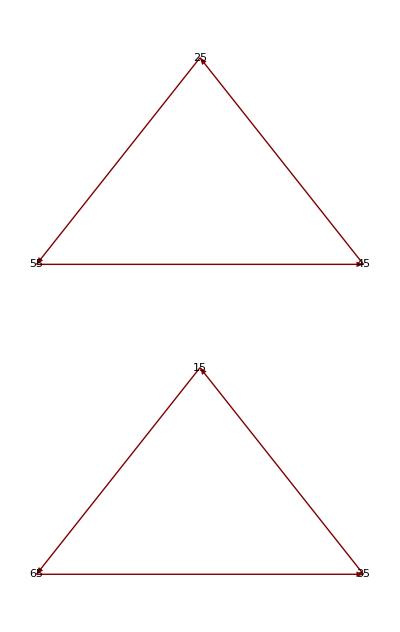

{{15→65,25→55,35→15,45→25,55→45,65→35},1,94}

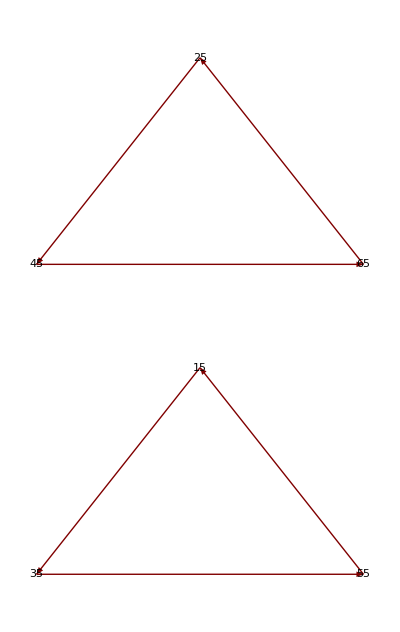

{{15→35,25→45,35→55,45→65,55→15,65→25},2,94}

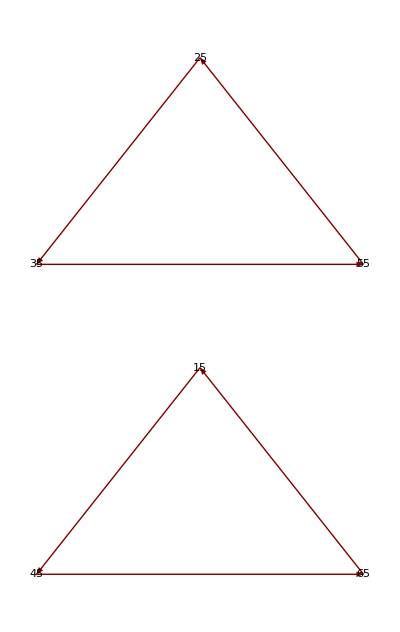

{{15→45,25→35,35→55,45→65,55→25,65→15},5,94}

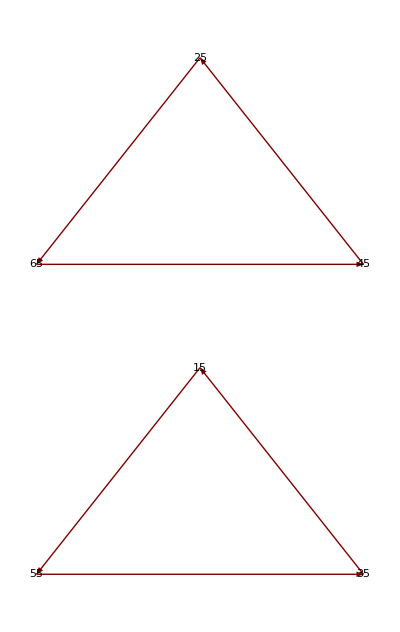

{{15→55,25→65,35→15,45→25,55→35,65→45},5,115}

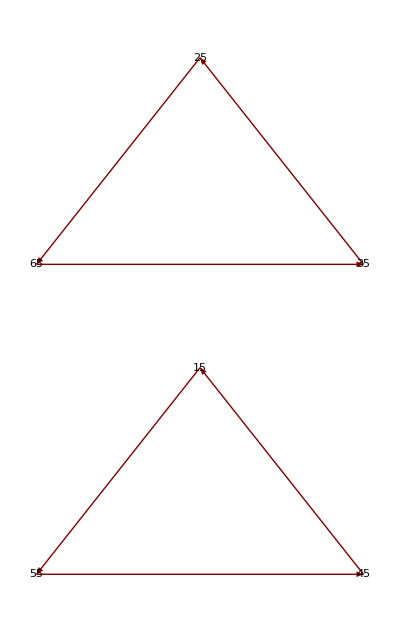

{{15→55,25→65,35→25,45→15,55→45,65→35},8,115}

```mathematica
lst=isissssisisslessfifteen;
For[i=1,i≤64,i++,If[Length[lst[[i,1]]]≤6,Print[TreePlot[lst[[i,1]],DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True]];Print[lst[[i]]]]]
```

```mathematica
If[Length[Trans]≤Lngthn,Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True]]]
```

```mathematica
************************************
```

```mathematica
isissssisisslessfifteenisissssisisslessfifteen={};EndSet={};trans={};
For[i=1,i≤1097,i++,For[j=1,j≤5,j++,EndSet=StartSet/.isissssisisslessfifteen[[j,1]]/.isissssisisslessfifteen[[i,1]];trans=Exch[{StartSet,EndSet}];If[!MemberQ[isissssisisslessfifteenisissssisisslessfifteen,trans,2],AppendTo[isissssisisslessfifteenisissssisisslessfifteen,{trans,j,i}]];]]//Timing
Clear[i,EndSet,trans,j]
```

```mathematica
arraytd=Flatten[
Array[{StartSet,isissssisisslessfifteen[[#1,1]],isissssisisslessfifteen[[#2,1]],#1,#2}&,{1097,1097}],1];
isissssisisslessfifteenisissssisisslessfifteen=Thread[f[arraytd]]/.{f-> PrmltMltplExchPst};
Export[""]
Clear[arraytd,f]
```

```mathematica
arraytd=Flatten[
Array[
{StartSet,isssssislessfifteen[[#1,1]],isssssislessfifteen[[#2,1]],#1,#2}&,{64,64}
]
,1];
b=Thread[f[arraytd]];
b=b/.{f-> PrmltMltplExchPst};
```

```mathematica
arraytd=Flatten[
Array[{StartSet,isssssislessfifteen[[#1,1]],isssssislessfifteen[[#2,1]],#1,#2}&,{64,64}],1];
b=Thread[f[arraytd]]/.{f-> PrmltMltplExchPst};
```

```mathematica
arraytd=Flatten[
Array[{StartSet,isssssislessfifteen[[#1,1]],isssssislessfifteen[[#2,1]],#1,#2}&,{64,64}],1];
isssssislessfifteenisssssislessfifteen=Thread[f[arraytd]]/.{f-> PrmltMltplExchPst};
```

```mathematica
************************************
```